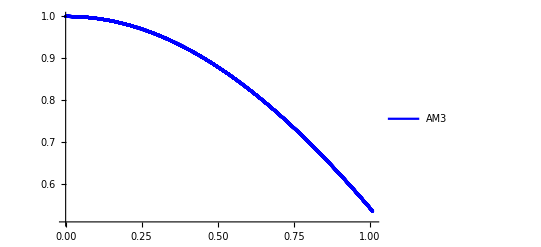

```mathematica
Clear[p1,p2,p3];
p1=ListLinePlot[{{0.00020000000000000000958,0.99999998546749757633},{0.00030000000000000002793,0.99999997130249251853},{0.00040000000000000001917,0.99999995241030203985},{0.00050000000000000001041,0.99999992870109577492},{0.00060000000000000005586,0.99999990008947581277},{0.00070000000000000010131,0.99999986649409577932},{0.00080000000000000014676,0.99999982783731533598},{0.00090000000000000019221,0.99999978404488798489},{0.0010000000000000002377,0.99999973504567774008},{0.0011000000000000002831,0.99999968077140222178},{0.0012000000000000003286,0.99999962115640028681},{0.001300000000000000374,0.99999955613742141924},{0.0014000000000000004195,0.99999948565343421691},{0.0015000000000000004649,0.9999994096454534187},{0.0016000000000000005104,0.99999932805638236388},{0.0017000000000000005558,0.99999924083087055049},{0.0018000000000000006013,0.99999914791518429436},{0.0019000000000000006467,0.99999904925708937853},{0.0020000000000000004753,0.99999894480574391675},{0.0021000000000000003039,0.9999988345116024302},{0.0022000000000000001325,0.99999871832632691859},{0.0022999999999999999611,0.99999859620270759031},{0.0023999999999999997898,0.99999846809459003172},{0.0024999999999999996184,0.99999833395680903791},{0.002599999999999999447,0.99999819374512832759},{0.0026999999999999992756,0.99999804741618625314},{0.0027999999999999991042,0.99999789492744550756},{0.0028999999999999989328,0.99999773623714771631},{0.0029999999999999987614,0.999997571304272026},{0.00309999999999999859,0.99999740008849746786},{0.0031999999999999984186,0.99999722255016798567},{0.0032999999999999982472,0.99999703865026112748},{0.0033999999999999980758,0.99999684835035906882},{0.0034999999999999979045,0.99999665161262207835},{0.0035999999999999977331,0.99999644839976464805},{0.0036999999999999975617,0.99999623867503273367},{0.0037999999999999973903,0.99999602240218354865},{0.0038999999999999972189,0.99999579954546691241},{0.0039999999999999974812,0.9999955700696078198},{0.0040999999999999977435,0.99999533393979023188},{0.0041999999999999980058,0.99999509112164242097},{0.0042999999999999982681,0.99999484158122398103},{0.0043999999999999985303,0.999994585285012616},{0.0044999999999999987926,0.99999432219989237147},{0.0045999999999999990549,0.99999405229314342058},{0.0046999999999999993172,0.99999377553243140593},{0.0047999999999999995795,0.99999349188579811365},{0.0048999999999999998418,0.99999320132165292474},{0.0050000000000000001041,0.99999290380876448836},{0.0051000000000000003664,0.99999259931625283926},{0.0052000000000000006287,0.99999228781358218132},{0.005300000000000000891,0.99999196927055422623},{0.0054000000000000011532,0.99999164365730153214},{0.0055000000000000014155,0.99999131094428206357},{0.0056000000000000016778,0.99999097110227275209},{0.0057000000000000019401,0.99999062410236416731},{0.0058000000000000022024,0.99999026991595563185},{0.0059000000000000024647,0.99998990851475044739},{0.006000000000000002727,0.99998953987075045458},{0.0061000000000000029893,0.99998916395625203624},{0.0062000000000000032516,0.99998878074384167647},{0.0063000000000000035139,0.99998839020639196384},{0.0064000000000000037761,0.9999879923170575946},{0.0065000000000000040384,0.99998758704927137586},{0.0066000000000000043007,0.99998717437674045083},{0.006700000000000004563,0.99998675427344274613},{0.0068000000000000048253,0.99998632671362430724},{0.0069000000000000050876,0.99998589167179463555},{0.0070000000000000053499,0.9999854491227242459},{0.0071000000000000056122,0.99998499904144189099},{0.0072000000000000058745,0.99998454140323034256},{0.0073000000000000061368,0.99998407618362428195},{0.007400000000000006399,0.9999836033584067474},{0.0075000000000000066613,0.99998312290360680255},{0.0076000000000000069236,0.99998263479549653887},{0.0077000000000000071859,0.99998213901058807807},{0.0078000000000000074482,0.99998163552563157364},{0.0079000000000000077105,0.99998112431761210228},{0.0080000000000000071054,0.99998060536374711038},{0.0081000000000000065004,0.9999800786414839715},{0.0082000000000000058953,0.99997954412849732186},{0.0083000000000000052902,0.99997900180268683989},{0.0084000000000000046851,0.99997845164217469272},{0.0085000000000000040801,0.99997789362530331569},{0.008600000000000003475,0.99997732773063308098},{0.0087000000000000028699,0.99997675393693996604},{0.0088000000000000022649,0.99997617222321322217},{0.0089000000000000016598,0.99997558256865326509},{0.0090000000000000010547,0.99997498495266945451},{0.0091000000000000004496,0.99997437935487765159},{0.0091999999999999998446,0.9999737657550986647},{0.0092999999999999992395,0.99997314413335580685},{0.0093999999999999986344,0.99997251446987267531},{0.0094999999999999980294,0.99997187674507115318},{0.0095999999999999974243,0.99997123093956963302},{0.0096999999999999968192,0.99997057703418090746},{0.0097999999999999962141,0.99996991500991017077},{0.0098999999999999956091,0.99996924484795302046},{0.009999999999999995004,0.99996856652969323687},{0.010099999999999994399,0.99996788003670156186},{0.010199999999999993794,0.99996718535073314538},{0.010299999999999993189,0.99996648245372610209},{0.010399999999999992584,0.999965771327799402},{0.010499999999999991979,0.99996505195525131615},{0.010599999999999991374,0.99996432431855730716},{0.010699999999999990768,0.99996358840036847493},{0.010799999999999990163,0.99996284418350944723},{0.010899999999999989558,0.99996209165097693639},{0.010999999999999988953,0.99996133078593807397},{0.011099999999999988348,0.99996056157172852341},{0.011199999999999987743,0.99995978399185103669},{0.011299999999999987138,0.99995899802997334493},{0.011399999999999986533,0.99995820366992682615},{0.011499999999999985928,0.99995740089570461784},{0.011599999999999985323,0.99995658969146028472},{0.011699999999999984718,0.99995577004150637546},{0.011799999999999984113,0.99995494193031209118},{0.011899999999999983508,0.99995410534250239731},{0.011999999999999982903,0.99995326026285591414},{0.012099999999999982297,0.99995240667630391762},{0.012199999999999981692,0.99995154456792856301},{0.012299999999999981087,0.99995067392296121955},{0.012399999999999980482,0.99994979472678136023},{0.012499999999999979877,0.99994890696491478543},{0.012599999999999979272,0.99994801062303217964},{0.012699999999999978667,0.99994710568694744612},{0.012799999999999978062,0.99994619214261715179},{0.012899999999999977457,0.99994526997613808472},{0.012999999999999976852,0.99994433917374625498},{0.013099999999999976247,0.99994339972181556231},{0.013199999999999975642,0.99994245160685624185},{0.013299999999999975037,0.99994149481551375391},{0.013399999999999974432,0.99994052933456734067},{0.013499999999999973826,0.99993955515092858288},{0.013599999999999973221,0.99993857225164006763},{0.013699999999999972616,0.99993758062387416707},{0.013799999999999972011,0.99993658025493215025},{0.013899999999999971406,0.99993557113224207367},{0.013999999999999970801,0.99993455324335756007},{0.014099999999999970196,0.99993352657595735433},{0.014199999999999969591,0.99993249111784332506},{0.014299999999999968986,0.99993144685693990947},{0.014399999999999968381,0.99993039378129200401},{0.014499999999999967776,0.99992933187906474224},{0.014599999999999967171,0.99992826113854160752},{0.014699999999999966566,0.99992718154812343379},{0.014799999999999965961,0.99992609309632707326},{0.014899999999999965355,0.99992499577178450831},{0.01499999999999996475,0.99992388956324174121},{0.015099999999999964145,0.99992277445955757287},{0.01519999999999996354,0.99992165044970249266},{0.015299999999999962935,0.99992051752275690202},{0.01539999999999996233,0.99991937566791111447},{0.015499999999999961725,0.99991822487446369028},{0.01559999999999996112,0.99991706513182010418},{0.015699999999999960515,0.9999158964294921903},{0.01579999999999995991,0.99991471875709669881},{0.015899999999999959305,0.99991353210435485188},{0.0159999999999999587,0.9999123364610904563},{0.016099999999999958095,0.9999111318172296814},{0.01619999999999995749,0.99990991816279928273},{0.016299999999999956884,0.99990869548792615795},{0.016399999999999956279,0.99990746378283590357},{0.016499999999999955674,0.99990622303785203773},{0.016599999999999955069,0.99990497324339533414},{0.016699999999999954464,0.99990371438998237874},{0.016799999999999953859,0.99990244646822512564},{0.016899999999999953254,0.99990116946882945381},{0.016999999999999952649,0.99989988338259438994},{0.017099999999999952044,0.99989858820041099818},{0.017199999999999951439,0.99989728391326182511},{0.017299999999999950834,0.99989597051221978941},{0.017399999999999950229,0.99989464798844740479},{0.017499999999999949624,0.99989331633319566972},{0.017599999999999949019,0.99989197553780340133},{0.017699999999999948413,0.99989062559369601413},{0.017799999999999947808,0.99988926649238496491},{0.017899999999999947203,0.99988789822546686459},{0.017999999999999946598,0.99988652078462270101},{0.018099999999999945993,0.9998851341616169508},{0.018199999999999945388,0.99988373834829624709},{0.018299999999999944783,0.99988233333658949054},{0.018399999999999944178,0.99988091911850607296},{0.018499999999999943573,0.99987949568613576634},{0.018599999999999942968,0.99987806303164783461},{0.018699999999999942363,0.99987662114728981244},{0.018799999999999941758,0.9998751700253869501},{0.018899999999999941153,0.99987370965834176939},{0.018999999999999940548,0.99987224003863284238},{0.019099999999999939942,0.9998707611588141253},{0.019199999999999939337,0.99986927301151440339},{0.019299999999999938732,0.99986777558943629174},{0.019399999999999938127,0.99986626888535568014},{0.019499999999999937522,0.99986475289212117801},{0.019599999999999936917,0.99986322760265267107},{0.019699999999999936312,0.99986169300994143239},{0.019799999999999935707,0.99986014910704901215},{0.019899999999999935102,0.99985859588710657153},{0.019999999999999934497,0.99985703334331410552},{0.020099999999999933892,0.99985546146894010988},{0.020199999999999933287,0.99985388025732035988},{0.020299999999999932682,0.99985228970185768826},{0.020399999999999932077,0.99985068979602109707},{0.020499999999999931471,0.9998490805333452025},{0.020599999999999930866,0.99984746190742945782},{0.020699999999999930261,0.99984583391193748714},{0.020799999999999929656,0.99984419654059686344},{0.020899999999999929051,0.99984254978719777629},{0.020999999999999928446,0.99984089364559292079},{0.021099999999999927841,0.99983922810969649841},{0.021199999999999927236,0.99983755317348421698},{0.021299999999999926631,0.99983586883099218046},{0.021399999999999926026,0.99983417507631644483},{0.021499999999999925421,0.99983247190361201895},{0.021599999999999924816,0.99983075930709297552},{0.021699999999999924211,0.99982903728103122987},{0.021799999999999923606,0.99982730581975642892},{0.021899999999999923,0.99982556491765517404},{0.021999999999999922395,0.99982381456917046592},{0.02209999999999992179,0.99982205476880103845},{0.022199999999999921185,0.99982028551110113668},{0.02229999999999992058,0.99981850679067962862},{0.022399999999999919975,0.99981671860219956116},{0.02249999999999991937,0.99981492094037749396},{0.022599999999999918765,0.9998131137999833884},{0.02269999999999991816,0.99981129717583960836},{0.022799999999999917555,0.99980947106282047621},{0.02289999999999991695,0.99980763545585205065},{0.022999999999999916345,0.99980579034991112763},{0.02309999999999991574,0.99980393574002512924},{0.023199999999999915135,0.99980207162127165965},{0.023299999999999914529,0.99980019798877761694},{0.023399999999999913924,0.99979831483771886003},{0.023499999999999913319,0.99979642216331998661},{0.023599999999999912714,0.99979451996085366705},{0.023699999999999912109,0.99979260822563986721},{0.023799999999999911504,0.99979068695304562642},{0.023899999999999910899,0.99978875613848494641},{0.023999999999999910294,0.99978681577741768116},{0.024099999999999909689,0.99978486586534953684},{0.024199999999999909084,0.99978290639783129468},{0.024299999999999908479,0.99978093737045858891},{0.024399999999999907874,0.9997789587788714627},{0.024499999999999907269,0.99977697061875381301},{0.024599999999999906664,0.99977497288583305757},{0.024699999999999906058,0.99977296557587935766},{0.024799999999999905453,0.99977094868470595124},{0.024899999999999904848,0.99976892220816793166},{0.024999999999999904243,0.99976688614216202566},{0.025099999999999903638,0.99976484048262637128},{0.025199999999999903033,0.99976278522553996275},{0.025299999999999902428,0.99976072036692265055},{0.025399999999999901823,0.99975864590283403111},{0.025499999999999901218,0.99975656182937355787},{0.025599999999999900613,0.99975446814267987516},{0.025699999999999900008,0.99975236483893070716},{0.025799999999999899403,0.99975025191434208072},{0.025899999999999898798,0.99974812936516843642},{0.025999999999999898193,0.99974599718770196244},{0.026099999999999897587,0.9997438553782720394},{0.026199999999999896982,0.9997417039332451294},{0.026299999999999896377,0.99973954284902444289},{0.026399999999999895772,0.99973737212204938363},{0.026499999999999895167,0.99973519174879510452},{0.026599999999999894562,0.99973300172577261868},{0.026699999999999893957,0.9997308020495280223},{0.026799999999999893352,0.99972859271664216152},{0.026899999999999892747,0.99972637372373063247},{0.026999999999999892142,0.99972414506744278206},{0.027099999999999891537,0.99972190674446237413},{0.027199999999999890932,0.99971965875150625713},{0.027299999999999890327,0.99971740108532458624},{0.027399999999999889722,0.99971513374270015717},{0.027499999999999889116,0.99971285672044818416},{0.027599999999999888511,0.99971057001541652198},{0.027699999999999887906,0.99970827362448433373},{0.027799999999999887301,0.99970596754456286792},{0.027899999999999886696,0.99970365177259401523},{0.027999999999999886091,0.99970132630555097464},{0.028099999999999885486,0.99969899114043736521},{0.028199999999999884881,0.99969664627428711512},{0.028299999999999884276,0.9996942917041643506},{0.028399999999999883671,0.99969192742716239675},{0.028499999999999883066,0.99968955344040433264},{0.028599999999999882461,0.9996871697410423252},{0.028699999999999881856,0.99968477632625762919},{0.028799999999999881251,0.99968237319325947698},{0.028899999999999880645,0.99967996033928563371},{0.02899999999999988004,0.99967753776160150903},{0.029099999999999879435,0.99967510545750060125},{0.02919999999999987883,0.99967266342430383119},{0.029299999999999878225,0.99967021165935898708},{0.02939999999999987762,0.99966775016004083554},{0.029499999999999877015,0.99966527892375078856},{0.02959999999999987641,0.99966279794791645941},{0.029699999999999875805,0.9996603072299917736},{0.0297999999999998752,0.99965780676745596978},{0.029899999999999874595,0.99965529655781448781},{0.02999999999999987399,0.99965277659859752557},{0.030099999999999873385,0.99965024688736059399},{0.03019999999999987278,0.99964770742168407303},{0.030299999999999872174,0.99964515819917265649},{0.030399999999999871569,0.99964259921745535209},{0.030499999999999870964,0.9996400304741853704},{0.030599999999999870359,0.99963745196703956974},{0.030699999999999869754,0.99963486369371845619},{0.030799999999999869149,0.99963226565194607254},{0.030899999999999868544,0.99962965783946966525},{0.030999999999999867939,0.99962704025405901831},{0.031099999999999867334,0.99962441289350656426},{0.031199999999999866729,0.99962177575562716214},{0.031299999999999869593,0.99961912883825820852},{0.031399999999999872458,0.99961647213925897137},{0.031499999999999875322,0.999613805656510368},{0.031599999999999878186,0.99961112938791496507},{0.031699999999999881051,0.99960844333139664553},{0.031799999999999883915,0.99960574748490027552},{0.031899999999999886779,0.99960304184639192648},{0.031999999999999889644,0.99960032641385831997},{0.032099999999999892508,0.99959760118530649464},{0.032199999999999895373,0.99959486615876380622},{0.032299999999999898237,0.99959212133227781649},{0.032399999999999901101,0.99958936670391584922},{0.032499999999999903966,0.99958660227176499014},{0.03259999999999990683,0.99958382803393186489},{0.032699999999999909694,0.99958104398854241701},{0.032799999999999912559,0.99957825013374168588},{0.032899999999999915423,0.99957544646769358465},{0.032999999999999918288,0.99957263298858090028},{0.033099999999999921152,0.99956980969460496045},{0.033199999999999924016,0.99956697658398530049},{0.033299999999999926881,0.99956413365495955237},{0.033399999999999929745,0.99956128090578366674},{0.033499999999999932609,0.99955841833473135782},{0.033599999999999935474,0.99955554594009399239},{0.033699999999999938338,0.99955266372018025667},{0.033799999999999941203,0.99954977167331604537},{0.033899999999999944067,0.9995468697978446837},{0.033999999999999946931,0.99954395809212626123},{0.034099999999999949796,0.99954103655453763189},{0.03419999999999995266,0.99953810518347252501},{0.034299999999999955524,0.99953516397734087917},{0.034399999999999958389,0.9995322129345687312},{0.034499999999999961253,0.99952925205359866023},{0.034599999999999964118,0.9995262813328891216},{0.034699999999999966982,0.99952330077091411376},{0.034799999999999969846,0.99952031036616351134},{0.034899999999999972711,0.99951731011714273212},{0.034999999999999975575,0.99951430002237262595},{0.035099999999999978439,0.99951128008038914174},{0.035199999999999981304,0.99950825028974288333},{0.035299999999999984168,0.99950521064899977564},{0.035399999999999987033,0.99950216115674039852},{0.035499999999999989897,0.99949910181155976474},{0.035599999999999992761,0.99949603261206743099},{0.035699999999999995626,0.99949295355688738685},{0.03579999999999999849,0.99948986464465783275},{0.035900000000000001354,0.9994867658740307359},{0.036000000000000004219,0.99948365724367216334},{0.036100000000000007083,0.99948053875226183784},{0.036200000000000009948,0.99947741039849302691},{0.036300000000000012812,0.99947427218107254276},{0.036400000000000015676,0.99947112409872063132},{0.036500000000000018541,0.99946796615017052812},{0.036600000000000021405,0.9994647983341685693},{0.036700000000000024269,0.99946162064947441372},{0.036800000000000027134,0.99945843309486026573},{0.036900000000000029998,0.99945523566911120827},{0.037000000000000032863,0.99945202837102464777},{0.037100000000000035727,0.99944881119941053615},{0.037200000000000038591,0.99944558415309103783},{0.037300000000000041456,0.99944234723090064065},{0.03740000000000004432,0.99943910043168582291},{0.037500000000000047184,0.99943584375430538635},{0.037600000000000050049,0.99943257719762956803},{0.037700000000000052913,0.99942930076054015132},{0.037800000000000055778,0.999426014441931021},{0.037900000000000058642,0.99942271824070705311},{0.038000000000000061506,0.99941941215578478097},{0.038100000000000064371,0.99941609618609217325},{0.038200000000000067235,0.99941277033056796775},{0.038300000000000070099,0.99940943458816233758},{0.038400000000000072964,0.99940608895783611398},{0.038500000000000075828,0.99940273343856111943},{0.038600000000000078693,0.99939936802931961246},{0.038700000000000081557,0.9993959927291046208},{0.038800000000000084421,0.9993926075369198303},{0.038900000000000087286,0.9993892124517792519},{0.03900000000000009015,0.99938580747270711058},{0.039100000000000093014,0.99938239259873806741},{0.039200000000000095879,0.99937896782891655345},{0.039300000000000098743,0.99937553316229699174},{0.039400000000000101608,0.99937208859794390836},{0.039500000000000104472,0.99936863413493137731},{0.039600000000000107336,0.99936516977234357562},{0.039700000000000110201,0.99936169550927378413},{0.039800000000000113065,0.99935821134482527572},{0.039900000000000115929,0.99935471727811031606},{0.040000000000000118794,0.99935121330825094077},{0.040100000000000121658,0.99934769943437806727},{0.040200000000000124523,0.99934417565563193886},{0.040300000000000127387,0.9993406419711616806},{0.040400000000000130251,0.9993370983801255214},{0.040500000000000133116,0.9993335448816903499},{0.04060000000000013598,0.99932998147503204756},{0.040700000000000138844,0.99932640815933515555},{0.040800000000000141709,0.99932282493379276378},{0.040900000000000144573,0.99931923179760651088},{0.041000000000000147438,0.99931562874998636214},{0.041100000000000150302,0.99931201579015072056},{0.041200000000000153166,0.99930839291732653784},{0.041300000000000156031,0.99930476013074887032},{0.041400000000000158895,0.99930111742966065691},{0.041500000000000161759,0.99929746481331283015},{0.041600000000000164624,0.9992938022809645382},{0.041700000000000167488,0.99929012983188247876},{0.041800000000000170353,0.99928644746534156518},{0.041900000000000173217,0.99928275518062414928},{0.042000000000000176081,0.99927905297702035448},{0.042100000000000178946,0.99927534085382763163},{0.04220000000000018181,0.99927161881035109214},{0.042300000000000184674,0.99926788684590328593},{0.042400000000000187539,0.99926414495980420138},{0.042500000000000190403,0.99926039315138082131},{0.042600000000000193268,0.99925663141996745598},{0.042700000000000196132,0.99925285976490552109},{0.042800000000000198996,0.99924907818554387084},{0.042900000000000201861,0.9992452866812381318},{0.043000000000000204725,0.99924148525135048082},{0.04310000000000020759,0.99923767389525042226},{0.043200000000000210454,0.9992338526123141218},{0.043300000000000213318,0.99923002140192429543},{0.043400000000000216183,0.9992261802634703205},{0.043500000000000219047,0.99922232919634812465},{0.043600000000000221911,0.99921846819996018585},{0.043700000000000224776,0.99921459727371575443},{0.04380000000000022764,0.99921071641703018695},{0.043900000000000230505,0.99920682562932539028},{0.044000000000000233369,0.99920292491002948854},{0.044100000000000236233,0.99919901425857682309},{0.044200000000000239098,0.99919509367440750847},{0.044300000000000241962,0.99919116315696809849},{0.044400000000000244826,0.99918722270571114219},{0.044500000000000247691,0.99918327232009496175},{0.044600000000000250555,0.99917931199958398558},{0.04470000000000025342,0.99917534174364852628},{0.044800000000000256284,0.99917136155176455858},{0.044900000000000259148,0.99916737142341383038},{0.045000000000000262013,0.99916337135808375169},{0.045100000000000264877,0.99915936135526750572},{0.045200000000000267741,0.99915534141446360472},{0.045300000000000270606,0.99915131153517622309},{0.04540000000000027347,0.99914727171691486429},{0.045500000000000276335,0.99914322195919480496},{0.045600000000000279199,0.9991391622615362067},{0.045700000000000282063,0.99913509262346478224},{0.045800000000000284928,0.99913101304451146234},{0.045900000000000287792,0.99912692352421239583},{0.046000000000000290656,0.99912282406210861652},{0.046100000000000293521,0.99911871465774659828},{0.046200000000000296385,0.99911459531067770001},{0.04630000000000029925,0.9991104660204583876},{0.046400000000000302114,0.99910632678665012296},{0.046500000000000304978,0.99910217760881891991},{0.046600000000000307843,0.99909801848653601031},{0.046700000000000310707,0.99909384941937728897},{0.046800000000000313571,0.99908967040692320261},{0.046900000000000316436,0.99908548144875919395},{0.0470000000000003193,0.99908128254447536865},{0.047100000000000322165,0.99907707369366638428},{0.047200000000000325029,0.99907285489593145034},{0.047300000000000327893,0.9990686261508742172},{0.047400000000000330758,0.99906438745810299817},{0.047500000000000333622,0.99906013881723076953},{0.047600000000000336486,0.99905588022787439328},{0.047700000000000339351,0.99905161168965506135},{0.047800000000000342215,0.99904733320219862858},{0.04790000000000034508,0.99904304476513516864},{0.048000000000000347944,0.99903874637809864101},{0.048100000000000350808,0.9990344380407276681},{0.048200000000000353673,0.99903011975266498013},{0.048300000000000356537,0.99902579151355708209},{0.048400000000000359401,0.99902145332305469783},{0.048500000000000362266,0.99901710518081243695},{0.04860000000000036513,0.9990127470864890169},{0.048700000000000367995,0.99900837903974726295},{0.048800000000000370859,0.99900400104025388615},{0.048900000000000373723,0.99899961308767915025},{0.049000000000000376588,0.99899521518169753787},{0.049100000000000379452,0.9989908073219869733},{0.049200000000000382316,0.99898638950822937765},{0.049300000000000385181,0.99898196174011011372},{0.049400000000000388045,0.99897752401731876315},{0.04950000000000039091,0.9989730763395480162},{0.049600000000000393774,0.9989686187064943379},{0.049700000000000396638,0.99896415111785796803},{0.049800000000000399503,0.99895967357334269909},{0.049900000000000402367,0.99895518607265543221},{0.050000000000000405231,0.99895068861550706529},{0.050100000000000408096,0.99894618120161149388},{0.05020000000000041096,0.99894166383068616621},{0.050300000000000413825,0.99893713650245208324},{0.050400000000000416689,0.99893259921663346557},{0.050500000000000419553,0.99892805197295753139},{0.050600000000000422418,0.99892349477115527367},{0.050700000000000425282,0.99891892761096068298},{0.050800000000000428146,0.9989143504921108585},{0.050900000000000431011,0.99890976341434645214},{0.051000000000000433875,0.99890516637741100237},{0.05110000000000043674,0.99890055938105104527},{0.051200000000000439604,0.99889594242501655863},{0.051300000000000442468,0.99889131550906051782},{0.051400000000000445333,0.99888667863293878479},{0.051500000000000448197,0.99888203179641021912},{0.051600000000000451061,0.99887737499923656692},{0.051700000000000453926,0.99887270824118268298},{0.05180000000000045679,0.99886803152201630862},{0.051900000000000459655,0.99886334484150807178},{0.052000000000000462519,0.99885864819943137594},{0.052100000000000465383,0.99885394159556262217},{0.052200000000000468248,0.99884922502968098712},{0.052300000000000471112,0.99884449850156842299},{0.052400000000000473976,0.99883976201100954651},{0.052500000000000476841,0.99883501555779163894},{0.052600000000000479705,0.9988302591417046461},{0.05270000000000048257,0.9988254927625416224},{0.052800000000000485434,0.99882071642009784274},{0.052900000000000488298,0.99881593011417135752},{0.053000000000000491163,0.99881113384456288173},{0.053100000000000494027,0.99880632761107535078},{0.053200000000000496891,0.99880151141351491972},{0.053300000000000499756,0.99879668525168974202},{0.05340000000000050262,0.99879184912541030261},{0.053500000000000505485,0.99878700303448986197},{0.053600000000000508349,0.99878214697874434513},{0.053700000000000511213,0.99877728095799178654},{0.053800000000000514078,0.99877240497205266312},{0.053900000000000516942,0.99876751902074978329},{0.054000000000000519806,0.99876262310390839794},{0.054100000000000522671,0.99875771722135620045},{0.054200000000000525535,0.99875280137292299365},{0.0543000000000005284,0.99874787555844124487},{0.054400000000000531264,0.99874293977774519782},{0.054500000000000534128,0.99873799403067142766},{0.054600000000000536993,0.99873303831705895206},{0.054700000000000539857,0.99872807263674912015},{0.054800000000000542721,0.99872309698958516844},{0.054900000000000545586,0.99871811137541244285},{0.05500000000000054845,0.9987131157940786208},{0.055100000000000551315,0.99870811024543371115},{0.055200000000000554179,0.99870309472932949912},{0.055300000000000557043,0.99869806924561976835},{0.055400000000000559908,0.99869303379416052291},{0.055500000000000562772,0.99868798837480976527},{0.055600000000000565636,0.99868293298742760733},{0.055700000000000568501,0.99867786763187615939},{0.055800000000000571365,0.99867279230801941914},{0.05590000000000057423,0.99866770701572349367},{0.056000000000000577094,0.99866261175485626644},{0.056100000000000579958,0.99865750652528773035},{0.056200000000000582823,0.99865239132688987667},{0.056300000000000585687,0.998647266159536251},{0.056400000000000588551,0.99864213102310239734},{0.056500000000000591416,0.99863698591746574706},{0.05660000000000059428,0.99863183084250561894},{0.056700000000000597145,0.99862666579810299705},{0.056800000000000600009,0.99862149078414075287},{0.056900000000000602873,0.99861630580050375627},{0.057000000000000605738,0.99861111084707832042},{0.057100000000000608602,0.99860590592375286789},{0.057200000000000611466,0.99860069103041715355},{0.057300000000000614331,0.99859546616696293064},{0.057400000000000617195,0.99859023133328339572},{0.05750000000000062006,0.9985849865292736327},{0.057600000000000622924,0.99857973175483050188},{0.057700000000000625788,0.99857446700985219579},{0.057800000000000628653,0.99856919229423868334},{0.057900000000000631517,0.99856390760789170979},{0.058000000000000634381,0.99855861295071468575},{0.058100000000000637246,0.9985533083226124651},{0.05820000000000064011,0.99854799372349123399},{0.058300000000000642975,0.99854266915325917697},{0.058400000000000645839,0.99853733461182569986},{0.058500000000000648703,0.99853199009910187378},{0.058600000000000651568,0.99852663561500054623},{0.058700000000000654432,0.99852127115943589697},{0.058800000000000657296,0.998515896732323327},{0.058900000000000660161,0.99851051233358001369},{0.059000000000000663025,0.99850511796312446666},{0.05910000000000066589,0.99849971362087663884},{0.059200000000000668754,0.99849429930675814848},{0.059300000000000671618,0.99848887502069183508},{0.059400000000000674483,0.99848344076260198143},{0.059500000000000677347,0.99847799653241431361},{0.059600000000000680211,0.99847254233005577895},{0.059700000000000683076,0.99846707815545487907},{0.05980000000000068594,0.9984616040085414479},{0.059900000000000688805,0.99845611988924676261},{0.060000000000000691669,0.99845062579750321063},{0.060100000000000694533,0.99844512173324462267},{0.060200000000000697398,0.99843960769640627273},{0.060300000000000700262,0.998434083686924434},{0.060400000000000703126,0.99842854970473693399},{0.060500000000000705991,0.99842300574978271044},{0.060600000000000708855,0.9984174518220018113},{0.06070000000000071172,0.99841188792133572782},{0.060800000000000714584,0.99840631404772739455},{0.060900000000000717448,0.99840073020112085622},{0.061000000000000720313,0.99839513638146126784},{0.061100000000000723177,0.9983895325886948946},{0.061200000000000726041,0.99838391882276922296},{0.061300000000000728906,0.99837829508363329367},{0.06140000000000073177,0.99837266137123703569},{0.061500000000000734635,0.99836701768553148817},{0.061600000000000737499,0.99836136402646891153},{0.061700000000000740363,0.99835570039400278741},{0.061800000000000743228,0.99835002678808781873},{0.061900000000000746092,0.99834434320867937451},{0.062000000000000748956,0.99833864965573415606},{0.062100000000000751821,0.99833294612921030797},{0.062200000000000754685,0.99832723262906675199},{0.06230000000000075755,0.99832150915526329804},{0.062400000000000760414,0.99831577570776119934},{0.062500000000000763278,0.99831003228652259729},{0.062600000000000766143,0.9983042788915107435},{0.062700000000000769007,0.99829851552268977777},{0.062800000000000771871,0.99829274218002506114},{0.062900000000000774736,0.99828695886348306487},{0.0630000000000007776,0.99828116557303114842},{0.063100000000000780465,0.99827536230863744837},{0.063200000000000783329,0.99826954907027132258},{0.063300000000000786193,0.99826372585790312808},{0.063400000000000789058,0.99825789267150433215},{0.063500000000000791922,0.99825204951104729023},{0.063600000000000794786,0.99824619637650480186},{0.063700000000000797651,0.99824033326785133191},{0.063800000000000800515,0.99823446018506178934},{0.06390000000000080338,0.99822857712811241537},{0.064000000000000806244,0.99822268409698011737},{0.064100000000000809108,0.99821678109164291293},{0.064200000000000811973,0.99821086811207959677},{0.064300000000000814837,0.9982049451582697408},{0.064400000000000817701,0.99819901223019402714},{0.064500000000000820566,0.99819306932783391506},{0.06460000000000082343,0.99818711645117175202},{0.064700000000000826295,0.99818115360019077364},{0.064800000000000829159,0.99817518077487510375},{0.064900000000000832023,0.99816919797520953228},{0.065000000000000834888,0.9981632052011799594},{0.065100000000000837752,0.99815720245277306244},{0.065200000000000840616,0.99815118972997640689},{0.065300000000000843481,0.99814516703277844645},{0.065400000000000846345,0.99813913436116807887},{0.06550000000000084921,0.99813309171513520113},{0.065600000000000852074,0.9981270390946707094},{0.065700000000000854938,0.99812097649976594393},{0.065800000000000857803,0.99811490393041335523},{0.065900000000000860667,0.99810882138660594887},{0.066000000000000863531,0.99810272886833772965},{0.066100000000000866396,0.99809662637560347953},{0.06620000000000086926,0.99809051390839853557},{0.066300000000000872125,0.99808439146671890096},{0.066400000000000874989,0.99807825905056168914},{0.066500000000000877853,0.99807211665992445759},{0.066600000000000880718,0.99806596429480565202},{0.066700000000000883582,0.9980598019552041622},{0.066800000000000886446,0.99805362964112009916},{0.066900000000000889311,0.998047447352554018},{0.067000000000000892175,0.99804125508950713996},{0.06710000000000089504,0.99803505285198157448},{0.067200000000000897904,0.99802884063997976405},{0.067300000000000900768,0.99802261845350526137},{0.067400000000000903633,0.99801638629256206325},{0.067500000000000906497,0.9980101441571551657},{0.067600000000000909361,0.99800389204728978676},{0.067700000000000912226,0.99799762996297203266},{0.06780000000000091509,0.99799135790420856473},{0.067900000000000917955,0.99798507587100682148},{0.068000000000000920819,0.9979787838633747965},{0.068100000000000923683,0.99797248188132126057},{0.068200000000000926548,0.99796616992485576159},{0.068300000000000929412,0.99795984799398818055},{0.068400000000000932276,0.99795351608872928661},{0.068500000000000935141,0.997947174209090071},{0.068600000000000938005,0.9979408223550825241},{0.06870000000000094087,0.99793446052671885838},{0.068800000000000943734,0.9979280887240123965},{0.068900000000000946598,0.99792170694697701627},{0.069000000000000949463,0.99791531519562692853},{0.069100000000000952327,0.9979089134699771213},{0.069200000000000955191,0.99790250177004280463},{0.069300000000000958056,0.99789608009584007675},{0.06940000000000096092,0.99788964844738570203},{0.069500000000000963785,0.99788320682469699996},{0.069600000000000966649,0.99787675522779173409},{0.069700000000000969513,0.99787029365668811209},{0.069800000000000972378,0.99786382211140500775},{0.069900000000000975242,0.99785734059196218304},{0.070000000000000978106,0.99785084909837962197},{0.070100000000000980971,0.99784434763067786367},{0.070200000000000983835,0.99783783618887778033},{0.0703000000000009867,0.99783131477300124335},{0.070400000000000989564,0.99782478338307045718},{0.070500000000000992428,0.99781824201910829242},{0.070600000000000995293,0.99781169068113795273},{0.070700000000000998157,0.99780512936918297484},{0.070800000000001001021,0.99779855808326767264},{0.070900000000001003886,0.99779197682341702613},{0.07100000000000100675,0.99778538558965623739},{0.071100000000001009615,0.99777878438201117461},{0.071200000000001012479,0.99777217320050803906},{0.071300000000001015343,0.99776555204517347608},{0.071400000000001018208,0.99775892091603490819},{0.071500000000001021072,0.99775227981312042402},{0.071600000000001023936,0.99774562873645811223},{0.071700000000001026801,0.99773896768607672758},{0.071800000000001029665,0.99773229666200557997},{0.07190000000000103253,0.99772561566427442337},{0.072000000000001035394,0.9977189246929132338},{0.072100000000001038258,0.99771222374795276444},{0.072200000000001041123,0.99770551282942399052},{0.072300000000001043987,0.99769879193735855338},{0.072400000000001046851,0.99769206107178853848},{0.072500000000001049716,0.99768532023274658638},{0.07260000000000105258,0.99767856942026555966},{0.072700000000001055445,0.99767180863437865401},{0.072800000000001058309,0.99766503787511995327},{0.072900000000001061173,0.99765825714252343026},{0.073000000000001064038,0.99765146643662383497},{0.073100000000001066902,0.99764466575745636145},{0.073200000000001069766,0.99763785510505653686},{0.073300000000001072631,0.99763103447946044344},{0.073400000000001075495,0.99762420388070427446},{0.07350000000000107836,0.99761736330882488932},{0.073600000000001081224,0.9976105127638594805},{0.073700000000001084088,0.99760365224584568455},{0.073800000000001086953,0.99759678175482147111},{0.073900000000001089817,0.99758990129082525389},{0.074000000000001092682,0.99758301085389589069},{0.074100000000001095546,0.99757611044407279444},{0.07420000000000109841,0.99756920006139560009},{0.074300000000001101275,0.99756227970590416465},{0.074400000000001104139,0.99755534937763901127},{0.074500000000001107003,0.99754840907664088512},{0.074600000000001109868,0.9975414588029510865},{0.074700000000001112732,0.99753449855661102674},{0.074800000000001115597,0.99752752833766278329},{0.074900000000001118461,0.99752054814614854461},{0.075000000000001121325,0.9975135579821110543},{0.07510000000000112419,0.99750655784559338901},{0.075200000000001127054,0.99749954773663918051},{0.075300000000001129918,0.9974925276552922826},{0.075400000000001132783,0.99748549760159688216},{0.075500000000001135647,0.99747845757559761015},{0.075600000000001138512,0.99747140757733909755},{0.075700000000001141376,0.99746434760686664145},{0.07580000000000114424,0.99745727766422598304},{0.075900000000001147105,0.99745019774946297453},{0.076000000000001149969,0.9974431078626238012},{0.076100000000001152833,0.99743600800375498139},{0.076200000000001155698,0.99742889817290369958},{0.076300000000001158562,0.99742177837011725128},{0.076400000000001161427,0.99741464859544326504},{0.076500000000001164291,0.99740750884892970252},{0.076600000000001167155,0.99740035913062485839},{0.07670000000000117002,0.99739319944057736045},{0.076800000000001172884,0.99738602977883628053},{0.076900000000001175748,0.99737885014545091256},{0.077000000000001178613,0.99737166054047088348},{0.077100000000001181477,0.99736446096394604233},{0.077200000000001184342,0.99735725141592690424},{0.077300000000001187206,0.9973500318964642064},{0.07740000000000119007,0.99734280240560879705},{0.077500000000001192935,0.99733556294341185744},{0.077600000000001195799,0.99732831350992490194},{0.077700000000001198663,0.99732105410519988897},{0.077800000000001201528,0.99731378472928877699},{0.077900000000001204392,0.99730650538224385748},{0.078000000000001207257,0.9972992160641180881},{0.078100000000001210121,0.99729191677496420443},{0.078200000000001212985,0.99728460751483583024},{0.07830000000000121585,0.99727728828378658932},{0.078400000000001218714,0.99726995908187054951},{0.078500000000001221578,0.99726261990914188971},{0.078600000000001224443,0.99725527076565501083},{0.078700000000001227307,0.99724791165146475791},{0.078800000000001230172,0.99724054256662630902},{0.078900000000001233036,0.99723316351119495327},{0.0790000000000012359,0.99722577448522642385},{0.079100000000001238765,0.99721837548877667601},{0.079200000000001241629,0.99721096652190166498},{0.079300000000001244493,0.99720354758465812317},{0.079400000000001247358,0.99719611867710278297},{0.079500000000001250222,0.99718867979929259882},{0.079600000000001253087,0.99718123095128496924},{0.079700000000001255951,0.99717377213313740381},{0.079800000000001258815,0.99716630334490807819},{0.07990000000000126168,0.99715882458665505705},{0.080000000000001264544,0.99715133585843662711},{0.080100000000001267408,0.99714383716031129712},{0.080200000000001270273,0.99713632849233801991},{0.080300000000001273137,0.99712880985457597038},{0.080400000000001276002,0.99712128124708465648},{0.080500000000001278866,0.99711374266992369719},{0.08060000000000128173,0.99710619412315315557},{0.080700000000001284595,0.99709863560683342776},{0.080800000000001287459,0.99709106712102490988},{0.080900000000001290323,0.9970834886657881091},{0.081000000000001293188,0.99707590024118419869},{0.081100000000001296052,0.99706830184727435196},{0.081200000000001298917,0.99706069348411996422},{0.081300000000001301781,0.99705307515178254185},{0.081400000000001304645,0.99704544685032425733},{0.08150000000000130751,0.99703780857980728314},{0.081600000000001310374,0.99703016034029401382},{0.081700000000001313238,0.99702250213184706595},{0.081800000000001316103,0.9970148339545295002},{0.081900000000001318967,0.99700715580840437724},{0.082000000000001321832,0.99699946769353497977},{0.082100000000001324696,0.99699176960998503461},{0.08220000000000132756,0.99698406155781837956},{0.082300000000001330425,0.99697634353709907451},{0.082400000000001333289,0.99696861554789140136},{0.082500000000001336153,0.99696087759025986408},{0.082600000000001339018,0.99695312966426907764},{0.082700000000001341882,0.99694537176998410111},{0.082800000000001344747,0.99693760390747032663},{0.082900000000001347611,0.99692982607679314633},{0.083000000000001350475,0.99692203827801806337},{0.08310000000000135334,0.99691424051121124705},{0.083200000000001356204,0.99690643277643853359},{0.083300000000001359068,0.99689861507376631433},{0.083400000000001361933,0.9968907874032609806},{0.083500000000001364797,0.99688294976498936784},{0.083600000000001367662,0.9968751021590185335},{0.083700000000001370526,0.99686724458541553506},{0.08380000000000137339,0.99685937704424798511},{0.083900000000001376255,0.99685149953558316316},{0.084000000000001379119,0.99684361205948901485},{0.084100000000001381983,0.99683571461603359687},{0.084200000000001384848,0.99682780720528518792},{0.084300000000001387712,0.99681988982731206672},{0.084400000000001390577,0.99681196248218295608},{0.084500000000001393441,0.99680402516996668982},{0.084600000000001396305,0.99679607789073210178},{0.08470000000000139917,0.99678812064454858088},{0.084800000000001402034,0.99678015343148584915},{0.084900000000001404898,0.99677217625161351755},{0.085000000000001407763,0.9967641891050013081},{0.085100000000001410627,0.99675619199171938689},{0.085200000000001413492,0.99674818491183792002},{0.085300000000001416356,0.9967401678654271846},{0.08540000000000141922,0.99673214085255812389},{0.085500000000001422085,0.99672410387330134807},{0.085600000000001424949,0.99671605692772791141},{0.085700000000001427813,0.99670800001590897921},{0.085800000000001430678,0.99669993313791604983},{0.085900000000001433542,0.99669185629382062164},{0.086000000000001436407,0.99668376948369441504},{0.086100000000001439271,0.99667567270760959453},{0.086200000000001442135,0.9966675659656383246},{0.086300000000001445,0.9966594492578529918},{0.086400000000001447864,0.99665132258432598267},{0.086500000000001450728,0.99664318594513001681},{0.086600000000001453593,0.99663503934033836895},{0.086700000000001456457,0.99662688277002398074},{0.086800000000001459322,0.99661871623426001587},{0.086900000000001462186,0.99661053973312008214},{0.08700000000000146505,0.99660235326667789835},{0.087100000000001467915,0.9965941568350071833},{0.087200000000001470779,0.99658595043818176684},{0.087300000000001473643,0.99657773407627592288},{0.087400000000001476508,0.99656950774936392534},{0.087500000000001479372,0.99656127145752060326},{0.087600000000001482237,0.99655302520082056361},{0.087700000000001485101,0.99654476897933863544},{0.087800000000001487965,0.99653650279314998084},{0.08790000000000149083,0.99652822664232998395},{0.088000000000001493694,0.9965199405269539179},{0.088100000000001496558,0.9965116444470974999},{0.088200000000001499423,0.99650333840283644715},{0.088300000000001502287,0.99649502239424658789},{0.088400000000001505152,0.99648669642140408342},{0.088500000000001508016,0.99647836048438542811},{0.08860000000000151088,0.99647001458326722734},{0.088700000000001513745,0.99646165871812575343},{0.088800000000001516609,0.99645329288903805587},{0.088900000000001519473,0.99644491709608085106},{0.089000000000001522338,0.99643653133933152155},{0.089100000000001525202,0.99642813561886711682},{0.089200000000001528067,0.99641972993476513043},{0.089300000000001530931,0.99641131428710316698},{0.089400000000001533795,0.99640288867595905309},{0.08950000000000153666,0.99639445310141072643},{0.089600000000001539524,0.99638600756353634669},{0.089700000000001542388,0.9963775520624141846},{0.089800000000001545253,0.9963690865981226219},{0.089900000000001548117,0.99636061117074015137},{0.090000000000001550982,0.99635212578034559883},{0.090100000000001553846,0.99634363042701779012},{0.09020000000000155671,0.99633512511083588414},{0.090300000000001559575,0.99632660983187915082},{0.090400000000001562439,0.99631808459022686009},{0.090500000000001565303,0.99630954938595872594},{0.090600000000001568168,0.99630100421915435138},{0.090700000000001571032,0.99629244908989367246},{0.090800000000001573897,0.99628388399825662525},{0.090900000000001576761,0.99627530894432336783},{0.091000000000001579625,0.99626672392817428037},{0.09110000000000158249,0.99625812894988985402},{0.091200000000001585354,0.99624952400955057996},{0.091300000000001588218,0.99624090910723739345},{0.091400000000001591083,0.99623228424303122974},{0.091500000000001593947,0.9962236494170130241},{0.091600000000001596812,0.99621500462926415587},{0.091700000000001599676,0.99620634987986589337},{0.09180000000000160254,0.99619768516889994903},{0.091900000000001605405,0.99618901049644792423},{0.092000000000001608269,0.99618032586259153138},{0.092100000000001611133,0.99617163126741281598},{0.092200000000001613998,0.99616292671099393452},{0.092300000000001616862,0.99615421219341726555},{0.092400000000001619727,0.99614548771476529865},{0.092500000000001622591,0.99613675327512052338},{0.092600000000001625455,0.99612800887456554033},{0.09270000000000162832,0.99611925451318328317},{0.092800000000001631184,0.99611049019105668556},{0.092900000000001634048,0.9961017159082689032},{0.093000000000001636913,0.99609293166490342486},{0.093100000000001639777,0.99608413746104373931},{0.093200000000001642642,0.99607533329677344636},{0.093300000000001645506,0.99606651917217614578},{0.09340000000000164837,0.99605769508733577045},{0.093500000000001651235,0.99604886104233636424},{0.093600000000001654099,0.99604001703726186001},{0.093700000000001656963,0.99603116307219685677},{0.093800000000001659828,0.99602229914722562043},{0.093900000000001662692,0.99601342526243275},{0.094000000000001665557,0.99600454141790295548},{0.094100000000001668421,0.99599564761372105792},{0.094200000000001671285,0.99598674384997232245},{0.09430000000000167415,0.99597783012674168113},{0.094400000000001677014,0.99596890644411439908},{0.094500000000001679878,0.9959599728021760745},{0.094600000000001682743,0.99595102920101219457},{0.094700000000001685607,0.9959420756407084685},{0.094800000000001688472,0.99593311212135071653},{0.094900000000001691336,0.9959241386430247589},{0.0950000000000016942,0.99591515520581674892},{0.095100000000001697065,0.99590616180981317296},{0.095200000000001699929,0.99589715845510018433},{0.095300000000001702793,0.9958881451417642694},{0.095400000000001705658,0.99587912186989224761},{0.095500000000001708522,0.99587008863957082738},{0.095600000000001711387,0.99586104545088682816},{0.095700000000001714251,0.99585199230392740244},{0.095800000000001717115,0.99584292919877981376},{0.09590000000000171998,0.99583385613553121463},{0.096000000000001722844,0.99582477311426897959},{0.096100000000001725708,0.99581568013508081627},{0.096200000000001728573,0.99580657719805421024},{0.096300000000001731437,0.99579746430327720219},{0.096400000000001734302,0.99578834145083772178},{0.096500000000001737166,0.9957792086408238097},{0.09660000000000174003,0.99577006587332383969},{0.096700000000001742895,0.99576091314842618551},{0.096800000000001745759,0.99575175046621933195},{0.096900000000001748623,0.99574257782679176376},{0.097000000000001751488,0.99573339523023240982},{0.097100000000001754352,0.99572420267663031002},{0.097200000000001757217,0.99571500016607417116},{0.097300000000001760081,0.99570578769865336621},{0.097400000000001762945,0.99569656527445704608},{0.09750000000000176581,0.99568733289357480576},{0.097600000000001768674,0.99567809055609612923},{0.097700000000001771538,0.99566883826211050046},{0.097800000000001774403,0.99565957601170751445},{0.097900000000001777267,0.99565030380497732132},{0.098000000000001780132,0.99564102164201007117},{0.098100000000001782996,0.99563172952289569206},{0.09820000000000178586,0.99562242744772455616},{0.098300000000001788725,0.99561311541658703561},{0.098400000000001791589,0.99560379342957394666},{0.098500000000001794453,0.99559446148677555044},{0.098600000000001797318,0.99558511958828288524},{0.098700000000001800182,0.99557576773418698934},{0.098800000000001803047,0.99556640592457856798},{0.098900000000001805911,0.99555703415954899249},{0.099000000000001808775,0.99554765243918952322},{0.09910000000000181164,0.99553826076359164254},{0.099200000000001814504,0.99552885913284683284},{0.099300000000001817368,0.9955194475470466875},{0.099400000000001820233,0.99551002600628279993},{0.099500000000001823097,0.99550059451064731864},{0.099600000000001825962,0.99549115306023217009},{0.099700000000001828826,0.99548170165512961383},{0.09980000000000183169,0.9954722402954320204},{0.099900000000001834555,0.99546276898123153831},{0.10000000000000183742,0.99545328771262076017},{0.10010000000000184028,0.99544379648969238961},{0.10020000000000184315,0.99543429531253901921},{0.10030000000000184601,0.99542478418125368567},{0.10040000000000184888,0.99541526309592931465},{0.10050000000000185174,0.9954057320566591649},{0.10060000000000185461,0.99539619106353649514},{0.10070000000000185747,0.99538664011665445308},{0.10080000000000186033,0.99537707921610663053},{0.1009000000000018632,0.99536750836198684134},{0.10100000000000186606,0.99535792755438878832},{0.10110000000000186893,0.99534833679340628532},{0.10120000000000187179,0.99533873607913325721},{0.10130000000000187466,0.99532912541166373988},{0.10140000000000187752,0.99531950479109188024},{0.10150000000000188038,0.99530987421751171418},{0.10160000000000188325,0.99530023369101772168},{0.10170000000000188611,0.99529058321170482682},{0.10180000000000188898,0.99528092277966750956},{0.10190000000000189184,0.99527125239500047194},{0.10200000000000189471,0.99526157205779874904},{0.10210000000000189757,0.99525188176815726493},{0.10220000000000190044,0.99524218152617116573},{0.1023000000000019033,0.99523247133193570857},{0.10240000000000190616,0.99522275118554637263},{0.10250000000000190903,0.99521302108709874812},{0.10260000000000191189,0.99520328103668831421},{0.10270000000000191476,0.99519353103441088315},{0.10280000000000191762,0.99518377108036226719},{0.10290000000000192049,0.9951740011746383896},{0.10300000000000192335,0.99516422131733539569},{0.10310000000000192621,0.9951544315085495418},{0.10320000000000192908,0.99514463174837708426},{0.10330000000000193194,0.99513482203691439043},{0.10340000000000193481,0.99512500237425782768},{0.10350000000000193767,0.99511517276050431846},{0.10360000000000194054,0.99510533319575078526},{0.1037000000000019434,0.99509548368009370645},{0.10380000000000194627,0.99508562421363022654},{0.10390000000000194913,0.99507575479645760108},{0.10400000000000195199,0.99506587542867297458},{0.10410000000000195486,0.99505598611037349155},{0.10420000000000195772,0.99504608684165651855},{0.10430000000000196059,0.99503617762261975521},{0.10440000000000196345,0.99502625845336090116},{0.10450000000000196632,0.99501632933397787806},{0.10460000000000196918,0.99500639026456838554},{0.10470000000000197204,0.99499644124523056732},{0.10480000000000197491,0.99498648227606256711},{0.10490000000000197777,0.99497651335716263965},{0.10500000000000198064,0.99496653448862926172},{0.1051000000000019835,0.99495654567056091011},{0.10520000000000198637,0.99494654690305583955},{0.10530000000000198923,0.99493653818621308194},{0.1054000000000019921,0.99492651952013133609},{0.10550000000000199496,0.99491649090490941187},{0.10560000000000199782,0.99490645234064645219},{0.10570000000000200069,0.99489640382744171099},{0.10580000000000200355,0.9948863453653944422},{0.10590000000000200642,0.99487627695460378874},{0.10600000000000200928,0.99486619859516933762},{0.10610000000000201215,0.99485611028719056481},{0.10620000000000201501,0.99484601203076727938},{0.10630000000000201787,0.99483590382599929036},{0.10640000000000202074,0.99482578567298662886},{0.1065000000000020236,0.99481565757182921494},{0.10660000000000202647,0.99480551952262730175},{0.10670000000000202933,0.99479537152548125345},{0.1068000000000020322,0.99478521358049121215},{0.10690000000000203506,0.99477504568775776406},{0.10700000000000203793,0.99476486784738127334},{0.10710000000000204079,0.99475468005946277028},{0.10720000000000204365,0.99474448232410295212},{0.10730000000000204652,0.99473427464140273813},{0.10740000000000204938,0.9947240570114631586},{0.10750000000000205225,0.99471382943438535484},{0.10760000000000205511,0.99470359191027046819},{0.10770000000000205798,0.99469334443921997302},{0.10780000000000206084,0.99468308702133523269},{0.1079000000000020637,0.99467281965671794364},{0.10800000000000206657,0.99466254234546969126},{0.10810000000000206943,0.99465225508769228302},{0.1082000000000020723,0.99464195788348752636},{0.10830000000000207516,0.99463165073295778384},{0.10840000000000207803,0.99462133363620497395},{0.10850000000000208089,0.99461100659333123719},{0.10860000000000208376,0.99460066960443915818},{0.10870000000000208662,0.99459032266963109947},{0.10880000000000208948,0.99457996578900964568},{0.10890000000000209235,0.99456959896267749244},{0.10900000000000209521,0.99455922219073733537},{0.10910000000000209808,0.99454883547329209215},{0.10920000000000210094,0.99453843881044468045},{0.10930000000000210381,0.99452803220229823999},{0.10940000000000210667,0.99451761564895602152},{0.10950000000000210953,0.99450718915052149782},{0.1096000000000021124,0.99449675270709803065},{0.10970000000000211526,0.99448630631878887076},{0.10980000000000211813,0.99447584998569771297},{0.10990000000000212099,0.99446538370792847417},{0.11000000000000212386,0.99445490748558496019},{0.11010000000000212672,0.99444442131877130997},{0.11020000000000212959,0.99443392520759144038},{0.11030000000000213245,0.99442341915214949033},{0.11040000000000213531,0.9944129031525498208},{0.11050000000000213818,0.99440237720889701478},{0.11060000000000214104,0.99439184132129543325},{0.11070000000000214391,0.9943812954898495482},{0.11080000000000214677,0.99437073971466416467},{0.11090000000000214964,0.99436017399584419874},{0.1110000000000021525,0.99434959833349456648},{0.11110000000000215536,0.994339012727720295},{0.11120000000000215823,0.9943284171786264114},{0.11130000000000216109,0.99431781168631816481},{0.11140000000000216396,0.99430719625090080438},{0.11150000000000216682,0.9942965708724798013},{0.11160000000000216969,0.99428593555116084879},{0.11170000000000217255,0.99427529028704975111},{0.11180000000000217542,0.99426463508025209048},{0.11190000000000217828,0.99425396993087378217},{0.11200000000000218114,0.99424329483902096349},{0.11210000000000218401,0.99423260980479977178},{0.11220000000000218687,0.99422191482831623333},{0.11230000000000218974,0.9942112099096767075},{0.1124000000000021926,0.99420049504898766468},{0.11250000000000219547,0.99418977024635568629},{0.11260000000000219833,0.99417903550188724271},{0.11270000000000220119,0.99416829081568902637},{0.11280000000000220406,0.99415753618786806278},{0.11290000000000220692,0.99414677161853104437},{0.11300000000000220979,0.99413599710778510765},{0.11310000000000221265,0.9941252126557376112},{0.11320000000000221552,0.99411441826249569154},{0.11330000000000221838,0.99410361392816681825},{0.11340000000000222125,0.99409279965285823888},{0.11350000000000222411,0.99408197543667775609},{0.11360000000000222697,0.99407114127973295048},{0.11370000000000222984,0.99406029718213151369},{0.1138000000000022327,0.99404944314398135941},{0.11390000000000223557,0.99403857916539051232},{0.11400000000000223843,0.99402770524646710815},{0.1141000000000022413,0.99401682138731961569},{0.11420000000000224416,0.99400592758805617066},{0.11430000000000224702,0.99399502384878535288},{0.11440000000000224989,0.99398411016961552011},{0.11450000000000225275,0.99397318655065503012},{0.11460000000000225562,0.99396225299201290682},{0.11470000000000225848,0.99395130949379784102},{0.11480000000000226135,0.9939403560561186346},{0.11490000000000226421,0.99392939267908475554},{0.11500000000000226708,0.99391841936280511671},{0.11510000000000226994,0.99390743610738896407},{0.1152000000000022728,0.99389644291294565459},{0.11530000000000227567,0.99388543977958465625},{0.11540000000000227853,0.99387442670741554807},{0.1155000000000022814,0.99386340369654802007},{0.11560000000000228426,0.99385237074709165128},{0.11570000000000228713,0.9938413278591564648},{0.11580000000000228999,0.9938302750328523727},{0.11590000000000229285,0.9938192122682895091},{0.11600000000000229572,0.99380813956557823019},{0.11610000000000229858,0.99379705692482855905},{0.11620000000000230145,0.99378596434615085187},{0.11630000000000230431,0.99377486182965568684},{0.11640000000000230718,0.99376374937545386423},{0.11650000000000231004,0.99375262698365596226},{0.11660000000000231291,0.99374149465437289219},{0.11670000000000231577,0.9937303523877154543},{0.11680000000000231863,0.99371920018379455986},{0.1169000000000023215,0.99370803804272156423},{0.11700000000000232436,0.99369686596460748973},{0.11710000000000232723,0.99368568394956369172},{0.11720000000000233009,0.99367449199770163659},{0.11730000000000233296,0.99366329010913290176},{0.11740000000000233582,0.99365207828396928669},{0.11750000000000233868,0.99364085652232236878},{0.11760000000000234155,0.99362962482430394751},{0.11770000000000234441,0.99361838319002615538},{0.11780000000000234728,0.99360713161960068085},{0.11790000000000235014,0.9935958701131399895},{0.11800000000000235301,0.99358459867075610283},{0.11810000000000235587,0.99357331729256137542},{0.11820000000000235874,0.99356202597866838389},{0.1183000000000023616,0.99355072472918981585},{0.11840000000000236446,0.99353941354423813692},{0.11850000000000236733,0.99352809242392625677},{0.11860000000000237019,0.99351676136836697406},{0.11870000000000237306,0.9935054203776733095},{0.11880000000000237592,0.99349406945195817276},{0.11890000000000237879,0.99348270859133491761},{0.11900000000000238165,0.99347133779591689784},{0.11910000000000238451,0.99345995706581724516},{0.11920000000000238738,0.99344856640114964641},{0.11930000000000239024,0.99343716580202767741},{0.11940000000000239311,0.99342575526856502499},{0.11950000000000239597,0.993414334800875376},{0.11960000000000239884,0.99340290439907286135},{0.1197000000000024017,0.99339146406327150096},{0.11980000000000240457,0.99338001379358520371},{0.11990000000000240743,0.99336855359012810052},{0.12000000000000241029,0.99335708345301454436},{0.12010000000000241316,0.99334560338235911026},{0.12020000000000241602,0.99333411337827637322},{0.12030000000000241889,0.99332261344088068622},{0.12040000000000242175,0.99331110357028695734},{0.12050000000000242462,0.99329958376661009467},{0.12060000000000242748,0.99328805402996467322},{0.12070000000000243034,0.99327651436046582312},{0.12080000000000243321,0.99326496475822867449},{0.12090000000000243607,0.99325340522336846849},{0.12100000000000243894,0.99324183575600077933},{0.1211000000000024418,0.99323025635624073715},{0.12120000000000244467,0.99321866702420391615},{0.12130000000000244753,0.99320706776000600158},{0.1214000000000024504,0.99319545856376267867},{0.12150000000000245326,0.99318383943558996574},{0.12160000000000245612,0.99317221037560365904},{0.12170000000000245899,0.99316057138391977688},{0.12180000000000246185,0.99314892246065455961},{0.12190000000000246472,0.99313726360592424758},{0.12200000000000246758,0.99312559481984508114},{0.12210000000000247045,0.99311391610253341167},{0.12220000000000247331,0.99310222745410603462},{0.12230000000000247617,0.99309052887467963444},{0.12240000000000247904,0.99307882036437078455},{0.1225000000000024819,0.99306710192329639142},{0.12260000000000248477,0.9930553735515731395},{0.12270000000000248763,0.99304363524931837937},{0.1228000000000024905,0.99303188701664935056},{0.12290000000000249336,0.99302012885368329265},{0.12300000000000249623,0.99300836076053733414},{0.12310000000000249909,0.99299658273732926972},{0.12320000000000250195,0.99298479478417656097},{0.12330000000000250482,0.99297299690119678051},{0.12340000000000250768,0.992961189088507723},{0.12350000000000251055,0.99294937134622718311},{0.12360000000000251341,0.99293754367447328857},{0.12370000000000251628,0.9929257060733641671},{0.12380000000000251914,0.9929138585430177244},{0.123900000000002522,0.99290200108355242126},{0.12400000000000252487,0.99289013369508671847},{0.12410000000000252773,0.99287825637773896581},{0.1242000000000025306,0.99286636913162762408},{0.12430000000000253346,0.99285447195687148714},{0.12440000000000253633,0.99284256485358945987},{0.12450000000000253919,0.99283064782190022513},{0.12460000000000254206,0.99281872086192302085},{0.12470000000000254492,0.99280678397377675193},{0.12480000000000254778,0.99279483715758054529},{0.12490000000000255065,0.99278288041345374992},{0.12500000000000255351,0.99277091374151582581},{0.1251000000000025425,0.99275893714188601091},{0.12520000000000253149,0.99274695061468409829},{0.12530000000000252047,0.99273495416002988101},{0.12540000000000250946,0.99272294777804304111},{0.12550000000000249845,0.99271093146884370473},{0.12560000000000248743,0.99269890523255177595},{0.12570000000000247642,0.99268686906928726987},{0.12580000000000246541,0.99267482297917020162},{0.12590000000000245439,0.99266276696232091936},{0.12600000000000244338,0.99265070101885977127},{0.12610000000000243237,0.99263862514890732758},{0.12620000000000242135,0.99262653935258426952},{0.12630000000000241034,0.99261444363001127833},{0.12640000000000239933,0.99260233798130903526},{0.12650000000000238831,0.99259022240659866565},{0.1266000000000023773,0.99257809690600096175},{0.12670000000000236628,0.9925659614796370489},{0.12680000000000235527,0.9925538161276283855},{0.12690000000000234426,0.99254166085009609688},{0.12700000000000233324,0.99252949564716153041},{0.12710000000000232223,0.99251732051894625553},{0.12720000000000231122,0.99250513546557206368},{0.1273000000000023002,0.99249294048716041328},{0.12740000000000228919,0.99248073558383331783},{0.12750000000000227818,0.99246852075571256879},{0.12760000000000226716,0.99245629600292017969},{0.12770000000000225615,0.99244406132557827505},{0.12780000000000224514,0.99243181672380920144},{0.12790000000000223412,0.99241956219773508341},{0.12800000000000222311,0.99240729774747848957},{0.1281000000000022121,0.99239502337316187752},{0.12820000000000220108,0.99238273907490781589},{0.12830000000000219007,0.99237044485283898432},{0.12840000000000217906,0.99235814070707817347},{0.12850000000000216804,0.99234582663774828504},{0.12860000000000215703,0.99233350264497255377},{0.12870000000000214602,0.99232116872887388137},{0.128800000000002135,0.9923088248895756136},{0.12890000000000212399,0.99229647112720087421},{0.12900000000000211298,0.99228410744187334203},{0.12910000000000210196,0.99227173383371625182},{0.12920000000000209095,0.99225935030285350447},{0.12930000000000207994,0.99224695684940877882},{0.12940000000000206892,0.99223455347350597577},{0.12950000000000205791,0.99222214017526888519},{0.1296000000000020469,0.99220971695482140795},{0.12970000000000203588,0.99219728381228788905},{0.12980000000000202487,0.99218484074779256243},{0.12990000000000201386,0.99217238776145955104},{0.13000000000000200284,0.99215992485341319984},{0.13010000000000199183,0.99214745202377818689},{0.13020000000000198082,0.99213496927267896819},{0.1303000000000019698,0.99212247660024044382},{0.13040000000000195879,0.99210997400658762491},{0.13050000000000194778,0.99209746149184530051},{0.13060000000000193676,0.99208493905613837072},{0.13070000000000192575,0.99207240669959195767},{0.13080000000000191474,0.99205986442233129452},{0.13090000000000190372,0.99204731222448183647},{0.13100000000000189271,0.99203475010616892771},{0.13110000000000188169,0.99202217806751802343},{0.13120000000000187068,0.99200959610865502292},{0.13130000000000185967,0.99199700422970538138},{0.13140000000000184865,0.99198440243079477607},{0.13150000000000183764,0.99197179071204932832},{0.13160000000000182663,0.99195916907359527048},{0.13170000000000181561,0.99194653751555861287},{0.1318000000000018046,0.99193389603806558785},{0.13190000000000179359,0.99192124464124231675},{0.13200000000000178257,0.99190858332521525398},{0.13210000000000177156,0.99189591209011107598},{0.13220000000000176055,0.99188323093605634817},{0.13230000000000174953,0.99187053986317774701},{0.13240000000000173852,0.99185783887160205996},{0.13250000000000172751,0.99184512796145618552},{0.13260000000000171649,0.99183240713286713319},{0.13270000000000170548,0.99181967638596202352},{0.13280000000000169447,0.99180693572086819909},{0.13290000000000168345,0.99179418513771289145},{0.13300000000000167244,0.99178142463662366524},{0.13310000000000166143,0.99176865421772808507},{0.13320000000000165041,0.99175587388115360454},{0.1333000000000016394,0.99174308362702801034},{0.13340000000000162839,0.99173028345547908913},{0.13350000000000161737,0.99171747336663496064},{0.13360000000000160636,0.99170465336062352257},{0.13370000000000159535,0.99169182343757289466},{0.13380000000000158433,0.99167898359761130767},{0.13390000000000157332,0.99166613384086688132},{0.13400000000000156231,0.99165327416746817946},{0.13410000000000155129,0.99164040457754387692},{0.13420000000000154028,0.99162752507122253753},{0.13430000000000152927,0.99161463564863294717},{0.13440000000000151825,0.99160173630990400273},{0.13450000000000150724,0.9915888270551646011},{0.13460000000000149623,0.99157590788454363917},{0.13470000000000148521,0.99156297879817034691},{0.1348000000000014742,0.99155003979617384324},{0.13490000000000146319,0.99153709087868335814},{0.13500000000000145217,0.99152413204582845463},{0.13510000000000144116,0.99151116329773847369},{0.13520000000000143014,0.99149818463454308937},{0.13530000000000141913,0.99148519605637197571},{0.13540000000000140812,0.99147219756335525087},{0.1355000000000013971,0.99145918915562292195},{0.13560000000000138609,0.99144617083330499607},{0.13570000000000137508,0.99143314259653136933},{0.13580000000000136406,0.99142010444543227088},{0.13590000000000135305,0.99140705638013792989},{0.13600000000000134204,0.99139399840077868653},{0.13610000000000133102,0.99138093050748510304},{0.13620000000000132001,0.99136785270038807472},{0.136300000000001309,0.9913547649796182748},{0.13640000000000129798,0.99134166734530637655},{0.13650000000000128697,0.99132855979758338627},{0.13660000000000127596,0.99131544233658031029},{0.13670000000000126494,0.99130231496242826594},{0.13680000000000125393,0.99128917767525859261},{0.13690000000000124292,0.99127603047520240764},{0.1370000000000012319,0.99126287336239127246},{0.13710000000000122089,0.99124970633695652644},{0.13720000000000120988,0.99123652939903006409},{0.13730000000000119886,0.99122334254874333581},{0.13740000000000118785,0.99121014578622801405},{0.13750000000000117684,0.99119693911161621536},{0.13760000000000116582,0.99118372252503983422},{0.13770000000000115481,0.9911704960266310982},{0.1378000000000011438,0.99115725961652212384},{0.13790000000000113278,0.99114401329484547176},{0.13800000000000112177,0.99113075706173348056},{0.13810000000000111076,0.99111749091731859984},{0.13820000000000109974,0.99110421486173350125},{0.13830000000000108873,0.99109092889511096747},{0.13840000000000107772,0.99107763301758389218},{0.1385000000000010667,0.99106432722928505807},{0.13860000000000105569,0.99105101153034758088},{0.13870000000000104468,0.99103768592090446532},{0.13880000000000103366,0.99102435040108904918},{0.13890000000000102265,0.99101100497103455922},{0.13900000000000101164,0.99099764963087444425},{0.13910000000000100062,0.9909842843807422641},{0.13920000000000098961,0.9909709092207715786},{0.13930000000000097859,0.99095752415109594757},{0.13940000000000096758,0.99094412917184904188},{0.13950000000000095657,0.99093072428316486544},{0.13960000000000094555,0.99091730948517742217},{0.13970000000000093454,0.99090388477802093803},{0.13980000000000092353,0.99089045016182952796},{0.13990000000000091251,0.99087700563673763998},{0.1400000000000009015,0.99086355120287961107},{0.14010000000000089049,0.99085008686039000025},{0.14020000000000087947,0.99083661260940325555},{0.14030000000000086846,0.990823128450054047},{0.14040000000000085745,0.99080963438247748876},{0.14050000000000084643,0.99079613040680836189},{0.14060000000000083542,0.99078261652318166952},{0.14070000000000082441,0.99076909273173252579},{0.14080000000000081339,0.99075555903259615587},{0.14090000000000080238,0.99074201542590767389},{0.14100000000000079137,0.99072846191180252706},{0.14110000000000078035,0.99071489849041627362},{0.14120000000000076934,0.99070132516188458283},{0.14130000000000075833,0.99068774192634312392},{0.14140000000000074731,0.99067414878392745514},{0.1415000000000007363,0.99066054573477368983},{0.14160000000000072529,0.99064693277901771928},{0.14170000000000071427,0.99063330991679576787},{0.14180000000000070326,0.99061967714824383791},{0.14190000000000069225,0.9906060344734983758},{0.14200000000000068123,0.99059238189269571695},{0.14210000000000067022,0.99057871940597241878},{0.14220000000000065921,0.99056504701346503872},{0.14230000000000064819,0.99055136471531024522},{0.14240000000000063718,0.99053767251164481777},{0.14250000000000062617,0.99052397040260564687},{0.14260000000000061515,0.99051025838832984505},{0.14270000000000060414,0.99049653646895441383},{0.14280000000000059313,0.99048280464461646577},{0.14290000000000058211,0.99046906291545333545},{0.1430000000000005711,0.99045531128160269052},{0.14310000000000056009,0.99044154974320175455},{0.14320000000000054907,0.9904277783003881952},{0.14330000000000053806,0.99041399695329968011},{0.14340000000000052705,0.99040020570207387696},{0.14350000000000051603,0.99038640454684889747},{0.14360000000000050502,0.99037259348776263135},{0.143700000000000494,0.99035877252495319034},{0.14380000000000048299,0.99034494165855857517},{0.14390000000000047198,0.99033110088871734167},{0.14400000000000046096,0.9903172502155677126},{0.14410000000000044995,0.9903033896392482438},{0.14420000000000043894,0.99028951915989726906},{0.14430000000000042792,0.99027563877765367728},{0.14440000000000041691,0.99026174849265624633},{0.1445000000000004059,0.99024784830504364308},{0.14460000000000039488,0.99023393821495508949},{0.14470000000000038387,0.99022001822252958547},{0.14480000000000037286,0.99020608832790635301},{0.14490000000000036184,0.99019214853122450304},{0.14500000000000035083,0.99017819883262347957},{0.14510000000000033982,0.99016423923224272663},{0.1452000000000003288,0.99015026973022202128},{0.14530000000000031779,0.99013629032670102958},{0.14540000000000030678,0.99012230102181963964},{0.14550000000000029576,0.99010830181571740649},{0.14560000000000028475,0.99009429270853444027},{0.14570000000000027374,0.99008027370041085113},{0.14580000000000026272,0.99006624479148652718},{0.14590000000000025171,0.99005220598190191161},{0.1460000000000002407,0.99003815727179744766},{0.14610000000000022968,0.99002409866131357852},{0.14620000000000021867,0.99001003015059096946},{0.14630000000000020766,0.98999595173977006368},{0.14640000000000019664,0.98998186342899185952},{0.14650000000000018563,0.98996776521839691121},{0.14660000000000017462,0.98995365710812632809},{0.1467000000000001636,0.98993953909832121951},{0.14680000000000015259,0.98992541118912269482},{0.14690000000000014158,0.98991127338067197439},{0.14700000000000013056,0.98989712567311027858},{0.14710000000000011955,0.98988296806657927185},{0.14720000000000010854,0.98986880056122050764},{0.14730000000000009752,0.98985462315717565041},{0.14740000000000008651,0.98984043585458647563},{0.1475000000000000755,0.98982623865359475879},{0.14760000000000006448,0.98981203155434238639},{0.14770000000000005347,0.98979781455697135595},{0.14780000000000004245,0.98978358766162399807},{0.14790000000000003144,0.98976935086844253231},{0.14800000000000002043,0.98975510417756928927},{0.14810000000000000941,0.98974084758914659954},{0.1481999999999999984,0.98972658110331734882},{0.14829999999999998739,0.98971230472022408975},{0.14839999999999997637,0.98969801844000948599},{0.14849999999999996536,0.98968372226281653425},{0.14859999999999995435,0.98966941618878800924},{0.14869999999999994333,0.98965510021806690766},{0.14879999999999993232,0.98964077435079633727},{0.14889999999999992131,0.98962643858711951683},{0.14899999999999991029,0.98961209292717999819},{0.14909999999999989928,0.98959773737112111114},{0.14919999999999988827,0.98958337191908640751},{0.14929999999999987725,0.98956899657121955016},{0.14939999999999986624,0.98955461132766431298},{0.14949999999999985523,0.98954021618856446985},{0.14959999999999984421,0.98952581115406401668},{0.1496999999999998332,0.98951139622430694942},{0.14979999999999982219,0.98949697139943726398},{0.14989999999999981117,0.98948253667959951141},{0.14999999999999980016,0.98946809206493779865},{0.15009999999999978915,0.98945363755559634367},{0.15019999999999977813,0.98943917315171969751},{0.15029999999999976712,0.98942469885345252223},{0.15039999999999975611,0.98941021466093970194},{0.15049999999999974509,0.98939572057432612073},{0.15059999999999973408,0.98938121659375666272},{0.15069999999999972307,0.98936670271937654508},{0.15079999999999971205,0.98935217895133065191},{0.15089999999999970104,0.98933764528976442243},{0.15099999999999969003,0.98932310173482318483},{0.15109999999999967901,0.98930854828665215628},{0.151199999999999668,0.98929398494539699804},{0.15129999999999965699,0.98927941171120314934},{0.15139999999999964597,0.98926482858421627142},{0.15149999999999963496,0.98925023556458235863},{0.15159999999999962395,0.98923563265244729426},{0.15169999999999961293,0.98922101984795729468},{0.15179999999999960192,0.98920639715125835423},{0.15189999999999959091,0.98919176456249668927},{0.15199999999999957989,0.98917712208181873823},{0.15209999999999956888,0.9891624697093708285},{0.15219999999999955786,0.98914780744529939849},{0.15229999999999954685,0.98913313528975099764},{0.15239999999999953584,0.98911845324287239745},{0.15249999999999952482,0.98910376130481036938},{0.15259999999999951381,0.98908905947571190698},{0.1526999999999995028,0.98907434775572378172},{0.15279999999999949178,0.9890596261449933202},{0.15289999999999948077,0.98904489464366762697},{0.15299999999999946976,0.98903015325189413964},{0.15309999999999945874,0.9890154019698200738},{0.15319999999999944773,0.98900064079759297808},{0.15329999999999943672,0.98898586973536051214},{0.1533999999999994257,0.98897108878327033565},{0.15349999999999941469,0.98895629794147021929},{0.15359999999999940368,0.98894149721010826681},{0.15369999999999939266,0.9889266865893322489},{0.15379999999999938165,0.98891186607929015828},{0.15389999999999937064,0.98889703568013032076},{0.15399999999999935962,0.98888219539200128416},{0.15409999999999934861,0.9888673452150513743},{0.1541999999999993376,0.98885248514942880593},{0.15429999999999932658,0.98883761519528223793},{0.15439999999999931557,0.98882273535276044019},{0.15449999999999930456,0.98880784562201207155},{0.15459999999999929354,0.98879294600318623498},{0.15469999999999928253,0.98877803649643192241},{0.15479999999999927152,0.98876311710189801474},{0.1548999999999992605,0.98874818781973383697},{0.15499999999999924949,0.98873324865008860307},{0.15509999999999923848,0.98871829959311163805},{0.15519999999999922746,0.98870334064895271098},{0.15529999999999921645,0.98868837181776114686},{0.15539999999999920544,0.98867339309968671479},{0.15549999999999919442,0.98865840449487907282},{0.15559999999999918341,0.98864340600348810106},{0.1556999999999991724,0.98862839762566412372},{0.15579999999999916138,0.98861337936155702089},{0.15589999999999915037,0.98859835121131700575},{0.15599999999999913936,0.98858331317509418046},{0.15609999999999912834,0.98856826525303920228},{0.15619999999999911733,0.98855320744530228438},{0.15629999999999910631,0.98853813975203397302},{0.1563999999999990953,0.98852306217338514749},{0.15649999999999908429,0.98850797470950657608},{0.15659999999999907327,0.98849287736054891607},{0.15669999999999906226,0.98847777012666315777},{0.15679999999999905125,0.98846265300800029152},{0.15689999999999904023,0.9884475260047115297},{0.15699999999999902922,0.98843238911694830673},{0.15709999999999901821,0.98841724234486205702},{0.15719999999999900719,0.98840208568860399296},{0.15729999999999899618,0.98838691914832588203},{0.15739999999999898517,0.98837174272417915866},{0.15749999999999897415,0.98835655641631592339},{0.15759999999999896314,0.98834136022488794371},{0.15769999999999895213,0.98832615415004687609},{0.15779999999999894111,0.98831093819194482109},{0.1578999999999989301,0.98829571235073410129},{0.15799999999999891909,0.98828047662656703931},{0.15809999999999890807,0.98826523101959595774},{0.15819999999999889706,0.98824997552997306816},{0.15829999999999888605,0.98823471015785102622},{0.15839999999999887503,0.98821943490338237659},{0.15849999999999886402,0.98820414976671988594},{0.15859999999999885301,0.98818885474801654301},{0.15869999999999884199,0.98817354984742544755},{0.15879999999999883098,0.98815823506509947727},{0.15889999999999881997,0.98814291040119173193},{0.15899999999999880895,0.9881275758558554223},{0.15909999999999879794,0.98811223142924398122},{0.15919999999999878693,0.98809687712151084149},{0.15929999999999877591,0.98808151293280943595},{0.1593999999999987649,0.98806613886329341945},{0.15949999999999875389,0.98805075491311666891},{0.15959999999999874287,0.98803536108243272817},{0.15969999999999873186,0.98801995737139580722},{0.15979999999999872085,0.98800454378015978296},{0.15989999999999870983,0.98798912030887886537},{0.15999999999999869882,0.98797368695770715341},{0.16009999999999868781,0.98795824372679919012},{0.16019999999999867679,0.9879427906163092965},{0.16029999999999866578,0.98792732762639212662},{0.16039999999999865476,0.98791185475720211251},{0.16049999999999864375,0.98789637200889413027},{0.16059999999999863274,0.98788087938162305601},{0.16069999999999862172,0.98786537687554376586},{0.16079999999999861071,0.98784986449081113591},{0.1608999999999985997,0.98783434222758037535},{0.16099999999999858868,0.98781881008600658234},{0.16109999999999857767,0.98780326806624518809},{0.16119999999999856666,0.98778771616845151282},{0.16129999999999855564,0.98777215439278109876},{0.16139999999999854463,0.98775658273938959919},{0.16149999999999853362,0.98774100120843266737},{0.1615999999999985226,0.98772540980006595657},{0.16169999999999851159,0.98770980851444556414},{0.16179999999999850058,0.98769419735172769848},{0.16189999999999848956,0.98767857631206845692},{0.16199999999999847855,0.98766294539562382582},{0.16209999999999846754,0.98764730460255012456},{0.16219999999999845652,0.98763165393300389461},{0.16229999999999844551,0.98761599338714156637},{0.1623999999999984345,0.98760032296511979233},{0.16249999999999842348,0.98758464266709522494},{0.16259999999999841247,0.98756895249322462771},{0.16269999999999840146,0.98755325244366476412},{0.16279999999999839044,0.98753754251857284174},{0.16289999999999837943,0.98752182271810584613},{0.16299999999999836842,0.98750609304242098485},{0.1630999999999983574,0.98749035349167568754},{0.16319999999999834639,0.98747460406602727279},{0.16329999999999833538,0.9874588447656330592},{0.16339999999999832436,0.98744307559065080948},{0.16349999999999831335,0.98742729654123839733},{0.16359999999999830234,0.9874115076175533634},{0.16369999999999829132,0.98739570881975358141},{0.16379999999999828031,0.98737990014799714711},{0.1638999999999982693,0.98736408160244204524},{0.16399999999999825828,0.9873482531832465936},{0.16409999999999824727,0.98733241489056877693},{0.16419999999999823626,0.9873165667245672461},{0.16429999999999822524,0.98730070868540042994},{0.16439999999999821423,0.98728484077322697932},{0.16449999999999820322,0.98726896298820554509},{0.1645999999999981922,0.98725307533049477815},{0.16469999999999818119,0.98723717780025366242},{0.16479999999999817017,0.98722127039764118184},{0.16489999999999815916,0.98720535312281654239},{0.16499999999999814815,0.98718942597593861699},{0.16509999999999813713,0.98717348895716694468},{0.16519999999999812612,0.98715754206666073145},{0.16529999999999811511,0.98714158530457940532},{0.16539999999999810409,0.98712561867108261637},{0.16549999999999809308,0.98710964216632990365},{0.16559999999999808207,0.98709365579048102823},{0.16569999999999807105,0.98707765954369575123},{0.16579999999999806004,0.98706165342613405578},{0.16589999999999804903,0.98704563743795614705},{0.16599999999999803801,0.98702961157932211922},{0.166099999999998027,0.98701357585039228848},{0.16619999999999801599,0.986997530251326749},{0.16629999999999800497,0.98698147478228615004},{0.16639999999999799396,0.98696540944343114088},{0.16649999999999798295,0.98694933423492237079},{0.16659999999999797193,0.986933249156920267},{0.16669999999999796092,0.98691715420958581184},{0.16679999999999794991,0.9869010493930802097},{0.16689999999999793889,0.98688493470756444292},{0.16699999999999792788,0.98686881015319982691},{0.16709999999999791687,0.98685267573014745501},{0.16719999999999790585,0.98683653143856853163},{0.16729999999999789484,0.98682037727862448317},{0.16739999999999788383,0.98680421325047695813},{0.16749999999999787281,0.98678803935428760497},{0.1675999999999978618,0.98677185559021818317},{0.16769999999999785079,0.98675566195843045225},{0.16779999999999783977,0.98673945845908628272},{0.16789999999999782876,0.98672324509234776713},{0.16799999999999781775,0.98670702185837688702},{0.16809999999999780673,0.98669078875733606804},{0.16819999999999779572,0.98667454578938762477},{0.16829999999999778471,0.98665829295469398286},{0.16839999999999777369,0.9866420302534174569},{0.16849999999999776268,0.98662575768572080559},{0.16859999999999775167,0.98660947525176678763},{0.16869999999999774065,0.98659318295171816171},{0.16879999999999772964,0.98657688078573790857},{0.16889999999999771862,0.98656056875398911998},{0.16899999999999770761,0.9865442468566348877},{0.1690999999999976966,0.98652791509383830348},{0.16919999999999768558,0.98651157346576279217},{0.16929999999999767457,0.98649522197257177858},{0.16939999999999766356,0.98647886061442868755},{0.16949999999999765254,0.98646248939149727697},{0.16959999999999764153,0.98644610830394130474},{0.16969999999999763052,0.98642971735192452876},{0.1697999999999976195,0.98641331653561081794},{0.16989999999999760849,0.98639690585516415222},{0.16999999999999759748,0.9863804853107487336},{0.17009999999999758646,0.98636405490252876405},{0.17019999999999757545,0.98634761463066844556},{0.17029999999999756444,0.98633116449533209114},{0.17039999999999755342,0.98631470449668423583},{0.17049999999999754241,0.98629823463488952573},{0.1705999999999975314,0.98628175491011249587},{0.17069999999999752038,0.9862652653225181254},{0.17079999999999750937,0.98624876587227117142},{0.17089999999999749836,0.98623225655953661306},{0.17099999999999748734,0.98621573738447976254},{0.17109999999999747633,0.98619920834726571002},{0.17119999999999746532,0.98618266944805965668},{0.1712999999999974543,0.98616612068702713678},{0.17139999999999744329,0.98614956206433368457},{0.17149999999999743228,0.98613299358014472329},{0.17159999999999742126,0.98611641523462600922},{0.17169999999999741025,0.98609982702794329867},{0.17179999999999739924,0.98608322896026234794},{0.17189999999999738822,0.98606662103174924638},{0.17199999999999737721,0.98605000324257008337},{0.1720999999999973662,0.98603337559289105929},{0.17219999999999735518,0.98601673808287848555},{0.17229999999999734417,0.98600009071269867356},{0.17239999999999733316,0.98598343348251826779},{0.17249999999999732214,0.98596676639250357965},{0.17259999999999731113,0.98595008944282125363},{0.17269999999999730012,0.98593340263363815623},{0.1727999999999972891,0.98591670596512115399},{0.17289999999999727809,0.98589999943743733546},{0.17299999999999726708,0.98588328305075367819},{0.17309999999999725606,0.98586655680523727074},{0.17319999999999724505,0.98584982070105553476},{0.17329999999999723403,0.98583307473837589185},{0.17339999999999722302,0.98581631891736565265},{0.17349999999999721201,0.98579955323819246082},{0.17359999999999720099,0.98578277770102407107},{0.17369999999999718998,0.98576599230602812707},{0.17379999999999717897,0.98574919705337249454},{0.17389999999999716795,0.98573239194322515022},{0.17399999999999715694,0.98571557697575407087},{0.17409999999999714593,0.98569875215112734423},{0.17419999999999713491,0.98568191746951305809},{0.1742999999999971239,0.98566507293107985532},{0.17439999999999711289,0.98564821853599604573},{0.17449999999999710187,0.98563135428443016117},{0.17459999999999709086,0.98561448017655095555},{0.17469999999999707985,0.98559759621252696071},{0.17479999999999706883,0.98558070239252704159},{0.17489999999999705782,0.98556379871672028514},{0.17499999999999704681,0.98554688518527544527},{0.17509999999999703579,0.98552996179836171997},{0.17519999999999702478,0.98551302855614841825},{0.17529999999999701377,0.98549608545880507116},{0.17539999999999700275,0.98547913250650098771},{0.17549999999999699174,0.98546216969940558794},{0.17559999999999698073,0.98544519703768851393},{0.17569999999999696971,0.9854282145215196298},{0.1757999999999969587,0.98541122215106868865},{0.17589999999999694769,0.9853942199265055546},{0.17599999999999693667,0.98537720784800020279},{0.17609999999999692566,0.98536018591572305247},{0.17619999999999691465,0.98534315412984407878},{0.17629999999999690363,0.98532611249053392299},{0.17639999999999689262,0.9853090609979627823},{0.17649999999999688161,0.98529199965230118696},{0.17659999999999687059,0.98527492845371977825},{0.17669999999999685958,0.98525784740238919746},{0.17679999999999684857,0.98524075649848019687},{0.17689999999999683755,0.98522365574216375084},{0.17699999999999682654,0.98520654513361083371},{0.17709999999999681553,0.98518942467299253085},{0.17719999999999680451,0.98517229436048014968},{0.1772999999999967935,0.98515515419624488658},{0.17739999999999678248,0.98513800418045827101},{0.17749999999999677147,0.98512084431329172141},{0.17759999999999676046,0.9851036745949166562},{0.17769999999999674944,0.98508649502550482691},{0.17779999999999673843,0.98506930560522798501},{0.17789999999999672742,0.98505210633425832611},{0.1779999999999967164,0.98503489721276749069},{0.17809999999999670539,0.98501767824092767434},{0.17819999999999669438,0.98500044941891118366},{0.17829999999999668336,0.98498321074689032528},{0.17839999999999667235,0.98496596222503740581},{0.17849999999999666134,0.9849487038535249539},{0.17859999999999665032,0.98493143563252560924},{0.17869999999999663931,0.9849141575622120115},{0.1787999999999966283,0.98489686964275702241},{0.17889999999999661728,0.98487957187433339268},{0.17899999999999660627,0.98486226425711398402},{0.17909999999999659526,0.98484494679127199124},{0.17919999999999658424,0.98482761947698060911},{0.17929999999999657323,0.98481028231441314347},{0.17939999999999656222,0.98479293530374301113},{0.1794999999999965512,0.98477557844514385099},{0.17959999999999654019,0.98475821173878907988},{0.17969999999999652918,0.98474083518485211464},{0.17979999999999651816,0.98472344878350681618},{0.17989999999999650715,0.98470605253492704545},{0.17999999999999649614,0.9846886464392868854},{0.18009999999999648512,0.98467123049676030799},{0.18019999999999647411,0.98465380470752139619},{0.1802999999999964631,0.98463636907174456603},{0.18039999999999645208,0.9846189235896040115},{0.18049999999999644107,0.9846014682612743707},{0.18059999999999643006,0.98458400308693028169},{0.18069999999999641904,0.9845665280667460495},{0.18079999999999640803,0.98454904320089653424},{0.18089999999999639702,0.98453154848955670708},{0.180999999999996386,0.98451404393290142814},{0.18109999999999637499,0.98449652953110577958},{0.18119999999999636398,0.98447900528434517664},{0.18129999999999635296,0.98446147119279459048},{0.18139999999999634195,0.98444392725662921428},{0.18149999999999633093,0.98442637347602468534},{0.18159999999999631992,0.9844088098511565299},{0.18169999999999630891,0.98439123638220038526},{0.18179999999999629789,0.98437365306933188869},{0.18189999999999628688,0.98435605991272689952},{0.18199999999999627587,0.9843384569125613881},{0.18209999999999626485,0.98432084406901121376},{0.18219999999999625384,0.98430322138225279094},{0.18229999999999624283,0.984285588852462201},{0.18239999999999623181,0.9842679464798158584},{0.1824999999999962208,0.98425029426449028858},{0.18259999999999620979,0.98423263220666179496},{0.18269999999999619877,0.98421496030650701403},{0.18279999999999618776,0.98419727856420247125},{0.18289999999999617675,0.98417958697992513617},{0.18299999999999616573,0.98416188555385220038},{0.18309999999999615472,0.98414417428616052241},{0.18319999999999614371,0.98412645317702718284},{0.18329999999999613269,0.98410872222662937325},{0.18339999999999612168,0.98409098143514450729},{0.18349999999999611067,0.98407323080274988758},{0.18359999999999609965,0.98405547032962314979},{0.18369999999999608864,0.98403770001594159655},{0.18379999999999607763,0.98401991986188308559},{0.18389999999999606661,0.98400212986762547462},{0.1839999999999960556,0.98398433003334673241},{0.18409999999999604459,0.98396652035922471669},{0.18419999999999603357,0.98394870084543739619},{0.18429999999999602256,0.98393087149216307274},{0.18439999999999601155,0.98391303229958015919},{0.18449999999999600053,0.98389518326786695734},{0.18459999999999598952,0.98387732439720188005},{0.18469999999999597851,0.98385945568776356218},{0.18479999999999596749,0.98384157713973052761},{0.18489999999999595648,0.98382368875328185531},{0.18499999999999594547,0.98380579052859640221},{0.18509999999999593445,0.98378788246585313626},{0.18519999999999592344,0.98376996456523113643},{0.18529999999999591243,0.98375203682690959273},{0.18539999999999590141,0.98373409925106791718},{0.1854999999999958904,0.98371615183788529979},{0.18559999999999587939,0.98369819458754126362},{0.18569999999999586837,0.98368022750021533174},{0.18579999999999585736,0.98366225057608724924},{0.18589999999999584634,0.98364426381533665023},{0.18599999999999583533,0.98362626721814350184},{0.18609999999999582432,0.98360826078468766021},{0.1861999999999958133,0.98359024451514920351},{0.18629999999999580229,0.98357221840970832094},{0.18639999999999579128,0.98355418246854542375},{0.18649999999999578026,0.98353613669184092316},{0.18659999999999576925,0.98351808107977500839},{0.18669999999999575824,0.98350001563252831271},{0.18679999999999574722,0.98348194035028146942},{0.18689999999999573621,0.98346385523321544486},{0.1869999999999957252,0.9834457602815107613},{0.18709999999999571418,0.98342765549534849612},{0.18719999999999570317,0.98340954087490961566},{0.18729999999999569216,0.98339141642037541935},{0.18739999999999568114,0.98337328213192698456},{0.18749999999999567013,0.98335513800974561072},{0.18759999999999565912,0.98333698405401281928},{0.1876999999999956481,0.98331882026491013171},{0.18779999999999563709,0.98330064664261951357},{0.18789999999999562608,0.9832824631873223753},{0.18799999999999561506,0.98326426989920057142},{0.18809999999999560405,0.9832460667784360675},{0.18819999999999559304,0.98322785382521094011},{0.18829999999999558202,0.98320963103970737684},{0.18839999999999557101,0.9831913984221075653},{0.18849999999999556,0.98317315597259369309},{0.18859999999999554898,0.98315490369134816984},{0.18869999999999553797,0.98313664157855362724},{0.18879999999999552696,0.98311836963439280801},{0.18889999999999551594,0.98310008785904845485},{0.18899999999999550493,0.98308179625270319946},{0.18909999999999549392,0.9830634948155401176},{0.1891999999999954829,0.98304518354774206301},{0.18929999999999547189,0.9830268624494922225},{0.18939999999999546088,0.98300853152097389387},{0.18949999999999544986,0.98299019076237015291},{0.18959999999999543885,0.98297184017386463051},{0.18969999999999542784,0.98295347975564062448},{0.18979999999999541682,0.98293510950788187674},{0.18989999999999540581,0.98291672943077212921},{0.18999999999999539479,0.98289833952449512378},{0.19009999999999538378,0.98287993978923482441},{0.19019999999999537277,0.98286153022517530609},{0.19029999999999536175,0.98284311083250053276},{0.19039999999999535074,0.98282468161139469043},{0.19049999999999533973,0.98280624256204207612},{0.19059999999999532871,0.98278779368462698685},{0.1906999999999953177,0.98276933497933394168},{0.19079999999999530669,0.98275086644634745969},{0.19089999999999529567,0.98273238808585239301},{0.19099999999999528466,0.98271389989803337173},{0.19109999999999527365,0.982695401883075359},{0.19119999999999526263,0.98267689404116354002},{0.19129999999999525162,0.9826583763724826559},{0.19139999999999524061,0.98263984887721822492},{0.19149999999999522959,0.98262131155555532125},{0.19159999999999521858,0.98260276440767935213},{0.19169999999999520757,0.98258420743377583584},{0.19179999999999519655,0.98256564063403029063},{0.19189999999999518554,0.98254706400862834581},{0.19199999999999517453,0.9825284775577558527},{0.19209999999999516351,0.98250988128159866264},{0.1921999999999951525,0.98249127518034273798},{0.19229999999999514149,0.98247265925417393007},{0.19239999999999513047,0.98245403350327853431},{0.19249999999999511946,0.98243539792784273512},{0.19259999999999510845,0.98241675252805293894},{0.19269999999999509743,0.98239809730409555222},{0.19279999999999508642,0.98237943225615720344},{0.19289999999999507541,0.9823607573844245211},{0.19299999999999506439,0.98234207268908424471},{0.19309999999999505338,0.98232337817032344685},{0.19319999999999504237,0.982304673828328756},{0.19329999999999503135,0.98228595966328735578},{0.19339999999999502034,0.98226723567538620774},{0.19349999999999500933,0.98224850186481282854},{0.19359999999999499831,0.98222975823175451282},{0.1936999999999949873,0.98221100477639888826},{0.19379999999999497629,0.98219224149893324949},{0.19389999999999496527,0.98217346839954522419},{0.19399999999999495426,0.98215468547842255109},{0.19409999999999494324,0.98213589273575307992},{0.19419999999999493223,0.98211709017172488245},{0.19429999999999492122,0.98209827778652591945},{0.1943999999999949102,0.98207945558034415168},{0.19449999999999489919,0.98206062355336776193},{0.19459999999999488818,0.98204178170578515505},{0.19469999999999487716,0.98202293003778484692},{0.19479999999999486615,0.98200406854955524238},{0.19489999999999485514,0.98198519724128496833},{0.19499999999999484412,0.98196631611316265165},{0.19509999999999483311,0.98194742516537736332},{0.1951999999999948221,0.98192852439811784127},{0.19529999999999481108,0.98190961381157315646},{0.19539999999999480007,0.98189069340593226887},{0.19549999999999478906,0.98187176318138447151},{0.19559999999999477804,0.98185282313811894639},{0.19569999999999476703,0.98183387327632520858},{0.19579999999999475602,0.98181491359619277315},{0.195899999999994745,0.98179594409791115517},{0.19599999999999473399,0.98177696478167009175},{0.19609999999999472298,0.98175797564765943104},{0.19619999999999471196,0.98173897669606902117},{0.19629999999999470095,0.98171996792708893231},{0.19639999999999468994,0.98170094934090912364},{0.19649999999999467892,0.98168192093771966533},{0.19659999999999466791,0.98166288271771107166},{0.1966999999999946569,0.98164383468107363484},{0.19679999999999464588,0.98162477682799798018},{0.19689999999999463487,0.98160570915867462194},{0.19699999999999462386,0.98158663167329396337},{0.19709999999999461284,0.98156754437204707386},{0.19719999999999460183,0.98154844725512480075},{0.19729999999999459082,0.98152934032271821341},{0.1973999999999945798,0.9815102235750182702},{0.19749999999999456879,0.98149109701221604052},{0.19759999999999455778,0.9814719606345029268},{0.19769999999999454676,0.98145281444207022048},{0.19779999999999453575,0.98143365843510954605},{0.19789999999999452474,0.98141449261381230595},{0.19799999999999451372,0.98139531697837012469},{0.19809999999999450271,0.98137613152897473778},{0.1981999999999944917,0.98135693626581810278},{0.19829999999999448068,0.98133773118909217725},{0.19839999999999446967,0.98131851629898902978},{0.19849999999999445865,0.98129929159570061792},{0.19859999999999444764,0.98128005707941945435},{0.19869999999999443663,0.98126081275033760765},{0.19879999999999442561,0.98124155860864770151},{0.1988999999999944146,0.98122229465454213759},{0.19899999999999440359,0.98120302088821353959},{0.19909999999999439257,0.98118373730985464221},{0.19919999999999438156,0.98116444391965829119},{0.19929999999999437055,0.98114514071781755433},{0.19939999999999435953,0.98112582770452561043},{0.19949999999999434852,0.98110650487997530522},{0.19959999999999433751,0.98108717224435992854},{0.19969999999999432649,0.98106782979787288124},{0.19979999999999431548,0.98104847754070756416},{0.19989999999999430447,0.98102911547305760021},{0.19999999999999429345,0.98100974359511639022},{0.20009999999999428244,0.98099036190707755711},{0.20019999999999427143,0.98097097040913505683},{0.20029999999999426041,0.98095156910148273433},{0.2003999999999942494,0.9809321579843147676},{0.20049999999999423839,0.98091273705782533465},{0.20059999999999422737,0.98089330632220850248},{0.20069999999999421636,0.98087386577765878215},{0.20079999999999420535,0.98085441542437035167},{0.20089999999999419433,0.98083495526253794417},{0.20099999999999418332,0.98081548529235595968},{0.20109999999999417231,0.98079600551401902031},{0.20119999999999416129,0.98077651592772208122},{0.20129999999999415028,0.98075701653366009758},{0.20139999999999413927,0.98073750733202791352},{0.20149999999999412825,0.98071798832302070625},{0.20159999999999411724,0.98069845950683365299},{0.20169999999999410623,0.98067892088366204195},{0.20179999999999409521,0.98065937245370105035},{0.2018999999999940842,0.98063981421714618847},{0.20199999999999407319,0.98062024617419318862},{0.20209999999999406217,0.98060066832503756107},{0.20219999999999405116,0.98058108066987537121},{0.20229999999999404015,0.98056148320890246239},{0.20239999999999402913,0.98054187594231467795},{0.20249999999999401812,0.98052225887030819429},{0.2025999999999940071,0.98050263199307918782},{0.20269999999999399609,0.98048299531082394598},{0.20279999999999398508,0.98046334882373886721},{0.20289999999999397406,0.98044369253202046099},{0.20299999999999396305,0.98042402643586501476},{0.20309999999999395204,0.98040435053546948208},{0.20319999999999394102,0.98038466483103037241},{0.20329999999999393001,0.98036496932274463934},{0.203399999999993919,0.98034526401080923641},{0.20349999999999390798,0.98032554889542133925},{0.20359999999999389697,0.98030582397677801243},{0.20369999999999388596,0.98028608925507643157},{0.20379999999999387494,0.98026634473051399432},{0.20389999999999386393,0.98024659040328798731},{0.20399999999999385292,0.98022682627359591923},{0.2040999999999938419,0.98020705234163574282},{0.20419999999999383089,0.9801872686076050778},{0.20429999999999381988,0.9801674750717017659},{0.20439999999999380886,0.98014767173412375989},{0.20449999999999379785,0.98012785859506901254},{0.20459999999999378684,0.98010803565473580967},{0.20469999999999377582,0.9800882029133223261},{0.20479999999999376481,0.98006836037102684767},{0.2048999999999937538,0.98004850802804766019},{0.20499999999999374278,0.98002864588458338257},{0.20509999999999373177,0.98000877394083274474},{0.20519999999999372076,0.97998889219699447661},{0.20529999999999370974,0.97996900065326741913},{0.20539999999999369873,0.9799490993098501912},{0.20549999999999368772,0.97992918816694196682},{0.2055999999999936767,0.97990926722474203103},{0.20569999999999366569,0.97988933648344944682},{0.20579999999999365468,0.97986939594326349923},{0.20589999999999364366,0.97984944560438369532},{0.20599999999999363265,0.97982948546700943115},{0.20609999999999362164,0.97980951553134021381},{0.20619999999999361062,0.97978953579757577241},{0.20629999999999359961,0.97976954626591583608},{0.2063999999999935886,0.97974954693656057803},{0.20649999999999357758,0.97972953780970983839},{0.20659999999999356657,0.97970951888556356835},{0.20669999999999355556,0.97968949016432216315},{0.20679999999999354454,0.97966945164618590702},{0.20689999999999353353,0.97964940333135519523},{0.20699999999999352251,0.97962934522003042304},{0.2070999999999935115,0.97960927731241220773},{0.20719999999999350049,0.97958919960870127763},{0.20729999999999348947,0.97956911210909825005},{0.20739999999999347846,0.97954901481380407535},{0.20749999999999346745,0.97952890772301981492},{0.20759999999999345643,0.97950879083694653016},{0.20769999999999344542,0.97948866415578528244},{0.20779999999999343441,0.97946852767973746623},{0.20789999999999342339,0.97944838140900436496},{0.20799999999999341238,0.97942822534378748411},{0.20809999999999340137,0.97940805948428855121},{0.20819999999999339035,0.97938788383070896071},{0.20829999999999337934,0.97936769838325055115},{0.20839999999999336833,0.97934750314211516109},{0.20849999999999335731,0.97932729810750474009},{0.2085999999999933463,0.97930708327962123771},{0.20869999999999333529,0.97928685865866693661},{0.20879999999999332427,0.9792666242448441194},{0.20889999999999331326,0.97924638003835517974},{0.20899999999999330225,0.97922612603940262233},{0.20909999999999329123,0.97920586224818895182},{0.20919999999999328022,0.9791855886649165619},{0.20929999999999326921,0.97916530528978829029},{0.20939999999999325819,0.97914501212300708577},{0.20949999999999324718,0.97912470916477567506},{0.20959999999999323617,0.97910439641529722898},{0.20969999999999322515,0.9790840738747746963},{0.20979999999999321414,0.97906374154341146987},{0.20989999999999320313,0.97904339942141072051},{0.20999999999999319211,0.97902304750897595209},{0.2100999999999931811,0.97900268580631055748},{0.21019999999999317009,0.97898231431361837362},{0.21029999999999315907,0.97896193303110301542},{0.21039999999999314806,0.97894154195896831983},{0.21049999999999313705,0.9789211410974182348},{0.21059999999999312603,0.97890073044665681934},{0.21069999999999311502,0.97888031000688802141},{0.21079999999999310401,0.97885987977831623308},{0.21089999999999309299,0.97883943976114551333},{0.21099999999999308198,0.97881898995558058729},{0.21109999999999307096,0.978798530361825736},{0.21119999999999305995,0.97877806098008557356},{0.21129999999999304894,0.9787575818105648251},{0.21139999999999303792,0.97873709285346843778},{0.21149999999999302691,0.97871659410900102571},{0.2115999999999930159,0.97869608557736753607},{0.21169999999999300488,0.97867556725877302704},{0.21179999999999299387,0.9786550391534230009},{0.21189999999999298286,0.97863450126152262687},{0.21199999999999297184,0.97861395358327718519},{0.21209999999999296083,0.97859339611889228916},{0.21219999999999294982,0.97857282886857344106},{0.2122999999999929388,0.97855225183252636523},{0.21239999999999292779,0.97853166501095678598},{0.21249999999999291678,0.97851106840407053866},{0.21259999999999290576,0.97849046201207356965},{0.21269999999999289475,0.97846984583517193634},{0.21279999999999288374,0.97844921987357169613},{0.21289999999999287272,0.97842858412747935049},{0.21299999999999286171,0.97840793859710117886},{0.2130999999999928507,0.97838728328264379375},{0.21319999999999283968,0.97836661818431358562},{0.21329999999999282867,0.97834594330231716697},{0.21339999999999281766,0.97832525863686126133},{0.21349999999999280664,0.97830456418815281427},{0.21359999999999279563,0.9782838599563988824},{0.21369999999999278462,0.97826314594180641127},{0.2137999999999927736,0.97824242214458234645},{0.21389999999999276259,0.9782216885649339666},{0.21399999999999275158,0.97820094520306866137},{0.21409999999999274056,0.97818019205919393144},{0.21419999999999272955,0.9781594291335172775},{0.21429999999999271854,0.97813865642624653329},{0.21439999999999270752,0.97811787393758919951},{0.21449999999999269651,0.97809708166775310989},{0.2145999999999926855,0.97807627961694620922},{0.21469999999999267448,0.97805546778537655328},{0.21479999999999266347,0.9780346461732523089},{0.21489999999999265246,0.97801381478078164289},{0.21499999999999264144,0.97799297360817294411},{0.21509999999999263043,0.97797212265563460143},{0.21519999999999261941,0.97795126192337489268},{0.2152999999999926084,0.97793039141160265082},{0.21539999999999259739,0.97790951112052648675},{0.21549999999999258637,0.97788862105035523342},{0.21559999999999257536,0.97786772120129783481},{0.21569999999999256435,0.97784681157356323489},{0.21579999999999255333,0.97782589216736048865},{0.21589999999999254232,0.97780496298289876211},{0.21599999999999253131,0.97778402402038733232},{0.21609999999999252029,0.97776307528003569836},{0.21619999999999250928,0.9777421167620533593},{0.21629999999999249827,0.97772114846664992527},{0.21639999999999248725,0.97770017039403511738},{0.21649999999999247624,0.97767918254441843473},{0.21659999999999246523,0.97765818491800993151},{0.21669999999999245421,0.97763717751501955089},{0.2167999999999924432,0.97761616033565745809},{0.21689999999999243219,0.97759513338013381833},{0.21699999999999242117,0.97757409664865879684},{0.21709999999999241016,0.97755305014144266984},{0.21719999999999239915,0.97753199385869604665},{0.21729999999999238813,0.97751092780062942555},{0.21739999999999237712,0.97748985196745352688},{0.21749999999999236611,0.97746876635937907096},{0.21759999999999235509,0.97744767097661688915},{0.21769999999999234408,0.97742656581937792382},{0.21779999999999233307,0.97740545088787322836},{0.21789999999999232205,0.97738432618231418925},{0.21799999999999231104,0.97736319170291197089},{0.21809999999999230003,0.97734204744987795976},{0.21819999999999228901,0.97732089342342354232},{0.218299999999992278,0.9772997296237604381},{0.21839999999999226699,0.97727855605109992254},{0.21849999999999225597,0.97725737270565393722},{0.21859999999999224496,0.97723617958763409064},{0.21869999999999223395,0.9772149766972524354},{0.21879999999999222293,0.9771937640347210241},{0.21889999999999221192,0.97717254160025202037},{0.21899999999999220091,0.97715130939405769883},{0.21909999999999218989,0.97713006741635033414},{0.21919999999999217888,0.97710881566734220094},{0.21929999999999216787,0.97708755414724601795},{0.21939999999999215685,0.97706628285627428188},{0.21949999999999214584,0.97704500179463971143},{0.21959999999999213482,0.97702371096255535843},{0.21969999999999212381,0.97700241036023394159},{0.2197999999999921128,0.97698109998788840169},{0.21989999999999210178,0.97695977984573179054},{0.21999999999999209077,0.97693844993397738197},{0.22009999999999207976,0.97691711025283844982},{0.22019999999999206874,0.97689576080252837897},{0.22029999999999205773,0.97687440158326055428},{0.22039999999999204672,0.97685303259524858266},{0.2204999999999920357,0.97683165383870629306},{0.22059999999999202469,0.97681026531384751443},{0.22069999999999201368,0.97678886702088618676},{0.22079999999999200266,0.97676745896003625003},{0.22089999999999199165,0.97674604113151175522},{0.22099999999999198064,0.97672461353552675334},{0.22109999999999196962,0.97670317617229551743},{0.22119999999999195861,0.97668172904203265361},{0.2212999999999919476,0.97666027214495243491},{0.22139999999999193658,0.97663880548126946746},{0.22149999999999192557,0.97661732905119846837},{0.22159999999999191456,0.97659584285495404377},{0.22169999999999190354,0.9765743468927510218},{0.22179999999999189253,0.97655284116480467471},{0.22189999999999188152,0.97653132567132994168},{0.2219999999999918705,0.97650980041254209496},{0.22209999999999185949,0.97648826538865607372},{0.22219999999999184848,0.97646672059988748327},{0.22229999999999183746,0.9764451660464518179},{0.22239999999999182645,0.97642360172856446088},{0.22249999999999181544,0.97640202764644135058},{0.22259999999999180442,0.9763804438002979813},{0.22269999999999179341,0.9763588501903501804},{0.2227999999999917824,0.9763372468168136642},{0.22289999999999177138,0.97631563367990481517},{0.22299999999999176037,0.97629401077983968271},{0.22309999999999174936,0.97627237811683442725},{0.22319999999999173834,0.97625073569110532024},{0.22329999999999172733,0.97622908350286896617},{0.22339999999999171632,0.97620742155234174753},{0.2234999999999917053,0.97618574983974037984},{0.22359999999999169429,0.97616406836528168967},{0.22369999999999168327,0.97614237712918228151},{0.22379999999999167226,0.97612067613165909297},{0.22389999999999166125,0.9760989653729290616},{0.22399999999999165023,0.97607724485320923602},{0.22409999999999163922,0.97605551457271699789},{0.22419999999999162821,0.97603377453166972888},{0.22429999999999161719,0.97601202473028469964},{0.22439999999999160618,0.97599026516877951387},{0.22449999999999159517,0.97596849584737155325},{0.22459999999999158415,0.97594671676627864354},{0.22469999999999157314,0.97592492792571838844},{0.22479999999999156213,0.97590312932590905781},{0.22489999999999155111,0.9758813209670684774},{0.2249999999999915401,0.97585950284941469501},{0.22509999999999152909,0.97583767497316575845},{0.22519999999999151807,0.97581583733854015961},{0.22529999999999150706,0.97579398994575616832},{0.22539999999999149605,0.97577213279503238752},{0.22549999999999148503,0.97575026588658730908},{0.22559999999999147402,0.97572838922063953593},{0.22569999999999146301,0.97570650279740789301},{0.22579999999999145199,0.97568460661711109427},{0.22589999999999144098,0.97566270067996829773},{0.22599999999999142997,0.97564078498619843938},{0.22609999999999141895,0.97561885953602067723},{0.22619999999999140794,0.97559692432965428033},{0.22629999999999139693,0.97557497936731873978},{0.22639999999999138591,0.97555302464923354666},{0.2264999999999913749,0.97553106017561808105},{0.22659999999999136389,0.97550908594669205609},{0.22669999999999135287,0.97548710196267496286},{0.22679999999999134186,0.9754651082237869586},{0.22689999999999133085,0.97544310473024797847},{0.22699999999999131983,0.97542109148227784665},{0.22709999999999130882,0.97539906848009672036},{0.22719999999999129781,0.97537703572392486784},{0.22729999999999128679,0.97535499321398266837},{0.22739999999999127578,0.97533294095049061223},{0.22749999999999126477,0.97531087893366907871},{0.22759999999999125375,0.9752888071637386691},{0.22769999999999124274,0.97526672564092020679},{0.22779999999999123173,0.97524463436543451511},{0.22789999999999122071,0.97522253333750252846},{0.2279999999999912097,0.97520042255734518122},{0.22809999999999119868,0.97517830202518362981},{0.22819999999999118767,0.97515617174123903066},{0.22829999999999117666,0.97513403170573276224},{0.22839999999999116564,0.97511188191888642507},{0.22849999999999115463,0.97508972238092139762},{0.22859999999999114362,0.9750675530920592804},{0.2286999999999911326,0.97504537405252145188},{0.22879999999999112159,0.97502318526252973463},{0.22889999999999111058,0.97500098672230628427},{0.22899999999999109956,0.97497877843207314541},{0.22909999999999108855,0.97495656039205225163},{0.22919999999999107754,0.97493433260246564753},{0.22929999999999106652,0.97491209506353559977},{0.22939999999999105551,0.97488984777548459704},{0.2294999999999910445,0.974867590738535017},{0.22959999999999103348,0.97484532395290968143},{0.22969999999999102247,0.97482304741883107901},{0.22979999999999101146,0.97480076113652214254},{0.22989999999999100044,0.97477846510620569376},{0.22999999999999098943,0.97475615932810444342},{0.23009999999999097842,0.97473384380244154634},{0.2301999999999909674,0.97471151852944026839},{0.23029999999999095639,0.97468918350932376438},{0.23039999999999094538,0.97466683874231563323},{0.23049999999999093436,0.97464448422863902977},{0.23059999999999092335,0.97462211996851766393},{0.23069999999999091234,0.97459974596217502363},{0.23079999999999090132,0.97457736220983504083},{0.23089999999999089031,0.9745549687117215365},{0.2309999999999908793,0.97453256546805822058},{0.23109999999999086828,0.9745101524790692471},{0.23119999999999085727,0.97448772974497877009},{0.23129999999999084626,0.97446529726601116561},{0.23139999999999083524,0.97444285504239047668},{0.23149999999999082423,0.9744204030743411904},{0.23159999999999081322,0.97439794136208779385},{0.2316999999999908022,0.97437546990585488516},{0.23179999999999079119,0.97435298870586728448},{0.23189999999999078018,0.97433049776234981199},{0.23199999999999076916,0.97430799707552750988},{0.23209999999999075815,0.97428548664562530934},{0.23219999999999074713,0.97426296647286836361},{0.23229999999999073612,0.97424043655748160386},{0.23239999999999072511,0.97421789689969062742},{0.23249999999999071409,0.97419534749972069854},{0.23259999999999070308,0.9741727883577973035},{0.23269999999999069207,0.97415021947414592862},{0.23279999999999068105,0.97412764084899217121},{0.23289999999999067004,0.97410505248256218369},{0.23299999999999065903,0.97408245437508167441},{0.23309999999999064801,0.97405984652677646274},{0.233199999999990637,0.97403722893787259007},{0.23329999999999062599,0.97401460160859654192},{0.23339999999999061497,0.97399196453917458172},{0.23349999999999060396,0.97396931772983308395},{0.23359999999999059295,0.97394666118079853412},{0.23369999999999058193,0.97392399489229752874},{0.23379999999999057092,0.97390131886455677535},{0.23389999999999055991,0.97387863309780287047},{0.23399999999999054889,0.97385593759226241062},{0.23409999999999053788,0.97383323234816243641},{0.23419999999999052687,0.97381051736573009947},{0.23429999999999051585,0.97378779264519255143},{0.23439999999999050484,0.97376505818677716597},{0.23449999999999049383,0.97374231399071120574},{0.23459999999999048281,0.97371956005722215544},{0.2346999999999904718,0.97369679638653738873},{0.23479999999999046079,0.97367402297888461238},{0.23489999999999044977,0.97365123983449164413},{0.23499999999999043876,0.97362844695358630176},{0.23509999999999042775,0.97360564433639640303},{0.23519999999999041673,0.97358283198315009876},{0.23529999999999040572,0.97356000989407565083},{0.23539999999999039471,0.97353717806940109902},{0.23549999999999038369,0.97351433650935481623},{0.23559999999999037268,0.9734914852141650643},{0.23569999999999036167,0.97346862418406032713},{0.23579999999999035065,0.97344575341926931067},{0.23589999999999033964,0.9734228729200209429},{0.23599999999999032863,0.97339998268654392977},{0.23609999999999031761,0.97337708271906719926},{0.2361999999999903066,0.97335417301781956834},{0.23629999999999029558,0.97333125358303029806},{0.23639999999999028457,0.97330832441492853846},{0.23649999999999027356,0.97328538551374343957},{0.23659999999999026254,0.97326243687970470653},{0.23669999999999025153,0.97323947851304160039},{0.23679999999999024052,0.97321651041398371529},{0.2368999999999902295,0.97319353258276086738},{0.23699999999999021849,0.9731705450196027618},{0.23709999999999020748,0.97314754772473921474},{0.23719999999999019646,0.97312454069840004234},{0.23729999999999018545,0.97310152394081539384},{0.23739999999999017444,0.97307849745221541848},{0.23749999999999016342,0.97305546123283059856},{0.23759999999999015241,0.97303241528289119433},{0.2376999999999901414,0.97300935960262768809},{0.23779999999999013038,0.97298629419227056214},{0.23789999999999011937,0.97296321905205052083},{0.23799999999999010836,0.97294013418219815748},{0.23809999999999009734,0.97291703958294439847},{0.23819999999999008633,0.97289393525452028122},{0.23829999999999007532,0.97287082119715673212},{0.2383999999999900643,0.97284769741108512164},{0.23849999999999005329,0.97282456389653659823},{0.23859999999999004228,0.97280142065374242133},{0.23869999999999003126,0.9727782676829338504},{0.23879999999999002025,0.97275510498434258899},{0.23889999999999000924,0.97273193255820045167},{0.23899999999998999822,0.97270875040473891993},{0.23909999999998998721,0.97268555852419003038},{0.2391999999999899762,0.97266235691678548658},{0.23929999999998996518,0.97263914558275754718},{0.23939999999998995417,0.97261592452233802675},{0.23949999999998994316,0.97259269373575929496},{0.23959999999998993214,0.9725694532232537215},{0.23969999999998992113,0.97254620298505345399},{0.23979999999998991012,0.97252294302139108417},{0.2398999999999898991,0.97249967333249931478},{0.23999999999998988809,0.97247639391861073754},{0.24009999999998987708,0.97245310477995827725},{0.24019999999998986606,0.97242980591677485869},{0.24029999999998985505,0.97240649732929329563},{0.24039999999998984404,0.97238317901774673491},{0.24049999999998983302,0.97235985098236821234},{0.24059999999998982201,0.97233651322339120782},{0.24069999999998981099,0.97231316574104920125},{0.24079999999998979998,0.97228980853557556152},{0.24089999999998978897,0.97226644160720376853},{0.24099999999998977795,0.97224306495616763524},{0.24109999999998976694,0.97221967858270097462},{0.24119999999998975593,0.97219628248703771067},{0.24129999999998974491,0.97217287666941143431},{0.2413999999999897339,0.97214946113005629158},{0.24149999999998972289,0.97212603586920642851},{0.24159999999998971187,0.9721026008870963242},{0.24169999999998970086,0.97207915618396012469},{0.24179999999998968985,0.97205570176003230909},{0.24189999999998967883,0.97203223761554746751},{0.24199999999998966782,0.97200876375074019009},{0.24209999999998965681,0.97198528016584540001},{0.24219999999998964579,0.97196178686109802047},{0.24229999999998963478,0.9719382838367326416},{0.24239999999998962377,0.97191477109298451964},{0.24249999999998961275,0.97189124863008879984},{0.24259999999998960174,0.97186771644828073846},{0.24269999999998959073,0.97184417454779548073},{0.24279999999998957971,0.97182062292886861599},{0.2428999999999895687,0.9717970615917355115},{0.24299999999998955769,0.97177349053663164558},{0.24309999999998954667,0.97174990976379294061},{0.24319999999998953566,0.97172631927345520797},{0.24329999999998952465,0.97170271906585448107},{0.24339999999998951363,0.97167910914122657129},{0.24349999999998950262,0.97165548949980762306},{0.24359999999998949161,0.97163186014183378081},{0.24369999999998948059,0.97160822106754130001},{0.24379999999998946958,0.97158457227716665816},{0.24389999999998945857,0.97156091377094611072},{0.24399999999998944755,0.97153724554911635725},{0.24409999999998943654,0.97151356761191409728},{0.24419999999998942553,0.97148987995957614139},{0.24429999999998941451,0.97146618259233941117},{0.2443999999999894035,0.97144247551044093925},{0.24449999999998939249,0.9714187587141176472},{0.24459999999998938147,0.9713950322036067897},{0.24469999999998937046,0.9713712959791456214},{0.24479999999998935944,0.97134755004097139697},{0.24489999999998934843,0.97132379438932170412},{0.24499999999998933742,0.97130002902443401958},{0.2450999999999893264,0.97127625394654604207},{0.24519999999998931539,0.97125246915589558139},{0.24529999999998930438,0.97122867465272044729},{0.24539999999998929336,0.97120487043725856058},{0.24549999999998928235,0.97118105650974795306},{0.24559999999998927134,0.97115723287042676759},{0.24569999999998926032,0.97113339951953325802},{0.24579999999998924931,0.97110955645730578922},{0.2458999999999892383,0.97108570368398261508},{0.24599999999998922728,0.97106184119980243352},{0.24609999999998921627,0.97103796900500394251},{0.24619999999998920526,0.97101408709982595102},{0.24629999999998919424,0.970990195484507157},{0.24639999999998918323,0.97096629415928636941},{0.24649999999998917222,0.97094238312440250827},{0.2465999999999891612,0.97091846238009471559},{0.24669999999998915019,0.97089453192660235548},{0.24679999999998913918,0.97087059176416468098},{0.24689999999998912816,0.97084664189302105619},{0.24699999999998911715,0.97082268231341095621},{0.24709999999998910614,0.97079871302557407819},{0.24719999999998909512,0.97077473402975011929},{0.24729999999998908411,0.97075074532617888767},{0.2473999999999890731,0.97072674691510019152},{0.24749999999998906208,0.97070273879675417206},{0.24759999999998905107,0.97067872097138074849},{0.24769999999998904006,0.97065469343922017309},{0.24779999999998902904,0.97063065620051280913},{0.24789999999998901803,0.97060660925549901989},{0.24799999999998900702,0.97058255260441905765},{0.248099999999988996,0.97055848624751339671},{0.24819999999998898499,0.97053441018502273341},{0.24829999999998897398,0.97051032441718798616},{0.24839999999998896296,0.97048622894424996232},{0.24849999999998895195,0.97046212376644958031},{0.24859999999998894094,0.97043800888402786953},{0.24869999999998892992,0.97041388429722608144},{0.24879999999998891891,0.97038975000628568957},{0.24889999999998890789,0.97036560601144761229},{0.24899999999998889688,0.97034145231295354517},{0.24909999999998888587,0.97031728891104485069},{0.24919999999998887485,0.9702931158059632244},{0.24929999999998886384,0.97026893299795036185},{0.24939999999998885283,0.97024474048724829167},{0.24949999999998884181,0.97022053827409870941},{0.2495999999999888308,0.9701963263587437547},{0.24969999999998881979,0.9701721047414255672},{0.24979999999998880877,0.97014787342238639756},{0.24989999999998879776,0.97012363240186860747},{0.24999999999998878675,0.97009938168011444759},{0.25009999999998877573,0.97007512125736650166},{0.25019999999998876472,0.9700508511338673534},{0.25029999999998875371,0.97002657130985969758},{0.25039999999998874269,0.97000228178558611791},{0.25049999999998873168,0.96997798256128975325},{0.25059999999998872067,0.96995367363721363141},{0.25069999999998870965,0.96992935501360089123},{0.25079999999998869864,0.96990502669069456054},{0.25089999999998868763,0.9698806886687378892},{0.25099999999998867661,0.96985634094797434912},{0.2510999999999886656,0.96983198352864741221},{0.25119999999998865459,0.96980761641100077242},{0.25129999999998864357,0.96978323959527790166},{0.25139999999998863256,0.96975885308172271593},{0.25149999999998862155,0.96973445687057890918},{0.25159999999998861053,0.96971005096209050844},{0.25169999999998859952,0.96968563535650165175},{0.25179999999998858851,0.96966121005405636613},{0.25189999999998857749,0.96963677505499890064},{0.25199999999998856648,0.96961233035957372639},{0.25209999999998855547,0.9695878759680253145},{0.25219999999998854445,0.96956341188059813607},{0.25229999999998853344,0.96953893809753699529},{0.25239999999998852243,0.96951445461908647427},{0.25249999999998851141,0.96948996144549148823},{0.2525999999999885004,0.96946545857699695237},{0.25269999999998848939,0.96944094601384789289},{0.25279999999998847837,0.96941642375628944706},{0.25289999999998846736,0.9693918918045667521},{0.25299999999998845635,0.96936735015892516731},{0.25309999999998844533,0.96934279881961005199},{0.25319999999998843432,0.96931823778686698745},{0.2532999999999884233,0.96929366706094144401},{0.25339999999998841229,0.96926908664207933608},{0.25349999999998840128,0.969244496530526356},{0.25359999999998839026,0.96921989672652841818},{0.25369999999998837925,0.96919528723033154805},{0.25379999999998836824,0.96917066804218165998},{0.25389999999998835722,0.96914603916232511249},{0.25399999999998834621,0.96912140059100837508},{0.2540999999999883352,0.96909675232847769522},{0.25419999999998832418,0.96907209437497954241},{0.25429999999998831317,0.96904742673076038617},{0.25439999999998830216,0.96902274939606702908},{0.25449999999998829114,0.96899806237114605167},{0.25459999999998828013,0.96897336565624447857},{0.25469999999998826912,0.9689486592516093344},{0.2547999999999882581,0.96892394315748764377},{0.25489999999998824709,0.96889921737412665337},{0.25499999999998823608,0.96887448190177349883},{0.25509999999998822506,0.96884973674067553784},{0.25519999999998821405,0.96882498189108023912},{0.25529999999998820304,0.96880021735323507137},{0.25539999999998819202,0.96877544312738772536},{0.25549999999998818101,0.96875065921378589184},{0.25559999999998817,0.96872586561267748362},{0.25569999999998815898,0.96870106232431052451},{0.25579999999998814797,0.96867624934893292732},{0.25589999999998813696,0.96865142668679293791},{0.25599999999998812594,0.96862659433813880216},{0.25609999999998811493,0.96860175230321865492},{0.25619999999998810392,0.96857690058228096408},{0.2562999999999880929,0.96855203917557430859},{0.25639999999998808189,0.96852716808334726739},{0.25649999999998807088,0.96850228730584841941},{0.25659999999998805986,0.96847739684332667665},{0.25669999999998804885,0.96845249669603084008},{0.25679999999998803784,0.96842758686421004377},{0.25689999999998802682,0.96840266734811319971},{0.25699999999998801581,0.96837773814798966399},{0.2570999999999880048,0.9683527992640887927},{0.25719999999998799378,0.96832785069665994193},{0.25729999999998798277,0.9683028924459525788},{0.25739999999998797175,0.96827792451221628145},{0.25749999999998796074,0.96825294689570073903},{0.25759999999998794973,0.96822795959665575172},{0.25769999999998793871,0.96820296261533123072},{0.2577999999999879277,0.96817795595197719827},{0.25789999999998791669,0.96815293960684345453},{0.25799999999998790567,0.96812791358018046584},{0.25809999999998789466,0.96810287787223847644},{0.25819999999998788365,0.96807783248326773062},{0.25829999999998787263,0.96805277741351869469},{0.25839999999998786162,0.96802771266324183497},{0.25849999999998785061,0.96800263823268772878},{0.25859999999998783959,0.96797755412210717552},{0.25869999999998782858,0.96795246033175108558},{0.25879999999998781757,0.96792735686187059141},{0.25889999999998780655,0.96790224371271671444},{0.25899999999998779554,0.96787712088454025405},{0.25909999999998778453,0.96785198837759267576},{0.25919999999998777351,0.96782684619212533406},{0.2592999999999877625,0.96780169432838947241},{0.25939999999998775149,0.96777653278663655634},{0.25949999999998774047,0.9677513615671182734},{0.25959999999998772946,0.96772618067008631115},{0.25969999999998771845,0.96770099009579246818},{0.25979999999998770743,0.96767578984448865409},{0.25989999999998769642,0.9676505799164268895},{0.25999999999998768541,0.96762536031185930607},{0.26009999999998767439,0.96760013103103814647},{0.26019999999998766338,0.96757489207421576438},{0.26029999999998765237,0.96754964344164462453},{0.26039999999998764135,0.96752438513357696959},{0.26049999999998763034,0.96749911715026570835},{0.26059999999998761933,0.96747383949196319453},{0.26069999999998760831,0.96744855215892233691},{0.2607999999999875973,0.96742325515139593328},{0.26089999999998758629,0.96739794846963689245},{0.26099999999998757527,0.9673726321138984563},{0.26109999999998756426,0.96734730608443375566},{0.26119999999998755325,0.96732197038149603241},{0.26129999999998754223,0.96729662500533863945},{0.26139999999998753122,0.96727126995621492966},{0.26149999999998752021,0.967245905234378478},{0.26159999999998750919,0.96722053084008308144},{0.26169999999998749818,0.96719514677358231491},{0.26179999999998748716,0.96716975303512997542},{0.26189999999998747615,0.96714434962498008197},{0.26199999999998746514,0.96711893654338676463},{0.26209999999998745412,0.96709351379060404241},{0.26219999999998744311,0.9670680813668861564},{0.2622999999999874321,0.96704263927248745869},{0.26239999999998742108,0.96701718750766230137},{0.26249999999998741007,0.96699172607266514756},{0.26259999999998739906,0.96696625496775079345},{0.26269999999998738804,0.96694077419317392419},{0.26279999999998737703,0.96691528374918944699},{0.26289999999998736602,0.96688978363605204702},{0.262999999999987355,0.96686427385401685353},{0.26309999999998734399,0.96683875440333888474},{0.26319999999998733298,0.96681322528427349194},{0.26329999999998732196,0.9667876864970758044},{0.26339999999998731095,0.96676213804200128443},{0.26349999999998729994,0.96673657991930528333},{0.26359999999998728892,0.96671101212924348545},{0.26369999999998727791,0.96668543467207157516},{0.2637999999999872669,0.96665984754804545886},{0.26389999999998725588,0.96663425075742082093},{0.26399999999998724487,0.96660864430045367879},{0.26409999999998723386,0.96658302817740016089},{0.26419999999998722284,0.96655740238851639567},{0.26429999999998721183,0.96653176693405862263},{0.26439999999998720082,0.96650612181428308123},{0.2644999999999871898,0.96648046702944645503},{0.26459999999998717879,0.96645480257980520555},{0.26469999999998716778,0.96642912846561601636},{0.26479999999998715676,0.96640344468713557102},{0.26489999999998714575,0.96637775124462066412},{0.26499999999998713474,0.96635204813832820125},{0.26509999999998712372,0.96632633536851519906},{0.26519999999998711271,0.96630061293543889622},{0.2652999999999871017,0.96627488083935642038},{0.26539999999998709068,0.96624913908052523226},{0.26549999999998707967,0.96622338765920279258},{0.26559999999998706866,0.96619762657564656205},{0.26569999999998705764,0.96617185583011422345},{0.26579999999998704663,0.96614607542286312647},{0.26589999999998703561,0.96612028535415117592},{0.2659999999999870246,0.96609448562423649864},{0.26609999999998701359,0.96606867623337688844},{0.26619999999998700257,0.96604285718183058318},{0.26629999999998699156,0.96601702846985570972},{0.26639999999998698055,0.96599119009771072797},{0.26649999999998696953,0.96596534206565387581},{0.26659999999998695852,0.96593948437394372419},{0.26669999999998694751,0.96591361702283873303},{0.26679999999998693649,0.9658877400125976953},{0.26689999999998692548,0.96586185334347907094},{0.26699999999998691447,0.96583595701574165293},{0.26709999999998690345,0.96581005102964467834},{0.26719999999998689244,0.96578413538544716221},{0.26729999999998688143,0.96575821008340845264},{0.26739999999998687041,0.9657322751237877867},{0.2674999999999868594,0.96570633050684440146},{0.26759999999998684839,0.96568037623283753401},{0.26769999999998683737,0.96565441230202697653},{0.26779999999998682636,0.96562843871467229917},{0.26789999999998681535,0.96560245547103318309},{0.26799999999998680433,0.96557646257136930945},{0.26809999999998679332,0.96555046001594091454},{0.26819999999998678231,0.96552444780500790156},{0.26829999999998677129,0.96549842593883039576},{0.26839999999998676028,0.96547239441766863344},{0.26849999999998674927,0.96544635324178285085},{0.26859999999998673825,0.96542030241143350633},{0.26869999999998672724,0.96539424192688139126},{0.26879999999998671623,0.96536817178838696396},{0.26889999999998670521,0.9653420919962109048},{0.2689999999999866942,0.96531600255061378313},{0.26909999999998668319,0.96528990345185672339},{0.26919999999998667217,0.96526379470020040596},{0.26929999999998666116,0.96523767629590606631},{0.26939999999998665015,0.96521154823923505095},{0.26949999999998663913,0.96518541053044859535},{0.26959999999998662812,0.965159263169808046},{0.26969999999998661711,0.96513310615757486044},{0.26979999999998660609,0.96510693949401060721},{0.26989999999998659508,0.96508076317937707689},{0.26999999999998658406,0.96505457721393572701},{0.27009999999998657305,0.9650283815979485702},{0.27019999999998656204,0.9650021763316776191},{0.27029999999998655102,0.96497596141538499737},{0.27039999999998654001,0.96494973684933271763},{0.270499999999986529,0.96492350263378312558},{0.27059999999998651798,0.96489725876899856694},{0.27069999999998650697,0.96487100525524138739},{0.27079999999998649596,0.96484474209277415468},{0.27089999999998648494,0.96481846928185954759},{0.27099999999998647393,0.96479218682276002284},{0.27109999999998646292,0.96476589471573859225},{0.2711999999999864519,0.96473959296105815664},{0.27129999999998644089,0.96471328155898172785},{0.27139999999998642988,0.96468696050977265077},{0.27149999999998641886,0.96466062981369393725},{0.27159999999998640785,0.9646342894710090432},{0.27169999999998639684,0.96460793948198142456},{0.27179999999998638582,0.96458157984687442621},{0.27189999999998637481,0.96455521056595172613},{0.2719999999999863638,0.96452883163947689127},{0.27209999999998635278,0.96450244306771359959},{0.27219999999998634177,0.96447604485092586213},{0.27229999999998633076,0.96444963698937768992},{0.27239999999998631974,0.964423219483333094},{0.27249999999998630873,0.96439679233305630746},{0.27259999999998629772,0.96437035553881156336},{0.2726999999999862867,0.96434390910086342785},{0.27279999999998627569,0.964317453019476023},{0.27289999999998626468,0.96429098729491402597},{0.27299999999998625366,0.96426451192744211394},{0.27309999999998624265,0.9642380269173251861},{0.27319999999998623164,0.96421153226482825271},{0.27329999999998622062,0.96418502797021610196},{0.27339999999998620961,0.96415851403375352202},{0.2734999999999861986,0.96413199045570596724},{0.27359999999998618758,0.96410545723633844784},{0.27369999999998617657,0.96407891437591652917},{0.27379999999998616556,0.96405236187470544351},{0.27389999999998615454,0.96402579973297064519},{0.27399999999998614353,0.96399922795097769956},{0.27409999999998613252,0.96397264652899239401},{0.2741999999999861215,0.96394605546728073797},{0.27429999999998611049,0.96391945476610851884},{0.27439999999998609947,0.96389284442574174605},{0.27449999999998608846,0.96386622444644654006},{0.27459999999998607745,0.96383959482848902134},{0.27469999999998606643,0.9638129555721356434},{0.27479999999998605542,0.96378630667765274875},{0.27489999999998604441,0.96375964814530679092},{0.27499999999998603339,0.96373297997536433446},{0.27509999999998602238,0.96370630216809216595},{0.27519999999998601137,0.96367961472375707199},{0.27529999999998600035,0.96365291764262572816},{0.27539999999998598934,0.9636262109249652541},{0.27549999999998597833,0.96359949457104276949},{0.27559999999998596731,0.96357276858112528295},{0.2756999999999859563,0.9635460329554801362},{0.27579999999998594529,0.96351928769437467093},{0.27589999999998593427,0.96349253279807633987},{0.27599999999998592326,0.96346576826685270678},{0.27609999999998591225,0.96343899410097155744},{0.27619999999998590123,0.96341221030070045561},{0.27629999999998589022,0.96338541686630718708},{0.27639999999998587921,0.96335861379805964866},{0.27649999999998586819,0.96333180109622595921},{0.27659999999998585718,0.9633049787610742376},{0.27669999999998584617,0.96327814679287271371},{0.27679999999998583515,0.96325130519188972844},{0.27689999999998582414,0.96322445395839384474},{0.27699999999998581313,0.96319759309265340352},{0.27709999999998580211,0.9631707225949373008},{0.2771999999999857911,0.96314384246551398849},{0.27729999999998578009,0.96311695270465214058},{0.27739999999998576907,0.96309005331262065308},{0.27749999999998575806,0.96306314428968853303},{0.27759999999998574705,0.96303622563612512053},{0.27769999999998573603,0.96300929735219964467},{0.27779999999998572502,0.96298235943818111249},{0.27789999999998571401,0.96295541189433875306},{0.27799999999998570299,0.96292845472094212855},{0.27809999999998569198,0.9629014879182608011},{0.27819999999998568097,0.96287451148656455491},{0.27829999999998566995,0.96284752542612328519},{0.27839999999998565894,0.96282052973720688716},{0.27849999999998564792,0.96279352442008514501},{0.27859999999998563691,0.96276650947502828704},{0.2786999999999856259,0.96273948490230654151},{0.27879999999998561488,0.96271245070219002571},{0.27889999999998560387,0.96268540687494907893},{0.27899999999998559286,0.96265835342085404047},{0.27909999999998558184,0.96263129034017524965},{0.27919999999998557083,0.96260421763318348987},{0.27929999999998555982,0.96257713530014965553},{0.2793999999999855488,0.96255004334134453003},{0.27949999999998553779,0.96252294175703889678},{0.27959999999998552678,0.96249583054750376121},{0.27969999999998551576,0.9624687097130103508},{0.27979999999998550475,0.96244157925382989305},{0.27989999999998549374,0.96241443917023383747},{0.27999999999998548272,0.96238728946249330054},{0.28009999999998547171,0.96236013013087973178},{0.2801999999999854607,0.96233296117566480277},{0.28029999999998544968,0.96230578259712018507},{0.28039999999998543867,0.9622785943955176613},{0.28049999999998542766,0.96225139657112912506},{0.28059999999998541664,0.96222418912422669202},{0.28069999999998540563,0.96219697205508258886},{0.28079999999998539462,0.96216974536396882023},{0.2808999999999853836,0.96214250905115772383},{0.28099999999998537259,0.96211526311692163738},{0.28109999999998536158,0.96208800756153300959},{0.28119999999998535056,0.96206074238526451126},{0.28129999999998533955,0.96203346758838836905},{0.28139999999998532854,0.96200618317117758682},{0.28149999999998531752,0.96197888913390505738},{0.28159999999998530651,0.96195158547684367356},{0.2816999999999852955,0.96192427220026632817},{0.28179999999998528448,0.9618969493044462471},{0.28189999999998527347,0.96186961678965676725},{0.28199999999998526246,0.9618422746561710035},{0.28209999999998525144,0.96181492290426262581},{0.28219999999998524043,0.96178756153420508213},{0.28229999999998522942,0.96176019054627204241},{0.2823999999999852184,0.96173280994073706562},{0.28249999999998520739,0.96170541971787382174},{0.28259999999998519638,0.96167801987795642482},{0.28269999999998518536,0.96165061042125876689},{0.28279999999998517435,0.96162319134805485099},{0.28289999999998516333,0.96159576265861912425},{0.28299999999998515232,0.96156832435322581176},{0.28309999999998514131,0.96154087643214902759},{0.28319999999998513029,0.96151341889566366294},{0.28329999999998511928,0.96148595174404416497},{0.28339999999998510827,0.96145847497756531386},{0.28349999999998509725,0.96143098859650155674},{0.28359999999998508624,0.96140349260112789587},{0.28369999999998507523,0.9613759869917194445},{0.28379999999998506421,0.96134847176855109385},{0.2838999999999850532,0.96132094693189817924},{0.28399999999998504219,0.96129341248203581394},{0.28409999999998503117,0.96126586841923922222},{0.28419999999998502016,0.96123831474378385042},{0.28429999999998500915,0.96121075145594514488},{0.28439999999998499813,0.96118317855599899602},{0.28449999999998498712,0.96115559604422096118},{0.28459999999998497611,0.96112800392088704182},{0.28469999999998496509,0.96110040218627290631},{0.28479999999998495408,0.96107279084065500019},{0.28489999999998494307,0.96104516988430932489},{0.28499999999998493205,0.96101753931751188187},{0.28509999999998492104,0.96098989914053889461},{0.28519999999998491003,0.96096224935366691966},{0.28529999999998489901,0.96093458995717251359},{0.285399999999984888,0.96090692095133234396},{0.28549999999998487699,0.96087924233642285632},{0.28559999999998486597,0.96085155411272082926},{0.28569999999998485496,0.96082385628050326343},{0.28579999999998484395,0.96079614884004704845},{0.28589999999998483293,0.96076843179162951802},{0.28599999999998482192,0.96074070513552778383},{0.28609999999998481091,0.96071296887201906856},{0.28619999999998479989,0.96068522300138070591},{0.28629999999998478888,0.9606574675238900296},{0.28639999999998477787,0.96062970243982470642},{0.28649999999998476685,0.96060192774946251415},{0.28659999999998475584,0.96057414345308089754},{0.28669999999998474483,0.96054634955095785642},{0.28679999999998473381,0.96051854604337139065},{0.2868999999999847228,0.96049073293059950007},{0.28699999999998471178,0.96046291021292029555},{0.28709999999998470077,0.96043507789061188795},{0.28719999999998468976,0.96040723596395272121},{0.28729999999998467874,0.96037938443322112825},{0.28739999999998466773,0.96035152329869577503},{0.28749999999998465672,0.9603236525606551055},{0.2875999999999846457,0.96029577221937811871},{0.28769999999998463469,0.9602678822751433696},{0.28779999999998462368,0.9602399827282297462},{0.28789999999998461266,0.96021207357891624756},{0.28799999999998460165,0.96018415482748187273},{0.28809999999998459064,0.96015622647420606484},{0.28819999999998457962,0.960128288519368156},{0.28829999999998456861,0.9601003409632473673},{0.2883999999999845576,0.96007238380612314188},{0.28849999999998454658,0.96004441704827492288},{0.28859999999998453557,0.96001644068998259751},{0.28869999999998452456,0.95998845473152583097},{0.28879999999998451354,0.95996045917318439944},{0.28889999999998450253,0.95993245401523830118},{0.28899999999998449152,0.95990443925796764546},{0.2890999999999844805,0.95987641490165276359},{0.28919999999998446949,0.95984838094657376484},{0.28929999999998445848,0.9598203373930108695},{0.28939999999998444746,0.95979228424124463093},{0.28949999999998443645,0.95976422149155560248},{0.28959999999998442544,0.95973614914422433753},{0.28969999999998441442,0.95970806719953161146},{0.28979999999998440341,0.9596799756577583107},{0.2898999999999843924,0.95965187451918521067},{0.28999999999998438138,0.95962376378409341982},{0.29009999999998437037,0.95959564345276404662},{0.29019999999998435936,0.95956751352547831058},{0.29029999999998434834,0.95953937400251743117},{0.29039999999998433733,0.95951122488416284995},{0.29049999999998432632,0.95948306617069600843},{0.2905999999999843153,0.9594548978623984592},{0.29069999999998430429,0.95942671995955197684},{0.29079999999998429328,0.95939853246243833595},{0.29089999999998428226,0.9593703353713395332},{0.29099999999998427125,0.95934212868653734319},{0.29109999999998426023,0.95931391240831398459},{0.29119999999998424922,0.95928568653695145407},{0.29129999999998423821,0.9592574510727318593},{0.29139999999998422719,0.95922920601593775203},{0.29149999999998421618,0.959200951366851573},{0.29159999999998420517,0.95917268712575587397},{0.29169999999998419415,0.95914441329293342875},{0.29179999999998418314,0.95911612986866678909},{0.29189999999998417213,0.95908783685323872881},{0.29199999999998416111,0.95905953424693224374},{0.2920999999999841501,0.95903122205003032974},{0.29219999999998413909,0.95900290026281631572},{0.29229999999998412807,0.95897456888557353061},{0.29239999999998411706,0.95894622791858508126},{0.29249999999998410605,0.9589178773621342966},{0.29259999999998409503,0.95888951721650494964},{0.29269999999998408402,0.9588611474819804803},{0.29279999999998407301,0.95883276815884455058},{0.29289999999998406199,0.95880437924738093347},{0.29299999999998405098,0.95877598074787362403},{0.29309999999998403997,0.95874757266060639527},{0.29319999999998402895,0.95871915498586346427},{0.29329999999998401794,0.95869072772392904813},{0.29339999999998400693,0.95866229087508736395},{0.29349999999998399591,0.95863384443962273984},{0.2935999999999839849,0.95860538841781972597},{0.29369999999998397389,0.95857692280996287248},{0.29379999999998396287,0.95854844761633672956},{0.29389999999998395186,0.9585199628372260694},{0.29399999999998394085,0.95849146847291588625},{0.29409999999998392983,0.95846296452369095231},{0.29419999999998391882,0.95843445098983648389},{0.29429999999998390781,0.95840592787163736421},{0.29439999999998389679,0.95837739516937892059},{0.29449999999998388578,0.95834885288334659137},{0.29459999999998387477,0.95832030101382570386},{0.29469999999998386375,0.95829173956110169641},{0.29479999999998385274,0.9582631685254602294},{0.29489999999998384173,0.95823458790718718525},{0.29499999999998383071,0.9582059977065684464},{0.2950999999999838197,0.95817739792388978426},{0.29519999999998380869,0.95814878855943708125},{0.29529999999998379767,0.95812016961349644184},{0.29539999999998378666,0.95809154108635408154},{0.29549999999998377564,0.95806290297829632685},{0.29559999999998376463,0.95803425528960961532},{0.29569999999998375362,0.95800559802058016245},{0.2957999999999837426,0.95797693117149484987},{0.29589999999998373159,0.95794825474264033716},{0.29599999999998372058,0.9579195687343032839},{0.29609999999998370956,0.95789087314677068274},{0.29619999999998369855,0.95786216798032919328},{0.29629999999998368754,0.95783345323526603021},{0.29639999999998367652,0.9578047289118682972},{0.29649999999998366551,0.95777599501042320895},{0.2965999999999836545,0.9577472515312182022},{0.29669999999998364348,0.95771849847454071369},{0.29679999999998363247,0.95768973584067829119},{0.29689999999998362146,0.95766096362991859348},{0.29699999999998361044,0.95763218184254927934},{0.29709999999998359943,0.95760339047885822961},{0.29719999999998358842,0.95757458953913332511},{0.2972999999999835774,0.95754577902366255771},{0.29739999999998356639,0.95751695893273391924},{0.29749999999998355538,0.95748812926663573464},{0.29759999999998354436,0.95745929002565621779},{0.29769999999998353335,0.95743044121008369363},{0.29779999999998352234,0.95740158282020659808},{0.29789999999998351132,0.95737271485631370016},{0.29799999999998350031,0.95734383731869365786},{0.2980999999999834893,0.9573149502076353512},{0.29819999999998347828,0.95728605352342766022},{0.29829999999998346727,0.95725714726635935392},{0.29839999999998345626,0.95722823143671964541},{0.29849999999998344524,0.95719930603479763676},{0.29859999999998343423,0.95717037106088265208},{0.29869999999998342322,0.95714142651526390448},{0.2987999999999834122,0.95711247239823082911},{0.29889999999998340119,0.95708350871007308314},{0.29899999999998339018,0.95705453545108032376},{0.29909999999998337916,0.95702555262154231919},{0.29919999999998336815,0.95699656022174883763},{0.29929999999998335714,0.95696755825198975831},{0.29939999999998334612,0.95693854671255507149},{0.29949999999998333511,0.95690952560373498947},{0.29959999999998332409,0.95688049492581950251},{0.29969999999998331308,0.95685145467909904493},{0.29979999999998330207,0.95682240486386405109},{0.29989999999998329105,0.95679334548040495534},{0.29999999999998328004,0.95676427652901241405},{0.30009999999998326903,0.95673519800997719464},{0.30019999999998325801,0.9567061099235899535},{0.300299999999983247,0.95667701227014145804},{0.30039999999998323599,0.95664790504992291975},{0.30049999999998322497,0.95661878826322532809},{0.30059999999998321396,0.95658966191033978355},{0.30069999999998320295,0.9565605259915574976},{0.30079999999998319193,0.95653138050717001484},{0.30089999999998318092,0.95650222545746876879},{0.30099999999998316991,0.95647306084274530402},{0.30109999999998315889,0.95644388666329127613},{0.30119999999998314788,0.95641470291939822967},{0.30129999999998313687,0.95638550961135815331},{0.30139999999998312585,0.95635630673946292468},{0.30149999999998311484,0.95632709430400453243},{0.30159999999998310383,0.95629787230527518727},{0.30169999999998309281,0.95626864074356743295},{0.3017999999999830818,0.95623939961917336916},{0.30189999999998307079,0.95621014893238531762},{0.30199999999998305977,0.9561808886834958221},{0.30209999999998304876,0.95615161887279742636},{0.30219999999998303775,0.95612233950058300724},{0.30229999999998302673,0.95609305056714521953},{0.30239999999998301572,0.95606375207277682904},{0.30249999999998300471,0.95603444401777093464},{0.30259999999998299369,0.95600512640242063522},{0.30269999999998298268,0.95597579922701902966},{0.30279999999998297167,0.95594646249185943887},{0.30289999999998296065,0.95591711619723507276},{0.30299999999998294964,0.9558877603434394743},{0.30309999999998293863,0.95585839493076640849},{0.30319999999998292761,0.95582901995950930729},{0.3032999999999829166,0.95579963542996193571},{0.30339999999998290559,0.95577024134241828079},{0.30349999999998289457,0.95574083769717244063},{0.30359999999998288356,0.95571142449451818024},{0.30369999999998287254,0.95568200173474970871},{0.30379999999998286153,0.95565256941816123515},{0.30389999999998285052,0.95562312754504696866},{0.3039999999999828395,0.95559367611570134038},{0.30409999999998282849,0.95556421513041900351},{0.30419999999998281748,0.95553474458949472226},{0.30429999999998280646,0.95550526449322303879},{0.30439999999998279545,0.95547577484189871733},{0.30449999999998278444,0.9554462756358166331},{0.30459999999998277342,0.95541676687527166134},{0.30469999999998276241,0.95538724856055901036},{0.3047999999999827514,0.95535772069197388845},{0.30489999999998274038,0.95532818326981161494},{0.30499999999998272937,0.95529863629436750916},{0.30509999999998271836,0.95526907976593700145},{0.30519999999998270734,0.9552395136848157442},{0.30529999999998269633,0.95520993805129950083},{0.30539999999998268532,0.9551803528656838127},{0.3054999999999826743,0.95515075812826455426},{0.30559999999998266329,0.95512115383933771096},{0.30569999999998265228,0.95509153999919937927},{0.30579999999998264126,0.95506191660814565569},{0.30589999999998263025,0.9550322836664726367},{0.30599999999998261924,0.95500264117447675183},{0.30609999999998260822,0.95497298913245454166},{0.30619999999998259721,0.95494332754070232472},{0.3062999999999825862,0.95491365639951675259},{0.30639999999998257518,0.95488397570919447688},{0.30649999999998256417,0.95485428547003248223},{0.30659999999998255316,0.95482458568232764229},{0.30669999999998254214,0.95479487634637694171},{0.30679999999998253113,0.9547651574624775872},{0.30689999999998252012,0.9547354290309264524},{0.3069999999999825091,0.95470569105202118809},{0.30709999999998249809,0.95467594352605900099},{0.30719999999998248708,0.9546461864533376529},{0.30729999999998247606,0.95461641983415446155},{0.30739999999998246505,0.95458664366880696672},{0.30749999999998245404,0.95455685795759293022},{0.30759999999998244302,0.9545270627008103359},{0.30769999999998243201,0.95449725789875716764},{0.307799999999982421,0.9544674435517315203},{0.30789999999998240998,0.95443761966003126673},{0.30799999999998239897,0.95440778622395483488},{0.30809999999998238795,0.9543779432438006527},{0.30819999999998237694,0.9543480907198670371},{0.30829999999998236593,0.95431822865245263809},{0.30839999999998235491,0.95428835704185588362},{0.3084999999999823439,0.95425847588837564572},{0.30859999999998233289,0.95422858519231079644},{0.30869999999998232187,0.95419868495395998576},{0.30879999999998231086,0.95416877517362219674},{0.30889999999998229985,0.95413885585159663449},{0.30899999999998228883,0.95410892698818250413},{0.30909999999998227782,0.95407898858367923278},{0.30919999999998226681,0.95404904063838602557},{0.30929999999998225579,0.95401908315260242066},{0.30939999999998224478,0.95398911612662795623},{0.30949999999998223377,0.95395913956076228146},{0.30959999999998222275,0.95392915345530537863},{0.30969999999998221174,0.95389915781055689692},{0.30979999999998220073,0.9538691526268168186},{0.30989999999998218971,0.95383913790438523694},{0.3099999999999821787,0.95380911364356224524},{0.31009999999998216769,0.95377907984464815883},{0.31019999999998215667,0.95374903650794340404},{0.31029999999998214566,0.95371898363374851826},{0.31039999999998213465,0.95368892122236381681},{0.31049999999998212363,0.95365884927408983707},{0.31059999999998211262,0.95362876778922733845},{0.31069999999998210161,0.95359867676807696935},{0.31079999999998209059,0.95356857621093993327},{0.31089999999998207958,0.95353846611811710066},{0.31099999999998206857,0.95350834648990956399},{0.31109999999998205755,0.95347821732661874883},{0.31119999999998204654,0.95344807862854574765},{0.31129999999998203553,0.953417930395991986},{0.31139999999998202451,0.95338777262925900047},{0.3114999999999820135,0.95335760532864843864},{0.31159999999998200249,0.95332742849446183708},{0.31169999999998199147,0.95329724212700095443},{0.31179999999998198046,0.95326704622656766031},{0.31189999999998196945,0.95323684079346393538},{0.31199999999998195843,0.95320662582799176032},{0.31209999999998194742,0.95317640133045333783},{0.3121999999999819364,0.95314616730115098164},{0.31229999999998192539,0.95311592374038700548},{0.31239999999998191438,0.9530856706484638341},{0.31249999999998190336,0.95305540802568400327},{0.31259999999998189235,0.95302513587235004877},{0.31269999999998188134,0.95299485418876483944},{0.31279999999998187032,0.95296456297523102208},{0.31289999999998185931,0.95293426223205168757},{0.3129999999999818483,0.95290395195952948271},{0.31309999999998183728,0.95287363215796772042},{0.31319999999998182627,0.95284330282766949161},{0.31329999999998181526,0.95281296396893822021},{0.31339999999998180424,0.95278261558207721915},{0.31349999999998179323,0.95275225766739002342},{0.31359999999998178222,0.95272189022518027901},{0.3136999999999817712,0.95269151325575163192},{0.31379999999998176019,0.95266112675940795018},{0.31389999999998174918,0.95263073073645310185},{0.31399999999998173816,0.95260032518719084393},{0.31409999999998172715,0.95256991011192559959},{0.31419999999998171614,0.95253948551096134789},{0.31429999999998170512,0.95250905138460195687},{0.31439999999998169411,0.9524786077331519607},{0.3144999999999816831,0.95244815455691578254},{0.31459999999998167208,0.95241769185619817861},{0.31469999999998166107,0.95238721963130379411},{0.31479999999998165006,0.95235673788253716321},{0.31489999999998163904,0.95232624661020315315},{0.31499999999998162803,0.95229574581460663119},{0.31509999999998161702,0.95226523549605257557},{0.315199999999981606,0.95223471565484618662},{0.31529999999998159499,0.95220418629129266463},{0.31539999999998158398,0.95217364740569720993},{0.31549999999998157296,0.95214309899836535589},{0.31559999999998156195,0.95211254106960263588},{0.31569999999998155094,0.95208197361971458328},{0.31579999999998153992,0.95205139664900684249},{0.31589999999998152891,0.95202081015778516893},{0.3159999999999815179,0.95199021414635531801},{0.31609999999998150688,0.95195960861502326722},{0.31619999999998149587,0.95192899356409510503},{0.31629999999998148486,0.95189836899387714197},{0.31639999999998147384,0.95186773490467557757},{0.31649999999998146283,0.95183709129679661132},{0.31659999999998145181,0.95180643817054666478},{0.3166999999999814408,0.95177577552623227053},{0.31679999999998142979,0.95174510336416007217},{0.31689999999998141877,0.95171442168463693534},{0.31699999999998140776,0.95168373048796950364},{0.31709999999998139675,0.95165302977446475374},{0.31719999999998138573,0.95162231954442977333},{0.31729999999998137472,0.95159159979817165009},{0.31739999999998136371,0.95156087053599769376},{0.31749999999998135269,0.95153013175821499203},{0.31759999999998134168,0.95149938346513096565},{0.31769999999998133067,0.9514686256570531464},{0.31779999999998131965,0.95143785833428906606},{0.31789999999998130864,0.95140708149714636743},{0.31799999999998129763,0.95137629514593280433},{0.31809999999998128661,0.95134549928095635263},{0.3181999999999812756,0.95131469390252498819},{0.31829999999998126459,0.95128387901094668688},{0.31839999999998125357,0.95125305460652942458},{0.31849999999998124256,0.95122222068958162122},{0.31859999999998123155,0.95119137726041169678},{0.31869999999998122053,0.95116052431932807121},{0.31879999999998120952,0.95112966186663905344},{0.31889999999998119851,0.95109878990265350751},{0.31899999999998118749,0.95106790842768018646},{0.31909999999998117648,0.95103701744202784329},{0.31919999999998116547,0.95100611694600523105},{0.31929999999998115445,0.95097520693992132479},{0.31939999999998114344,0.95094428742408532163},{0.31949999999998113243,0.95091335839880641867},{0.31959999999998112141,0.95088241986439392406},{0.3196999999999811104,0.95085147182115736797},{0.31979999999998109939,0.95082051426940594752},{0.31989999999998108837,0.95078954720944941492},{0.31999999999998107736,0.95075857064159752241},{0.32009999999998106635,0.95072758456615991118},{0.32019999999998105533,0.95069658898344644449},{0.32029999999998104432,0.95066558389376698557},{0.32039999999998103331,0.95063456929743173074},{0.32049999999998102229,0.95060354519475087631},{0.32059999999998101128,0.9505725115860346186},{0.32069999999998100026,0.95054146847159326494},{0.32079999999998098925,0.95051041585173723369},{0.32089999999998097824,0.95047935372677705423},{0.32099999999998096722,0.95044828209702325594},{0.32109999999998095621,0.95041720096278659025},{0.3211999999999809452,0.95038611032437803061},{0.32129999999998093418,0.95035501018210832846},{0.32139999999998092317,0.9503239005362885683},{0.32149999999998091216,0.9502927813872298346},{0.32159999999998090114,0.95026165273524321186},{0.32169999999998089013,0.95023051458064011765},{0.32179999999998087912,0.95019936692373196951},{0.3218999999999808681,0.95016820976483018502},{0.32199999999998085709,0.95013704310424629274},{0.32209999999998084608,0.95010586694229193228},{0.32219999999998083506,0.95007468127927896528},{0.32229999999998082405,0.95004348611551925341},{0.32239999999998081304,0.9500122814513246583},{0.32249999999998080202,0.94998106728700715262},{0.32259999999998079101,0.94994984362287893109},{0.32269999999998078,0.94991861045925218843},{0.32279999999998076898,0.94988736779643934138},{0.32289999999998075797,0.94985611563475280672},{0.32299999999998074696,0.9498248539745050012},{0.32309999999998073594,0.94979358281600867464},{0.32319999999998072493,0.94976230215957635483},{0.32329999999998071392,0.94973101200552101364},{0.3233999999999807029,0.94969971235415551192},{0.32349999999998069189,0.94966840320579293255},{0.32359999999998068088,0.94963708456074646946},{0.32369999999998066986,0.94960575641932920554},{0.32379999999998065885,0.9495744187818543347},{0.32389999999998064784,0.94954307164863538393},{0.32399999999998063682,0.94951171501998576918},{0.32409999999998062581,0.94948034889621912846},{0.3241999999999806148,0.94944897327764909978},{0.32429999999998060378,0.94941758816458932113},{0.32439999999998059277,0.94938619355735376359},{0.32449999999998058176,0.94935478945625628722},{0.32459999999998057074,0.94932337586161086307},{0.32469999999998055973,0.94929195277373157325},{0.32479999999998054871,0.94926052019293272188},{0.3248999999999805377,0.94922907811952872414},{0.32499999999998052669,0.94919762655383377314},{0.32509999999998051567,0.94916616549616261711},{0.32519999999998050466,0.94913469494682978222},{0.32529999999998049365,0.94910321490614990569},{0.32539999999998048263,0.94907172537443784677},{0.32549999999998047162,0.94904022635200868674},{0.32559999999998046061,0.94900871783917728486},{0.32569999999998044959,0.9489771998362586114},{0.32579999999998043858,0.94894567234356785868},{0.32589999999998042757,0.94891413536142055207},{0.32599999999998041655,0.94888258889013188391},{0.32609999999998040554,0.94885103293001726854},{0.32619999999998039453,0.9488194674813924534},{0.32629999999998038351,0.94878789254457296387},{0.3263999999999803725,0.94875630811987454738},{0.32649999999998036149,0.9487247142076131734},{0.32659999999998035047,0.94869311080810470038},{0.32669999999998033946,0.94866149792166520882},{0.32679999999998032845,0.94862987554861066819},{0.32689999999998031743,0.94859824368925749205},{0.32699999999998030642,0.9485666023439217609},{0.32709999999998029541,0.94853495151291999932},{0.32719999999998028439,0.94850329119656873189},{0.32729999999998027338,0.94847162139518459423},{0.32739999999998026237,0.94843994210908433296},{0.32749999999998025135,0.94840825333858458368},{0.32759999999998024034,0.94837655508400220405},{0.32769999999998022933,0.94834484734565427377},{0.32779999999998021831,0.94831313012385798356},{0.3278999999999802073,0.94828140341893030207},{0.32799999999998019629,0.94824966723118853107},{0.32809999999998018527,0.9482179215609500833},{0.32819999999998017426,0.94818616640853259359},{0.32829999999998016325,0.94815440177425347468},{0.32839999999998015223,0.94812262765843047241},{0.32849999999998014122,0.94809084406138133261},{0.32859999999998013021,0.94805905098342380111},{0.32869999999998011919,0.94802724842487562373},{0.32879999999998010818,0.94799543638605487939},{0.32889999999998009717,0.94796361486727975798},{0.32899999999998008615,0.94793178386886844944},{0.32909999999998007514,0.9478999433911392547},{0.32919999999998006412,0.94786809343441058573},{0.32929999999998005311,0.94783623399900096551},{0.3293999999999800421,0.94780436508522891703},{0.32949999999998003108,0.94777248669341318532},{0.32959999999998002007,0.94774059882387251541},{0.32969999999998000906,0.94770870147692587437},{0.32979999999997999804,0.94767679465289222929},{0.32989999999997998703,0.94764487835209076927},{0.32999999999997997602,0.94761295257484068344},{0.330099999999979965,0.94758101732146116092},{0.33019999999997995399,0.94754907259227150185},{0.33029999999997994298,0.94751711838759122841},{0.33039999999997993196,0.94748515470773975178},{0.33049999999997992095,0.94745318155303670515},{0.33059999999997990994,0.94742119892380172175},{0.33069999999997989892,0.94738920682035487886},{0.33079999999997988791,0.94735720524301592071},{0.3308999999999798769,0.94732519419210503564},{0.33099999999997986588,0.94729317366794207889},{0.33109999999997985487,0.94726114367084723877},{0.33119999999997984386,0.94722910420114092567},{0.33129999999997983284,0.94719705525914354993},{0.33139999999997982183,0.94716499684517574398},{0.33149999999997981082,0.94713292895955802919},{0.3315999999999797998,0.94710085160261103798},{0.33169999999997978879,0.94706876477465551378},{0.33179999999997977778,0.94703666847601231105},{0.33189999999997976676,0.94700456270700239525},{0.33199999999997975575,0.94697244746794684289},{0.33209999999997974474,0.94694032275916684149},{0.33219999999997973372,0.9469081885809836896},{0.33229999999997972271,0.94687604493371879677},{0.3323999999999797117,0.94684389181769357258},{0.33249999999997970068,0.94681172923322953761},{0.33259999999997968967,0.94677955718064821244},{0.33269999999997967866,0.9467473756602712287},{0.33279999999997966764,0.94671518467242044004},{0.33289999999997965663,0.94668298421741781112},{0.33299999999997964562,0.94665077429558519562},{0.3330999999999796346,0.94661855490724489126},{0.33319999999997962359,0.94658632605271908478},{0.33329999999997961257,0.94655408773233007391},{0.33339999999997960156,0.94652183994640026743},{0.33349999999997959055,0.94648958269525218512},{0.33359999999997957953,0.94645731597920834677},{0.33369999999997956852,0.94642503979859138319},{0.33379999999997955751,0.94639275415372414724},{0.33389999999997954649,0.94636045904492926972},{0.33399999999997953548,0.94632815447252982555},{0.33409999999997952447,0.94629584043684877859},{0.33419999999997951345,0.94626351693820942579},{0.33429999999997950244,0.94623118397693495307},{0.33439999999997949143,0.94619884155334843534},{0.33449999999997948041,0.94616648966777339158},{0.3345999999999794694,0.94613412832053356283},{0.33469999999997945839,0.94610175751195235705},{0.33479999999997944737,0.94606937724235351528},{0.33489999999997943636,0.94603698751206088957},{0.33499999999997942535,0.94600458832139844301},{0.33509999999997941433,0.94597217967069024969},{0.33519999999997940332,0.94593976156026027269},{0.33529999999997939231,0.94590733399043280816},{0.33539999999997938129,0.94587489696153204122},{0.33549999999997937028,0.94584245047388215699},{0.33559999999997935927,0.94580999452780767367},{0.33569999999997934825,0.94577752912363333149},{0.33579999999997933724,0.94574505426168375966},{0.33589999999997932623,0.94571256994228358739},{0.33599999999997931521,0.94568007616575755492},{0.3360999999999793042,0.94564757293243073555},{0.33619999999997929319,0.94561506024262820258},{0.33629999999997928217,0.94558253809667514034},{0.33639999999997927116,0.94555000649489684417},{0.33649999999997926015,0.94551746543761849839},{0.33659999999997924913,0.94548491492516539836},{0.33669999999997923812,0.94545235495786317248},{0.33679999999997922711,0.94541978553603733815},{0.33689999999997921609,0.9453872066600136348},{0.33699999999997920508,0.94535461833011780186},{0.33709999999997919407,0.94532202054667580082},{0.33719999999997918305,0.94528941331001370418},{0.33729999999997917204,0.94525679662045747342},{0.33739999999997916103,0.94522417047833340309},{0.33749999999997915001,0.94519153488396756568},{0.337599999999979139,0.94515888983768636677},{0.33769999999997912798,0.94512623533981632296},{0.33779999999997911697,0.94509357139068383979},{0.33789999999997910596,0.94506089799061576695},{0.33799999999997909494,0.94502821513993862101},{0.33809999999997908393,0.94499552283897936267},{0.33819999999997907292,0.94496282108806495259},{0.3382999999999790619,0.94493010988752235146},{0.33839999999997905089,0.94489738923767874201},{0.33849999999997903988,0.94486465913886119594},{0.33859999999997902886,0.944831919591397007},{0.33869999999997901785,0.94479917059561357995},{0.33879999999997900684,0.94476641215183831957},{0.33889999999997899582,0.94473364426039885267},{0.33899999999997898481,0.94470086692162302811},{0.3390999999999789738,0.9446680801358384727},{0.33919999999997896278,0.94463528390337303531},{0.33929999999997895177,0.94460247822455467581},{0.33939999999997894076,0.94456966309971146512},{0.33949999999997892974,0.94453683852917180719},{0.33959999999997891873,0.94450400451326377294},{0.33969999999997890772,0.9444711610523156553},{0.3397999999999788967,0.94443830814665596929},{0.33989999999997888569,0.9444054457966133409},{0.33999999999997887468,0.94437257400251628514},{0.34009999999997886366,0.94433969276469342802},{0.34019999999997885265,0.94430680208347383964},{0.34029999999997884164,0.94427390195918614602},{0.34039999999997883062,0.94424099239215930623},{0.34049999999997881961,0.94420807338272261244},{0.3405999999999788086,0.94417514493120535679},{0.34069999999997879758,0.94414220703793660938},{0.34079999999997878657,0.94410925970324588441},{0.34089999999997877556,0.94407630292746247402},{0.34099999999997876454,0.94404333671091622548},{0.34109999999997875353,0.94401036105393654196},{0.34119999999997874252,0.94397737595685327072},{0.3412999999999787315,0.943944381419996148},{0.34139999999997872049,0.94391137744369513207},{0.34149999999997870948,0.94387836402828029225},{0.34159999999997869846,0.94384534117408191989},{0.34169999999997868745,0.94381230888143019531},{0.34179999999997867643,0.94377926715065540986},{0.34189999999997866542,0.94374621598208796591},{0.34199999999997865441,0.94371315537605826584},{0.34209999999997864339,0.94368008533289693407},{0.34219999999997863238,0.94364700585293470603},{0.34229999999997862137,0.94361391693650231716},{0.34239999999997861035,0.94358081858393094699},{0.34249999999997859934,0.943547710795551553},{0.34259999999997858833,0.94351459357169509268},{0.34269999999997857731,0.94348146691269274555},{0.3427999999999785663,0.94344833081887569115},{0.34289999999997855529,0.94341518529057544207},{0.34299999999997854427,0.94338203032812328885},{0.34309999999997853326,0.9433488659318507441},{0.34319999999997852225,0.94331569210208954246},{0.34329999999997851123,0.94328250883917152958},{0.34339999999997850022,0.94324931614342832908},{0.34349999999997848921,0.94321611401519200868},{0.34359999999997847819,0.94318290245479441403},{0.34369999999997846718,0.9431496814625679459},{0.34379999999997845617,0.94311645103884478303},{0.34389999999997844515,0.94308321118395721516},{0.34399999999997843414,0.94304996189823764308},{0.34409999999997842313,0.94301670318201846754},{0.34419999999997841211,0.94298343503563220036},{0.3442999999999784011,0.94295015745941168639},{0.34439999999997839009,0.94291687045368954845},{0.34449999999997837907,0.9428835740187986314},{0.34459999999997836806,0.94285026815507211317},{0.34469999999997835705,0.94281695286284283863},{0.34479999999997834603,0.94278362814244398571},{0.34489999999997833502,0.94275029399420895437},{0.34499999999997832401,0.9427169504184711446},{0.34509999999997831299,0.94268359741556373432},{0.34519999999997830198,0.94265023498582045658},{0.34529999999997829097,0.94261686312957471134},{0.34539999999997827995,0.94258348184716034268},{0.34549999999997826894,0.94255009113891108363},{0.34559999999997825793,0.94251669100516088928},{0.34569999999997824691,0.94248328144624393676},{0.3457999999999782359,0.94244986246249418116},{0.34589999999997822488,0.9424164340542457996},{0.34599999999997821387,0.94238299622183308024},{0.34609999999997820286,0.94234954896559053328},{0.34619999999997819184,0.94231609228585244686},{0.34629999999997818083,0.94228262618295344222},{0.34639999999997816982,0.9422491506572283626},{0.3464999999999781588,0.94221566570901171822},{0.34659999999997814779,0.94218217133863824131},{0.34669999999997813678,0.9421486675464431082},{0.34679999999997812576,0.94211515433276127318},{0.34689999999997811475,0.94208163169792780156},{0.34699999999997810374,0.94204809964227786967},{0.34709999999997809272,0.94201455816614687588},{0.34719999999997808171,0.9419810072698703296},{0.3472999999999780707,0.9419474469537836292},{0.34739999999997805968,0.94191387721822239509},{0.34749999999997804867,0.94188029806352235873},{0.34759999999997803766,0.94184670949001936258},{0.34769999999997802664,0.94181311149804924909},{0.34779999999997801563,0.94177950408794797177},{0.34789999999997800462,0.94174588726005148409},{0.3479999999999779936,0.94171226101469607261},{0.34809999999997798259,0.94167862535221813491},{0.34819999999997797158,0.94164498027295395755},{0.34829999999997796056,0.94161132577724004911},{0.34839999999997794955,0.94157766186541302922},{0.34849999999997793854,0.94154398853780940648},{0.34859999999997792752,0.94151030579476602256},{0.34869999999997791651,0.94147661363661949707},{0.3487999999999779055,0.94144291206370700476},{0.34889999999997789448,0.94140920107636538727},{0.34899999999997788347,0.94137548067493170834},{0.34909999999997787246,0.94134175085974336472},{0.34919999999997786144,0.94130801163113764218},{0.34929999999997785043,0.94127426298945171546},{0.34939999999997783942,0.94124050493502320336},{0.3494999999999778284,0.94120673746818972472},{0.34959999999997781739,0.94117296058928900937},{0.34969999999997780638,0.94113917429865867614},{0.34979999999997779536,0.94110537859663667692},{0.34989999999997778435,0.94107157348356074156},{0.34999999999997777334,0.941037758959769155},{0.35009999999997776232,0.94100393502559998016},{0.35019999999997775131,0.94097010168139139097},{0.35029999999997774029,0.94093625892748167239},{0.35039999999997772928,0.94090240676420933141},{0.35049999999997771827,0.94086854519191298607},{0.35059999999997770725,0.94083467421093125438},{0.35069999999997769624,0.94080079382160275436},{0.35079999999997768523,0.94076690402426643711},{0.35089999999997767421,0.94073300481926114269},{0.3509999999999776632,0.94069909620692571117},{0.35109999999997765219,0.94066517818759931568},{0.35119999999997764117,0.94063125076162112936},{0.35129999999997763016,0.94059731392933043637},{0.35139999999997761915,0.94056336769106663187},{0.35149999999997760813,0.94052941204716922208},{0.35159999999997759712,0.94049544699797782421},{0.35169999999997758611,0.94046147254383216652},{0.35179999999997757509,0.94042748868507175519},{0.35189999999997756408,0.94039349542203631849},{0.35199999999997755307,0.94035949275506591771},{0.35209999999997754205,0.94032548068450061418},{0.35219999999997753104,0.94029145921068046921},{0.35229999999997752003,0.94025742833394565512},{0.35239999999997750901,0.9402233880546365663},{0.352499999999977498,0.94018933837309348611},{0.35259999999997748699,0.94015527928965703097},{0.35269999999997747597,0.94012121080466781731},{0.35279999999997746496,0.94008713291846646154},{0.35289999999997745395,0.94005304563139380214},{0.35299999999997744293,0.9400189489437907886},{0.35309999999997743192,0.93998484285599825938},{0.35319999999997742091,0.939950727368357275},{0.35329999999997740989,0.939916602481209007},{0.35339999999997739888,0.93988246819489473793},{0.35349999999997738787,0.93984832450975575036},{0.35359999999997737685,0.93981417142613354887},{0.35369999999997736584,0.93978000894436952706},{0.35379999999997735483,0.93974583706480541156},{0.35389999999997734381,0.93971165578778304006},{0.3539999999999773328,0.93967746511364402817},{0.35409999999997732179,0.93964326504273032459},{0.35419999999997731077,0.93960905557538410005},{0.35429999999997729976,0.93957483671194741426},{0.35439999999997728874,0.93954060845276243796},{0.35449999999997727773,0.9395063707981713419},{0.35459999999997726672,0.93947212374851640782},{0.3546999999999772557,0.93943786730414013952},{0.35479999999997724469,0.93940360146538515185},{0.35489999999997723368,0.93936932623259417063},{0.35499999999997722266,0.93933504160610992173},{0.35509999999997721165,0.93930074758627535303},{0.35519999999997720064,0.9392664441734333014},{0.35529999999997718962,0.93923213136792682576},{0.35539999999997717861,0.93919780917009898502},{0.3554999999999771676,0.93916347758029317117},{0.35559999999997715658,0.93912913659885255413},{0.35569999999997714557,0.9390947862261205259},{0.35579999999997713456,0.93906042646244070049},{0.35589999999997712354,0.93902605730815669194},{0.35599999999997711253,0.93899167876361211427},{0.35609999999997710152,0.93895729082915080355},{0.3561999999999770905,0.93892289350511659585},{0.35629999999997707949,0.93888848679185343826},{0.35639999999997706848,0.93885407068970549993},{0.35649999999997705746,0.93881964519901694999},{0.35659999999997704645,0.93878521032013195757},{0.35669999999997703544,0.93875076605339480285},{0.35679999999997702442,0.93871631239915009903},{0.35689999999997701341,0.93868184935774234834},{0.3569999999999770024,0.93864737692951594195},{0.35709999999997699138,0.93861289511481571513},{0.35719999999997698037,0.93857840391398661417},{0.35729999999997696936,0.93854390332737358538},{0.35739999999997695834,0.93850939335532157504},{0.35749999999997694733,0.93847487399817564047},{0.35759999999997693632,0.93844034525628083898},{0.3576999999999769253,0.93840580712998267199},{0.35779999999997691429,0.93837125961962641885},{0.35789999999997690328,0.93833670272555758096},{0.35799999999997689226,0.93830213644812165974},{0.35809999999997688125,0.93826756078766437863},{0.35819999999997687024,0.93823297574453135006},{0.35829999999997685922,0.93819838131906851952},{0.35839999999997684821,0.93816377751162172149},{0.35849999999997683719,0.93812916432253723453},{0.35859999999997682618,0.93809454175216100413},{0.35869999999997681517,0.9380599098008395309},{0.35879999999997680415,0.93802526846891898238},{0.35889999999997679314,0.93799061775674585917},{0.35899999999997678213,0.93795595766466655085},{0.35909999999997677111,0.93792128819302766907},{0.3591999999999767601,0.93788660934217582543},{0.35929999999997674909,0.93785192111245796465},{0.35939999999997673807,0.93781722350422080936},{0.35949999999997672706,0.93778251651781152631},{0.35959999999997671605,0.9377478001535770602},{0.35969999999997670503,0.93771307441186457776},{0.35979999999997669402,0.93767833929302146778},{0.35989999999997668301,0.93764359479739500802},{0.35999999999997667199,0.93760884092533258727},{0.36009999999997666098,0.93757407767718181635},{0.36019999999997664997,0.93753930505329030609},{0.36029999999997663895,0.93750452305400577835},{0.36039999999997662794,0.93746973167967595497},{0.36049999999997661693,0.93743493093064889088},{0.36059999999997660591,0.93740012080727230792},{0.3606999999999765949,0.93736530130989448306},{0.36079999999997658389,0.93733047243886369326},{0.36089999999997657287,0.93729563419452821549},{0.36099999999997656186,0.9372607865772363267},{0.36109999999997655085,0.93722592958733663693},{0.36119999999997653983,0.93719106322517753416},{0.36129999999997652882,0.93715618749110773944},{0.36139999999997651781,0.93712130238547608485},{0.36149999999997650679,0.93708640790863140246},{0.36159999999997649578,0.93705150406092263538},{0.36169999999997648477,0.93701659084269894873},{0.36179999999997647375,0.93698166825430928562},{0.36189999999997646274,0.9369467362961029222},{0.36199999999997645173,0.9369117949684293567},{0.36209999999997644071,0.93687684427163797629},{0.3621999999999764297,0.93684188420607805714},{0.36229999999997641869,0.93680691477209920848},{0.36239999999997640767,0.93677193597005115056},{0.36249999999997639666,0.93673694780028371465},{0.36259999999997638565,0.93670195026314684306},{0.36269999999997637463,0.9366669433589905891},{0.36279999999997636362,0.93663192708816489507},{0.3628999999999763526,0.93659690145101981429},{0.36299999999997634159,0.93656186644790562212},{0.36309999999997633058,0.93652682207917281598},{0.36319999999997631956,0.93649176834517189327},{0.36329999999997630855,0.93645670524625324038},{0.36339999999997629754,0.93642163278276757676},{0.36349999999997628652,0.93638655095506573289},{0.36359999999997627551,0.9363514597634983172},{0.3636999999999762645,0.93631635920841638221},{0.36379999999997625348,0.93628124929017086941},{0.36389999999997624247,0.93624613000911294236},{0.36399999999997623146,0.93621100136559376459},{0.36409999999997622044,0.93617586335996449964},{0.36419999999997620943,0.93614071599257664413},{0.36429999999997619842,0.93610555926378158365},{0.3643999999999761874,0.93607039317393092581},{0.36449999999997617639,0.93603521772337616724},{0.36459999999997616538,0.93600003291246913761},{0.36469999999997615436,0.93596483874156177762},{0.36479999999997614335,0.93592963521100602797},{0.36489999999997613234,0.9358944223211540514},{0.36499999999997612132,0.93585920007235778861},{0.36509999999997611031,0.93582396846496962439},{0.3651999999999760993,0.93578872749934183251},{0.36529999999997608828,0.93575347717582668672},{0.36539999999997607727,0.93571821749477679386},{0.36549999999997606626,0.93568294845654464975},{0.36559999999997605524,0.93564767006148308326},{0.36569999999997604423,0.93561238230994481224},{0.36579999999997603322,0.93557708520228266558},{0.3658999999999760222,0.93554177873884969419},{0.36599999999997601119,0.93550646291999906001},{0.36609999999997600018,0.93547113774608381398},{0.36619999999997598916,0.93543580321745722905},{0.36629999999997597815,0.9354004593344725782},{0.36639999999997596714,0.93536510609748335643},{0.36649999999997595612,0.93532974350684305875},{0.36659999999997594511,0.93529437156290529121},{0.3666999999999759341,0.93525899026602388187},{0.36679999999997592308,0.93522359961655265881},{0.36689999999997591207,0.93518819961484545011},{0.36699999999997590105,0.9351527902612563059},{0.36709999999997589004,0.9351173715561392763},{0.36719999999997587903,0.93508194349984863347},{0.36729999999997586801,0.93504650609273853856},{0.367399999999975857,0.93501105933516348578},{0.36749999999997584599,0.93497560322747796935},{0.36759999999997583497,0.93494013777003637244},{0.36769999999997582396,0.93490466296319341133},{0.36779999999997581295,0.93486917880730380226},{0.36789999999997580193,0.93483368530272248353},{0.36799999999997579092,0.93479818244980439346},{0.36809999999997577991,0.9347626702489043593},{0.36819999999997576889,0.93472714870037765245},{0.36829999999997575788,0.93469161780457943323},{0.36839999999997574687,0.93465607756186508404},{0.36849999999997573585,0.93462052797258998726},{0.36859999999997572484,0.9345849690371095253},{0.36869999999997571383,0.93454940075577941361},{0.36879999999997570281,0.93451382312895514559},{0.3688999999999756918,0.93447823615699265876},{0.36899999999997568079,0.93444263984024777958},{0.36909999999997566977,0.93440703417907655659},{0.36919999999997565876,0.93437141917383492729},{0.36929999999997564775,0.93433579482487916223},{0.36939999999997563673,0.93430016113256553201},{0.36949999999997562572,0.93426451809725041819},{0.36959999999997561471,0.93422886571928998034},{0.36969999999997560369,0.93419320399904071106},{0.36979999999997559268,0.93415753293685943603},{0.36989999999997558167,0.9341218525331027589},{0.36999999999997557065,0.93408616278812761635},{0.37009999999997555964,0.93405046370229072306},{0.37019999999997554863,0.93401475527594923776},{0.37029999999997553761,0.93397903750946020818},{0.3703999999999755266,0.93394331040318068204},{0.37049999999997551559,0.93390757395746815117},{0.37059999999997550457,0.93387182817267999635},{0.37069999999997549356,0.93383607304917359837},{0.37079999999997548255,0.93380030858730656007},{0.37089999999997547153,0.93376453478743637326},{0.37099999999997546052,0.93372875164992086283},{0.37109999999997544951,0.93369295917511796468},{0.37119999999997543849,0.93365715736338550368},{0.37129999999997542748,0.93362134621508152676},{0.37139999999997541646,0.93358552573056408086},{0.37149999999997540545,0.93354969591019132391},{0.37159999999997539444,0.93351385675432152489},{0.37169999999997538342,0.93347800826331306379},{0.37179999999997537241,0.93344215043752454264},{0.3718999999999753614,0.93340628327731445246},{0.37199999999997535038,0.93337040678304161734},{0.37209999999997533937,0.9333345209550646393},{0.37219999999997532836,0.93329862579374234244},{0.37229999999997531734,0.93326272129943377287},{0.37239999999997530633,0.93322680747249797673},{0.37249999999997529532,0.93319088431329411115},{0.3725999999999752843,0.93315495182218144432},{0.37269999999997527329,0.93311900999951935542},{0.37279999999997526228,0.93308305884566711264},{0.37289999999997525126,0.93304709836098420617},{0.37299999999997524025,0.93301112854583023726},{0.37309999999997522924,0.93297514940056502919},{0.37319999999997521822,0.93293916092554851627},{0.37329999999997520721,0.93290316312114052177},{0.3733999999999751962,0.93286715598770098001},{0.37349999999997518518,0.93283113952558993631},{0.37359999999997517417,0.93279511373516765804},{0.37369999999997516316,0.93275907861679430155},{0.37379999999997515214,0.93272303417083013422},{0.37389999999997514113,0.93268698039763564545},{0.37399999999997513012,0.93265091729757132466},{0.3740999999999751191,0.9326148448709977723},{0.37419999999997510809,0.93257876311827581084},{0.37429999999997509708,0.93254267203976615175},{0.37439999999997508606,0.93250657163582972853},{0.37449999999997507505,0.93247046190682747469},{0.37459999999997506404,0.93243434285312065679},{0.37469999999997505302,0.9323982144750704304},{0.37479999999997504201,0.93236207677303806207},{0.374899999999975031,0.93232592974738504044},{0.37499999999997501998,0.93228977339847274308},{0.37509999999997500897,0.93225360772666276965},{0.37519999999997499796,0.93221743273231671978},{0.37529999999997498694,0.93218124841579641515},{0.37539999999997497593,0.93214505477746367745},{0.37549999999997496491,0.93210885181768055041},{0.3755999999999749539,0.93207263953680885571},{0.37569999999997494289,0.9320364179352107481},{0.37579999999997493187,0.93200018701324827131},{0.37589999999997492086,0.93196394677128391315},{0.37599999999997490985,0.93192769720968005043},{0.37609999999997489883,0.93189143832879917095},{0.37619999999997488782,0.93185517012900398459},{0.37629999999997487681,0.93181889261065697916},{0.37639999999997486579,0.93178260577412119758},{0.37649999999997485478,0.93174630961975946075},{0.37659999999997484377,0.93171000414793458955},{0.37669999999997483275,0.93167368935900973792},{0.37679999999997482174,0.93163736525334805982},{0.37689999999997481073,0.93160103183131270921},{0.37699999999997479971,0.93156468909326695105},{0.3770999999999747887,0.93152833703957416134},{0.37719999999997477769,0.93149197567059793812},{0.37729999999997476667,0.93145560498670199046},{0.37739999999997475566,0.93141922498824991639},{0.37749999999997474465,0.931382835675605536},{0.37759999999997473363,0.93134643704913289142},{0.37769999999997472262,0.93131002910919602478},{0.37779999999997471161,0.93127361185615886718},{0.37789999999997470059,0.93123718529038557179},{0.37799999999997468958,0.93120074941224062481},{0.37809999999997467857,0.93116430422208817941},{0.37819999999997466755,0.93112784972029272179},{0.37829999999997465654,0.93109138590721873818},{0.37839999999997464553,0.93105491278323093685},{0.37849999999997463451,0.93101843034869413707},{0.3785999999999746235,0.93098193860397315813},{0.37869999999997461249,0.93094543754943281932},{0.37879999999997460147,0.93090892718543793993},{0.37889999999997459046,0.93087240751235378333},{0.37899999999997457945,0.9308358785305456129},{0.37909999999997456843,0.93079934024037846996},{0.37919999999997455742,0.93076279264221783993},{0.37929999999997454641,0.93072623573642943029},{0.37939999999997453539,0.93068966952337861542},{0.37949999999997452438,0.93065309400343099178},{0.37959999999997451336,0.93061650917695226681},{0.37969999999997450235,0.93057991504430837004},{0.37979999999997449134,0.930543311605865342},{0.37989999999997448032,0.9305066988619892232},{0.37999999999997446931,0.93047007681304616522},{0.3800999999999744583,0.93043344545940243062},{0.38019999999997444728,0.93039680480142439301},{0.38029999999997443627,0.93036015483947831495},{0.38039999999997442526,0.93032349557393068107},{0.38049999999997441424,0.93028682700514808701},{0.38059999999997440323,0.93025014913349723944},{0.38069999999997439222,0.93021346195934484502},{0.3807999999999743812,0.93017676548305783246},{0.38089999999997437019,0.93014005970500313047},{0.38099999999997435918,0.93010334462554788981},{0.38109999999997434816,0.93006662024505915021},{0.38119999999997433715,0.93002988656390417344},{0.38129999999997432614,0.92999314358245044332},{0.38139999999997431512,0.92995639130106544368},{0.38149999999997430411,0.92991962972011654731},{0.3815999999999742931,0.92988285883997146009},{0.38169999999997428208,0.92984607866099788787},{0.38179999999997427107,0.92980928918356353652},{0.38189999999997426006,0.92977249040803633395},{0.38199999999997424904,0.92973568233478420808},{0.38209999999997423803,0.92969886496417508681},{0.38219999999997422702,0.92966203829657734214},{0.382299999999974216,0.92962520233235912404},{0.38239999999997420499,0.92958835707188902653},{0.38249999999997419398,0.92955150251553542162},{0.38259999999997418296,0.92951463866366668132},{0.38269999999997417195,0.9294777655166516217},{0.38279999999997416094,0.92944088307485883682},{0.38289999999997414992,0.92940399133865736481},{0.38299999999997413891,0.92936709030841602175},{0.3830999999999741279,0.92933017998450373476},{0.38319999999997411688,0.92929326036728965299},{0.38329999999997410587,0.9292563314571429256},{0.38339999999997409486,0.92921939325443281277},{0.38349999999997408384,0.92918244575952879671},{0.38359999999997407283,0.92914548897280035966},{0.38369999999997406182,0.92910852289461698383},{0.3837999999999740508,0.92907154752534826248},{0.38389999999997403979,0.92903456286536401088},{0.38399999999997402877,0.92899756891503404432},{0.38409999999997401776,0.92896056567472851118},{0.38419999999997400675,0.92892355314481733775},{0.38429999999997399573,0.92888653132567067239},{0.38439999999997398472,0.92884950021765866346},{0.38449999999997397371,0.92881245982115168136},{0.38459999999997396269,0.92877541013652009649},{0.38469999999997395168,0.9287383511641345013},{0.38479999999997394067,0.92870128290436526619},{0.38489999999997392965,0.92866420535758320565},{0.38499999999997391864,0.92862711852415913416},{0.38509999999997390763,0.92859002240446408827},{0.38519999999997389661,0.92855291699886888246},{0.3852999999999738856,0.92851580230774444225},{0.38539999999997387459,0.92847867833146191519},{0.38549999999997386357,0.9284415450703927819},{0.38559999999997385256,0.92840440252490830098},{0.38569999999997384155,0.92836725069537973098},{0.38579999999997383053,0.92833008958217855255},{0.38589999999997381952,0.92829291918567646835},{0.38599999999997380851,0.92825573950624518105},{0.38609999999997379749,0.92821855054425650433},{0.38619999999997378648,0.92818135230008236292},{0.38629999999997377547,0.92814414477409479254},{0.38639999999997376445,0.92810692796666582893},{0.38649999999997375344,0.92806970187816739681},{0.38659999999997374243,0.92803246650897186498},{0.38669999999997373141,0.92799522185945171326},{0.3867999999999737204,0.92795796792997942148},{0.38689999999997370939,0.92792070472092758049},{0.38699999999997369837,0.92788343223266878113},{0.38709999999997368736,0.92784615046557572526},{0.38719999999997367635,0.92780885942002111477},{0.38729999999997366533,0.92777155909637776254},{0.38739999999997365432,0.92773424949501881454},{0.38749999999997364331,0.92769693061631741671},{0.38759999999997363229,0.92765960246064671502},{0.38769999999997362128,0.92762226502838007747},{0.38779999999997361027,0.92758491831989087206},{0.38789999999997359925,0.92754756233555246681},{0.38799999999997358824,0.92751019707573845174},{0.38809999999997357722,0.92747282254082252795},{0.38819999999997356621,0.92743543873117839649},{0.3882999999999735552,0.92739804564717986946},{0.38839999999997354418,0.92736064328920086997},{0.38849999999997353317,0.92732323165761532113},{0.38859999999997352216,0.92728581075279759016},{0.38869999999997351114,0.92724838057512160017},{0.38879999999997350013,0.92721094112496182937},{0.38889999999997348912,0.92717349240269264499},{0.3889999999999734781,0.92713603440868852523},{0.38909999999997346709,0.92709856714332405936},{0.38919999999997345608,0.92706109060697394764},{0.38929999999997344506,0.92702360480001277931},{0.38939999999997343405,0.92698610972281547671},{0.38949999999997342304,0.92694860537575707315},{0.38959999999997341202,0.92691109175921249097},{0.38969999999997340101,0.92687356887355687451},{0.38979999999997339,0.92683603671916559019},{0.38989999999997337898,0.92679849529641400441},{0.38999999999997336797,0.92676094460567748357},{0.39009999999997335696,0.92672338464733139407},{0.39019999999997334594,0.92668581542175143539},{0.39029999999997333493,0.92664823692931341803},{0.39039999999997332392,0.92661064917039304145},{0.3904999999999733129,0.92657305214536633819},{0.39059999999997330189,0.92653544585460911875},{0.39069999999997329088,0.92649783029849741567},{0.39079999999997327986,0.92646020547740748352},{0.39089999999997326885,0.92642257139171568792},{0.39099999999997325784,0.92638492804179806139},{0.39109999999997324682,0.9263472754280311916},{0.39119999999997323581,0.92630961355079155517},{0.3912999999999732248,0.92627194241045562872},{0.39139999999997321378,0.92623426200740022196},{0.39149999999997320277,0.92619657234200236662},{0.39159999999997319176,0.92615887341463876137},{0.39169999999997318074,0.92612116522568665999},{0.39179999999997316973,0.92608344777552298321},{0.39189999999997315872,0.92604572106452498481},{0.3919999999999731477,0.92600798509306980755},{0.39209999999997313669,0.92597023986153470521},{0.39219999999997312568,0.92593248537029715362},{0.39229999999997311466,0.92589472161973485065},{0.39239999999997310365,0.92585694861022527213},{0.39249999999997309263,0.92581916634214622697},{0.39259999999997308162,0.92578137481587541302},{0.39269999999997307061,0.92574357403179086123},{0.39279999999997305959,0.92570576399027060255},{0.39289999999997304858,0.92566794469169277892},{0.39299999999997303757,0.92563011613643553233},{0.39309999999997302655,0.92559227832487700471},{0.39319999999997301554,0.92555443125739578214},{0.39329999999997300453,0.92551657493437033963},{0.39339999999997299351,0.9254787093561790412},{0.3934999999999729825,0.92544083452320069494},{0.39359999999997297149,0.92540295043581410894},{0.39369999999997296047,0.92536505709439798029},{0.39379999999997294946,0.92532715449933122809},{0.39389999999997293845,0.92528924265099288249},{0.39399999999997292743,0.92525132154976219567},{0.39409999999997291642,0.9252133911960183088},{0.39419999999997290541,0.92517545159014036305},{0.39429999999997289439,0.92513750273250794365},{0.39439999999997288338,0.92509954462350052484},{0.39449999999997287237,0.92506157726349769188},{0.39459999999997286135,0.92502360065287891899},{0.39469999999997285034,0.9249856147920241245},{0.39479999999997283933,0.92494761968131322671},{0.39489999999997282831,0.92490961532112614396},{0.3949999999999728173,0.92487160171184290558},{0.39509999999997280629,0.92483357885384365193},{0.39519999999997279527,0.92479554674750852339},{0.39529999999997278426,0.92475750539321788235},{0.39539999999997277325,0.92471945479135220225},{0.39549999999997276223,0.92468139494229195652},{0.39559999999997275122,0.92464332584641795165},{0.39569999999997274021,0.92460524750411088313},{0.39579999999997272919,0.9245671599157513354},{0.39589999999997271818,0.92452906308172011496},{0.39599999999997270717,0.9244909570023984724},{0.39609999999997269615,0.92445284167816732523},{0.39619999999997268514,0.92441471710940770201},{0.39629999999997267413,0.92437658329650096434},{0.39639999999997266311,0.92433844023982847382},{0.3964999999999726521,0.92430028793977170309},{0.39659999999997264108,0.92426212639671201377},{0.39669999999997263007,0.92422395561103098949},{0.39679999999997261906,0.92418577558311043596},{0.39689999999997260804,0.9241475863133322699},{0.39699999999997259703,0.92410938780207807497},{0.39709999999997258602,0.92407118004972998992},{0.397199999999972575,0.92403296305666993149},{0.39729999999997256399,0.92399473682328026047},{0.39739999999997255298,0.92395650134994333769},{0.39749999999997254196,0.92391825663704141292},{0.39759999999997253095,0.92388000268495684697},{0.39769999999997251994,0.92384173949407233373},{0.39779999999997250892,0.92380346706477045604},{0.39789999999997249791,0.92376518539743379677},{0.3979999999999724869,0.92372689449244538284},{0.39809999999997247588,0.92368859435018790816},{0.39819999999997246487,0.92365028497104451066},{0.39829999999997245386,0.92361196635539821731},{0.39839999999997244284,0.92357363850363227709},{0.39849999999997243183,0.92353530141612982796},{0.39859999999997242082,0.92349695509327434095},{0.3986999999999724098,0.92345859953544928711},{0.39879999999997239879,0.92342023474303824848},{0.39889999999997238778,0.92338186071642491815},{0.39899999999997237676,0.92334347745599298918},{0.39909999999997236575,0.92330508496212626568},{0.39919999999997235474,0.92326668323520877379},{0.39929999999997234372,0.92322827227562442864},{0.39939999999997233271,0.92318985208375747842},{0.3994999999999723217,0.92315142265999206028},{0.39959999999997231068,0.92311298400471242243},{0.39969999999997229967,0.92307453611830292406},{0.39979999999997228866,0.92303607900114803542},{0.39989999999997227764,0.92299761265363233775},{0.39999999999997226663,0.92295913707614041233},{0.40009999999997225562,0.92292065226905717346},{0.4001999999999722446,0.92288215823276731342},{0.40029999999997223359,0.92284365496765585757},{0.40039999999997222258,0.92280514247410772022},{0.40049999999997221156,0.92276662075250803774},{0.40059999999997220055,0.92272808980324227957},{0.40069999999997218953,0.92268954962669569309},{0.40079999999997217852,0.92265100022325385876},{0.40089999999997216751,0.92261244159330202397},{0.40099999999997215649,0.92257387373722576918},{0.40109999999997214548,0.92253529665541089688},{0.40119999999997213447,0.92249671034824320959},{0.40129999999997212345,0.92245811481610839877},{0.40139999999997211244,0.92241951005939248898},{0.40149999999997210143,0.92238089607848128271},{0.40159999999997209041,0.92234227287376113757},{0.4016999999999720794,0.92230364044561830017},{0.40179999999997206839,0.92226499879443923913},{0.40189999999997205737,0.92222634792061020104},{0.40199999999997204636,0.92218768782451765453},{0.40209999999997203535,0.92214901850654817927},{0.40219999999997202433,0.92211033996708835492},{0.40229999999997201332,0.92207165220652498316},{0.40239999999997200231,0.92203295522524519878},{0.40249999999997199129,0.92199424902363602552},{0.40259999999997198028,0.9219555336020843761},{0.40269999999997196927,0.92191680896097749631},{0.40279999999997195825,0.92187807510070240991},{0.40289999999997194724,0.92183933202164647369},{0.40299999999997193623,0.92180057972419715551},{0.40309999999997192521,0.92176181820874203421},{0.4031999999999719142,0.92172304747566879968},{0.40329999999997190319,0.92168426752536525282},{0.40339999999997189217,0.92164547835821897248},{0.40349999999997188116,0.9216066799746178706},{0.40359999999997187015,0.92156787237494997012},{0.40369999999997185913,0.92152905555960351602},{0.40379999999997184812,0.92149022952896653127},{0.40389999999997183711,0.92145139428342714982},{0.40399999999997182609,0.9214125498233737277},{0.40409999999997181508,0.92137369614919484295},{0.40419999999997180407,0.92133483326127907365},{0.40429999999997179305,0.92129596116001499784},{0.40439999999997178204,0.92125707984579119358},{0.40449999999997177103,0.92121818931899668303},{0.40459999999997176001,0.92117928958002026629},{0.404699999999971749,0.92114038062925085448},{0.40479999999997173799,0.9211014624670776918},{0.40489999999997172697,0.92106253509388980039},{0.40499999999997171596,0.92102359851007653546},{0.40509999999997170494,0.92098465271602736326},{0.40519999999997169393,0.92094569771213152798},{0.40529999999997168292,0.92090673349877882892},{0.4053999999999716719,0.92086776007635873231},{0.40549999999997166089,0.92082877744526103747},{0.40559999999997164988,0.92078978560587565472},{0.40569999999997163886,0.92075078455859238336},{0.40579999999997162785,0.92071177430380124473},{0.40589999999997161684,0.92067275484189237122},{0.40599999999997160582,0.92063372617325611724},{0.40609999999997159481,0.92059468829828250414},{0.4061999999999715838,0.92055564121736199734},{0.40629999999997157278,0.9205165849308850623},{0.40639999999997156177,0.92047751943924227547},{0.40649999999997155076,0.92043844474282432433},{0.40659999999997153974,0.92039936084202189637},{0.40669999999997152873,0.92036026773722579009},{0.40679999999997151772,0.92032116542882702603},{0.4068999999999715067,0.92028205391721673578},{0.40699999999997149569,0.92024293320278605091},{0.40709999999997148468,0.92020380328592610297},{0.40719999999997147366,0.92016466416702813458},{0.40729999999997146265,0.92012551584648361036},{0.40739999999997145164,0.92008635832468399496},{0.40749999999997144062,0.92004719160202075301},{0.40759999999997142961,0.92000801567888568222},{0.4076999999999714186,0.91996883055567046927},{0.40779999999997140758,0.91992963623276691187},{0.40789999999997139657,0.91989043271056691875},{0.40799999999997138556,0.91985121998946250965},{0.40809999999997137454,0.9198119980698460374},{0.40819999999997136353,0.91977276695210952173},{0.40829999999997135252,0.91973352663664520446},{0.4083999999999713415,0.9196942771238455494},{0.40849999999997133049,0.91965501841410324246},{0.40859999999997131948,0.91961575050781074747},{0.40869999999997130846,0.91957647340536086134},{0.40879999999997129745,0.91953718710714615892},{0.40889999999997128644,0.91949789161355954814},{0.40899999999997127542,0.91945858692499404796},{0.40909999999997126441,0.91941927304184278835},{0.40919999999997125339,0.91937994996449878826},{0.40929999999997124238,0.91934061769335539971},{0.40939999999997123137,0.91930127622880586369},{0.40949999999997122035,0.91926192557124353222},{0.40959999999997120934,0.91922256572106209038},{0.40969999999997119833,0.91918319667865500122},{0.40979999999997118731,0.91914381844441606084},{0.4098999999999711763,0.91910443101873884331},{0.40999999999997116529,0.91906503440201714472},{0.41009999999997115427,0.91902562859464509426},{0.41019999999997114326,0.9189862135970168211},{0.41029999999997113225,0.91894678940952634338},{0.41039999999997112123,0.91890735603256790132},{0.41049999999997111022,0.91886791346653595713},{0.41059999999997109921,0.91882846171182497308},{0.41069999999997108819,0.91878900076882930037},{0.41079999999997107718,0.91874953063794362329},{0.41089999999997106617,0.9187100513195625151},{0.41099999999997105515,0.91867056281408088214},{0.41109999999997104414,0.91863106512189374175},{0.41119999999997103313,0.91859155824339611129},{0.41129999999997102211,0.91855204217898311914},{0.4113999999999710111,0.91851251692904967161},{0.41149999999997100009,0.91847298249399111914},{0.41159999999997098907,0.91843343887420270111},{0.41169999999997097806,0.91839388607007987897},{0.41179999999997096705,0.91835432408201800314},{0.41189999999997095603,0.91831475291041286813},{0.41199999999997094502,0.91827517255566004639},{0.41209999999997093401,0.91823558301815533245},{0.41219999999997092299,0.91819598429829485386},{0.41229999999997091198,0.9181563763964746272},{0.41239999999997090097,0.918116759313090669},{0.41249999999997088995,0.91807713304853921787},{0.41259999999997087894,0.91803749760321640139},{0.41269999999997086793,0.91799785297751868018},{0.41279999999997085691,0.91795819917184240389},{0.4128999999999708459,0.91791853618658414415},{0.41299999999997083489,0.91787886402214047266},{0.41309999999997082387,0.9178391826789081831},{0.41319999999997081286,0.91779949215728395817},{0.41329999999997080184,0.91775979245766481363},{0.41339999999997079083,0.91772008358044776521},{0.41349999999997077982,0.91768036552602993972},{0.4135999999999707688,0.9176406382948084639},{0.41369999999997075779,0.9176009018871806866},{0.41379999999997074678,0.91756115630354406765},{0.41389999999997073576,0.91752140154429584484},{0.41399999999997072475,0.91748163760983370008},{0.41409999999997071374,0.91744186450055531523},{0.41419999999997070272,0.91740208221685826118},{0.41429999999997069171,0.91736229075914033082},{0.4143999999999706807,0.91732249012779953912},{0.41449999999997066968,0.91728268032323390102},{0.41459999999997065867,0.91724286134584154251},{0.41469999999997064766,0.91720303319602058956},{0.41479999999997063664,0.91716319587416927916},{0.41489999999997062563,0.9171233493806861814},{0.41499999999997061462,0.91708349371596964428},{0.4150999999999706036,0.91704362888041812685},{0.41519999999997059259,0.91700375487443042122},{0.41529999999997058158,0.91696387169840520848},{0.41539999999997057056,0.91692397935274139176},{0.41549999999997055955,0.91688407783783776317},{0.41559999999997054854,0.91684416715409344789},{0.41569999999997053752,0.91680424730190734905},{0.41579999999997052651,0.91676431828167870286},{0.4158999999999705155,0.91672438009380685653},{0.41599999999997050448,0.91668443273869126831},{0.41609999999997049347,0.91664447621673128541},{0.41619999999997048246,0.91660451052832647711},{0.41629999999997047144,0.9165645356738765237},
```

```mathematica
p2=ListLinePlot[{{0.00040000000000000001917,0.99999992000000104131},{0.00050000000000000001041,0.99999981750000821457},{0.00060000000000000005586,0.9999997521875143569},{0.00070000000000000010131,0.99999965751825425908},{0.00080000000000000014676,0.99999955755644143185},{0.00090000000000000019221,0.99999944685276864753},{0.0010000000000000002377,0.99999932698361893024},{0.0011000000000000002831,0.99999919749398546998},{0.0012000000000000003286,0.99999905845331027443},{0.001300000000000000374,0.99999890979137562308},{0.0014000000000000004195,0.99999875147964012445},{0.0015000000000000004649,0.99999858348277703701},{0.0016000000000000005104,0.99999840577135123976},{0.0017000000000000005558,0.99999821831804858174},{0.0018000000000000006013,0.99999802109833757502},{0.0019000000000000006467,0.99999781408997356902},{0.0020000000000000004753,0.99999759727284298627},{0.0021000000000000003039,0.99999737062874383131},{0.0022000000000000001325,0.99999713414120827704},{0.0022999999999999999611,0.99999688779533602023},{0.0023999999999999997898,0.9999966315776460668},{0.0024999999999999996184,0.99999636547594084046},{0.002599999999999999447,0.99999608947918439128},{0.0026999999999999992756,0.99999580357739181746},{0.0027999999999999991042,0.99999550776152901221},{0.0028999999999999989328,0.99999520202342251363},{0.0029999999999999987614,0.99999488635567712613},{0.00309999999999999859,0.9999945607516022017},{0.0031999999999999984186,0.9999942252051443603},{0.0032999999999999982472,0.99999387971082698279},{0.0033999999999999980758,0.99999352426369525482},{0.0034999999999999979045,0.99999315885926653991},{0.0035999999999999977331,0.99999278349348519335},{0.0036999999999999975617,0.99999239816268226111},{0.0037999999999999973903,0.99999200286353850942},{0.0038999999999999972189,0.99999159759305122908},{0.0039999999999999974812,0.99999118234850392639},{0.0040999999999999977435,0.99999075712743923372},{0.0041999999999999980058,0.99999032192763426252},{0.0042999999999999982681,0.99998987674707828788},{0.0043999999999999985303,0.99998942158395232038},{0.0044999999999999987926,0.99998895643661134258},{0.0045999999999999990549,0.99998848130356732256},{0.0046999999999999993172,0.99998799618347444795},{0.0047999999999999995795,0.99998750107511558127},{0.0048999999999999998418,0.99998699597738993639},{0.0050000000000000001041,0.99998648088930219835},{0.0051000000000000003664,0.99998595580995242038},{0.0052000000000000006287,0.99998542073852692003},{0.005300000000000000891,0.99998487567428984146},{0.0054000000000000011532,0.99998432061657638315},{0.0055000000000000014155,0.99998375556478524828},{0.0056000000000000016778,0.99998318051837342679},{0.0057000000000000019401,0.99998259547684986703},{0.0058000000000000022024,0.99998200043977103491},{0.0059000000000000024647,0.99998139540673647296},{0.006000000000000002727,0.9999807803773842485},{0.0061000000000000029893,0.99998015535138762289},{0.0062000000000000032516,0.99997952032845172088},{0.0063000000000000035139,0.99997887530831042202},{0.0064000000000000037761,0.9999782202907236961},{0.0065000000000000040384,0.99997755527547482757},{0.0066000000000000043007,0.99997688026236886127},{0.006700000000000004563,0.99997619525122971584},{0.0068000000000000048253,0.99997550024189918449},{0.0069000000000000050876,0.99997479523423460357},{0.0070000000000000053499,0.99997408022810774231},{0.0071000000000000056122,0.99997335522340335956},{0.0072000000000000058745,0.99997262022001798254},{0.0073000000000000061368,0.99997187521785868558},{0.007400000000000006399,0.99997112021684231298},{0.0075000000000000066613,0.99997035521689436877},{0.0076000000000000069236,0.99996958021794835059},{0.0077000000000000071859,0.99996879521994475049},{0.0078000000000000074482,0.99996800022283072185},{0.0079000000000000077105,0.99996719522655930223},{0.0080000000000000071054,0.99996638023108863624},{0.0081000000000000065004,0.99996555523638197549},{0.0082000000000000058953,0.99996472024240679044},{0.0083000000000000052902,0.99996387524913465938},{0.0084000000000000046851,0.9999630202565406023},{0.0085000000000000040801,0.99996215526460308087},{0.008600000000000003475,0.99996128027330333232},{0.0087000000000000028699,0.99996039528262559148},{0.0088000000000000022649,0.99995950029255620262},{0.0089000000000000016598,0.99995859530308395247},{0.0090000000000000010547,0.99995768031419962618},{0.0091000000000000004496,0.99995675532589578527},{0.0091999999999999998446,0.99995582033816676759},{0.0092999999999999992395,0.9999548753510083543},{0.0093999999999999986344,0.99995392036441765882},{0.0094999999999999980294,0.99995295537839323785},{0.0095999999999999974243,0.99995198039293464731},{0.0096999999999999968192,0.99995099540804255334},{0.0097999999999999962141,0.99995000042371862126},{0.0098999999999999956091,0.99994899543996540459},{0.009999999999999995004,0.99994798045678612297},{0.010099999999999994399,0.99994695547418488424},{0.010199999999999993794,0.99994592049216646235},{0.010299999999999993189,0.99994487551073618636},{0.010399999999999992584,0.99994382052989994047},{0.010499999999999991979,0.99994275554966438602},{0.010599999999999991374,0.99994168057003629535},{0.010699999999999990768,0.99994059559102310697},{0.010799999999999990163,0.99993950061263270346},{0.010899999999999989558,0.99993839563487330047},{0.010999999999999988953,0.99993728065775344671},{0.011099999999999988348,0.999936155681282135},{0.011199999999999987743,0.99993502070546846916},{0.011299999999999987138,0.99993387573032199711},{0.011399999999999986533,0.99993272075585248881},{0.011499999999999985928,0.99993155578207015832},{0.011599999999999985323,0.99993038080898510866},{0.011699999999999984718,0.99992919583660788696},{0.011799999999999984113,0.99992800086494937339},{0.011899999999999983508,0.99992679589402033713},{0.011999999999999982903,0.99992558092383199142},{0.012099999999999982297,0.99992435595439566054},{0.012199999999999981692,0.99992312098572289081},{0.012299999999999981087,0.99992187601782533957},{0.012399999999999980482,0.99992062105071477518},{0.012499999999999979877,0.99991935608440329908},{0.012599999999999979272,0.99991808111890301269},{0.012699999999999978667,0.9999167961542262395},{0.012799999999999978062,0.99991550119038530298},{0.012899999999999977457,0.99991419622739297068},{0.012999999999999976852,0.99991288126526178814},{0.013099999999999976247,0.99991155630400474497},{0.013199999999999975642,0.99991022134363471974},{0.013299999999999975037,0.99990887638416481309},{0.013399999999999974432,0.9999075214256083477},{0.013499999999999973826,0.99990615646797853522},{0.013599999999999973221,0.99990478151128892037},{0.013699999999999972616,0.9999033965555531589},{0.013799999999999972011,0.99990200160078479552},{0.013899999999999971406,0.99990059664699770803},{0.013999999999999970801,0.99989918169420588523},{0.014099999999999970196,0.99989775674242331593},{0.014199999999999969591,0.99989632179166409998},{0.014299999999999968986,0.99989487684194255923},{0.014399999999999968381,0.99989342189327301558},{0.014499999999999967776,0.99989195694567001294},{0.014599999999999967171,0.99989048199914809523},{0.014699999999999966566,0.9998889970537219174},{0.014799999999999965961,0.99988750210940624541},{0.014899999999999965355,0.99988599716621606728},{0.01499999999999996475,0.99988448222416637101},{0.015099999999999964145,0.99988295728327225564},{0.01519999999999996354,0.99988142234354893123},{0.015299999999999962935,0.99987987740501171885},{0.01539999999999996233,0.9998783224676760506},{0.015499999999999961725,0.99987675753155735858},{0.01559999999999996112,0.99987518259667140796},{0.015699999999999960515,0.99987359766303385289},{0.01579999999999995991,0.99987200273066045852},{0.015899999999999959305,0.99987039779956721208},{0.0159999999999999587,0.9998687828697702118},{0.016099999999999958095,0.9998671579412855559},{0.01619999999999995749,0.99986552301412945365},{0.016299999999999956884,0.99986387808831822532},{0.016399999999999956279,0.99986222316386830222},{0.016499999999999955674,0.99986055824079622667},{0.016599999999999955069,0.99985888331911865201},{0.016699999999999954464,0.99985719839885234261},{0.016799999999999953859,0.99985550348001417387},{0.016899999999999953254,0.99985379856262102116},{0.016999999999999952649,0.99985208364668998193},{0.017099999999999952044,0.99985035873223815361},{0.017199999999999951439,0.99984862381928274466},{0.017299999999999950834,0.99984687890784118558},{0.017399999999999950229,0.99984512399793090687},{0.017499999999999949624,0.99984335908956945005},{0.017599999999999949019,0.99984158418277446767},{0.017699999999999948413,0.99983979927756361228},{0.017799999999999947808,0.99983800437395475846},{0.017899999999999947203,0.99983619947196600286},{0.017999999999999946598,0.99983438457161522006},{0.018099999999999945993,0.99983255967292061772},{0.018199999999999945388,0.9998307247759004035},{0.018299999999999944783,0.9998288798805730071},{0.018399999999999944178,0.99982702498695685822},{0.018499999999999943573,0.99982516009507049759},{0.018599999999999942968,0.99982328520493246593},{0.018699999999999942363,0.99982140031656163703},{0.018799999999999941758,0.99981950542997688469},{0.018899999999999941153,0.9998176005451970827},{0.018999999999999940548,0.99981568566224121586},{0.019099999999999939942,0.99981376078112849104},{0.019199999999999939337,0.99981182590187822612},{0.019299999999999938732,0.99980988102450973898},{0.019399999999999938127,0.99980792614904245852},{0.019499999999999937522,0.99980596127549592467},{0.019599999999999936917,0.99980398640388978837},{0.019699999999999936312,0.9998020015342438116},{0.019799999999999935707,0.99980000666657775632},{0.019899999999999935102,0.99979800180091171757},{0.019999999999999934497,0.99979598693726567937},{0.020099999999999933892,0.99979396207565973675},{0.020199999999999933287,0.9997919272161142068},{0.020299999999999932682,0.99978988235864940659},{0.020399999999999932077,0.99978782750328576423},{0.020499999999999931471,0.99978576265004392987},{0.020599999999999930866,0.99978368779894444263},{0.020699999999999930261,0.99978160295000806368},{0.020799999999999929656,0.99977950810325566522},{0.020899999999999929051,0.99977740325870823046},{0.020999999999999928446,0.99977528841638674262},{0.021099999999999927841,0.99977316357631240695},{0.021199999999999927236,0.99977102873850642872},{0.021299999999999926631,0.99976888390299012421},{0.021399999999999926026,0.99976672906978503175},{0.021499999999999925421,0.99976456423891268965},{0.021599999999999924816,0.99976238941039474728},{0.021699999999999924211,0.99976020458425285398},{0.021799999999999923606,0.99975800976050888114},{0.021899999999999923,0.9997558049391849222},{0.021999999999999922395,0.99975359012030284855},{0.02209999999999992179,0.99975136530388486467},{0.022199999999999921185,0.99974913048995328602},{0.02229999999999992058,0.99974688567853042809},{0.022399999999999919975,0.99974463086963871739},{0.02249999999999991937,0.99974236606330069144},{0.022599999999999918765,0.99974009125953899879},{0.02269999999999991816,0.99973780645837639902},{0.022799999999999917555,0.99973551165983576272},{0.02289999999999991695,0.99973320686393996048},{0.022999999999999916345,0.99973089207071219597},{0.02309999999999991574,0.9997285672801754508},{0.023199999999999915135,0.99972623249235303966},{0.023299999999999914529,0.99972388770726827723},{0.023399999999999913924,0.99972153292494470023},{0.023499999999999913319,0.99971916814540584539},{0.023599999999999912714,0.99971679336867524945},{0.023699999999999912109,0.9997144085947767822},{0.023799999999999911504,0.99971201382373420241},{0.023899999999999910899,0.9997096090555714909},{0.023999999999999910294,0.9997071942903127395},{0.024099999999999909689,0.99970476952798204007},{0.024199999999999909084,0.99970233476860359545},{0.024299999999999908479,0.99969989001220183056},{0.024399999999999907874,0.9996974352588011703},{0.024499999999999907269,0.9996949705084261506},{0.024599999999999906664,0.99969249576110152944},{0.024699999999999906058,0.99969001101685195376},{0.024799999999999905453,0.99968751627570218155},{0.024899999999999904848,0.99968501153767730383},{0.024999999999999904243,0.99968249680280230063},{0.025099999999999903638,0.99967997207110237401},{0.025199999999999903033,0.99967743734260272603},{0.025299999999999902428,0.99967489261732866979},{0.025399999999999901823,0.9996723378953057404},{0.025499999999999901218,0.99966977317655947299},{0.025599999999999900613,0.99966719846111540271},{0.025699999999999900008,0.99966461374899939774},{0.025799999999999899403,0.99966201904023721525},{0.025899999999999898798,0.99965941433485494549},{0.025999999999999898193,0.99965679963287845666},{0.026099999999999897587,0.99965417493433406104},{0.026199999999999896982,0.99965154023924784887},{0.026299999999999896377,0.99964889554764624346},{0.026399999999999895772,0.99964624085955566812},{0.026499999999999895167,0.9996435761750027682},{0.026599999999999894562,0.99964090149401407803},{0.026699999999999893957,0.99963821681661635399},{0.026799999999999893352,0.99963552214283646347},{0.026899999999999892747,0.99963281747270138489},{0.026999999999999892142,0.99963010280623820769},{0.027099999999999891537,0.9996273781434739103},{0.027199999999999890932,0.99962464348443591522},{0.027299999999999890327,0.99962189882915142292},{0.027399999999999889722,0.99961914417764796692},{0.027499999999999889116,0.99961637952995308076},{0.027599999999999888511,0.999613604886094409},{0.027699999999999887906,0.9996108202460997072},{0.027799999999999887301,0.99960802560999684196},{0.027899999999999886696,0.99960522097781367989},{0.027999999999999886091,0.99960240634957830963},{0.028099999999999885486,0.99959958172531893084},{0.028199999999999884881,0.99959674710506374318},{0.028299999999999884276,0.99959390248884105734},{0.028399999999999883671,0.99959104787667940606},{0.028499999999999883066,0.99958818326860721104},{0.028599999999999882461,0.99958530866465322706},{0.028699999999999881856,0.9995824240648462089},{0.028799999999999881251,0.99957952946921491133},{0.028899999999999880645,0.9995766248777884222},{0.02899999999999988004,0.9995737102905956073},{0.029099999999999879435,0.99957078570766577652},{0.02919999999999987883,0.99956785112902801771},{0.029299999999999878225,0.99956490655471175177},{0.02939999999999987762,0.99956195198474639962},{0.029499999999999877015,0.99955898741916160422},{0.02959999999999987641,0.99955601285798689748},{0.029699999999999875805,0.99955302830125214442},{0.0297999999999998752,0.999550033748987099},{0.029899999999999874595,0.99954702920122173726},{0.02999999999999987399,0.99954401465798603521},{0.030099999999999873385,0.99954099011931019092},{0.03019999999999987278,0.99953795558522440245},{0.030299999999999872174,0.99953491105575908993},{0.030399999999999871569,0.99953185653094467344},{0.030499999999999870964,0.99952879201081179517},{0.030599999999999870359,0.99952571749539098622},{0.030699999999999869754,0.99952263298471299979},{0.030799999999999869149,0.99951953847880870008},{0.030899999999999868544,0.99951643397770895128},{0.030999999999999867939,0.99951331948144495065},{0.031099999999999867334,0.99951019499004767344},{0.031199999999999866729,0.99950706050354853893},{0.031299999999999869593,0.99950391602197874441},{0.031399999999999872458,0.9995007615453698202},{0.031499999999999875322,0.99949759707375329665},{0.031599999999999878186,0.9994944226071608151},{0.031699999999999881051,0.99949123814562412793},{0.031799999999999883915,0.99948804368917498753},{0.031899999999999886779,0.99948483923784547933},{0.031999999999999889644,0.99948162479166757777},{0.032099999999999892508,0.9994784003506734793},{0.032199999999999895373,0.9994751659148953804},{0.032299999999999898237,0.99947192148436558856},{0.032399999999999901101,0.99946866705911663331},{0.032499999999999903966,0.99946540263918093316},{0.03259999999999990683,0.9994621282245912397},{0.032699999999999909694,0.9994588438153803045},{0.032799999999999912559,0.99945554941158099016},{0.032899999999999915423,0.99945224501322615929},{0.032999999999999918288,0.99944893062034889653},{0.033099999999999921152,0.99944560623298228652},{0.033199999999999924016,0.99944227185115963596},{0.033299999999999926881,0.99943892747491425155},{0.033399999999999929745,0.999435573104279662},{0.033499999999999932609,0.99943220873928928505},{0.033599999999999935474,0.99942883437997687146},{0.033699999999999938338,0.999425450026376061},{0.033799999999999941203,0.99942205567852082648},{0.033899999999999944067,0.99941865133644502972},{0.033999999999999946931,0.99941523700018275456},{0.034099999999999949796,0.99941181266976808484},{0.03419999999999995266,0.99940837834523532646},{0.034299999999999955524,0.9994049340266187853},{0.034399999999999958389,0.99940147971395287829},{0.034499999999999961253,0.99939801540727213336},{0.034599999999999964118,0.99939454110661130048},{0.034699999999999966982,0.99939105681200501863},{0.034799999999999969846,0.99938756252348825981},{0.034899999999999972711,0.99938405824109588504},{0.034999999999999975575,0.99938054396486286635},{0.035099999999999978439,0.99937701969482439779},{0.035199999999999981304,0.99937348543101578446},{0.035299999999999984168,0.99936994117347233146},{0.035399999999999987033,0.9993663869222294549},{0.035499999999999989897,0.99936282267732279294},{0.035599999999999992761,0.99935924843878787271},{0.035699999999999995626,0.9993556642066604434},{0.03579999999999999849,0.99935206998097636522},{0.035900000000000001354,0.99934846576177160937},{0.036000000000000004219,0.99934485154908225812},{0.036100000000000007083,0.99934122734294439372},{0.036200000000000009948,0.99933759314339420943},{0.036300000000000012812,0.99933394895046812056},{0.036400000000000015676,0.99933029476420254245},{0.036500000000000018541,0.99932663058463400141},{0.036600000000000021405,0.99932295641179924583},{0.036700000000000024269,0.99931927224573491308},{0.036800000000000027134,0.99931557808647786256},{0.036900000000000029998,0.99931187393406495367},{0.037000000000000032863,0.99930815978853337889},{0.037100000000000035727,0.99930443564992021965},{0.037200000000000038591,0.99930070151826266844},{0.037300000000000041456,0.99929695739359813977},{0.03740000000000004432,0.99929320327596404816},{0.037500000000000047184,0.99928943916539791914},{0.037600000000000050049,0.9992856650619375003},{0.037700000000000052913,0.99928188096562031717},{0.037800000000000055778,0.99927808687648445041},{0.037900000000000058642,0.99927428279456764759},{0.038000000000000061506,0.9992704687199081004},{0.038100000000000064371,0.99926664465254377845},{0.038200000000000067235,0.99926281059251309546},{0.038300000000000070099,0.99925896653985424312},{0.038400000000000072964,0.99925511249460574614},{0.038500000000000075828,0.99925124845680612928},{0.038600000000000078693,0.9992473744264940283},{0.038700000000000081557,0.99924349040370818997},{0.038800000000000084421,0.99923959638848747211},{0.038900000000000087286,0.99923569238087084354},{0.03900000000000009015,0.9992317783808972731},{0.039100000000000093014,0.99922785438860595164},{0.039200000000000095879,0.99922392040403607005},{0.039300000000000098743,0.99921997642722704125},{0.039400000000000101608,0.99921602245821816712},{0.039500000000000104472,0.99921205849704908264},{0.039600000000000107336,0.99920808454375942276},{0.039700000000000110201,0.99920410059838893346},{0.039800000000000113065,0.99920010666097747176},{0.039900000000000115929,0.99919610273156500568},{0.040000000000000118794,0.99919208881019150326},{0.040100000000000121658,0.99918806489689704353},{0.040200000000000124523,0.99918403099172203863},{0.040300000000000127387,0.99917998709470667862},{0.040400000000000130251,0.99917593320589148664},{0.040500000000000133116,0.99917186932531687482},{0.04060000000000013598,0.99916779545302358834},{0.040700000000000138844,0.99916371158905237237},{0.040800000000000141709,0.99915961773344408314},{0.040900000000000144573,0.99915551388623957685},{0.041000000000000147438,0.99915140004748004277},{0.041100000000000150302,0.99914727621720644812},{0.041200000000000153166,0.99914314239546009322},{0.041300000000000156031,0.99913899858228238937},{0.041400000000000158895,0.99913484477771463688},{0.041500000000000161759,0.9991306809817984691},{0.041600000000000164624,0.9991265071945755194},{0.041700000000000167488,0.99912232341608753217},{0.041800000000000170353,0.99911812964637625178},{0.041900000000000173217,0.99911392588548364468},{0.042000000000000176081,0.99910971213345178832},{0.042100000000000178946,0.99910548839032287116},{0.04220000000000018181,0.99910125465613908169},{0.042300000000000184674,0.9990970109309427194},{0.042400000000000187539,0.99909275721477630583},{0.042500000000000190403,0.99908849350768236253},{0.042600000000000193268,0.99908421980970341103},{0.042700000000000196132,0.99907993612088230595},{0.042800000000000198996,0.99907564244126190189},{0.042900000000000201861,0.99907133877088505347},{0.043000000000000204725,0.99906702510979483733},{0.04310000000000020759,0.99906270145803433014},{0.043200000000000210454,0.99905836781564683058},{0.043300000000000213318,0.99905402418267563736},{0.043400000000000216183,0.99904967055916427121},{0.043500000000000219047,0.99904530694515614186},{0.043600000000000221911,0.9990409333406949921},{0.043700000000000224776,0.99903654974582445369},{0.04380000000000022764,0.99903215616058849147},{0.043900000000000230505,0.99902775258503095923},{0.044000000000000233369,0.99902333901919593284},{0.044100000000000236233,0.99901891546312748815},{0.044200000000000239098,0.99901448191686992306},{0.044300000000000241962,0.99901003838046753547},{0.044400000000000244826,0.99900558485396473429},{0.044500000000000247691,0.9990011213374061505},{0.044600000000000250555,0.99899664783083630404},{0.04470000000000025342,0.99899216433430004791},{0.044800000000000256284,0.99898767084784212411},{0.044900000000000259148,0.99898316737150749667},{0.045000000000000262013,0.99897865390534124064},{0.045100000000000264877,0.99897413044938843107},{0.045200000000000267741,0.99896959700369425406},{0.045300000000000270606,0.99896505356830422873},{0.04540000000000027347,0.99896050014326365218},{0.045500000000000276335,0.99895593672861804357},{0.045600000000000279199,0.99895136332441303306},{0.045700000000000282063,0.99894677993069447286},{0.045800000000000284928,0.99894218654750810416},{0.045900000000000287792,0.99893758317489989018},{0.046000000000000290656,0.99893296981291579417},{0.046100000000000293521,0.9989283464616020014},{0.046200000000000296385,0.99892371312100480818},{0.04630000000000029925,0.9989190697911705108},{0.046400000000000302114,0.99891441647214551658},{0.046500000000000304978,0.99890975316397634387},{0.046600000000000307843,0.99890507986670962204},{0.046700000000000310707,0.99890039658039220249},{0.046800000000000313571,0.99889570330507071461},{0.046900000000000316436,0.99889100004079223183},{0.0470000000000003193,0.99888628678760382762},{0.047100000000000322165,0.99888156354555246441},{0.047200000000000325029,0.99887683031468554873},{0.047300000000000327893,0.99887208709505026505},{0.047400000000000330758,0.99886733388669413092},{0.047500000000000333622,0.99886257068966466388},{0.047600000000000336486,0.99885779750400960353},{0.047700000000000339351,0.99885301432977646741},{0.047800000000000342215,0.99884822116701332817},{0.04790000000000034508,0.99884341801576792541},{0.048000000000000347944,0.99883860487608833179},{0.048100000000000350808,0.99883378174802261995},{0.048200000000000353673,0.99882894863161919563},{0.048300000000000356537,0.9988241055269262425},{0.048400000000000359401,0.99881925243399227732},{0.048500000000000362266,0.99881438935286581682},{0.04860000000000036513,0.99880951628359548877},{0.048700000000000367995,0.99880463322622992095},{0.048800000000000370859,0.99879974018081807419},{0.048900000000000373723,0.99879483714740879829},{0.049000000000000376588,0.99878992412605116513},{0.049100000000000379452,0.99878500111679435758},{0.049200000000000382316,0.99878006811968755851},{0.049300000000000385181,0.99877512513478006184},{0.049400000000000388045,0.99877017216212127249},{0.04950000000000039091,0.99876520920176081741},{0.049600000000000393774,0.99876023625374821258},{0.049700000000000396638,0.99875525331813330698},{0.049800000000000399503,0.99875026039496583863},{0.049900000000000402367,0.99874525748429576755},{0.050000000000000405231,0.9987402445861731648},{0.050100000000000408096,0.99873522170064810144},{0.05020000000000041096,0.99873018882777087057},{0.050300000000000413825,0.99872514596759176531},{0.050400000000000416689,0.99872009312016118976},{0.050500000000000419553,0.99871503028552965908},{0.050600000000000422418,0.99870995746374791047},{0.050700000000000425282,0.99870487465486657008},{0.050800000000000428146,0.99869978185893648615},{0.050900000000000431011,0.99869467907600861789},{0.051000000000000433875,0.99868956630613392456},{0.05110000000000043674,0.99868444354936358742},{0.051200000000000439604,0.99867931080574878777},{0.051300000000000442468,0.99867416807534092893},{0.051400000000000445333,0.99866901535819141422},{0.051500000000000448197,0.99866385265435164698},{0.051600000000000451061,0.99865867996387347461},{0.051700000000000453926,0.99865349728680841146},{0.05180000000000045679,0.99864830462320841598},{0.051900000000000459655,0.99864310197312544659},{0.052000000000000462519,0.99863788933661146174},{0.052100000000000465383,0.99863266671371853089},{0.052200000000000468248,0.99862743410449894554},{0.052300000000000471112,0.9986221915090049972},{0.052400000000000473976,0.99861693892728919941},{0.052500000000000476841,0.99861167635940406573},{0.052600000000000479705,0.9986064038054021097},{0.05270000000000048257,0.99860112126533617793},{0.052800000000000485434,0.99859582873925900603},{0.052900000000000488298,0.99859052622722355164},{0.053000000000000491163,0.9985852137292828834},{0.053100000000000494027,0.99857989124549006998},{0.053200000000000496891,0.99857455877589829107},{0.053300000000000499756,0.9985692163205609484},{0.05340000000000050262,0.99856386387953144368},{0.053500000000000505485,0.99855850145286340069},{0.053600000000000508349,0.99855312904061022117},{0.053700000000000511213,0.99854774664282586194},{0.053800000000000514078,0.99854235425956394678},{0.053900000000000516942,0.99853695189087854356},{0.054000000000000519806,0.9985315395368236091},{0.054100000000000522671,0.99852611719745332231},{0.054200000000000525535,0.99852068487282186204},{0.0543000000000005284,0.99851524256298362925},{0.054400000000000531264,0.99850979026799291383},{0.054500000000000534128,0.99850432798790433875},{0.054600000000000536993,0.99849885572277252699},{0.054700000000000539857,0.99849337347265210152},{0.054800000000000542721,0.99848788123759801838},{0.054900000000000545586,0.99848237901766501157},{0.05500000000000054845,0.99847686681290825916},{0.055100000000000551315,0.99847134462338282823},{0.055200000000000554179,0.99846581244914400788},{0.055300000000000557043,0.99846027029024708721},{0.055400000000000559908,0.99845471814674746636},{0.055500000000000562772,0.99844915601870065647},{0.055600000000000565636,0.99844358390616227972},{0.055700000000000568501,0.9984380018091880693},{0.055800000000000571365,0.99843240972783386944},{0.05590000000000057423,0.99842680766215563537},{0.056000000000000577094,0.99842119561220932233},{0.056100000000000579958,0.99841557357805099659},{0.056200000000000582823,0.99840994155973694646},{0.056300000000000585687,0.99840429955732357126},{0.056400000000000588551,0.9983986475708671593},{0.056500000000000591416,0.99839298560042422093},{0.05660000000000059428,0.99838731364605148855},{0.056700000000000597145,0.99838163170780558353},{0.056800000000000600009,0.9983759397857433493},{0.056900000000000602873,0.99837023787992174029},{0.057000000000000605738,0.99836452599039782196},{0.057100000000000608602,0.99835880411722865979},{0.057200000000000611466,0.99835307226047143025},{0.057300000000000614331,0.99834733042018353188},{0.057400000000000617195,0.99834157859642225219},{0.05750000000000062006,0.99833581678924521174},{0.057600000000000622924,0.99833004499871003112},{0.057700000000000625788,0.99832426322487444192},{0.057800000000000628653,0.99831847146779617574},{0.057900000000000631517,0.99831266972753318623},{0.058000000000000634381,0.99830685800414353803},{0.058100000000000637246,0.99830103629768540685},{0.05820000000000064011,0.99829520460821685734},{0.058300000000000642975,0.99828936293579628725},{0.058400000000000645839,0.99828351128048209429},{0.058500000000000648703,0.99827764964233278722},{0.058600000000000651568,0.99827177802140698581},{0.058700000000000654432,0.99826589641776342088},{0.058800000000000657296,0.9982600048314608232},{0.058900000000000660161,0.99825410326255825666},{0.059000000000000663025,0.99824819171111467409},{0.05910000000000066589,0.99824227017718913935},{0.059200000000000668754,0.99823633866084093835},{0.059300000000000671618,0.99823039716212935701},{0.059400000000000674483,0.99822444568111379226},{0.059500000000000677347,0.99821848421785375205},{0.059600000000000680211,0.99821251277240896638},{0.059700000000000683076,0.9982065313448389432},{0.05980000000000068594,0.99820053993520374558},{0.059900000000000688805,0.99819453854356310352},{0.060000000000000691669,0.99818852716997708008},{0.060100000000000694533,0.99818250581450573833},{0.060200000000000697398,0.9981764744772094744},{0.060300000000000700262,0.99817043315814835136},{0.060400000000000703126,0.99816438185738298738},{0.060500000000000705991,0.9981583205749737786},{0.060600000000000708855,0.9981522493109813432},{0.06070000000000071172,0.99814616806546652139},{0.060800000000000714584,0.99814007683848993135},{0.060900000000000717448,0.99813397563011263536},{0.061000000000000720313,0.99812786444039558464},{0.061100000000000723177,0.99812174326939984148},{0.061200000000000726041,0.99811561211718669018},{0.061300000000000728906,0.99810947098381741505},{0.06140000000000073177,0.99810331986935352244},{0.061500000000000734635,0.9980971587738564077},{0.061600000000000737499,0.99809098769738768819},{0.061700000000000740363,0.99808480664000909233},{0.061800000000000743228,0.99807861560178245952},{0.061900000000000746092,0.9980724145827696292},{0.062000000000000748956,0.99806620358303277385},{0.062100000000000751821,0.99805998260263384392},{0.062200000000000754685,0.99805375164163512292},{0.06230000000000075755,0.99804751070009878333},{0.062400000000000760414,0.99804125977808744175},{0.062500000000000763278,0.99803499887566349269},{0.062600000000000766143,0.99802872799288955274},{0.062700000000000769007,0.99802244712982834951},{0.062800000000000771871,0.99801615628654261059},{0.062900000000000774736,0.99800985546309539664},{0.0630000000000007776,0.9980035446595495463},{0.063100000000000780465,0.99799722387596834228},{0.063200000000000783329,0.99799089311241484523},{0.063300000000000786193,0.99798455236895244891},{0.063400000000000789058,0.99797820164564454704},{0.063500000000000791922,0.99797184094255464437},{0.063600000000000794786,0.9979654702597463567},{0.063700000000000797651,0.99795908959728341081},{0.063800000000000800515,0.99795269895522953352},{0.06390000000000080338,0.99794629833364867366},{0.064000000000000806244,0.99793988773260478009},{0.064100000000000809108,0.99793346715216213472},{0.064200000000000811973,0.99792703659238479741},{0.064300000000000814837,0.99792059605333705008},{0.064400000000000817701,0.99791414553508339669},{0.064500000000000820566,0.99790768503768823017},{0.06460000000000082343,0.99790121456121627652},{0.064700000000000826295,0.99789473410573215073},{0.064800000000000829159,0.99788824367130068982},{0.064900000000000832023,0.99788174325798684183},{0.065000000000000834888,0.99787523286585555482},{0.065100000000000837752,0.99786871249497188785},{0.065200000000000840616,0.99786218214540112204},{0.065300000000000843481,0.99785564181720853849},{0.065400000000000846345,0.99784909151045964038},{0.06550000000000084921,0.99784253122521981982},{0.065600000000000852074,0.99783596096155469102},{0.065700000000000854938,0.99782938071952997916},{0.065800000000000857803,0.99782279049921140945},{0.065900000000000860667,0.99781619030066492915},{0.066000000000000863531,0.99780958012395659651},{0.066100000000000866396,0.99780295996915246981},{0.06620000000000086926,0.99779632983631871834},{0.066300000000000872125,0.99778968972552173344},{0.066400000000000874989,0.99778303963682779543},{0.066500000000000877853,0.99777637957030351767},{0.066600000000000880718,0.99776970952601540255},{0.066700000000000883582,0.99776302950403028547},{0.066800000000000886446,0.99775633950441477982},{0.066900000000000889311,0.99774963952723594307},{0.067000000000000892175,0.99774292957256072167},{0.06710000000000089504,0.9977362096404561731},{0.067200000000000897904,0.99772947973098957686},{0.067300000000000900768,0.99772273984422821247},{0.067400000000000903633,0.99771598998023935945},{0.067500000000000906497,0.99770923013909063037},{0.067600000000000909361,0.99770246032084963783},{0.067700000000000912226,0.99769568052558410542},{0.06780000000000091509,0.99768889075336175676},{0.067900000000000917955,0.99768209100425042646},{0.068000000000000920819,0.99767528127831828222},{0.068100000000000923683,0.99766846157563326969},{0.068200000000000926548,0.99766163189626366758},{0.068300000000000929412,0.99765479224027775462},{0.068400000000000932276,0.99764794260774392054},{0.068500000000000935141,0.9976410829987306661},{0.068600000000000938005,0.99763421341330660308},{0.06870000000000094087,0.99762733385154045429},{0.068800000000000943734,0.99762044431350094253},{0.068900000000000946598,0.99761354479925701266},{0.069000000000000949463,0.99760663530887760952},{0.069100000000000952327,0.99759971584243190001},{0.069200000000000955191,0.99759278639998905103},{0.069300000000000958056,0.99758584698161834048},{0.06940000000000096092,0.99757889758738915731},{0.069500000000000963785,0.99757193821737100148},{0.069600000000000966649,0.99756496887163348397},{0.069700000000000969513,0.99755798955024621577},{0.069800000000000972378,0.99755100025327914093},{0.069900000000000975242,0.99754400098080198145},{0.070000000000000978106,0.99753699173288490343},{0.070100000000000980971,0.99752997250959785092},{0.070200000000000983835,0.99752294331101110103},{0.0703000000000009867,0.99751590413719493089},{0.070400000000000989564,0.99750885498821972863},{0.070500000000000992428,0.99750179586415599342},{0.070600000000000995293,0.99749472676507433544},{0.070700000000000998157,0.9974876476910454759},{0.070800000000001001021,0.99748055864214002497},{0.070900000000001003886,0.99747345961842903694},{0.07100000000000100675,0.99746635061998345506},{0.071100000000001009615,0.99745923164687444462},{0.071200000000001012479,0.9974521026991730599},{0.071300000000001015343,0.99744496377695068823},{0.071400000000001018208,0.99743781488027871696},{0.071500000000001021072,0.99743065600922853342},{0.071600000000001023936,0.99742348716387185803},{0.071700000000001026801,0.99741630834428030017},{0.071800000000001029665,0.99740911955052569127},{0.07190000000000103253,0.99740192078267986275},{0.072000000000001035394,0.9973947120408148681},{0.072100000000001038258,0.99738749332500276079},{0.072200000000001041123,0.99738026463531570531},{0.072300000000001043987,0.99737302597182597719},{0.072400000000001046851,0.99736577733460607398},{0.072500000000001049716,0.9973585187237282712},{0.07260000000000105258,0.9973512501392653995},{0.072700000000001055445,0.99734397158128995642},{0.072800000000001058309,0.99733668304987488362},{0.072900000000001061173,0.99732938454509290072},{0.073000000000001064038,0.9973220760670171714},{0.073100000000001066902,0.99731475761572063732},{0.073200000000001069766,0.9973074291912765732},{0.073300000000001072631,0.99730009079375825376},{0.073400000000001075495,0.99729274242323895372},{0.07350000000000107836,0.99728538407979228086},{0.073600000000001081224,0.99727801576349173196},{0.073700000000001084088,0.99727063747441102581},{0.073800000000001086953,0.99726324921262399226},{0.073900000000001089817,0.99725585097820446112},{0.074000000000001092682,0.99724844277122648428},{0.074100000000001095546,0.99724102459176400259},{0.07420000000000109841,0.99723359643989128998},{0.074300000000001101275,0.99722615831568262035},{0.074400000000001104139,0.99721871021921237865},{0.074500000000001107003,0.99721125215055506086},{0.074600000000001109868,0.99720378410978527395},{0.074700000000001112732,0.99719630609697762491},{0.074800000000001115597,0.99718881811220694278},{0.074900000000001118461,0.99718132015554805658},{0.075000000000001121325,0.9971738122270760174},{0.07510000000000112419,0.99716629432686587631},{0.075200000000001127054,0.9971587664549927954},{0.075300000000001129918,0.99715122861153204781},{0.075400000000001132783,0.99714368079655901767},{0.075500000000001135647,0.99713612301014920014},{0.075600000000001138512,0.9971285552523780904},{0.075700000000001141376,0.99712097752332151668},{0.07580000000000114424,0.99711338982305508516},{0.075900000000001147105,0.99710579215165484612},{0.076000000000001149969,0.9970981845091966278},{0.076100000000001152833,0.99709056689575659149},{0.076200000000001155698,0.9970829393114108985},{0.076300000000001158562,0.99707530175623582114},{0.076400000000001161427,0.99706765423030774276},{0.076500000000001164291,0.99705999673370315772},{0.076600000000001167155,0.9970523292664985604},{0.07670000000000117002,0.9970446518287706672},{0.076800000000001172884,0.99703696442059630556},{0.076900000000001175748,0.99702926704205230291},{0.077000000000001178613,0.9970215596932155977},{0.077100000000001181477,0.99701384237416335043},{0.077200000000001184342,0.99700611508497272162},{0.077300000000001187206,0.99699837782572087175},{0.07740000000000119007,0.99699063059648529439},{0.077500000000001192935,0.99698287339734337209},{0.077600000000001195799,0.99697510622837282046},{0.077700000000001198663,0.99696732908965113307},{0.077800000000001201528,0.99695954198125624757},{0.077900000000001204392,0.99695174490326587957},{0.078000000000001207257,0.99694393785575807776},{0.078100000000001210121,0.99693612083881089081},{0.078200000000001212985,0.99692829385250258944},{0.07830000000000121585,0.99692045689691133337},{0.078400000000001218714,0.99691260997211550432},{0.078500000000001221578,0.99690475307819359507},{0.078600000000001224443,0.99689688621522409839},{0.078700000000001227307,0.99688900938328572909},{0.078800000000001230172,0.99688112258245731301},{0.078900000000001233036,0.99687322581281767597},{0.0790000000000012359,0.99686531907444586587},{0.079100000000001238765,0.99685740236742081954},{0.079200000000001241629,0.99684947569182169591},{0.079300000000001244493,0.99684153904772787591},{0.079400000000001247358,0.99683359243521862947},{0.079500000000001250222,0.99682563585437355957},{0.079600000000001253087,0.99681766930527204718},{0.079700000000001255951,0.99680969278799391731},{0.079800000000001258815,0.99680170630261888398},{0.07990000000000126168,0.99679370984922677223},{0.080000000000001264544,0.99678570342789751813},{0.080100000000001267408,0.99677768703871127975},{0.080200000000001270273,0.99676966068174821523},{0.080300000000001273137,0.99676162435708848264},{0.080400000000001276002,0.99675357806481257317},{0.080500000000001278866,0.99674552180500086696},{0.08060000000000128173,0.99673745557773396619},{0.080700000000001284595,0.99672937938309247308},{0.080800000000001287459,0.99672129322115721184},{0.080900000000001290323,0.99671319709200900672},{0.081000000000001293188,0.99670509099572890399},{0.081100000000001296052,0.99669697493239783892},{0.081200000000001298917,0.99668884890209707983},{0.081300000000001301781,0.99668071290490778402},{0.081400000000001304645,0.99667256694091144187},{0.08150000000000130751,0.99666441101018943272},{0.081600000000001310374,0.99665624511282324693},{0.081700000000001313238,0.99664806924889470796},{0.081800000000001316103,0.99663988341848541719},{0.081900000000001318967,0.99663168762167730907},{0.082000000000001321832,0.99662348185855231808},{0.082100000000001324696,0.99661526612919248969},{0.08220000000000132756,0.99660704043368009142},{0.082300000000001330425,0.99659880477209727978},{0.082400000000001333289,0.99659055914452643332},{0.082500000000001336153,0.99658230355104993059},{0.082600000000001339018,0.9965740379917504832},{0.082700000000001341882,0.99656576246671058072},{0.082800000000001344747,0.99655747697601315682},{0.082900000000001347611,0.99654918151974092311},{0.083000000000001350475,0.99654087609797692426},{0.08310000000000135334,0.99653256071080409395},{0.083200000000001356204,0.9965242353583056989},{0.083300000000001359068,0.99651590004056500582},{0.083400000000001361933,0.99650755475766528146},{0.083500000000001364797,0.99649919950969001459},{0.083600000000001367662,0.99649083429672280499},{0.083700000000001370526,0.99648245911884725245},{0.08380000000000137339,0.99647407397614706781},{0.083900000000001376255,0.99646567886870618391},{0.084000000000001379119,0.99645727379660853362},{0.084100000000001381983,0.99644885875993816082},{0.084200000000001384848,0.99644043375877922042},{0.084300000000001387712,0.99643199879321586732},{0.084400000000001390577,0.99642355386333258949},{0.084500000000001393441,0.99641509896921376388},{0.084600000000001396305,0.99640663411094398949},{0.08470000000000139917,0.99639815928860786531},{0.084800000000001402034,0.99638967450229010137},{0.084900000000001404898,0.99638117975207562971},{0.085000000000001407763,0.9963726750380493824},{0.085100000000001410627,0.99636416036029640253},{0.085200000000001413492,0.9963556357189018442},{0.085300000000001416356,0.99634710111395086152},{0.08540000000000141922,0.99633855654552894165},{0.085500000000001422085,0.99633000201372146076},{0.085600000000001424949,0.99632143751861390601},{0.085700000000001427813,0.99631286306029198663},{0.085800000000001430678,0.99630427863884152284},{0.085900000000001433542,0.99629568425434822387},{0.086000000000001436407,0.99628707990689813201},{0.086100000000001439271,0.99627846559657717851},{0.086200000000001442135,0.9962698413234716277},{0.086300000000001445,0.9962612070876676329},{0.086400000000001447864,0.99625256288925168047},{0.086500000000001450728,0.99624390872831003474},{0.086600000000001453593,0.99623524460492929311},{0.086700000000001456457,0.996226570519196164},{0.086800000000001459322,0.99621788647119735582},{0.086900000000001462186,0.99620919246101968803},{0.08700000000000146505,0.99620048848875009107},{0.087100000000001467915,0.99619177455447560643},{0.087200000000001470779,0.99618305065828338662},{0.087300000000001473643,0.99617431680026058416},{0.087400000000001476508,0.99616557298049468461},{0.087500000000001479372,0.99615681919907306252},{0.087600000000001482237,0.99614805545608320347},{0.087700000000001485101,0.99613928175161281509},{0.087800000000001487965,0.99613049808574960498},{0.08790000000000149083,0.99612170445858150281},{0.088000000000001493694,0.99611290087019632722},{0.088100000000001496558,0.9961040873206821189},{0.088200000000001499423,0.99609526381012714058},{0.088300000000001502287,0.99608643033861954397},{0.088400000000001505152,0.99607758690624759179},{0.088500000000001508016,0.99606873351309976883},{0.08860000000000151088,0.99605987015926467087},{0.088700000000001513745,0.99605099684483078271},{0.088800000000001516609,0.99604211356988703319},{0.088900000000001519473,0.99603322033452212914},{0.089000000000001522338,0.99602431713882499942},{0.089100000000001525202,0.99601540398288468392},{0.089200000000001528067,0.99600648086679033355},{0.089300000000001530931,0.99599754779063121024},{0.089400000000001533795,0.99598860475449657592},{0.08950000000000153666,0.99597965175847591457},{0.089600000000001539524,0.99597068880265882118},{0.089700000000001542388,0.99596171588713477973},{0.089800000000001545253,0.99595273301199360727},{0.089900000000001548117,0.99594374017732512083},{0.090000000000001550982,0.99593473738321924849},{0.090100000000001553846,0.99592572462976602932},{0.09020000000000155671,0.99591670191705550241},{0.090300000000001559575,0.99590766924517803993},{0.090400000000001562439,0.995898626614223903},{0.090500000000001565303,0.99588957402428346377},{0.090600000000001568168,0.99588051147544731645},{0.090700000000001571032,0.99587143896780605523},{0.090800000000001573897,0.99586235650145038534},{0.090900000000001576761,0.99585326407647123403},{0.091000000000001579625,0.99584416169295941756},{0.09110000000000158249,0.99583504935100597422},{0.091200000000001585354,0.9958259270507020533},{0.091300000000001588218,0.99581679479213880413},{0.091400000000001591083,0.99580765257540770907},{0.091500000000001593947,0.99579850040060002847},{0.091600000000001596812,0.99578933826780735572},{0.091700000000001599676,0.99578016617712128422},{0.09180000000000160254,0.99577098412863362942},{0.091900000000001605405,0.99576179212243609573},{0.092000000000001608269,0.99575259015862072065},{0.092100000000001611133,0.99574337823727943064},{0.092200000000001613998,0.99573415635850437422},{0.092300000000001616862,0.99572492452238769989},{0.092400000000001619727,0.99571568272902177821},{0.092500000000001622591,0.99570643097849909076},{0.092600000000001625455,0.99569716927091211911},{0.09270000000000162832,0.99568789760635345587},{0.092800000000001631184,0.99567861598491580466},{0.092900000000001634048,0.99566932440669198012},{0.093000000000001636913,0.99566002287177490793},{0.093100000000001639777,0.99565071138025762476},{0.093200000000001642642,0.99564138993223327834},{0.093300000000001645506,0.99563205852779501637},{0.09340000000000164837,0.99562271716703620861},{0.093500000000001651235,0.99561336585005022481},{0.093600000000001654099,0.99560400457693054577},{0.093700000000001656963,0.99559463334777087429},{0.093800000000001659828,0.99558525216266480218},{0.093900000000001662692,0.99557586102170625431},{0.094000000000001665557,0.99556645992498915554},{0.094100000000001668421,0.99555704887260743075},{0.094200000000001671285,0.99554762786465522684},{0.09430000000000167415,0.99553819690122680175},{0.094400000000001677014,0.99552875598241630239},{0.094500000000001679878,0.99551930510831831977},{0.094600000000001682743,0.99550984427902733387},{0.094700000000001685607,0.99550037349463782466},{0.094800000000001688472,0.99549089275524460518},{0.094900000000001691336,0.9954814020609424885},{0.0950000000000016942,0.99547190141182639866},{0.095100000000001697065,0.99546239080799125976},{0.095200000000001699929,0.99545287024953221788},{0.095300000000001702793,0.99544333973654453018},{0.095400000000001705658,0.99543379926912345379},{0.095500000000001708522,0.99542424884736435686},{0.095600000000001711387,0.9954146884713628296},{0.095700000000001714251,0.99540511814121435119},{0.095800000000001717115,0.99539553785701473387},{0.09590000000000171998,0.9953859476188597899},{0.096000000000001722844,0.99537634742684533151},{0.096100000000001725708,0.99536673728106739301},{0.096200000000001728573,0.99535711718162211969},{0.096300000000001731437,0.99534748712860565689},{0.096400000000001734302,0.99533784712211437196},{0.096500000000001737166,0.99532819716224463225},{0.09660000000000174003,0.99531853724909291614},{0.096700000000001742895,0.99530886738275581305},{0.096800000000001745759,0.99529918756333002339},{0.096900000000001748623,0.99528949779091235861},{0.097000000000001751488,0.99527979806559974119},{0.097100000000001754352,0.99527008838748920461},{0.097200000000001757217,0.99526036875667767134},{0.097300000000001760081,0.99525063917326250795},{0.097400000000001762945,0.99524089963734096997},{0.09750000000000176581,0.99523115014901042397},{0.097600000000001768674,0.99522139070836845853},{0.097700000000001771538,0.99521162131551255126},{0.097800000000001774403,0.99520184197054040176},{0.097900000000001777267,0.99519205267354993172},{0.098000000000001780132,0.99518225342463884076},{0.098100000000001782996,0.99517244422390527259},{0.09820000000000178586,0.99516262507144725991},{0.098300000000001788725,0.99515279596736305745},{0.098400000000001791589,0.99514295691175091996},{0.098500000000001794453,0.99513310790470910216},{0.098600000000001797318,0.9951232489463363029},{0.098700000000001800182,0.99511338003673099895},{0.098800000000001803047,0.99510350117599188913},{0.098900000000001805911,0.99509361236421778329},{0.099000000000001808775,0.99508371360150760232},{0.09910000000000181164,0.99507380488796026707},{0.099200000000001814504,0.99506388622367492047},{0.099300000000001817368,0.99505395760875070543},{0.099400000000001820233,0.99504401904328687589},{0.099500000000001823097,0.99503407052738290783},{0.099600000000001825962,0.99502411206113816622},{0.099700000000001828826,0.99501414364465234907},{0.09980000000000183169,0.99500416527802515443},{0.099900000000001834555,0.99499417696135628031},{0.10000000000000183742,0.99498417869474564679},{0.10010000000000184028,0.99497417047829328496},{0.10020000000000184315,0.99496415231209922592},{0.10030000000000184601,0.99495412419626361178},{0.10040000000000184888,0.99494408613088680671},{0.10050000000000185174,0.99493403811606906384},{0.10060000000000185461,0.99492398015191096938},{0.10070000000000185747,0.99491391223851310954},{0.10080000000000186033,0.99490383437597607053},{0.1009000000000018632,0.9948937465644007716},{0.10100000000000186606,0.99488364880388802103},{0.10110000000000186893,0.99487354109453873807},{0.10120000000000187179,0.99486342343645406405},{0.10130000000000187466,0.99485329582973514029},{0.10140000000000187752,0.99484315827448333014},{0.10150000000000188038,0.99483301077079988595},{0.10160000000000188325,0.99482285331878639312},{0.10170000000000188611,0.99481268591854432604},{0.10180000000000188898,0.99480250857017549215},{0.10190000000000189184,0.9947923212737815879},{0.10200000000000189471,0.99478212402946442072},{0.10210000000000189757,0.99477191683732602012},{0.10220000000000190044,0.99476169969746841559},{0.1023000000000019033,0.99475147260999385868},{0.10240000000000190616,0.99474123557500460091},{0.10250000000000190903,0.99473098859260300486},{0.10260000000000191189,0.99472073166289154411},{0.10270000000000191476,0.99471046478597269225},{0.10280000000000191762,0.99470018796194925592},{0.10290000000000192049,0.99468990119092393076},{0.10300000000000192335,0.99467960447299963445},{0.10310000000000192621,0.99466929780827928465},{0.10320000000000192908,0.99465898119686591006},{0.10330000000000193194,0.99464865463886276142},{0.10340000000000193481,0.99463831813437308949},{0.10350000000000193767,0.99462797168350025601},{0.10360000000000194054,0.99461761528634773377},{0.1037000000000019434,0.99460724894301910659},{0.10380000000000194627,0.99459687265361795827},{0.10390000000000194913,0.99458648641824809467},{0.10400000000000195199,0.99457609023701332163},{0.10410000000000195486,0.99456568411001766705},{0.10420000000000195772,0.99455526803736515884},{0.10430000000000196059,0.99454484201916004693},{0.10440000000000196345,0.99453440605550647025},{0.10450000000000196632,0.99452396014650890077},{0.10460000000000196918,0.99451350429227169947},{0.10470000000000197204,0.99450303849289944935},{0.10480000000000197491,0.99449256274849684445},{0.10490000000000197777,0.99448207705916857879},{0.10500000000000198064,0.99447158142501956846},{0.1051000000000019835,0.99446107584615472952},{0.10520000000000198637,0.9944505603226792001},{0.10530000000000198923,0.99444003485469811832},{0.1054000000000019921,0.99442949944231662229},{0.10550000000000199496,0.99441895408564018322},{0.10560000000000199782,0.99440839878477416125},{0.10570000000000200069,0.99439783353982424963},{0.10580000000000200355,0.99438725835089591953},{0.10590000000000200642,0.99437667321809508625},{0.10600000000000200928,0.994366078141527443},{0.10610000000000201215,0.99435547312129901609},{0.10620000000000201501,0.99434485815751594284},{0.10630000000000201787,0.99433423325028424955},{0.10640000000000202074,0.99432359839971029558},{0.1065000000000020236,0.99431295360590032928},{0.10660000000000202647,0.99430229886896082103},{0.10670000000000202933,0.99429163418899835225},{0.1068000000000020322,0.99428095956611950434},{0.10690000000000203506,0.99427027500043108077},{0.10700000000000203793,0.99425958049203988498},{0.10710000000000204079,0.99424887604105294248},{0.10720000000000204365,0.99423816164757727876},{0.10730000000000204652,0.99422743731171991932},{0.10740000000000204938,0.99421670303358822274},{0.10750000000000205225,0.99420595881328954757},{0.10760000000000205511,0.99419520465093125239},{0.10770000000000205798,0.9941844405466209178},{0.10780000000000206084,0.99417366650046623544},{0.1079000000000020637,0.99416288251257489694},{0.10800000000000206657,0.99415208858305470496},{0.10810000000000206943,0.9941412847120136842},{0.1082000000000020723,0.99413047089955974833},{0.10830000000000207516,0.99411964714580114411},{0.10840000000000207803,0.99410881345084611826},{0.10850000000000208089,0.99409796981480291755},{0.10860000000000208376,0.99408711623778001076},{0.10870000000000208662,0.9940762527198859777},{0.10880000000000208948,0.99406537926122939819},{0.10890000000000209235,0.99405449586191907407},{0.10900000000000209521,0.99404360252206380721},{0.10910000000000209808,0.99403269924177251049},{0.10920000000000210094,0.9940217860211542078},{0.10930000000000210381,0.99401086286031803407},{0.10940000000000210667,0.99399992975937323525},{0.10950000000000210953,0.9939889867184291683},{0.1096000000000021124,0.99397803373759530121},{0.10970000000000211526,0.99396707081698110198},{0.10980000000000211813,0.99395609795669614961},{0.10990000000000212099,0.99394511515685024516},{0.11000000000000212386,0.9939341224175531897},{0.11010000000000212672,0.99392311973891489529},{0.11020000000000212959,0.99391210712104549607},{0.11030000000000213245,0.99390108456405501514},{0.11040000000000213531,0.99389005206805369763},{0.11050000000000213818,0.99387900963315178871},{0.11060000000000214104,0.99386795725945986657},{0.11070000000000214391,0.9938568949470882874},{0.11080000000000214677,0.99384582269614785144},{0.11090000000000214964,0.99383474050674913691},{0.1110000000000021525,0.9938236483790030551},{0.11110000000000215536,0.99381254631302051727},{0.11120000000000215823,0.99380143430891254575},{0.11130000000000216109,0.99379031236679016281},{0.11140000000000216396,0.99377918048676472385},{0.11150000000000216682,0.99376803866894747319},{0.11160000000000216969,0.99375688691344987724},{0.11170000000000217255,0.99374572522038340239},{0.11180000000000217542,0.99373455358985962604},{0.11190000000000217828,0.99372337202199034767},{0.11200000000000218114,0.99371218051688736672},{0.11210000000000218401,0.99370097907466259368},{0.11220000000000218687,0.99368976769542805005},{0.11230000000000218974,0.99367854637929586836},{0.1124000000000021926,0.99366731512637818113},{0.11250000000000219547,0.99365607393678734294},{0.11260000000000219833,0.99364482281063581937},{0.11270000000000220119,0.99363356174803607601},{0.11280000000000220406,0.99362229074910068949},{0.11290000000000220692,0.99361100981394234744},{0.11300000000000220979,0.99359971894267395953},{0.11310000000000221265,0.99358841813540843546},{0.11320000000000221552,0.9935771073922586849},{0.11330000000000221838,0.99356578671333783959},{0.11340000000000222125,0.99355445609875925328},{0.11350000000000222411,0.99354311554863605771},{0.11360000000000222697,0.99353176506308171767},{0.11370000000000222984,0.99352040464220969795},{0.1138000000000022327,0.9935090342861336854},{0.11390000000000223557,0.99349765399496736684},{0.11400000000000223843,0.99348626376882442912},{0.1141000000000022413,0.99347486360781889214},{0.11420000000000224416,0.99346345351206477581},{0.11430000000000224702,0.99345203348167610002},{0.11440000000000224989,0.99344060351676710674},{0.11450000000000225275,0.9934291636174520379},{0.11460000000000225562,0.99341771378384535751},{0.11470000000000225848,0.99340625401606152955},{0.11480000000000226135,0.99339478431421524007},{0.11490000000000226421,0.99338330467842106408},{0.11500000000000226708,0.99337181510879390967},{0.11510000000000226994,0.99336031560544857388},{0.1152000000000022728,0.99334880616850007584},{0.11530000000000227567,0.99333728679806354567},{0.11540000000000227853,0.99332575749425411349},{0.1155000000000022814,0.99331421825718713148},{0.11560000000000228426,0.99330266908697795181},{0.11570000000000228713,0.99329110998374214869},{0.11580000000000228999,0.99327954094759518533},{0.11590000000000229285,0.99326796197865285798},{0.11600000000000229572,0.9932563730770309629},{0.11610000000000229858,0.99324477424284529636},{0.11620000000000230145,0.99323316547621187667},{0.11630000000000230431,0.99322154677724683314},{0.11640000000000230718,0.99320991814606629511},{0.11650000000000231004,0.99319827958278661395},{0.11660000000000231291,0.99318663108752414104},{0.11670000000000231577,0.99317497266039544979},{0.11680000000000231863,0.99316330430151700259},{0.1169000000000023215,0.9931516260110054839},{0.11700000000000232436,0.99313993778897768916},{0.11710000000000232723,0.99312823963555052487},{0.11720000000000233009,0.99311653155084100852},{0.11730000000000233296,0.99310481353496615764},{0.11740000000000233582,0.99309308558804321176},{0.11750000000000233868,0.99308134771018941045},{0.11760000000000234155,0.99306959990152221529},{0.11770000000000234441,0.99305784216215897686},{0.11780000000000234728,0.99304607449221726778},{0.11790000000000235014,0.99303429689181488271},{0.11800000000000235301,0.9930225093610695053},{0.11810000000000235587,0.99301071190009904122},{0.11820000000000235874,0.99299890450902150718},{0.1183000000000023616,0.9929870871879549199},{0.11840000000000236446,0.9929752599370174071},{0.11850000000000236733,0.99296342275632731855},{0.11860000000000237019,0.99295157564600300404},{0.11870000000000237306,0.99293971860616303537},{0.11880000000000237592,0.99292785163692587336},{0.11890000000000237879,0.99291597473841020083},{0.11900000000000238165,0.99290408791073470063},{0.11910000000000238451,0.99289219115401838867},{0.11920000000000238738,0.99288028446838016983},{0.11930000000000239024,0.99286836785393917104},{0.11940000000000239311,0.99285644131081440822},{0.11950000000000239597,0.99284450483912523033},{0.11960000000000239884,0.99283255843899109738},{0.1197000000000024017,0.99282060211053135834},{0.11980000000000240457,0.99280863585386558423},{0.11990000000000240743,0.99279665966911345709},{0.12000000000000241029,0.99278467355639476999},{0.12010000000000241316,0.99277267751582931599},{0.12020000000000241602,0.99276067154753711019},{0.12030000000000241889,0.99274865565163816772},{0.12040000000000242175,0.99273662982825272572},{0.12050000000000242462,0.99272459407750102134},{0.12060000000000242748,0.99271254839950340276},{0.12070000000000243034,0.99270049279438021816},{0.12080000000000243321,0.99268842726225214879},{0.12090000000000243607,0.99267635180323976485},{0.12100000000000243894,0.99266426641746396964},{0.1211000000000024418,0.9926521711050454444},{0.12120000000000244467,0.99264006586610520344},{0.12130000000000244753,0.99262795070076437209},{0.1214000000000024504,0.99261582560914407569},{0.12150000000000245326,0.99260369059136543957},{0.12160000000000245612,0.99259154564754992212},{0.12170000000000245899,0.99257939077781898174},{0.12180000000000246185,0.99256722598229407684},{0.12190000000000246472,0.99255505126109699887},{0.12200000000000246758,0.99254286661434942829},{0.12210000000000247045,0.99253067204217315656},{0.12220000000000247331,0.99251846754469019718},{0.12230000000000247617,0.99250625312202256367},{0.12240000000000247904,0.99249402877429238057},{0.1225000000000024819,0.99248179450162199444},{0.12260000000000248477,0.99246955030413364085},{0.12270000000000248763,0.99245729618194977739},{0.1228000000000024905,0.99244503213519297269},{0.12290000000000249336,0.99243275816398579536},{0.12300000000000249623,0.99242047426845103608},{0.12310000000000249909,0.99240818044871159653},{0.12320000000000250195,0.99239587670489037841},{0.12330000000000250482,0.99238356303711039441},{0.12340000000000250768,0.99237123944549476828},{0.12350000000000251055,0.99235890593016673478},{0.12360000000000251341,0.99234656249124963967},{0.12370000000000251628,0.99233420912886693976},{0.12380000000000251914,0.99232184584314220288},{0.123900000000002522,0.99230947263419899684},{0.12400000000000252487,0.99229708950216111152},{0.12410000000000252773,0.99228469644715233677},{0.1242000000000025306,0.9922722934692965735},{0.12430000000000253346,0.9922598805687178336},{0.12440000000000253633,0.99224745774554035105},{0.12450000000000253919,0.99223502499988824876},{0.12460000000000254206,0.99222258233188598275},{0.12470000000000254492,0.99221012974165789799},{0.12480000000000254778,0.99219766722932845049},{0.12490000000000255065,0.9921851947950224293},{0.12500000000000255351,0.99217271243886440146},{0.1251000000000025425,0.99216022016097926706},{0.12520000000000253149,0.99214771796149192618},{0.12530000000000252047,0.99213520584052738993},{0.12540000000000250946,0.99212268379821089148},{0.12550000000000249845,0.99211015183466744194},{0.12560000000000248743,0.99209760995002260753},{0.12570000000000247642,0.9920850581444016214},{0.12580000000000246541,0.99207249641793004979},{0.12590000000000245439,0.99205992477073356994},{0.12600000000000244338,0.9920473432029378591},{0.12610000000000243237,0.99203475171466870552},{0.12620000000000242135,0.99202215030605200852},{0.12630000000000241034,0.99200953897721377839},{0.12640000000000239933,0.99199691772828024749},{0.12650000000000238831,0.99198428655937753717},{0.1266000000000023773,0.9919716454706319908},{0.12670000000000236628,0.99195899446216995177},{0.12680000000000235527,0.99194633353411798549},{0.12690000000000234426,0.99193366268660265739},{0.12700000000000233324,0.99192098191975075494},{0.12710000000000232223,0.99190829123368906561},{0.12720000000000231122,0.99189559062854437688},{0.1273000000000023002,0.99188288010444392029},{0.12740000000000228919,0.99187015966151459434},{0.12750000000000227818,0.99185742929988374161},{0.12760000000000226716,0.99184468901967848264},{0.12770000000000225615,0.99183193882102638206},{0.12780000000000224514,0.99181917870405489346},{0.12790000000000223412,0.99180640866889169249},{0.12800000000000222311,0.99179362871566434379},{0.1281000000000022121,0.99178083884450074503},{0.12820000000000220108,0.99176803905552879392},{0.12830000000000219007,0.99175522934887638815},{0.12840000000000217906,0.99174240972467175848},{0.12850000000000216804,0.99172958018304302463},{0.12860000000000215703,0.99171674072411852841},{0.12870000000000214602,0.99170389134802661157},{0.128800000000002135,0.99169103205489583797},{0.12890000000000212399,0.99167816284485466038},{0.12900000000000211298,0.9916652837180318647},{0.12910000000000210196,0.99165239467455623679},{0.12920000000000209095,0.99163949571455678456},{0.12930000000000207994,0.99162658683816229388},{0.12940000000000206892,0.99161366804550199472},{0.12950000000000205791,0.99160073933670500601},{0.1296000000000020469,0.99158780071190066874},{0.12970000000000203588,0.99157485217121832388},{0.12980000000000202487,0.99156189371478742345},{0.12990000000000201386,0.99154892534273764149},{0.13000000000000200284,0.99153594705519854102},{0.13010000000000199183,0.99152295885230001815},{0.13020000000000198082,0.99150996073417185794},{0.1303000000000019698,0.99149695270094417854},{0.13040000000000195879,0.99148393475274698705},{0.13050000000000194778,0.99147090688971040162},{0.13060000000000193676,0.99145786911196476243},{0.13070000000000192575,0.99144482141964040967},{0.13080000000000191474,0.99143176381286790555},{0.13090000000000190372,0.99141869629177770129},{0.13100000000000189271,0.99140561885650058116},{0.13110000000000188169,0.99139253150716732943},{0.13120000000000187068,0.99137943424390873037},{0.13130000000000185967,0.99136632706685579031},{0.13140000000000184865,0.99135320997613962657},{0.13150000000000183764,0.9913400829718913565},{0.13160000000000182663,0.99132694605424220846},{0.13170000000000181561,0.99131379922332363286},{0.1318000000000018046,0.9913006424792670801},{0.13190000000000179359,0.99128747582220411161},{0.13200000000000178257,0.99127429925226639984},{0.13210000000000177156,0.99126111276958572827},{0.13220000000000176055,0.99124791637429388036},{0.13230000000000174953,0.99123471006652297266},{0.13240000000000173852,0.99122149384640489966},{0.13250000000000172751,0.99120826771407188893},{0.13260000000000171649,0.99119503166965627905},{0.13270000000000170548,0.99118178571329029758},{0.13280000000000169447,0.99116852984510650515},{0.13290000000000168345,0.99115526406523746239},{0.13300000000000167244,0.99114198837381572993},{0.13310000000000166143,0.99112870277097409044},{0.13320000000000165041,0.99111540725684543762},{0.1333000000000016394,0.99110210183156277619},{0.13340000000000162839,0.99108878649525899984},{0.13350000000000161737,0.99107546124806744636},{0.13360000000000160636,0.99106212609012123149},{0.13370000000000159535,0.99104878102155380404},{0.13380000000000158433,0.99103542604249861281},{0.13390000000000157332,0.99102206115308910661},{0.13400000000000156231,0.99100868635345906732},{0.13410000000000155129,0.99099530164374216579},{0.13420000000000154028,0.99098190702407218389},{0.13430000000000152927,0.99096850249458323656},{0.13440000000000151825,0.99095508805540921671},{0.13450000000000150724,0.99094166370668435029},{0.13460000000000149623,0.99092822944854286327},{0.13470000000000148521,0.99091478528111909263},{0.1348000000000014742,0.99090133120454748639},{0.13490000000000146319,0.99088786721896249254},{0.13500000000000145217,0.99087439332449889218},{0.13510000000000144116,0.99086090952129135534},{0.13520000000000143014,0.99084741580947477413},{0.13530000000000141913,0.99083391218918392962},{0.13540000000000140812,0.99082039866055404698},{0.1355000000000013971,0.99080687522372012932},{0.13560000000000138609,0.99079334187881751284},{0.13570000000000137508,0.99077979862598153371},{0.13580000000000136406,0.99076624546534752813},{0.13590000000000135305,0.99075268239705105433},{0.13600000000000134204,0.99073910942122778156},{0.13610000000000133102,0.99072552653801337907},{0.13620000000000132001,0.99071193374754373817},{0.136300000000001309,0.99069833104995486117},{0.13640000000000129798,0.99068471844538263937},{0.13650000000000128697,0.99067109593396318612},{0.13660000000000127596,0.9906574635158328368},{0.13670000000000126494,0.99064382119112781577},{0.13680000000000125393,0.99063016895998456945},{0.13690000000000124292,0.99061650682253965527},{0.1370000000000012319,0.99060283477892974169},{0.13710000000000122089,0.99058915282929149715},{0.13720000000000120988,0.99057546097376170113},{0.13730000000000119886,0.99056175921247735516},{0.13740000000000118785,0.99054804754557534974},{0.13750000000000117684,0.99053432597319290842},{0.13760000000000116582,0.99052059449546725478},{0.13770000000000115481,0.99050685311253561238},{0.1378000000000011438,0.99049310182453542684},{0.13790000000000113278,0.99047934063160425477},{0.13800000000000112177,0.99046556953387965283},{0.13810000000000111076,0.99045178853149939968},{0.13820000000000109974,0.990437997624601274},{0.13830000000000108873,0.9904241968133231655},{0.13840000000000107772,0.99041038609780307489},{0.1385000000000010667,0.99039656547817911392},{0.13860000000000105569,0.99038273495458961637},{0.13870000000000104468,0.990368894527172694},{0.13880000000000103366,0.99035504419606690263},{0.13890000000000102265,0.99034118396141057605},{0.13900000000000101164,0.99032731382334249215},{0.13910000000000100062,0.99031343378200120675},{0.13920000000000098961,0.99029954383752560876},{0.13930000000000097859,0.99028564399005458707},{0.13940000000000096758,0.99027173423972714161},{0.13950000000000095657,0.99025781458668238333},{0.13960000000000094555,0.99024388503105953419},{0.13970000000000093454,0.99022994557299781615},{0.13980000000000092353,0.99021599621263667323},{0.13990000000000091251,0.99020203695011554945},{0.1400000000000009015,0.99018806778557399983},{0.14010000000000089049,0.99017408871915180146},{0.14020000000000087947,0.99016009975098873142},{0.14030000000000086846,0.99014610088122467779},{0.14040000000000085745,0.99013209210999963972},{0.14050000000000084643,0.99011807343745372734},{0.14060000000000083542,0.9901040448637270508},{0.14070000000000082441,0.99009000638895994229},{0.14080000000000081339,0.99007595801329273399},{0.14090000000000080238,0.99006189973686598016},{0.14100000000000079137,0.99004783155982023501},{0.14110000000000078035,0.99003375348229616382},{0.14120000000000076934,0.99001966550443454285},{0.14130000000000075833,0.99000556762637637043},{0.14140000000000074731,0.98999145984826242284},{0.1415000000000007363,0.98997734217023403147},{0.14160000000000072529,0.98996321459243208363},{0.14170000000000071427,0.98994907711499813274},{0.14180000000000070326,0.98993492973807328816},{0.14190000000000069225,0.98992077246179921435},{0.14200000000000068123,0.98990660528631746473},{0.14210000000000067022,0.98989242821176959275},{0.14220000000000065921,0.98987824123829748491},{0.14230000000000064819,0.98986404436604291668},{0.14240000000000063718,0.98984983759514799662},{0.14250000000000062617,0.98983562092575461122},{0.14260000000000061515,0.98982139435800509109},{0.14270000000000060414,0.98980715789204165578},{0.14280000000000059313,0.98979291152800663589},{0.14290000000000058211,0.98977865526604247304},{0.1430000000000005711,0.98976438910629183088},{0.14310000000000056009,0.98975011304889726205},{0.14320000000000054907,0.98973582709400154123},{0.14330000000000053806,0.98972153124174766514},{0.14340000000000052705,0.98970722549227840847},{0.14350000000000051603,0.98969290984573687897},{0.14360000000000050502,0.9896785843022662954},{0.143700000000000494,0.98966424886200987654},{0.14380000000000048299,0.98964990352511095217},{0.14390000000000047198,0.98963554829171307414},{0.14400000000000046096,0.98962118316195968326},{0.14410000000000044995,0.98960680813599444239},{0.14420000000000043894,0.98959242321396112541},{0.14430000000000042792,0.98957802839600361722},{0.14440000000000041691,0.98956362368226580273},{0.1445000000000004059,0.98954920907289178889},{0.14460000000000039488,0.98953478456802568264},{0.14470000000000038387,0.98952035016781170196},{0.14480000000000037286,0.98950590587239428686},{0.14490000000000036184,0.98949145168191776634},{0.14500000000000035083,0.98947698759652680245},{0.14510000000000033982,0.98946251361636594623},{0.1452000000000003288,0.98944802974157997077},{0.14530000000000031779,0.98943353597231364915},{0.14540000000000030678,0.9894190323087119765},{0.14550000000000029576,0.98940451875092005896},{0.14560000000000028475,0.98938999529908289166},{0.14570000000000027374,0.98937546195334580279},{0.14580000000000026272,0.98936091871385412055},{0.14590000000000025171,0.98934636558075328416},{0.1460000000000002407,0.98933180255418873283},{0.14610000000000022968,0.98931722963430623885},{0.14620000000000021867,0.98930264682125146347},{0.14630000000000020766,0.98928805411517017898},{0.14640000000000019664,0.98927345151620837971},{0.14650000000000018563,0.98925883902451205998},{0.14660000000000017462,0.98924421664022732514},{0.1467000000000001636,0.9892295843635005026},{0.14680000000000015259,0.98921494219447780871},{0.14690000000000014158,0.98920029013330568191},{0.14700000000000013056,0.98918562818013067162},{0.14710000000000011955,0.98917095633509943831},{0.14720000000000010854,0.98915627459835864244},{0.14730000000000009752,0.98914158297005505549},{0.14740000000000008651,0.989126881450335671},{0.1475000000000000755,0.98911217003934748249},{0.14760000000000006448,0.98909744873723759451},{0.14770000000000005347,0.98908271754415322263},{0.14780000000000004245,0.98906797646024169346},{0.14790000000000003144,0.9890532254856504446},{0.14800000000000002043,0.98903846462052691368},{0.14810000000000000941,0.98902369386501876036},{0.1481999999999999984,0.9890089132192736443},{0.14829999999999998739,0.98899412268343944721},{0.14839999999999997637,0.98897932225766393977},{0.14849999999999996536,0.98896451194209522573},{0.14859999999999995435,0.98894969173688140884},{0.14869999999999994333,0.98893486164217070389},{0.14879999999999993232,0.98892002165811143666},{0.14889999999999992131,0.98890517178485193295},{0.14899999999999991029,0.9888903120225407406},{0.14909999999999989928,0.98887544237132640745},{0.14919999999999988827,0.98886056283135770339},{0.14929999999999987725,0.98884567340278328729},{0.14939999999999986624,0.98883077408575215106},{0.14949999999999985523,0.98881586488041339766},{0.14959999999999984421,0.98880094578691590801},{0.1496999999999998332,0.98878601680540900709},{0.14979999999999982219,0.98877107793604190888},{0.14989999999999981117,0.98875612917896404941},{0.14999999999999980016,0.9887411705343249757},{0.15009999999999978915,0.98872620200227412379},{0.15019999999999977813,0.98871122358296126276},{0.15029999999999976712,0.98869623527653616168},{0.15039999999999975611,0.98868123708314881171},{0.15049999999999974509,0.98866622900294909293},{0.15059999999999973408,0.98865121103608710751},{0.15069999999999972307,0.9886361831827129576},{0.15079999999999971205,0.98862114544297696739},{0.15089999999999970104,0.98860609781702957211},{0.15099999999999969003,0.98859104030502120697},{0.15109999999999967901,0.98857597290710241822},{0.151199999999999668,0.98856089562342386312},{0.15129999999999965699,0.98854580845413642098},{0.15139999999999964597,0.98853071139939086009},{0.15149999999999963496,0.98851560445933817078},{0.15159999999999962395,0.98850048763412956543},{0.15169999999999961293,0.98848536092391603436},{0.15179999999999960192,0.98847022432884890097},{0.15189999999999959091,0.98845507784907948867},{0.15199999999999957989,0.9884399214847593429},{0.15209999999999956888,0.98842475523604000909},{0.15219999999999955786,0.98840957910307314371},{0.15229999999999954685,0.98839439308601051426},{0.15239999999999953584,0.98837919718500388822},{0.15249999999999952482,0.98836399140020536613},{0.15259999999999951381,0.98834877573176693755},{0.1526999999999995028,0.98833355017984070301},{0.15279999999999949178,0.98831831474457898512},{0.15289999999999948077,0.98830306942613410648},{0.15299999999999946976,0.98828781422465861173},{0.15309999999999945874,0.98827254914030493449},{0.15319999999999944773,0.98825727417322573043},{0.15329999999999943672,0.98824198932357387726},{0.1533999999999994257,0.98822669459150203064},{0.15349999999999941469,0.98821138997716329033},{0.15359999999999940368,0.98819607548071064507},{0.15369999999999939266,0.98818075110229730562},{0.15379999999999938165,0.98816541684207648277},{0.15389999999999937064,0.98815007270020149832},{0.15399999999999935962,0.98813471867682578509},{0.15409999999999934861,0.98811935477210288692},{0.1541999999999993376,0.98810398098618645868},{0.15429999999999932658,0.98808859731923015524},{0.15439999999999931557,0.98807320377138796452},{0.15449999999999930456,0.98805780034281376345},{0.15459999999999929354,0.98804238703366153995},{0.15469999999999928253,0.98802696384408539299},{0.15479999999999927152,0.98801153077423964355},{0.1548999999999992605,0.98799608782427861264},{0.15499999999999924949,0.98798063499435673229},{0.15509999999999923848,0.98796517228462843452},{0.15519999999999922746,0.98794969969524848441},{0.15529999999999921645,0.98793421722637153604},{0.15539999999999920544,0.98791872487815246551},{0.15549999999999919442,0.98790322265074614894},{0.15559999999999918341,0.98788771054430757346},{0.1556999999999991724,0.98787218855899194825},{0.15579999999999916138,0.98785665669495437147},{0.15589999999999915037,0.98784111495235027434},{0.15599999999999913936,0.98782556333133497706},{0.15609999999999912834,0.9878100018320641329},{0.15619999999999911733,0.9877944304546932841},{0.15629999999999910631,0.98777884919937808395},{0.1563999999999990953,0.98776325806627440773},{0.15649999999999908429,0.98774765705553813078},{0.15659999999999907327,0.98773204616732535044},{0.15669999999999906226,0.98771642540179205305},{0.15679999999999905125,0.98770079475909455802},{0.15689999999999904023,0.98768515423938907372},{0.15699999999999902922,0.98766950384283214159},{0.15709999999999901821,0.98765384356958008105},{0.15719999999999900719,0.98763817341978965558},{0.15729999999999899618,0.98762249339361751765},{0.15739999999999898517,0.98760680349122043076},{0.15749999999999897415,0.98759110371275538043},{0.15759999999999896314,0.98757539405837924118},{0.15769999999999895213,0.98755967452824922059},{0.15779999999999894111,0.98754394512252241523},{0.1578999999999989301,0.98752820584135614368},{0.15799999999999891909,0.98751245668490783558},{0.15809999999999890807,0.98749669765333503157},{0.15819999999999889706,0.98748092874679516129},{0.15829999999999888605,0.98746514996544609843},{0.15839999999999887503,0.98744936130944549468},{0.15849999999999886402,0.98743356277895133477},{0.15859999999999885301,0.98741775437412149241},{0.15869999999999884199,0.98740193609511417439},{0.15879999999999883098,0.98738610794208747645},{0.15889999999999881997,0.98737026991519971642},{0.15899999999999880895,0.98735442201460921208},{0.15909999999999879794,0.98733856424047450329},{0.15919999999999878693,0.98732269659295412989},{0.15929999999999877591,0.98730681907220685378},{0.1593999999999987649,0.98729093167839143685},{0.15949999999999875389,0.987275034411666641},{0.15959999999999874287,0.98725912727219156118},{0.15969999999999873186,0.98724321026012518132},{0.15979999999999872085,0.98722728337562670742},{0.15989999999999870983,0.98721134661885545647},{0.15999999999999869882,0.98719539998997074548},{0.16009999999999868781,0.98717944348913200248},{0.16019999999999867679,0.98716347711649887753},{0.16029999999999866578,0.98714750087223090969},{0.16039999999999865476,0.98713151475648797106},{0.16049999999999864375,0.98711551876942993378},{0.16059999999999863274,0.98709951291121666994},{0.16069999999999862172,0.98708349718200827372},{0.16079999999999861071,0.98706747158196495029},{0.1608999999999985997,0.98705143611124690484},{0.16099999999999858868,0.98703539077001456459},{0.16109999999999857767,0.98701933555842824575},{0.16119999999999856666,0.98700327047664859759},{0.16129999999999855564,0.98698719552483626938},{0.16139999999999854463,0.98697111070315202142},{0.16149999999999853362,0.98695501601175661399},{0.1615999999999985226,0.98693891145081114047},{0.16169999999999851159,0.98692279702047647216},{0.16179999999999850058,0.98690667272091392448},{0.16189999999999848956,0.98689053855228459078},{0.16199999999999847855,0.98687439451474989749},{0.16209999999999846754,0.98685824060847127104},{0.16219999999999845652,0.98684207683361024888},{0.16229999999999844551,0.98682590319032847948},{0.1623999999999984345,0.98680971967878772233},{0.16249999999999842348,0.98679352629914973694},{0.16259999999999841247,0.98677732305157650483},{0.16269999999999840146,0.98676110993623000756},{0.16279999999999839044,0.98674488695327244869},{0.16289999999999837943,0.98672865410286603183},{0.16299999999999836842,0.98671241138517307157},{0.1630999999999983574,0.98669615880035599353},{0.16319999999999834639,0.98667989634857733439},{0.16329999999999833538,0.98666362402999974179},{0.16339999999999832436,0.98664734184478586343},{0.16349999999999831335,0.98663104979309856901},{0.16359999999999830234,0.98661474787510083928},{0.16369999999999829132,0.98659843609095565498},{0.16379999999999828031,0.98658211444082610786},{0.1638999999999982693,0.98656578292487540072},{0.16399999999999825828,0.98654944154326684735},{0.16409999999999824727,0.98653309029616398362},{0.16419999999999823626,0.98651672918373012333},{0.16429999999999822524,0.98650035820612902437},{0.16439999999999821423,0.98648397736352433363},{0.16449999999999820322,0.98646758665607992},{0.1645999999999981922,0.98645118608395965243},{0.16469999999999818119,0.98643477564732751084},{0.16479999999999817017,0.9864183553463475862},{0.16489999999999815916,0.98640192518118419152},{0.16499999999999814815,0.98638548515200152877},{0.16509999999999813713,0.98636903525896402201},{0.16519999999999812612,0.98635257550223609524},{0.16529999999999811511,0.98633610588198250557},{0.16539999999999810409,0.98631962639836778806},{0.16549999999999809308,0.98630313705155681081},{0.16559999999999808207,0.98628663784171455298},{0.16569999999999807105,0.98627012876900588267},{0.16579999999999806004,0.98625360983359600109},{0.16589999999999804903,0.98623708103564999838},{0.16599999999999803801,0.98622054237533318677},{0.166099999999998027,0.98620399385281087845},{0.16619999999999801599,0.98618743546824871871},{0.16629999999999800497,0.98617086722181224179},{0.16639999999999799396,0.98615428911366709297},{0.16649999999999798295,0.98613770114397902855},{0.16659999999999797193,0.98612110331291391585},{0.16669999999999796092,0.98610449562063784423},{0.16679999999999794991,0.98608787806731679204},{0.16689999999999793889,0.98607125065311695966},{0.16699999999999792788,0.9860546133782046585},{0.16709999999999791687,0.98603796624274619997},{0.16719999999999790585,0.98602130924690811753},{0.16729999999999789484,0.98600464239085694462},{0.16739999999999788383,0.98598796567475932573},{0.16749999999999787281,0.98597127909878212737},{0.1675999999999978618,0.98595458266309210504},{0.16769999999999785079,0.98593787636785623629},{0.16779999999999783977,0.98592116021324160968},{0.16789999999999782876,0.9859044341994154248},{0.16799999999999781775,0.98588769832654488123},{0.16809999999999780673,0.98587095259479740061},{0.16819999999999779572,0.98585419700434040458},{0.16829999999999778471,0.98583743155534142577},{0.16839999999999777369,0.98582065624796810788},{0.16849999999999776268,0.98580387108238820559},{0.16859999999999775167,0.98578707605876969566},{0.16869999999999774065,0.98577027117728033279},{0.16879999999999772964,0.98575345643808831575},{0.16889999999999771862,0.98573663184136173232},{0.16899999999999770761,0.98571979738726889231},{0.1690999999999976966,0.9857029530759779945},{0.16919999999999768558,0.98568609890765768178},{0.16929999999999767457,0.98566923488247637497},{0.16939999999999766356,0.98565236100060271696},{0.16949999999999765254,0.98563547726220546163},{0.16959999999999764153,0.98561858366745336291},{0.16969999999999763052,0.98560168021651550774},{0.1697999999999976195,0.98558476690956076105},{0.16989999999999760849,0.98556784374675843186},{0.16999999999999759748,0.98555091072827760712},{0.17009999999999758646,0.9855339678542878179},{0.17019999999999757545,0.98551701512495826218},{0.17029999999999756444,0.98550005254045858205},{0.17039999999999755342,0.98548308010095841958},{0.17049999999999754241,0.98546609780662741684},{0.1705999999999975314,0.98544910565763543797},{0.17069999999999752038,0.98543210365415245811},{0.17079999999999750937,0.98541509179634845239},{0.17089999999999749836,0.985398070084393507},{0.17099999999999748734,0.98538103851845781911},{0.17109999999999747633,0.98536399709871180796},{0.17119999999999746532,0.9853469458253258928},{0.1712999999999974543,0.98532988469847049284},{0.17139999999999744329,0.98531281371831624938},{0.17149999999999743228,0.98529573288503380368},{0.17159999999999742126,0.9852786421987941301},{0.17169999999999741025,0.98526154165976798094},{0.17179999999999739924,0.98524443126812644156},{0.17189999999999738822,0.98522731102404059733},{0.17199999999999737721,0.98521018092768164465},{0.1720999999999973662,0.98519304097922089092},{0.17219999999999735518,0.98517589117882975458},{0.17229999999999734417,0.98515873152667976509},{0.17239999999999733316,0.9851415620229424519},{0.17249999999999732214,0.9851243826677894555},{0.17259999999999731113,0.98510719346139263841},{0.17269999999999730012,0.98508999440392397418},{0.1727999999999972891,0.98507278549555532532},{0.17289999999999727809,0.98505556673645877641},{0.17299999999999726708,0.98503833812680663407},{0.17309999999999725606,0.98502109966677109387},{0.17319999999999724505,0.98500385135652457347},{0.17329999999999723403,0.98498659319623960151},{0.17339999999999722302,0.98496932518608859564},{0.17349999999999721201,0.98495204732624441757},{0.17359999999999720099,0.98493475961687981801},{0.17369999999999718998,0.98491746205816754767},{0.17379999999999717897,0.9849001546502806903},{0.17389999999999716795,0.98488283739339232969},{0.17399999999999715694,0.98486551028767554961},{0.17409999999999714593,0.98484817333330365585},{0.17419999999999713491,0.98483082653045006527},{0.1742999999999971239,0.9848134698792881947},{0.17439999999999711289,0.98479610337999168301},{0.17449999999999710187,0.9847787270327341691},{0.17459999999999709086,0.98476134083768940286},{0.17469999999999707985,0.98474394479503124522},{0.17479999999999706883,0.98472653890493355711},{0.17489999999999705782,0.98470912316757053251},{0.17499999999999704681,0.9846916975831162544},{0.17509999999999703579,0.98467426215174502779},{0.17519999999999702478,0.9846568168736311577},{0.17529999999999701377,0.98463936174894917119},{0.17539999999999700275,0.98462189677787359532},{0.17549999999999699174,0.98460442196057906816},{0.17559999999999698073,0.98458693729724033883},{0.17569999999999696971,0.98456944278803215642},{0.1757999999999969587,0.98455193843312960311},{0.17589999999999694769,0.98453442423270765005},{0.17599999999999693667,0.98451690018694149042},{0.17609999999999692566,0.98449936629600631743},{0.17619999999999691465,0.98448182256007754631},{0.17629999999999690363,0.98446426897933048128},{0.17639999999999689262,0.98444670555394075961},{0.17649999999999688161,0.9844291322840840186},{0.17659999999999687059,0.98441154916993589552},{0.17669999999999685958,0.98439395621167236072},{0.17679999999999684857,0.98437635340946927354},{0.17689999999999683755,0.98435874076350260431},{0.17699999999999682654,0.98434111827394854544},{0.17709999999999681553,0.98432348594098328931},{0.17719999999999680451,0.98430584376478325037},{0.1772999999999967935,0.98428819174552473203},{0.17739999999999678248,0.98427052988338437078},{0.17749999999999677147,0.98425285817853869208},{0.17759999999999676046,0.98423517663116444343},{0.17769999999999674944,0.98421748524143837233},{0.17779999999999673843,0.98419978400953755937},{0.17789999999999672742,0.98418207293563886306},{0.1779999999999967164,0.98416435201991947501},{0.17809999999999670539,0.98414662126255658681},{0.17819999999999669438,0.98412888066372739004},{0.17829999999999668336,0.98411113022360940938},{0.17839999999999667235,0.98409336994238016949},{0.17849999999999666134,0.98407559982021719502},{0.17859999999999665032,0.98405781985729834371},{0.17869999999999663931,0.98404003005380125124},{0.1787999999999966283,0.98402223040990388636},{0.17889999999999661728,0.98400442092578421782},{0.17899999999999660627,0.9839866016016203254},{0.17909999999999659526,0.98396877243759039988},{0.17919999999999658424,0.98395093343387274309},{0.17929999999999657323,0.98393308459064576788},{0.17939999999999656222,0.98391522590808799809},{0.1794999999999965512,0.98389735738637795759},{0.17959999999999654019,0.98387947902569439229},{0.17969999999999652918,0.9838615908262160481},{0.17979999999999651816,0.98384369278812178194},{0.17989999999999650715,0.98382578491159056178},{0.17999999999999649614,0.98380786719680146657},{0.18009999999999648512,0.98378993964393379734},{0.18019999999999647411,0.98377200225316674409},{0.1802999999999964631,0.98375405502467960783},{0.18039999999999645208,0.98373609795865191163},{0.18049999999999644107,0.98371813105526328957},{0.18059999999999643006,0.98370015431469337575},{0.18069999999999641904,0.98368216773712191525},{0.18079999999999640803,0.98366417132272876422},{0.18089999999999639702,0.98364616507169388981},{0.180999999999996386,0.9836281489841973702},{0.18109999999999637499,0.98361012306041939457},{0.18119999999999636398,0.98359208730054026315},{0.18129999999999635296,0.98357404170474016514},{0.18139999999999634195,0.98355598627319973382},{0.18149999999999633093,0.98353792100609938043},{0.18159999999999631992,0.98351984590361984928},{0.18169999999999630891,0.98350176096594188468},{0.18179999999999629789,0.98348366619324634197},{0.18189999999999628688,0.98346556158571407646},{0.18199999999999627587,0.98344744714352627657},{0.18209999999999626485,0.98342932286686401966},{0.18219999999999625384,0.98341118875590849413},{0.18229999999999624283,0.98339304481084111043},{0.18239999999999623181,0.98337489103184327899},{0.1824999999999962208,0.98335672741909652128},{0.18259999999999620979,0.98333855397278258081},{0.18269999999999619877,0.98332037069308309007},{0.18279999999999618776,0.98330217758017990359},{0.18289999999999617675,0.9832839746342548759},{0.18299999999999616573,0.9832657618554901946},{0.18309999999999615472,0.98324753924406782524},{0.18319999999999614371,0.98322930680017006644},{0.18329999999999613269,0.98321106452397932784},{0.18339999999999612168,0.98319281241567790808},{0.18349999999999611067,0.9831745504754483278},{0.18359999999999609965,0.98315627870347332973},{0.18369999999999608864,0.98313799709993554554},{0.18379999999999607763,0.98311970566501771795},{0.18389999999999606661,0.98310140439890292274},{0.1839999999999960556,0.98308309330177401364},{0.18409999999999604459,0.98306477237381428846},{0.18419999999999603357,0.98304644161520671197},{0.18429999999999602256,0.98302810102613480403},{0.18439999999999601155,0.98300975060678186246},{0.18449999999999600053,0.98299139035733140712},{0.18459999999999598952,0.98297302027796717994},{0.18469999999999597851,0.98295464036887270076},{0.18479999999999596749,0.98293625063023182253},{0.18489999999999595648,0.98291785106222839818},{0.18499999999999594547,0.98289944166504650269},{0.18509999999999593445,0.98288102243887021103},{0.18519999999999592344,0.98286259338388370921},{0.18529999999999591243,0.98284415450027129424},{0.18539999999999590141,0.98282570578821726315},{0.1854999999999958904,0.98280724724790624602},{0.18559999999999587939,0.98278877887952276193},{0.18569999999999586837,0.98277030068325144097},{0.18579999999999585736,0.98275181265927713525},{0.18589999999999584634,0.98273331480778469693},{0.18599999999999583533,0.98271480712895920018},{0.18609999999999582432,0.98269628962298560815},{0.1861999999999958133,0.98267776229004910604},{0.18629999999999580229,0.98265922513033499008},{0.18639999999999579128,0.98264067814402866752},{0.18649999999999578026,0.98262212133131554559},{0.18659999999999576925,0.98260355469238125359},{0.18669999999999575824,0.9825849782274114208},{0.18679999999999574722,0.98256639193659178755},{0.18689999999999573621,0.98254779582010820516},{0.1869999999999957252,0.98252918987814674701},{0.18709999999999571418,0.98251057411089337545},{0.18719999999999570317,0.9824919485185342749},{0.18729999999999569216,0.98247331310125562975},{0.18739999999999568114,0.98245466785924395747},{0.18749999999999567013,0.98243601279268555349},{0.18759999999999565912,0.98241734790176704628},{0.1876999999999956481,0.98239867318667506435},{0.18779999999999563709,0.98237998864759634721},{0.18789999999999562608,0.98236129428471774538},{0.18799999999999561506,0.98234259009822622044},{0.18809999999999560405,0.98232387608830884496},{0.18819999999999559304,0.98230515225515269151},{0.18829999999999558202,0.98228641859894505473},{0.18839999999999557101,0.98226767511987322923},{0.18849999999999556,0.98224892181812462066},{0.18859999999999554898,0.98223015869388685672},{0.18869999999999553797,0.98221138574734745408},{0.18879999999999552696,0.98219260297869426246},{0.18889999999999551594,0.98217381038811502059},{0.18899999999999550493,0.98215500797579768921},{0.18909999999999549392,0.9821361957419302291},{0.1891999999999954829,0.98211737368670082304},{0.18929999999999547189,0.98209854181029776488},{0.18939999999999546088,0.9820797001129092374},{0.18949999999999544986,0.98206084859472375648},{0.18959999999999543885,0.98204198725592972696},{0.18969999999999542784,0.98202311609671588677},{0.18979999999999541682,0.98200423511727086279},{0.18989999999999540581,0.98198534431778350395},{0.18999999999999539479,0.98196644369844277023},{0.19009999999999538378,0.98194753325943751054},{0.19019999999999537277,0.98192861300095701793},{0.19029999999999536175,0.98190968292319036337},{0.19039999999999535074,0.98189074302632683988},{0.19049999999999533973,0.98187179331055596254},{0.19059999999999532871,0.9818528337760671354},{0.1906999999999953177,0.98183386442304998454},{0.19079999999999530669,0.98181488525169424708},{0.19089999999999529567,0.98179589626218966014},{0.19099999999999528466,0.98177689745472607186},{0.19109999999999527365,0.98175788882949355241},{0.19119999999999526263,0.98173887038668206095},{0.19129999999999525162,0.98171984212648188972},{0.19139999999999524061,0.98170080404908333094},{0.19149999999999522959,0.98168175615467678785},{0.19159999999999521858,0.98166269844345266371},{0.19169999999999520757,0.98164363091560158381},{0.19179999999999519655,0.98162455357131417344},{0.19189999999999518554,0.98160546641078127994},{0.19199999999999517453,0.98158636943419363963},{0.19209999999999516351,0.98156726264174232188},{0.1921999999999951525,0.98154814603361839609},{0.19229999999999514149,0.98152901961001304265},{0.19239999999999513047,0.981509883371117553},{0.19249999999999511946,0.98149073731712321855},{0.19259999999999510845,0.98147158144822144177},{0.19269999999999509743,0.98145241576460395816},{0.19279999999999508642,0.9814332402664622812},{0.19289999999999507541,0.98141405495398825742},{0.19299999999999506439,0.98139485982737362235},{0.19309999999999505338,0.98137565488681044457},{0.19319999999999504237,0.98135644013249068163},{0.19329999999999503135,0.98133721556460651314},{0.19339999999999502034,0.98131798118335022973},{0.19349999999999500933,0.98129873698891412204},{0.19359999999999499831,0.98127948298149070272},{0.1936999999999949873,0.98126021916127237343},{0.19379999999999497629,0.98124094552845197992},{0.19389999999999496527,0.98122166208322203484},{0.19399999999999495426,0.98120236882577549498},{0.19409999999999494324,0.98118306575630531707},{0.19419999999999493223,0.9811637528750044579},{0.19429999999999492122,0.98114443018206609626},{0.1943999999999949102,0.98112509767768341096},{0.19449999999999489919,0.98110575536204980285},{0.19459999999999488818,0.98108640323535867278},{0.19469999999999487716,0.98106704129780342161},{0.19479999999999486615,0.98104766954957789427},{0.19489999999999485514,0.98102828799087560263},{0.19499999999999484412,0.98100889662189039164},{0.19509999999999483311,0.98098949544281632829},{0.1951999999999948221,0.9809700844538472575},{0.19529999999999481108,0.98095066365517735729},{0.19539999999999480007,0.98093123304700080567},{0.19549999999999478906,0.98091179262951200268},{0.19559999999999477804,0.98089234240290523736},{0.19569999999999476703,0.98087288236737502078},{0.19579999999999475602,0.98085341252311597504},{0.195899999999994745,0.98083393287032283325},{0.19599999999999473399,0.98081444340919043956},{0.19609999999999472298,0.98079494413991352708},{0.19619999999999471196,0.98077543506268727302},{0.19629999999999470095,0.98075591617770663255},{0.19639999999999468994,0.98073638748516678287},{0.19649999999999467892,0.98071684898526312324},{0.19659999999999466791,0.98069730067819094188},{0.1966999999999946569,0.98067774256414586009},{0.19679999999999464588,0.98065817464332327713},{0.19689999999999463487,0.98063859691591903633},{0.19699999999999462386,0.980619009382128759},{0.19709999999999461284,0.98059941204214839949},{0.19719999999999460183,0.98057980489617391218},{0.19729999999999459082,0.98056018794440147346},{0.1973999999999945798,0.98054056118702714873},{0.19749999999999456879,0.98052092462424711439},{0.19759999999999455778,0.98050127825625787992},{0.19769999999999454676,0.98048162208325584377},{0.19779999999999453575,0.98046195610543762644},{0.19789999999999452474,0.98044228032299984843},{0.19799999999999451372,0.98042259473613935228},{0.19809999999999450271,0.98040289934505286951},{0.1981999999999944917,0.9803831941499374647},{0.19829999999999448068,0.98036347915099009143},{0.19839999999999446967,0.98034375434840792529},{0.19849999999999445865,0.98032401974238814191},{0.19859999999999444764,0.98030427533312824995},{0.19869999999999443663,0.98028452112082564707},{0.19879999999999442561,0.98026475710567773092},{0.1988999999999944146,0.98024498328788234325},{0.19899999999999440359,0.98022519966763710375},{0.19909999999999439257,0.98020540624513985417},{0.19919999999999438156,0.98018560302058854727},{0.19929999999999437055,0.98016578999418124685},{0.19939999999999435953,0.98014596716611601668},{0.19949999999999434852,0.9801261345365911426},{0.19959999999999433751,0.98010629210580491044},{0.19969999999999432649,0.98008643987395582808},{0.19979999999999431548,0.98006657784124229238},{0.19989999999999430447,0.98004670600786303325},{0.19999999999999429345,0.98002682437401666959},{0.20009999999999428244,0.98000693293990215338},{0.20019999999999427143,0.97998703170571832555},{0.20029999999999426041,0.97996712067166413807},{0.2003999999999942494,0.97994719983793876494},{0.20049999999999423839,0.97992726920474138019},{0.20059999999999422737,0.97990732877227126885},{0.20069999999999421636,0.97988737854072793798},{0.20079999999999420535,0.97986741851031078365},{0.20089999999999419433,0.97984744868121953498},{0.20099999999999418332,0.97982746905365369905},{0.20109999999999417231,0.97980747962781322702},{0.20119999999999416129,0.97978748040389795904},{0.20129999999999415028,0.97976747138210795729},{0.20139999999999413927,0.97974745256264317295},{0.20149999999999412825,0.97972742394570389024},{0.20159999999999411724,0.9797073855314903934},{0.20169999999999410623,0.9796873373202030777},{0.20179999999999409521,0.97966727931204233837},{0.2018999999999940842,0.97964721150720879272},{0.20199999999999407319,0.97962713390590316909},{0.20209999999999406217,0.9796070465083263068},{0.20219999999999405116,0.97958694931467893419},{0.20229999999999404015,0.97956684232516211264},{0.20239999999999402913,0.97954672553997679252},{0.20249999999999401812,0.97952659895932425727},{0.2025999999999940071,0.97950646258340567929},{0.20269999999999399609,0.97948631641242256407},{0.20279999999999398508,0.97946616044657630606},{0.20289999999999397406,0.97944599468606841075},{0.20299999999999396305,0.97942581913110060565},{0.20309999999999395204,0.97940563378187461829},{0.20319999999999394102,0.97938543863859228722},{0.20329999999999393001,0.979365233701455562},{0.203399999999993919,0.97934501897066650322},{0.20349999999999390798,0.9793247944464272825},{0.20359999999999389697,0.97930456012894007145},{0.20369999999999388596,0.97928431601840726373},{0.20379999999999387494,0.97926406211503136401},{0.20389999999999386393,0.97924379841901487698},{0.20399999999999385292,0.97922352493056030731},{0.2040999999999938419,0.97920324164987060378},{0.20419999999999383089,0.97918294857714849311},{0.20429999999999381988,0.97916264571259681304},{0.20439999999999380886,0.97914233305641873439},{0.20449999999999379785,0.97912201060881731696},{0.20459999999999378684,0.97910167836999584257},{0.20469999999999377582,0.97908133634015759306},{0.20479999999999376481,0.97906098451950596129},{0.2048999999999937538,0.97904062290824445114},{0.20499999999999374278,0.97902025150657678854},{0.20509999999999373177,0.97899987031470658838},{0.20519999999999372076,0.97897947933283768762},{0.20529999999999370974,0.97895907856117403423},{0.20539999999999369873,0.97893866799991957617},{0.20549999999999368772,0.97891824764927848346},{0.2055999999999936767,0.97889781750945492611},{0.20569999999999366569,0.97887737758065318516},{0.20579999999999365468,0.97885692786307765267},{0.20589999999999364366,0.97883646835693283172},{0.20599999999999363265,0.97881599906242333642},{0.20609999999999362164,0.97879551997975389188},{0.20619999999999361062,0.97877503110912922324},{0.20629999999999359961,0.97875453245075427766},{0.2063999999999935886,0.97873402400483400232},{0.20649999999999357758,0.97871350577157345541},{0.20659999999999356657,0.97869297775117791716},{0.20669999999999355556,0.97867243994385255679},{0.20679999999999354454,0.97865189234980287658},{0.20689999999999353353,0.9786313349692342678},{0.20699999999999352251,0.97861076780235234374},{0.2070999999999935115,0.97859019084936271771},{0.20719999999999350049,0.97856960411047122506},{0.20729999999999348947,0.97854900758588359011},{0.20739999999999347846,0.97852840127580598129},{0.20749999999999346745,0.97850778518044434495},{0.20759999999999345643,0.97848715930000484953},{0.20769999999999344542,0.97846652363469377445},{0.20779999999999343441,0.97844587818471751017},{0.20789999999999342339,0.97842522295028244717},{0.20799999999999341238,0.97840455793159519793},{0.20809999999999340137,0.97838388312886237497},{0.20819999999999339035,0.97836319854229070181},{0.20829999999999337934,0.978342504172087013},{0.20839999999999336833,0.97832180001845836514},{0.20849999999999335731,0.9783010860816117038},{0.2085999999999933463,0.9782803623617541966},{0.20869999999999333529,0.97825962885909301114},{0.20879999999999332427,0.9782388855738355371},{0.20889999999999331326,0.97821813250618927515},{0.20899999999999330225,0.97819736965636161496},{0.20909999999999329123,0.97817659702456027926},{0.20919999999999328022,0.97815581461099299077},{0.20929999999999326921,0.97813502241586758323},{0.20939999999999325819,0.97811422043939200144},{0.20949999999999324718,0.97809340868177419015},{0.20959999999999323617,0.97807258714322231619},{0.20969999999999322515,0.97805175582394454636},{0.20979999999999321414,0.97803091472414926955},{0.20989999999999320313,0.97801006384404487459},{0.20999999999999319211,0.97798920318383975037},{0.2100999999999931811,0.97796833274374272982},{0.21019999999999317009,0.97794745252396231283},{0.21029999999999315907,0.97792656252470744338},{0.21039999999999314806,0.97790566274618684339},{0.21049999999999313705,0.97788475318860967889},{0.21059999999999312603,0.97786383385218500486},{0.21069999999999311502,0.97784290473712198732},{0.21079999999999310401,0.97782196584362990333},{0.21089999999999309299,0.97780101717191825195},{0.21099999999999308198,0.97778005872219631023},{0.21109999999999307096,0.97775909049467391032},{0.21119999999999305995,0.97773811248956055131},{0.21129999999999304894,0.97771712470706606535},{0.21139999999999303792,0.97769612714740039561},{0.21149999999999302691,0.97767511981077337424},{0.2115999999999930159,0.97765410269739527749},{0.21169999999999300488,0.97763307580747604852},{0.21179999999999299387,0.97761203914122618563},{0.21189999999999298286,0.97759099269885585404},{0.21199999999999297184,0.97756993648057566304},{0.21209999999999296083,0.97754887048659611093},{0.21219999999999294982,0.97752779471712780701},{0.2122999999999929388,0.97750670917238158264},{0.21239999999999292779,0.97748561385256826917},{0.21249999999999291678,0.97746450875789880897},{0.21259999999999290576,0.97744339388858425544},{0.21269999999999289475,0.97742226924483577299},{0.21279999999999288374,0.97740113482686463708},{0.21289999999999287272,0.97737999063488223417},{0.21299999999999286171,0.97735883666909983969},{0.2130999999999928507,0.97733767292972917318},{0.21319999999999283968,0.97731649941698173212},{0.21329999999999282867,0.97729531613106934707},{0.21339999999999281766,0.97727412307220373755},{0.21349999999999280664,0.97725292024059695617},{0.21359999999999279563,0.9772317076364609445},{0.21369999999999278462,0.97721048526000786616},{0.2137999999999927736,0.97718925311144999579},{0.21389999999999276259,0.97716801119099960804},{0.21399999999999275158,0.97714675949886908857},{0.21409999999999274056,0.97712549803527093406},{0.21419999999999272955,0.97710422680041786325},{0.21429999999999271854,0.97708294579452248385},{0.21439999999999270752,0.97706165501779762561},{0.21449999999999269651,0.97704035447045634033},{0.2145999999999926855,0.97701904415271145776},{0.21469999999999267448,0.97699772406477614073},{0.21479999999999266347,0.97697639420686355205},{0.21489999999999265246,0.97695505457918707659},{0.21499999999999264144,0.9769337051819599882},{0.21509999999999263043,0.97691234601539589377},{0.21519999999999261941,0.97689097707970840023},{0.2152999999999926084,0.97686959837511111449},{0.21539999999999259739,0.97684820990181786549},{0.21549999999999258637,0.97682681166004248219},{0.21559999999999257536,0.97680540364999901559},{0.21569999999999256435,0.9767839858719015167},{0.21579999999999255333,0.97676255832596414752},{0.21589999999999254232,0.97674112101240129213},{0.21599999999999253131,0.97671967393142722358},{0.21609999999999252029,0.97669821708325643694},{0.21619999999999250928,0.97667675046810342732},{0.21629999999999249827,0.97665527408618291183},{0.21639999999999248725,0.97663378793770971864},{0.21649999999999247624,0.97661229202289856488},{0.21659999999999246523,0.97659078634196461177},{0.21669999999999245421,0.97656927089512268747},{0.2167999999999924432,0.97654774568258817524},{0.21689999999999243219,0.97652621070457612529},{0.21699999999999242117,0.9765046659613020319},{0.21709999999999241016,0.97648311145298127833},{0.21719999999999239915,0.97646154717982935889},{0.21729999999999238813,0.9764399731420619899},{0.21739999999999237712,0.97641838933989488769},{0.21749999999999236611,0.97639679577354399065},{0.21759999999999235509,0.97637519244322512613},{0.21769999999999234408,0.97635357934915434353},{0.21779999999999233307,0.97633195649154769225},{0.21789999999999232205,0.97631032387062155475},{0.21799999999999231104,0.9762886814865922025},{0.21809999999999230003,0.97626702933967601794},{0.21819999999999228901,0.97624536743008949458},{0.218299999999992278,0.97622369575804934794},{0.21839999999999226699,0.97620201432377229356},{0.21849999999999225597,0.97618032312747504697},{0.21859999999999224496,0.97615862216937454576},{0.21869999999999223395,0.97613691144968783853},{0.21879999999999222293,0.97611519096863208489},{0.21889999999999221192,0.97609346072642444447},{0.21899999999999220091,0.97607172072328218793},{0.21909999999999218989,0.97604997095942269691},{0.21919999999999217888,0.97602821143506346413},{0.21929999999999216787,0.97600644215042220431},{0.21939999999999215685,0.97598466310571652116},{0.21949999999999214584,0.97596287430116424044},{0.21959999999999213482,0.97594107573698318792},{0.21969999999999212381,0.97591926741339141138},{0.2197999999999921128,0.97589744933060695864},{0.21989999999999210178,0.97587562148884798852},{0.21999999999999209077,0.97585378388833277086},{0.22009999999999207976,0.97583193652927979755},{0.22019999999999206874,0.97581007941190744948},{0.22029999999999205773,0.97578821253643432954},{0.22039999999999204672,0.97576633590307904065},{0.2204999999999920357,0.97574444951206040777},{0.22059999999999202469,0.97572255336359736688},{0.22069999999999201368,0.97570064745790874294},{0.22079999999999200266,0.97567873179521369398},{0.22089999999999199165,0.97565680637573126699},{0.22099999999999198064,0.97563487119968084205},{0.22109999999999196962,0.9756129262672816882},{0.22119999999999195861,0.97559097157875329653},{0.2212999999999919476,0.97556900713431515815},{0.22139999999999193658,0.97554703293418698618},{0.22149999999999192557,0.97552504897858849375},{0.22159999999999191456,0.97550305526773950504},{0.22169999999999190354,0.97548105180185995522},{0.22179999999999189253,0.97545903858116989049},{0.22189999999999188152,0.97543701560588946808},{0.2219999999999918705,0.97541498287623895624},{0.22209999999999185949,0.97539294039243862322},{0.22219999999999184848,0.97537088815470884828},{0.22229999999999183746,0.97534882616327023275},{0.22239999999999182645,0.97532675441834326691},{0.22249999999999181544,0.97530467292014888514},{0.22259999999999180442,0.97528258166890768877},{0.22269999999999179341,0.97526048066484072319},{0.2227999999999917824,0.97523836990816892278},{0.22289999999999177138,0.97521624939911344399},{0.22299999999999176037,0.97519411913789544322},{0.22309999999999174936,0.97517197912473629895},{0.22319999999999173834,0.97514982935985738965},{0.22329999999999172733,0.97512766984348020483},{0.22339999999999171632,0.97510550057582634498},{0.2234999999999917053,0.97508332155711741063},{0.22359999999999169429,0.97506113278757533536},{0.22369999999999168327,0.97503893426742194173},{0.22379999999999167226,0.97501672599687916332},{0.22389999999999166125,0.97499450797616915576},{0.22399999999999165023,0.97497228020551407468},{0.22409999999999163922,0.97495004268513618673},{0.22419999999999162821,0.97492779541525786957},{0.22429999999999161719,0.97490553839610161191},{0.22439999999999160618,0.97488327162789001346},{0.22449999999999159517,0.97486099511084567393},{0.22459999999999158415,0.97483870884519141509},{0.22469999999999157314,0.97481641283115005869},{0.22479999999999156213,0.97479410706894464855},{0.22489999999999155111,0.97477179155879811745},{0.2249999999999915401,0.97474946630093373123},{0.22509999999999152909,0.97472713129557464473},{0.22519999999999151807,0.97470478654294423482},{0.22529999999999150706,0.97468243204326598939},{0.22539999999999149605,0.97466006779676339633},{0.22549999999999148503,0.97463769380366016559},{0.22559999999999147402,0.97461531006418000711},{0.22569999999999146301,0.97459291657854674185},{0.22579999999999145199,0.97457051334698430178},{0.22589999999999144098,0.97454810036971684095},{0.22599999999999142997,0.97452567764696829133},{0.22609999999999141895,0.97450324517896302901},{0.22619999999999140794,0.97448080296592531901},{0.22629999999999139693,0.97445835100807953744},{0.22639999999999138591,0.97443588930565028239},{0.2264999999999913749,0.97441341785886215199},{0.22659999999999136389,0.97439093666793985538},{0.22669999999999135287,0.97436844573310821271},{0.22679999999999134186,0.97434594505459204417},{0.22689999999999133085,0.97432343463261650296},{0.22699999999999131983,0.9743009144674066313},{0.22709999999999130882,0.97427838455918758243},{0.22719999999999129781,0.9742558449081847316},{0.22729999999999128679,0.9742332955146234541},{0.22739999999999127578,0.97421073637872912521},{0.22749999999999126477,0.97418816750072756427},{0.22759999999999125375,0.9741655888808442576},{0.22769999999999124274,0.97414300051930513558},{0.22779999999999123173,0.97412040241633590654},{0.22789999999999122071,0.97409779457216272291},{0.2279999999999912097,0.97407517698701162612},{0.22809999999999119868,0.97405254966110876857},{0.22819999999999118767,0.97402991259468041374},{0.22829999999999117666,0.97400726578795293609},{0.22839999999999116564,0.97398460924115282111},{0.22849999999999115463,0.97396194295450655432},{0.22859999999999114362,0.97393926692824095426},{0.2286999999999911326,0.97391658116258261746},{0.22879999999999112159,0.97389388565775847351},{0.22889999999999111058,0.97387118041399556301},{0.22899999999999109956,0.97384846543152081555},{0.22909999999999108855,0.97382574071056138276},{0.22919999999999107754,0.9738030062513445273},{0.22929999999999106652,0.97378026205409773386},{0.22939999999999105551,0.97375750811904826509},{0.2294999999999910445,0.97373474444642371672},{0.22959999999999103348,0.97371197103645168447},{0.22969999999999102247,0.97368918788935998609},{0.22979999999999101146,0.97366639500537643936},{0.22989999999999100044,0.97364359238472897307},{0.22999999999999098943,0.97362078002764562701},{0.23009999999999097842,0.973597957934354441},{0.2301999999999909674,0.9735751261050836769},{0.23029999999999095639,0.97355228454006159655},{0.23039999999999094538,0.97352943323951679488},{0.23049999999999093436,0.97350657220367764477},{0.23059999999999092335,0.97348370143277274114},{0.23069999999999091234,0.97346082092703078992},{0.23079999999999090132,0.97343793068668071911},{0.23089999999999089031,0.97341503071195134567},{0.2309999999999908793,0.97339212100307159758},{0.23109999999999086828,0.97336920156027073592},{0.23119999999999085727,0.97334627238377779967},{0.23129999999999084626,0.97332333347382216093},{0.23139999999999083524,0.97330038483063319177},{0.23149999999999082423,0.97327742645444037528},{0.23159999999999081322,0.97325445834547330559},{0.2316999999999908022,0.97323148050396168784},{0.23179999999999079119,0.97320849293013522718},{0.23189999999999078018,0.9731854956242238508},{0.23199999999999076916,0.9731624885864575969},{0.23209999999999075815,0.97313947181706639267},{0.23219999999999074713,0.97311644531628049837},{0.23229999999999073612,0.97309340908433017425},{0.23239999999999072511,0.9730703631214457916},{0.23249999999999071409,0.97304730742785772168},{0.23259999999999070308,0.97302424200379666885},{0.23269999999999069207,0.97300116684949311541},{0.23279999999999068105,0.97297808196517798773},{0.23289999999999067004,0.97295498735108199018},{0.23299999999999065903,0.97293188300743616015},{0.23309999999999064801,0.97290876893447153506},{0.233199999999990637,0.97288564513241915233},{0.23329999999999062599,0.97286251160151038242},{0.23339999999999061497,0.9728393683419764848},{0.23349999999999060396,0.97281621535404894097},{0.23359999999999059295,0.97279305263795923242},{0.23369999999999058193,0.97276988019393895168},{0.23379999999999057092,0.97274669802221991333},{0.23389999999999055991,0.97272350612303393191},{0.23399999999999054889,0.97270030449661282201},{0.23409999999999053788,0.97267709314318873126},{0.23419999999999052687,0.97265387206299369627},{0.23429999999999051585,0.97263064125625997569},{0.23439999999999050484,0.97260740072321982819},{0.23449999999999049383,0.97258415046410573446},{0.23459999999999048281,0.97256089047915006418},{0.2346999999999904718,0.9725376207685855201},{0.23479999999999046079,0.97251434133264480497},{0.23489999999999044977,0.97249105217156062153},{0.23499999999999043876,0.97246775328556600559},{0.23509999999999042775,0.97244444467489388195},{0.23519999999999041673,0.97242112633977728642},{0.23529999999999040572,0.97239779828044936583},{0.23539999999999039471,0.97237446049714360008},{0.23549999999999038369,0.97235111299009313601},{0.23559999999999037268,0.97232775575953156455},{0.23569999999999036167,0.97230438880569247662},{0.23579999999999035065,0.97228101212880946314},{0.23589999999999033964,0.97225762572911633708},{0.23599999999999032863,0.97223422960684702243},{0.23609999999999031761,0.97221082376223533217},{0.2361999999999903066,0.97218740819551552335},{0.23629999999999029558,0.97216398290692151996},{0.23639999999999028457,0.9721405478966878011},{0.23649999999999027356,0.97211710316504851281},{0.23659999999999026254,0.97209364871223824522},{0.23669999999999025153,0.97207018453849147743},{0.23679999999999024052,0.97204671064404291059},{0.2368999999999902295,0.97202322702912724584},{0.23699999999999021849,0.97199973369397929535},{0.23709999999999020748,0.97197623063883398231},{0.23719999999999019646,0.97195271786392645197},{0.23729999999999018545,0.97192919536949173853},{0.23739999999999017444,0.97190566315576509826},{0.23749999999999016342,0.97188212122298178741},{0.23759999999999015241,0.97185856957137728429},{0.2376999999999901414,0.9718350082011870672},{0.23779999999999013038,0.97181143711264683649},{0.23789999999999011937,0.97178785630599218148},{0.23799999999999010836,0.97176426578145902457},{0.23809999999999009734,0.97174066553928317713},{0.23819999999999008633,0.97171705557970067257},{0.23829999999999007532,0.97169343590294765534},{0.2383999999999900643,0.97166980650926026986},{0.23849999999999005329,0.97164616739887488261},{0.23859999999999004228,0.97162251857202774907},{0.23869999999999003126,0.97159886002895545776},{0.23879999999999002025,0.97157519176989459719},{0.23889999999999000924,0.97155151379508186693},{0.23899999999998999822,0.97152782610475396652},{0.23909999999998998721,0.97150412869914781755},{0.2391999999999899762,0.97148042157850034162},{0.23929999999998996518,0.97145670474304868236},{0.23939999999998995417,0.97143297819302998342},{0.23949999999998994316,0.97140924192868149945},{0.23959999999998993214,0.97138549595024059613},{0.23969999999998992113,0.97136174025794475018},{0.23979999999998991012,0.97133797485203154931},{0.2398999999999898991,0.97131419973273858126},{0.23999999999998988809,0.9712904149003036558},{0.24009999999998987708,0.9712666203549645827},{0.24019999999998986606,0.97124281609695928275},{0.24029999999998985505,0.97121900212652589879},{0.24039999999998984404,0.97119517844390246264},{0.24049999999998983302,0.97117134504932722816},{0.24059999999998982201,0.97114750194303856023},{0.24069999999998981099,0.97112364912527482375},{0.24079999999998979998,0.97109978659627471664},{0.24089999999998978897,0.97107591435627671483},{0.24099999999998977795,0.97105203240551951627},{0.24109999999998976694,0.97102814074424204094},{0.24119999999998975593,0.97100423937268320884},{0.24129999999998974491,0.97098032829108193997},{0.2413999999999897339,0.97095640749967737637},{0.24149999999998972289,0.9709324769987087711},{0.24159999999998971187,0.97090853678841537722},{0.24169999999998970086,0.97088458686903666983},{0.24179999999998968985,0.97086062724081212405},{0.24189999999998967883,0.97083665790398121498},{0.24199999999998966782,0.97081267885878375079},{0.24209999999998965681,0.97078869010545953966},{0.24219999999998964579,0.97076469164424850078},{0.24229999999998963478,0.97074068347539044233},{0.24239999999998962377,0.97071666559912561656},{0.24249999999998961275,0.97069263801569416472},{0.24259999999998960174,0.97066860072533633907},{0.24269999999998959073,0.9706445537282925029},{0.24279999999998957971,0.97062049702480313051},{0.2428999999999895687,0.97059643061510880724},{0.24299999999998955769,0.9705723544994501184},{0.24309999999998954667,0.97054826867806798241},{0.24319999999998953566,0.9705241731512030956},{0.24329999999998952465,0.9705000679190964874},{0.24339999999998951363,0.97047595298198929825},{0.24349999999998950262,0.97045182834012255757},{0.24359999999998949161,0.97042769399373751682},{0.24369999999998948059,0.97040354994307553849},{0.24379999999998946958,0.97037939618837809608},{0.24389999999998945857,0.9703552327298866631},{0.24399999999998944755,0.97033105956784293511},{0.24409999999998943654,0.97030687670248860766},{0.24419999999998942553,0.97028268413406548731},{0.24429999999998941451,0.9702584818628156027},{0.2443999999999894035,0.97023426988898087142},{0.24449999999998939249,0.97021004821280343311},{0.24459999999998938147,0.97018581683452553843},{0.24469999999998937046,0.97016157575438943805},{0.24479999999998935944,0.97013732497263760468},{0.24489999999998934843,0.97011306448951251102},{0.24499999999998933742,0.97008879430525685184},{0.2450999999999893264,0.97006451442011321085},{0.24519999999998931539,0.97004022483432450485},{0.24529999999998930438,0.97001592554813353964},{0.24539999999998929336,0.96999161656178334301},{0.24549999999998928235,0.9699672978755169428},{0.24559999999998927134,0.96994296948957758886},{0.24569999999998926032,0.96991863140420853107},{0.24579999999998924931,0.9698942836196531303},{0.2458999999999892383,0.9698699261361549695},{0.24599999999998922728,0.96984555895395752056},{0.24609999999998921627,0.96982118207330447746},{0.24619999999998920526,0.96979679549443964515},{0.24629999999998919424,0.96977239921760682861},{0.24639999999998918323,0.96974799324305005488},{0.24649999999998917222,0.96972357757101335096},{0.2465999999999891612,0.96969915220174085491},{0.24669999999998915019,0.9696747171354769268},{0.24679999999998913918,0.96965027237246581571},{0.24689999999998912816,0.96962581791295188172},{0.24699999999998911715,0.96960135375717981798},{0.24709999999998910614,0.96957687990539420664},{0.24719999999998909512,0.96955239635783985186},{0.24729999999998908411,0.96952790311476155782},{0.2473999999999890731,0.96950340017640423973},{0.24749999999998906208,0.9694788875430129238},{0.24759999999998905107,0.96945436521483274728},{0.24769999999998904006,0.96942983319210895843},{0.24779999999998902904,0.96940529147508680552},{0.24789999999998901803,0.96938074006401175886},{0.24799999999998900702,0.96935617895912928876},{0.248099999999988996,0.96933160816068508758},{0.24819999999998898499,0.96930702766892473665},{0.24829999999998897398,0.96928243748409415037},{0.24839999999998896296,0.96925783760643924314},{0.24849999999998895195,0.96923322803620592936},{0.24859999999998894094,0.96920860877364034547},{0.24869999999998892992,0.96918397981898862792},{0.24879999999998891891,0.9691593411724971352},{0.24889999999998890789,0.96913469283441233681},{0.24899999999998889688,0.96911003480498059126},{0.24909999999998888587,0.96908536708444847907},{0.24919999999998887485,0.9690606896730626918},{0.24929999999998886384,0.96903600257107003202},{0.24939999999998885283,0.96901130577871730232},{0.24949999999998884181,0.96898659929625152731},{0.2495999999999888308,0.96896188312391984265},{0.24969999999998881979,0.96893715726196927296},{0.24979999999998880877,0.96891242171064717592},{0.24989999999998879776,0.96888767647020079821},{0.24999999999998878675,0.96886292154087771955},{0.25009999999998877573,0.96883815692292540867},{0.25019999999998876472,0.96881338261659155631},{0.25029999999998875371,0.96878859862212385323},{0.25039999999998874269,0.96876380493977021224},{0.25049999999998873168,0.96873900156977854614},{0.25059999999998872067,0.96871418851239687875},{0.25069999999998870965,0.96868936576787334491},{0.25079999999998869864,0.9686645333364561905},{0.25089999999998868763,0.96863969121839366139},{0.25099999999998867661,0.96861483941393422548},{0.2510999999999886656,0.96858997792332635068},{0.25119999999998865459,0.96856510674681872697},{0.25129999999998864357,0.96854022588466004429},{0.25139999999998863256,0.96851533533709910362},{0.25149999999998862155,0.96849043510438481697},{0.25159999999998861053,0.96846552518676620736},{0.25169999999998859952,0.96844060558449240883},{0.25179999999998858851,0.96841567629781255544},{0.25189999999998857749,0.96839073732697589225},{0.25199999999998856648,0.96836578867223188638},{0.25209999999998855547,0.96834083033383000494},{0.25219999999998854445,0.96831586231201982606},{0.25229999999998853344,0.96829088460705103891},{0.25239999999998852243,0.96826589721917344367},{0.25249999999998851141,0.96824090014863684051},{0.2525999999999885004,0.96821589339569125165},{0.25269999999998848939,0.96819087696058669934},{0.25279999999998847837,0.96816585084357342783},{0.25289999999998846736,0.9681408150449016814},{0.25299999999998845635,0.96811576956482170431},{0.25309999999998844533,0.9680907144035840739},{0.25319999999998843432,0.96806564956143936751},{0.2532999999999884233,0.96804057503863816248},{0.25339999999998841229,0.96801549083543114715},{0.25349999999998840128,0.96799039695206923195},{0.25359999999998839026,0.96796529338880343829},{0.25369999999998837925,0.96794018014588467658},{0.25379999999998836824,0.96791505722356407926},{0.25389999999998835722,0.96788992462209300083},{0.25399999999998834621,0.96786478234172268476},{0.2540999999999883352,0.96783963038270448553},{0.25419999999998832418,0.9678144687452899797},{0.25429999999998831317,0.96778929742973085482},{0.25439999999998830216,0.96776411643627868742},{0.25449999999998829114,0.96773892576518538711},{0.25459999999998828013,0.96771372541670286349},{0.25469999999998826912,0.9676885153910831372},{0.2547999999999882581,0.96766329568857822885},{0.25489999999998824709,0.96763806630944038112},{0.25499999999998823608,0.96761282725392183668},{0.25509999999998822506,0.96758757852227506024},{0.25519999999998821405,0.96756232011475251653},{0.25529999999998820304,0.96753705203160678128},{0.25539999999998819202,0.96751177427309043022},{0.25549999999998818101,0.96748648683945648319},{0.25559999999998817,0.96746118973095762694},{0.25569999999998815898,0.96743588294784688131},{0.25579999999998814797,0.96741056649037726611},{0.25589999999998813696,0.96738524035880202323},{0.25599999999998812594,0.96735990455337439453},{0.25609999999998811493,0.96733455907434773291},{0.25619999999998810392,0.96730920392197550228},{0.2562999999999880929,0.96728383909651116657},{0.25639999999998808189,0.96725846459820852274},{0.25649999999998807088,0.96723308042732125678},{0.25659999999998805986,0.96720768658410316565},{0.25669999999998804885,0.96718228306880815737},{0.25679999999998803784,0.96715686988169036198},{0.25689999999998802682,0.96713144702300390954},{0.25699999999998801581,0.96710601449300293009},{0.2570999999999880048,0.96708057229194188675},{0.25719999999998799378,0.96705512042007513163},{0.25729999999998798277,0.96702965887765712782},{0.25739999999998797175,0.96700418766494256051},{0.25749999999998796074,0.96697870678218611484},{0.25759999999998794973,0.96695321622964258701},{0.25769999999998793871,0.96692771600756699524},{0.2577999999999879277,0.96690220611621424673},{0.25789999999998791669,0.96687668655583935973},{0.25799999999998790567,0.96685115732669768551},{0.25809999999998789466,0.96682561842904435334},{0.25819999999998788365,0.96680006986313493655},{0.25829999999998787263,0.96677451162922478645},{0.25839999999998786162,0.96674894372756958738},{0.25849999999998785061,0.9667233661584249127},{0.25859999999998783959,0.96669777892204655778},{0.25869999999998782858,0.96667218201869042904},{0.25879999999998781757,0.9666465754486125439},{0.25889999999998780655,0.9666209592120689198},{0.25899999999998779554,0.96659533330931568518},{0.25909999999998778453,0.96656969774060907952},{0.25919999999998777351,0.96654405250620556433},{0.2592999999999877625,0.96651839760636149013},{0.25939999999998775149,0.96649273304133342943},{0.25949999999998774047,0.96646705881137806582},{0.25959999999998772946,0.96644137491675208285},{0.25969999999998771845,0.96641568135771238612},{0.25979999999998770743,0.96638997813451588126},{0.25989999999998769642,0.9663642652474196959},{0.25999999999998768541,0.96633854269668073567},{0.26009999999998767439,0.96631281048255646127},{0.26019999999998766338,0.96628706860530400036},{0.26029999999998765237,0.96626131706518092468},{0.26039999999998764135,0.96623555586244469495},{0.26049999999998763034,0.96620978499735288292},{0.26059999999998761933,0.96618400447016328236},{0.26069999999998760831,0.96615821428113357605},{0.2607999999999875973,0.96613241443052177981},{0.26089999999998758629,0.96610660491858579846},{0.26099999999998757527,0.96608078574558375884},{0.26109999999998756426,0.96605495691177389883},{0.26119999999998755325,0.96602911841741445631},{0.26129999999998754223,0.9660032702627638912},{0.26139999999998753122,0.96597741244808066341},{0.26149999999998752021,0.96595154497362334389},{0.26159999999998750919,0.96592566783965050359},{0.26169999999998749818,0.9658997810464210465},{0.26179999999998748716,0.96587388459419376563},{0.26189999999998747615,0.96584797848322756497},{0.26199999999998746514,0.96582206271378168161},{0.26209999999998745412,0.96579613728611513057},{0.26219999999998744311,0.96577020220048725996},{0.2622999999999874321,0.96574425745715730685},{0.26239999999998742108,0.96571830305638484138},{0.26249999999998741007,0.96569233899842932267},{0.26259999999998739906,0.9656663652835504319},{0.26269999999998738804,0.96564038191200785022},{0.26279999999998737703,0.96561438888406148084},{0.26289999999998736602,0.96558838619997122699},{0.262999999999987355,0.9655623738599972139},{0.26309999999998734399,0.96553635186439934479},{0.26319999999998733298,0.96551032021343807799},{0.26329999999998732196,0.96548427890737353874},{0.26339999999998731095,0.96545822794646629639},{0.26349999999998729994,0.96543216733097669824},{0.26359999999998728892,0.96540609706116542466},{0.26369999999998727791,0.96538001713729326703},{0.2637999999999872669,0.96535392755962090572},{0.26389999999998725588,0.96532782832840924314},{0.26399999999998724487,0.96530171944391940375},{0.26409999999998723386,0.96527560090641228996},{0.26419999999998722284,0.96524947271614924826},{0.26429999999998721183,0.96522333487339140312},{0.26439999999998720082,0.96519718737840021205},{0.2644999999999871898,0.96517103023143724361},{0.26459999999998717879,0.9651448634327639553},{0.26469999999998716778,0.96511868698264202671},{0.26479999999998715676,0.96509250088133324841},{0.26489999999998714575,0.965066305129099411},{0.26499999999998713474,0.96504009972620252711},{0.26509999999998712372,0.9650138846729047204},{0.26519999999998711271,0.9649876599694680035},{0.2652999999999871017,0.96496142561615472211},{0.26539999999998709068,0.96493518161322722193},{0.26549999999998707967,0.96490892796094795969},{0.26559999999998706866,0.96488266465957939211},{0.26569999999998705764,0.96485639170938419795},{0.26579999999998704663,0.96483010911062505599},{0.26589999999998703561,0.96480381686356486703},{0.2659999999999870246,0.9647775149684665319},{0.26609999999998701359,0.96475120342559295139},{0.26619999999998700257,0.96472488223520747042},{0.26629999999998699156,0.96469855139757310081},{0.26639999999998698055,0.96467221091295318747},{0.26649999999998696953,0.96464586078161118632},{0.26659999999998695852,0.96461950100381066431},{0.26669999999998694751,0.96459313157981507736},{0.26679999999998693649,0.96456675250988821446},{0.26689999999998692548,0.96454036379429386461},{0.26699999999998691447,0.96451396543329581679},{0.26709999999998690345,0.96448755742715819306},{0.26719999999998689244,0.96446113977614500445},{0.26729999999998688143,0.96443471248052037303},{0.26739999999998687041,0.9644082755405486429},{0.2674999999999868594,0.96438182895649415816},{0.26759999999998684839,0.96435537272862137392},{0.26769999999998683737,0.96432890685719485635},{0.26779999999998682636,0.96430243134247928261},{0.26789999999998681535,0.96427594618473944088},{0.26799999999998680433,0.96424945138424011937},{0.26809999999998679332,0.9642229469412463283},{0.26819999999998678231,0.96419643285602307792},{0.26829999999998677129,0.96416990912883548948},{0.26839999999998676028,0.96414337575994879526},{0.26849999999998674927,0.96411683274962833856},{0.26859999999998673825,0.96409028009813957372},{0.26869999999998672724,0.96406371780574806607},{0.26879999999998671623,0.96403714587271926995},{0.26889999999998670521,0.96401056429931908376},{0.2689999999999866942,0.9639839730858132949},{0.26909999999998668319,0.96395737223246780179},{0.26919999999998667217,0.96393076173954861385},{0.26929999999998666116,0.96390414160732174054},{0.26939999999998665015,0.96387751183605352434},{0.26949999999998663913,0.96385087242601008573},{0.26959999999998662812,0.96382422337745798924},{0.26969999999998661711,0.9637975646906636884},{0.26979999999998660609,0.96377089636589374777},{0.26989999999998659508,0.96374421840341484291},{0.26999999999998658406,0.96371753080349376042},{0.27009999999998657305,0.9636908335663973979},{0.27019999999998656204,0.96366412669239265298},{0.27029999999998655102,0.96363741018174664532},{0.27039999999998654001,0.9636106840347266056},{0.270499999999986529,0.96358394825159976449},{0.27059999999998651798,0.96355720283263335268},{0.27069999999998650697,0.96353044777809493393},{0.27079999999998649596,0.96350368308825207198},{0.27089999999998648494,0.96347690876337244159},{0.27099999999998647393,0.96345012480372371755},{0.27109999999998646292,0.96342333120957368564},{0.2711999999999864519,0.96339652798119035371},{0.27129999999998644089,0.96336971511884172958},{0.27139999999998642988,0.96334289262279604316},{0.27149999999998641886,0.96331606049332141328},{0.27159999999998640785,0.96328921873068618087},{0.27169999999998639684,0.96326236733515879784},{0.27179999999998638582,0.96323550630700771613},{0.27189999999998637481,0.96320863564650160971},{0.2719999999999863638,0.96318175535390915254},{0.27209999999998635278,0.96315486542949912963},{0.27219999999998634177,0.96312796587354043698},{0.27229999999998633076,0.96310105668630208164},{0.27239999999998631974,0.96307413786805318168},{0.27249999999998630873,0.96304720941906296616},{0.27259999999998629772,0.96302027133960066418},{0.2726999999999862867,0.96299332362993561585},{0.27279999999998627569,0.9629663662903373833},{0.27289999999998626468,0.96293939932107541768},{0.27299999999998625366,0.96291242272241950317},{0.27309999999998624265,0.96288543649463942398},{0.27319999999998623164,0.96285844063800496428},{0.27329999999998622062,0.96283143515278613034},{0.27339999999998620961,0.96280442003925292838},{0.2734999999999861986,0.96277739529767547566},{0.27359999999998618758,0.9627503609283241115},{0.27369999999998617657,0.96272331693146917519},{0.27379999999998616556,0.96269626330738100606},{0.27389999999998615454,0.96266920005633027646},{0.27399999999998614353,0.96264212717858754775},{0.27409999999998613252,0.96261504467442349231},{0.2741999999999861215,0.96258795254410900455},{0.27429999999998611049,0.96256085078791508991},{0.27439999999998609947,0.96253373940611264281},{0.27449999999998608846,0.96250661839897277972},{0.27459999999998607745,0.96247948776676672811},{0.27469999999998606643,0.96245234750976582649},{0.27479999999998605542,0.96242519762824141338},{0.27489999999998604441,0.96239803812246504933},{0.27499999999998603339,0.96237086899270829488},{0.27509999999998602238,0.96234369023924293263},{0.27519999999998601137,0.96231650186234063415},{0.27529999999998600035,0.9622893038622734041},{0.27539999999998598934,0.96226209623931302506},{0.27549999999998597833,0.96223487899373172372},{0.27559999999998596731,0.96220765212580172676},{0.2756999999999859563,0.96218041563579514985},{0.27579999999998594529,0.96215316952398444172},{0.27589999999998593427,0.9621259137906420511},{0.27599999999998592326,0.96209864843604053775},{0.27609999999998591225,0.9620713734604524614},{0.27619999999998590123,0.96204408886415071489},{0.27629999999998589022,0.96201679464740808001},{0.27639999999998587921,0.9619894908104975606},{0.27649999999998586819,0.96196217735369204949},{0.27659999999998585718,0.96193485427726477255},{0.27669999999998584617,0.9619075215814890667},{0.27679999999998583515,0.9618801792666380468},{0.27689999999998582414,0.9618528273329852718},{0.27699999999998581313,0.96182546578080430066},{0.27709999999998580211,0.96179809461036869234},{0.2771999999999857911,0.9617707138219521168},{0.27729999999998578009,0.96174332341582835504},{0.27739999999998576907,0.96171592339227141011},{0.27749999999998575806,0.96168851375155517403},{0.27759999999998574705,0.96166109449395387188},{0.27769999999998573603,0.96163366561974161772},{0.27779999999998572502,0.96160622712919274768},{0.27789999999998571401,0.96157877902258159786},{0.27799999999998570299,0.96155132130018261538},{0.27809999999998569198,0.96152385396227046943},{0.27819999999998568097,0.96149637700911982918},{0.27829999999998566995,0.96146889044100536381},{0.27839999999998565894,0.96144139425820207556},{0.27849999999998564792,0.96141388846098474463},{0.27859999999998563691,0.96138637304962859531},{0.2786999999999856259,0.96135884802440874086},{0.27879999999998561488,0.96133131338560040557},{0.27889999999998560387,0.96130376913347892476},{0.27899999999998559286,0.96127621526831974474},{0.27909999999998558184,0.96124865179039842289},{0.27919999999998557083,0.96122107869999062757},{0.27929999999998555982,0.96119349599737202716},{0.2793999999999855488,0.96116590368281851209},{0.27949999999998553779,0.96113830175660597277},{0.27959999999998552678,0.96111069021901041065},{0.27969999999998551576,0.9610830690703079382},{0.27979999999998550475,0.9610554383107747789},{0.27989999999998549374,0.96102779794068726726},{0.27999999999998548272,0.96100014796032173781},{0.28009999999998547171,0.96097248836995474708},{0.2801999999999854607,0.96094481916986285164},{0.28029999999998544968,0.96091714036032283008},{0.28039999999998543867,0.96088945194161134999},{0.28049999999998542766,0.96086175391400541201},{0.28059999999998541664,0.96083404627778190576},{0.28069999999998540563,0.96080632903321794291},{0.28079999999998539462,0.96077860218059074615},{0.2808999999999853836,0.96075086572017753817},{0.28099999999998537259,0.96072311965225565267},{0.28109999999998536158,0.96069536397710253439},{0.28119999999998535056,0.96066759869499585012},{0.28129999999998533955,0.9606398238062131556},{0.28139999999998532854,0.96061203931103222864},{0.28149999999998531752,0.96058424520973095806},{0.28159999999998530651,0.96055644150258723268},{0.2816999999999852955,0.96052862818987905236},{0.28179999999998528448,0.96050080527188463897},{0.28189999999998527347,0.96047297274888221441},{0.28199999999998526246,0.96044513062115000057},{0.28209999999998525144,0.96041727888896655241},{0.28219999999998524043,0.96038941755261031386},{0.28229999999998522942,0.96036154661235983987},{0.2823999999999852184,0.96033366606849390745},{0.28249999999998520739,0.96030577592129140463},{0.28259999999998519638,0.9602778761710311084},{0.28269999999998518536,0.96024996681799201781},{0.28279999999998517435,0.96022204786245335395},{0.28289999999998516333,0.96019411930469422689},{0.28299999999998515232,0.96016618114499385772},{0.28309999999998514131,0.96013823338363168958},{0.28319999999998513029,0.96011027602088716559},{0.28329999999998511928,0.96008230905703995095},{0.28339999999998510827,0.96005433249236959981},{0.28349999999998509725,0.96002634632715599938},{0.28359999999998508624,0.95999835056167892589},{0.28369999999998507523,0.95997034519621826654},{0.28379999999998506421,0.95994233023105424163},{0.2838999999999850532,0.95991430566646696043},{0.28399999999998504219,0.95988627150273653221},{0.28409999999998503117,0.95985822774014351033},{0.28419999999998502016,0.95983017437896811508},{0.28429999999998500915,0.95980211141949101084},{0.28439999999998499813,0.95977403886199286198},{0.28449999999998498712,0.95974595670675422188},{0.28459999999998497611,0.95971786495405608797},{0.28469999999998496509,0.95968976360417934668},{0.28479999999998495408,0.95966165265740499546},{0.28489999999998494307,0.95963353211401403176},{0.28499999999998493205,0.95960540197428778608},{0.28509999999998492104,0.95957726223850758895},{0.28519999999998491003,0.95954911290695465986},{0.28529999999998489901,0.95952095397991066239},{0.285399999999984888,0.9594927854576571491},{0.28549999999998487699,0.95946460734047578356},{0.28559999999998486597,0.95943641962864834039},{0.28569999999998485496,0.9594082223224567052},{0.28579999999998484395,0.95938001542218287465},{0.28589999999998483293,0.95935179892810895641},{0.28599999999998482192,0.95932357284051694712},{0.28609999999998481091,0.95929533715968928753},{0.28619999999998479989,0.95926709188590819632},{0.28629999999998478888,0.95923883701945622526},{0.28639999999998477787,0.95921057256061592611},{0.28649999999998476685,0.95918229850966985062},{0.28659999999998475584,0.95915401486690088362},{0.28669999999998474483,0.95912572163259168789},{0.28679999999998473381,0.95909741880702537031},{0.2868999999999847228,0.95906910639048481571},{0.28699999999998471178,0.95904078438325324196},{0.28709999999998470077,0.95901245278561386698},{0.28719999999998468976,0.95898411159784990865},{0.28729999999998467874,0.95895576082024480691},{0.28739999999998466773,0.95892740045308211272},{0.28749999999998465672,0.95889903049664548806},{0.2875999999999846457,0.95887065095121859493},{0.28769999999998463469,0.95884226181708509529},{0.28779999999998462368,0.95881386309452909522},{0.28789999999998461266,0.95878545478383436773},{0.28799999999998460165,0.95875703688528512991},{0.28809999999998459064,0.95872860939916548784},{0.28819999999998457962,0.95870017232575976962},{0.28829999999998456861,0.9586717256653524144},{0.2883999999999845576,0.9586432694182277503},{0.28849999999998454658,0.9586148035846704385},{0.28859999999998453557,0.95858632816496514018},{0.28869999999998452456,0.95855784315939651652},{0.28879999999998451354,0.95852934856824945076},{0.28889999999998450253,0.95850084439180893714},{0.28899999999998449152,0.95847233063035996992},{0.2890999999999844805,0.95844380728418776538},{0.28919999999998446949,0.95841527435357742881},{0.28929999999998445848,0.95838673183881439854},{0.28939999999998444746,0.95835817974018400189},{0.28949999999998443645,0.95832961805797178823},{0.28959999999998442544,0.95830104679246341792},{0.28969999999998441442,0.95827246594394466239},{0.28979999999998440341,0.95824387551270118202},{0.2898999999999843924,0.95821527549901897025},{0.28999999999998438138,0.95818666590318402054},{0.29009999999998437037,0.95815804672548243737},{0.29019999999998435936,0.95812941796620043622},{0.29029999999998434834,0.95810077962562423259},{0.29039999999998433733,0.95807213170404026403},{0.29049999999998432632,0.95804347420173496808},{0.2905999999999843153,0.95801480711899489329},{0.29069999999998430429,0.95798613045610681027},{0.29079999999998429328,0.95795744421335737862},{0.29089999999998428226,0.95792874839103347995},{0.29099999999998427125,0.95790004298942221794},{0.29109999999998426023,0.95787132800881047423},{0.29119999999998424922,0.95784260344948546351},{0.29129999999998423821,0.95781386931173440047},{0.29139999999998422719,0.95778512559584461084},{0.29149999999998421618,0.95775637230210364237},{0.29159999999998420517,0.95772760943079893181},{0.29169999999998419415,0.95769883698221813795},{0.29179999999998418314,0.95767005495664903059},{0.29189999999998417213,0.95764126335437937954},{0.29199999999998416111,0.95761246217569706563},{0.2920999999999841501,0.95758365142089019173},{0.29219999999998413909,0.9575548310902467497},{0.29229999999998412807,0.95752600118405506446},{0.29239999999998411706,0.95749716170260334991},{0.29249999999998410605,0.95746831264617993096},{0.29259999999998409503,0.9574394540150734656},{0.29269999999998408402,0.95741058580957250079},{0.29279999999998407301,0.95738170802996569453},{0.29289999999998406199,0.95735282067654170479},{0.29299999999998405098,0.95732392374958963366},{0.29309999999998403997,0.95729501724939825014},{0.29319999999998402895,0.95726610117625676732},{0.29329999999998401794,0.9572371755304542873},{0.29339999999998400693,0.95720824031228002315},{0.29349999999998399591,0.95717929552202341004},{0.2935999999999839849,0.95715034115997377206},{0.29369999999998397389,0.95712137722642076643},{0.29379999999998396287,0.95709240372165393929},{0.29389999999998395186,0.95706342064596316987},{0.29399999999998394085,0.95703442799963811538},{0.29409999999998392983,0.95700542578296887708},{0.29419999999998391882,0.9569764139962453342},{0.29429999999998390781,0.95694739263975769905},{0.29439999999998389679,0.9569183617137960729},{0.29449999999998388578,0.95688932121865089009},{0.29459999999998387477,0.95686027115461247394},{0.29469999999998386375,0.95683121152197136983},{0.29479999999998385274,0.95680214232101812311},{0.29489999999998384173,0.95677306355204350119},{0.29499999999998383071,0.95674397521533827149},{0.2950999999999838197,0.95671487731119331244},{0.29519999999998380869,0.95668576983989961349},{0.29529999999998379767,0.95665665280174816409},{0.29539999999998378666,0.95662752619703017576},{0.29549999999998377564,0.956598390026036971},{0.29559999999998376463,0.95656924428905987234},{0.29569999999998375362,0.95654008898639031333},{0.2957999999999837426,0.95651092411831994955},{0.29589999999998373159,0.95648174968514032557},{0.29599999999998372058,0.956452565687143208},{0.29609999999998370956,0.95642337212462036344},{0.29619999999998369855,0.95639416899786389159},{0.29629999999998368754,0.95636495630716567007},{0.29639999999998367652,0.95633573405281790958},{0.29649999999998366551,0.95630650223511282082},{0.2965999999999836545,0.95627726085434272552},{0.29669999999998364348,0.95624800991080005641},{0.29679999999998363247,0.95621874940477724625},{0.29689999999998362146,0.95618947933656694982},{0.29699999999998361044,0.95616019970646193293},{0.29709999999998359943,0.95613091051475485038},{0.29719999999998358842,0.95610161176173869002},{0.2972999999999835774,0.95607230344770643971},{0.29739999999998356639,0.95604298557295119831},{0.29749999999998355538,0.95601365813776606473},{0.29759999999998354436,0.95598432114244435986},{0.29769999999998353335,0.95595497458727951567},{0.29779999999998352234,0.95592561847256485308},{0.29789999999998351132,0.95589625279859402607},{0.29799999999998350031,0.95586687756566068863},{0.2980999999999834893,0.95583749277405860578},{0.29819999999998347828,0.95580809842408154253},{0.29829999999998346727,0.95577869451602359696},{0.29839999999998345626,0.9557492810501786451},{0.29849999999998344524,0.95571985802684089606},{0.29859999999998343423,0.95569042544630455893},{0.29869999999998342322,0.95566098330886406487},{0.2987999999999834122,0.95563153161481362297},{0.29889999999998340119,0.95560207036444799744},{0.29899999999998339018,0.95557259955806161944},{0.29909999999998337916,0.95554311919594925318},{0.29919999999998336815,0.95551362927840566286},{0.29929999999998335714,0.95548412980572583475},{0.29939999999998334612,0.9554546207782047551},{0.29949999999998333511,0.95542510219613741018},{0.29959999999998332409,0.95539557405981911931},{0.29969999999998331308,0.95536603636954497976},{0.29979999999998330207,0.9553364891256105329},{0.29989999999998329105,0.95530693232831120909},{0.29999999999998328004,0.95527736597794254969},{0.30009999999998326903,0.95524779007480031812},{0.30019999999998325801,0.95521820461918016676},{0.300299999999983247,0.95518860961137797005},{0.30039999999998323599,0.95515900505168971346},{0.30049999999998322497,0.95512939094041138244},{0.30059999999998321396,0.95509976727783907346},{0.30069999999998320295,0.95507013406426910507},{0.30079999999998319193,0.95504049129999790679},{0.30089999999998318092,0.95501083898532168615},{0.30099999999998316991,0.95498117712053720574},{0.30109999999998315889,0.95495150570594089512},{0.30119999999998314788,0.9549218247418295169},{0.30129999999998313687,0.95489213422849994473},{0.30139999999998312585,0.95486243416624905223},{0.30149999999998311484,0.95483272455537382406},{0.30159999999998310383,0.95480300539617135591},{0.30169999999998309281,0.95477327668893885448},{0.3017999999999830818,0.95474353843397352648},{0.30189999999998307079,0.95471379063157280065},{0.30199999999998305977,0.95468403328203421676},{0.30209999999998304876,0.95465426638565531459},{0.30219999999998303775,0.95462448994273374492},{0.30229999999998302673,0.95459470395356726957},{0.30239999999998301572,0.95456490841845376139},{0.30249999999998300471,0.95453510333769120422},{0.30259999999998299369,0.95450528871157769295},{0.30269999999998298268,0.95447546454041121144},{0.30279999999998297167,0.95444563082449007663},{0.30289999999998296065,0.95441578756411271645},{0.30299999999998294964,0.95438593475957744783},{0.30309999999998293863,0.95435607241118292077},{0.30319999999998292761,0.95432620051922756321},{0.3032999999999829166,0.9542963190840102472},{0.30339999999998290559,0.95426642810582973375},{0.30349999999998289457,0.95423652758498500592},{0.30359999999998288356,0.95420661752177493575},{0.30369999999998287254,0.95417669791649872835},{0.30379999999998286153,0.95414676876945558881},{0.30389999999998285052,0.95411683008094472225},{0.3039999999999828395,0.95408688185126555581},{0.30409999999998282849,0.95405692408071762767},{0.30419999999998281748,0.95402695676960047599},{0.30429999999998280646,0.95399697991821374998},{0.30439999999998279545,0.95396699352685720985},{0.30449999999998278444,0.95393699759583072684},{0.30459999999998277342,0.9539069921254342832},{0.30469999999998276241,0.95387697711596797223},{0.3047999999999827514,0.95384695256773188721},{0.30489999999998274038,0.95381691848102623243},{0.30499999999998272937,0.95378687485615143427},{0.30509999999998271836,0.95375682169340791905},{0.30519999999998270734,0.95372675899309611314},{0.30529999999998269633,0.95369668675551677595},{0.30539999999998268532,0.95366660498097055587},{0.3054999999999826743,0.95363651366975832335},{0.30559999999998266329,0.95360641282218094883},{0.30569999999998265228,0.95357630243853941376},{0.30579999999998264126,0.95354618251913492166},{0.30589999999998263025,0.95351605306426856501},{0.30599999999998261924,0.95348591407424176936},{0.30609999999998260822,0.95345576554935584923},{0.30619999999998259721,0.95342560748991223019},{0.3062999999999825862,0.95339543989621255982},{0.30639999999998257518,0.95336526276855848572},{0.30649999999998256417,0.95333507610725176651},{0.30659999999998255316,0.95330487991259427183},{0.30669999999998254214,0.95327467418488798234},{0.30679999999998253113,0.95324445892443498973},{0.30689999999998252012,0.95321423413153738569},{0.3069999999999825091,0.95318399980649748393},{0.30709999999998249809,0.9531537559496175982},{0.30719999999998248708,0.95312350256120015324},{0.30729999999998247606,0.95309323964154768483},{0.30739999999998246505,0.95306296719096283976},{0.30749999999998245404,0.95303268520974837585},{0.30759999999998244302,0.95300239369820705093},{0.30769999999998243201,0.95297209265664173383},{0.307799999999982421,0.95294178208535551544},{0.30789999999998240998,0.95291146198465148665},{0.30799999999998239897,0.95288113235483284935},{0.30809999999998238795,0.95285079319620291649},{0.30819999999998237694,0.95282044450906500099},{0.30829999999998236593,0.95279008629372274886},{0.30839999999998235491,0.95275971855047958403},{0.3084999999999823439,0.95272934127963926354},{0.30859999999998233289,0.9526989544815055444},{0.30869999999998232187,0.95266855815638229465},{0.30879999999998231086,0.95263815230457349337},{0.30889999999998229985,0.9526077369263831196},{0.30899999999998228883,0.95257731202211537447},{0.30909999999998227782,0.9525468775920745701},{0.30919999999998226681,0.95251643363656490759},{0.30929999999998225579,0.95248598015589103216},{0.30939999999998224478,0.95245551715035725593},{0.30949999999998223377,0.95242504462026833512},{0.30959999999998222275,0.95239456256592902594},{0.30969999999998221174,0.95236407098764408463},{0.30979999999998220073,0.95233356988571848945},{0.30989999999998218971,0.95230305926045710763},{0.3099999999999821787,0.95227253911216513949},{0.31009999999998216769,0.95224200944114789635},{0.31019999999998215667,0.95221147024771046752},{0.31029999999998214566,0.95218092153215838636},{0.31039999999998213465,0.95215036329479707522},{0.31049999999998212363,0.95211979553593217851},{0.31059999999998211262,0.95208921825586934062},{0.31069999999998210161,0.95205863145491431698},{0.31079999999998209059,0.95202803513337297403},{0.31089999999998207958,0.95199742929155128923},{0.31099999999998206857,0.95196681392975535108},{0.31109999999998205755,0.95193618904829124805},{0.31119999999998204654,0.95190555464746529069},{0.31129999999998203553,0.95187491072758378952},{0.31139999999998202451,0.9518442572889531661},{0.3114999999999820135,0.951813594331879953},{0.31159999999998200249,0.95178292185667079384},{0.31169999999998199147,0.95175223986363244322},{0.31179999999998198046,0.95172154835307165577},{0.31189999999998196945,0.95169084732529540815},{0.31199999999998195843,0.95166013678061067704},{0.31209999999998194742,0.95162941671932466114},{0.3121999999999819364,0.95159868714174444815},{0.31229999999998192539,0.95156794804817734779},{0.31239999999998191438,0.95153719943893078081},{0.31249999999998190336,0.95150644131431227901},{0.31259999999998189235,0.95147567367462937415},{0.31269999999998188134,0.95144489652018970904},{0.31279999999998187032,0.95141410985130114852},{0.31289999999998185931,0.95138331366827144642},{0.3129999999999818483,0.95135250797140857859},{0.31309999999998183728,0.95132169276102063193},{0.31319999999998182627,0.95129086803741580436},{0.31329999999998181526,0.95126003380090229378},{0.31339999999998180424,0.95122919005178852014},{0.31349999999998179323,0.95119833679038279239},{0.31359999999998178222,0.95116747401699375253},{0.3136999999999817712,0.95113660173192993152},{0.31379999999998176019,0.95110571993550008241},{0.31389999999998174918,0.95107482862801306922},{0.31399999999998173816,0.95104392780977775601},{0.31409999999998172715,0.95101301748110322887},{0.31419999999998171614,0.95098209764229857388},{0.31429999999998170512,0.95095116829367287714},{0.31439999999998169411,0.9509202294355355578},{0.3144999999999816831,0.95088928106819592401},{0.31459999999998167208,0.95085832319196350593},{0.31469999999998166107,0.95082735580714783374},{0.31479999999998165006,0.95079637891405854866},{0.31489999999998163904,0.95076539251300551392},{0.31499999999998162803,0.95073439660429859277},{0.31509999999998161702,0.95070339118824775948},{0.315199999999981606,0.95067237626516298832},{0.31529999999998159499,0.9506413518353544756},{0.31539999999998158398,0.95061031789913241763},{0.31549999999998157296,0.95057927445680723277},{0.31559999999998156195,0.95054822150868922837},{0.31569999999998155094,0.95051715905508904481},{0.31579999999998153992,0.9504860870963173225},{0.31589999999998152891,0.95045500563268470184},{0.3159999999999815179,0.95042391466450204529},{0.31609999999998150688,0.95039281419208021529},{0.31619999999998149587,0.95036170421573029632},{0.31629999999998148486,0.95033058473576337288},{0.31639999999998147384,0.95029945575249052947},{0.31649999999998146283,0.95026831726622318364},{0.31659999999998145181,0.95023716927727264192},{0.3166999999999814408,0.9502060117859504329},{0.31679999999998142979,0.95017484479256808516},{0.31689999999998141877,0.95014366829743734932},{0.31699999999998140776,0.95011248230086986499},{0.31709999999998139675,0.95008128680317760484},{0.31719999999998138573,0.95005008180467254153},{0.31729999999998137472,0.95001886730566664774},{0.31739999999998136371,0.94998764330647200715},{0.31749999999998135269,0.94995640980740103654},{0.31759999999998134168,0.9499251668087659306},{0.31769999999998133067,0.94989391431087921713},{0.31779999999998131965,0.94986265231405331289},{0.31789999999998130864,0.94983138081860085666},{0.31799999999998129763,0.94980009982483459829},{0.31809999999998128661,0.94976880933306739863},{0.3181999999999812756,0.94973750934361211851},{0.31829999999998126459,0.94970619985678172981},{0.31839999999998125357,0.94967488087288942644},{0.31849999999998124256,0.94964355239224829131},{0.31859999999998123155,0.94961221441517162933},{0.31869999999998122053,0.94958086694197285649},{0.31879999999998120952,0.94954950997296538873},{0.31889999999998119851,0.94951814350846275303},{0.31899999999998118749,0.94948676754877880946},{0.31909999999998117648,0.94945538209422708498},{0.31919999999998116547,0.94942398714512166169},{0.31929999999998115445,0.94939258270177628862},{0.31939999999998114344,0.94936116876450515889},{0.31949999999998113243,0.94932974533362224356},{0.31959999999998112141,0.9492983124094419578},{0.3196999999999811104,0.94926686999227849473},{0.31979999999998109939,0.94923541808244638052},{0.31989999999998108837,0.94920395668026014135},{0.31999999999998107736,0.94917248578603430342},{0.32009999999998106635,0.94914100540008361495},{0.32019999999998105533,0.94910951552272293519},{0.32029999999998104432,0.94907801615426712338},{0.32039999999998103331,0.94904650729503103879},{0.32049999999998102229,0.94901498894532998474},{0.32059999999998101128,0.94898346110547904253},{0.32069999999998100026,0.9489519237757935155},{0.32079999999998098925,0.948920376956588707},{0.32089999999998097824,0.94888882064818014239},{0.32099999999998096722,0.94885725485088334707},{0.32109999999998095621,0.94882567956501406847},{0.3211999999999809452,0.94879409479088794299},{0.32129999999998093418,0.9487625005288209401},{0.32139999999998092317,0.94873089677912891826},{0.32149999999998091216,0.94869928354212795796},{0.32159999999998090114,0.94866766081813413969},{0.32169999999998089013,0.94863602860746376599},{0.32179999999998087912,0.94860438691043302839},{0.3218999999999808681,0.94857273572735845146},{0.32199999999998085709,0.9485410750585565598},{0.32209999999998084608,0.94850940490434387797},{0.32219999999998083506,0.94847772526503715262},{0.32229999999998082405,0.9484460361409532414},{0.32239999999998081304,0.94841433753240889093},{0.32249999999998080202,0.94838262943972129193},{0.32259999999998079101,0.94835091186320730205},{0.32269999999998078,0.94831918480318422304},{0.32279999999998076898,0.94828744825996935663},{0.32289999999998075797,0.94825570223388000457},{0.32299999999998074696,0.94822394672523357961},{0.32309999999998073594,0.94819218173434771657},{0.32319999999998072493,0.94816040726154005025},{0.32329999999998071392,0.94812862330712832648},{0.3233999999999807029,0.94809682987143040211},{0.32349999999998069189,0.94806502695476424503},{0.32359999999998068088,0.94803321455744771207},{0.32369999999998066986,0.94800139267979910418},{0.32379999999998065885,0.94796956132213661128},{0.32389999999998064784,0.94793772048477842329},{0.32399999999998063682,0.9479058701680430632},{0.32409999999998062581,0.94787401037224905398},{0.3241999999999806148,0.94784214109771491863},{0.32429999999998060378,0.94781026234475940218},{0.32439999999998059277,0.94777837411370124965},{0.32449999999998058176,0.9477464764048593171},{0.32459999999998057074,0.94771456921855268263},{0.32469999999998055973,0.94768265255510031331},{0.32479999999998054871,0.94765072641482150928},{0.3248999999999805377,0.94761879079803545967},{0.32499999999998052669,0.94758684570506146461},{0.32509999999998051567,0.94755489113621904629},{0.32519999999998050466,0.9475229270918277269},{0.32529999999998049365,0.94749095357220713964},{0.32539999999998048263,0.94745897057767691773},{0.32549999999998047162,0.94742697810855702745},{0.32559999999998046061,0.94739497616516743506},{0.32569999999998044959,0.94736296474782810684},{0.32579999999998043858,0.94733094385685912009},{0.32589999999998042757,0.94729891349258066313},{0.32599999999998041655,0.94726687365531303531},{0.32609999999998040554,0.947234824345376758},{0.32619999999998039453,0.94720276556309224159},{0.32629999999998038351,0.94717069730878000744},{0.3263999999999803725,0.947138619582760799},{0.32649999999998036149,0.94710653238535547072},{0.32659999999998035047,0.94707443571688476602},{0.32669999999998033946,0.94704232957766976142},{0.32679999999998032845,0.9470102139680315334},{0.32689999999998031743,0.94697808888829115848},{0.32699999999998030642,0.94694595433876982415},{0.32709999999998029541,0.94691381031978905103},{0.32719999999998028439,0.94688165683167013764},{0.32729999999998027338,0.94684949387473460458},{0.32739999999998026237,0.94681732144930419448},{0.32749999999998025135,0.94678513955570053895},{0.32759999999998024034,0.94675294819424549164},{0.32769999999998022933,0.94672074736526101724},{0.32779999999998021831,0.94668853706906908041},{0.3278999999999802073,0.94665631730599175686},{0.32799999999998019629,0.94662408807635123331},{0.32809999999998018527,0.94659184938046991853},{0.32819999999998017426,0.94655960121866999923},{0.32829999999998016325,0.94652734359127421726},{0.32839999999998015223,0.94649507649860487035},{0.32849999999998014122,0.94646279994098481136},{0.32859999999998013021,0.94643051391873678213},{0.32869999999998011919,0.94639821843218363551},{0.32879999999998010818,0.94636591348164833537},{0.32889999999998009717,0.9463335990674538456},{0.32899999999998008615,0.94630127518992346314},{0.32909999999998007514,0.94626894184938026289},{0.32919999999998006412,0.94623659904614765281},{0.32929999999998005311,0.94620424678054904088},{0.3293999999999800421,0.94617188505290805711},{0.32949999999998003108,0.94613951386354822048},{0.32959999999998002007,0.94610713321279316101},{0.32969999999998000906,0.94607474310096684178},{0.32979999999997999804,0.94604234352839311484},{0.32989999999997998703,0.94600993449539594327},{0.32999999999997997602,0.94597751600229940117},{0.330099999999979965,0.94594508804942767366},{0.33019999999997995399,0.94591265063710516792},{0.33029999999997994298,0.94588020376565606906},{0.33039999999997993196,0.9458477474354050063},{0.33049999999997992095,0.94581528164667638681},{0.33059999999997990994,0.94578280639979506184},{0.33069999999997989892,0.9457503216950856606},{0.33079999999997988791,0.94571782753287303436},{0.3308999999999798769,0.94568532391348214539},{0.33099999999997986588,0.94565281083723806699},{0.33109999999997985487,0.94562028830446587246},{0.33119999999997984386,0.94558775631549074614},{0.33129999999997983284,0.94555521487063809438},{0.33139999999997982183,0.94552266397023332356},{0.33149999999997981082,0.94549010361460195107},{0.3315999999999797998,0.94545753380406949429},{0.33169999999997978879,0.94542495453896169266},{0.33179999999997977778,0.94539236581960439665},{0.33189999999997976676,0.9453597676463234567},{0.33199999999997975575,0.9453271600194448343},{0.33209999999997974474,0.94529454293929460196},{0.33219999999997973372,0.94526191640619894319},{0.33229999999997972271,0.94522928042048415254},{0.3323999999999797117,0.94519663498247652456},{0.33249999999997970068,0.94516398009250257584},{0.33259999999997968967,0.94513131575088882297},{0.33269999999997967866,0.94509864195796189357},{0.33279999999997966764,0.94506595871404863729},{0.33289999999997965663,0.94503326601947579277},{0.33299999999997964562,0.94500056387457020968},{0.3330999999999796346,0.94496785227965907072},{0.33319999999997962359,0.9449351312350693366},{0.33329999999997961257,0.94490240074112841206},{0.33339999999997960156,0.94486966079816336883},{0.33349999999997959055,0.94483691140650183371},{0.33359999999997957953,0.94480415256647110045},{0.33369999999997956852,0.94477138427839890689},{0.33379999999997955751,0.94473860654261287984},{0.33389999999997954649,0.94470581935944075713},{0.33399999999997953548,0.94467302272921049866},{0.33409999999997952447,0.94464021665224995328},{0.33419999999997951345,0.94460740112888730291},{0.33429999999997950244,0.94457457615945061846},{0.33439999999997949143,0.94454174174426819288},{0.33449999999997948041,0.94450889788366831912},{0.3345999999999794694,0.94447604457797951216},{0.33469999999997945839,0.94444318182753028701},{0.33479999999997944737,0.94441030963264926967},{0.33489999999997943636,0.94437742799366519719},{0.33499999999997942535,0.9443445369109068066},{0.33509999999997941433,0.94431163638470305699},{0.33519999999997940332,0.94427872641538290743},{0.33529999999997939231,0.94424580700327553906},{0.33539999999997938129,0.944212878148710133},{0.33549999999997937028,0.94417993985201587037},{0.33559999999997935927,0.94414699211352226538},{0.33569999999997934825,0.94411403493355872119},{0.33579999999997933724,0.94408106831245486301},{0.33589999999997932623,0.94404809225054031607},{0.33599999999997931521,0.94401510674814481661},{0.3360999999999793042,0.9439821118055983229},{0.33619999999997929319,0.9439491074232306822},{0.33629999999997928217,0.94391609360137196383},{0.33639999999997927116,0.9438830703403523481},{0.33649999999997926015,0.94385003764050201536},{0.33659999999997924913,0.94381699550215136796},{0.33669999999997923812,0.94378394392563080828},{0.33679999999997922711,0.9437508829112707387},{0.33689999999997921609,0.94371781245940189464},{0.33699999999997920508,0.94368473257035490054},{0.33709999999997919407,0.94365164324446060284},{0.33719999999997918305,0.94361854448204984802},{0.33729999999997917204,0.94358543628345370458},{0.33739999999997916103,0.94355231864900312999},{0.33749999999997915001,0.94351919157902941482},{0.337599999999979139,0.94348605507386384961},{0.33769999999997912798,0.94345290913383772491},{0.33779999999997911697,0.9434197537592824423},{0.33789999999997910596,0.94338658895052973641},{0.33799999999997909494,0.94335341470791100882},{0.33809999999997908393,0.94332023103175821621},{0.33819999999997907292,0.94328703792240309323},{0.3382999999999790619,0.94325383538017759655},{0.33839999999997905089,0.94322062340541379388},{0.33849999999997903988,0.94318740199844375294},{0.33859999999997902886,0.94315417115959965244},{0.33869999999997901785,0.94312093088921389317},{0.33879999999997900684,0.94308768118761887589},{0.33889999999997899582,0.94305442205514700138},{0.33899999999997898481,0.94302115349213100348},{0.3390999999999789738,0.94298787549890339399},{0.33919999999997896278,0.94295458807579701777},{0.33929999999997895177,0.9429212912231448307},{0.33939999999997894076,0.94288798494127967764},{0.33949999999997892974,0.94285466923053473653},{0.33959999999997891873,0.94282134409124307428},{0.33969999999997890772,0.94278800952373797983},{0.3397999999999788967,0.94275466552835285317},{0.33989999999997888569,0.94272131210542109425},{0.33999999999997887468,0.94268794925527610307},{0.34009999999997886366,0.94265457697825172367},{0.34019999999997885265,0.94262119527468157809},{0.34029999999997884164,0.94258780414489939936},{0.34039999999997883062,0.94255440358923925359},{0.34049999999997881961,0.94252099360803509587},{0.3405999999999788086,0.9424875742016209923},{0.34069999999997879758,0.94245414537033112001},{0.34079999999997878657,0.94242070711449976717},{0.34089999999997877556,0.94238725943446144395},{0.34099999999997876454,0.94235380233055054955},{0.34109999999997875353,0.94232033580310159415},{0.34119999999997874252,0.94228685985244931},{0.3412999999999787315,0.94225337447892842935},{0.34139999999997872049,0.94221987968287379545},{0.34149999999997870948,0.94218637546462036259},{0.34159999999997869846,0.94215286182450319608},{0.34169999999997868745,0.94211933876285736122},{0.34179999999997867643,0.94208580628001814539},{0.34189999999997866542,0.94205226437632094694},{0.34199999999997865441,0.94201871305210105323},{0.34209999999997864339,0.94198515230769408468},{0.34219999999997863238,0.9419515821434355507},{0.34229999999997862137,0.94191800255966129374},{0.34239999999997861035,0.94188441355670693422},{0.34249999999997859934,0.94185081513490853666},{0.34259999999997858833,0.94181720729460194352},{0.34269999999997857731,0.94178359003612333034},{0.3427999999999785663,0.94174996335980876161},{0.34289999999997855529,0.94171632726599463492},{0.34299999999997854427,0.9416826817550171258},{0.34309999999997853326,0.94164902682721285387},{0.34319999999997852225,0.94161536248291832774},{0.34329999999997851123,0.94158168872247016701},{0.34339999999997850022,0.94154800554620521336},{0.34349999999997848921,0.94151431295446019742},{0.34359999999997847819,0.9414806109475720719},{0.34369999999997846718,0.94144689952587778947},{0.34379999999997845617,0.94141317868971452487},{0.34389999999997844515,0.94137944843941945283},{0.34399999999997843414,0.94134570877532997013},{0.34409999999997842313,0.94131195969778336252},{0.34419999999997841211,0.94127820120711713781},{0.3442999999999784011,0.9412444333036689148},{0.34439999999997839009,0.94121065598777642336},{0.34449999999997837907,0.94117686925977728229},{0.34459999999997836806,0.94114307312000955452},{0.34469999999997835705,0.94110926756881108091},{0.34479999999997834603,0.94107545260651992436},{0.34489999999997833502,0.94104162823347425881},{0.34499999999997832401,0.94100779445001236923},{0.34509999999997831299,0.94097395125647242953},{0.34519999999997830198,0.94094009865319305774},{0.34529999999997829097,0.94090623664051264985},{0.34539999999997827995,0.94087236521876993489},{0.34549999999997826894,0.94083848438830353089},{0.34559999999997825793,0.94080459414945238894},{0.34569999999997824691,0.94077069450255523808},{0.3457999999999782359,0.94073678544795114043},{0.34589999999997822488,0.94070286698597926911},{0.34599999999997821387,0.94066893911697868624},{0.34609999999997820286,0.94063500184128867598},{0.34619999999997819184,0.94060105515924874453},{0.34629999999997818083,0.94056709907119828706},{0.34639999999997816982,0.94053313357747680978},{0.3464999999999781588,0.94049915867842392991},{0.34659999999997814779,0.94046517437437948672},{0.34669999999997813678,0.94043118066568331948},{0.34679999999997812576,0.94039717755267537846},{0.34689999999997811475,0.940363165035695725},{0.34699999999997810374,0.9403291431150844204},{0.34709999999997809272,0.940295111791181637},{0.34719999999997808171,0.94026107106432776916},{0.3472999999999780707,0.94022702093486321129},{0.34739999999997805968,0.94019296140312846877},{0.34749999999997804867,0.940158892469464047},{0.34759999999997803766,0.94012481413421067344},{0.34769999999997802664,0.94009072639770918656},{0.34779999999997801563,0.94005662926030053583},{0.34789999999997800462,0.94002252272232555974},{0.3479999999999779936,0.93998840678412531879},{0.34809999999997798259,0.93995428144604109555},{0.34819999999997797158,0.93992014670841406154},{0.34829999999997796056,0.93988600257158549933},{0.34839999999997794955,0.93985184903589691352},{0.34849999999997793854,0.93981768610168991973},{0.34859999999997792752,0.93978351376930602257},{0.34869999999997791651,0.93974933203908694868},{0.3487999999999779055,0.93971514091137464675},{0.34889999999997789448,0.93968094038651084343},{0.34899999999997788347,0.93964673046483770946},{0.34909999999997787246,0.93961251114669730455},{0.34919999999997786144,0.93957828243243179944},{0.34929999999997785043,0.93954404432238347589},{0.34939999999997783942,0.93950979681689472667},{0.3494999999999778284,0.93947553991630794457},{0.34959999999997781739,0.93944127362096585543},{0.34969999999997780638,0.93940699793121096306},{0.34979999999997779536,0.93937271284738610433},{0.34989999999997778435,0.93933841836983411611},{0.34999999999997777334,0.93930411449889794628},{0.35009999999997776232,0.9392698012349207648},{0.35019999999997775131,0.93923547857824551954},{0.35029999999997774029,0.93920114652921549148},{0.35039999999997772928,0.93916680508817396156},{0.35049999999997771827,0.93913245425546443279},{0.35059999999997770725,0.93909809403143040818},{0.35069999999997769624,0.93906372441641539073},{0.35079999999997768523,0.93902934541076310548},{0.35089999999997767421,0.93899495701481738852},{0.3509999999999776632,0.9389605592289220759},{0.35109999999997765219,0.93892615205342122575},{0.35119999999997764117,0.93889173548865889618},{0.35129999999997763016,0.9388573095349791453},{0.35139999999997761915,0.93882287419272636431},{0.35149999999997760813,0.93878842946224483335},{0.35159999999997759712,0.93875397534387905463},{0.35169999999997758611,0.93871951183797353035},{0.35179999999997757509,0.93868503894487287376},{0.35189999999997756408,0.93865055666492180908},{0.35199999999997755307,0.9386160649984651716},{0.35209999999997754205,0.9385815639458479076},{0.35219999999997753104,0.93854705350741507441},{0.35229999999997752003,0.93851253368351161832},{0.35239999999997750901,0.93847800447448292971},{0.352499999999977498,0.93844346588067417692},{0.35259999999997748699,0.93840891790243075032},{0.35269999999997747597,0.93837436054009815134},{0.35279999999997746496,0.93833979379402199239},{0.35289999999997745395,0.9383052176645478859},{0.35299999999997744293,0.93827063215202155533},{0.35309999999997743192,0.93823603725678894616},{0.35319999999997742091,0.93820143297919600389},{0.35329999999997740989,0.93816681931958867402},{0.35339999999997739888,0.9381321962783132351},{0.35349999999997738787,0.93809756385571574366},{0.35359999999997737685,0.9380629220521427003},{0.35369999999997736584,0.93802827086794038358},{0.35379999999997735483,0.93799361030345540513},{0.35389999999997734381,0.93795894035903437658},{0.3539999999999773328,0.93792426103502390955},{0.35409999999997732179,0.93788957233177083772},{0.35419999999997731077,0.93785487424962210579},{0.35429999999997729976,0.93782016678892454742},{0.35439999999997728874,0.93778544995002532936},{0.35449999999997727773,0.93775072373327161834},{0.35459999999997726672,0.93771598813901069214},{0.3546999999999772557,0.93768124316758993952},{0.35479999999997724469,0.93764648881935674929},{0.35489999999997723368,0.93761172509465862124},{0.35499999999997722266,0.93757695199384327722},{0.35509999999997721165,0.93754216951725843909},{0.35519999999997720064,0.93750737766525193972},{0.35529999999997718962,0.93747257643817161199},{0.35539999999997717861,0.93743776583636562183},{0.3554999999999771676,0.93740294586018191314},{0.35559999999997715658,0.93736811650996876288},{0.35569999999997714557,0.93733327778607444802},{0.35579999999997713456,0.93729842968884735654},{0.35589999999997712354,0.93726357221863598745},{0.35599999999997711253,0.93722870537578895078},{0.35609999999997710152,0.93719382916065485656},{0.3561999999999770905,0.93715894357358242583},{0.35629999999997707949,0.93712404861492060171},{0.35639999999997706848,0.93708914428501832727},{0.35649999999997705746,0.93705423058422454563},{0.35659999999997704645,0.93701930751288853294},{0.35669999999997703544,0.93698437507135934332},{0.35679999999997702442,0.93694943325998647499},{0.35689999999997701341,0.93691448207911931512},{0.3569999999999770024,0.93687952152910736192},{0.35709999999997699138,0.93684455161030011361},{0.35719999999997698037,0.93680957232304740145},{0.35729999999997696936,0.93677458366769894571},{0.35739999999997695834,0.93673958564460468867},{0.35749999999997694733,0.93670457825411457264},{0.35759999999997693632,0.93666956149657865094},{0.3576999999999769253,0.93663453537234719892},{0.35779999999997691429,0.93659949988177038094},{0.35789999999997690328,0.93656445502519858337},{0.35799999999997689226,0.93652940080298219261},{0.35809999999997688125,0.93649433721547181708},{0.35819999999997687024,0.93645926426301806522},{0.35829999999997685922,0.93642418194597165648},{0.35839999999997684821,0.93638909026468353236},{0.35849999999997683719,0.93635398921950441231},{0.35859999999997682618,0.93631887881078545988},{0.35869999999997681517,0.93628375903887772758},{0.35879999999997680415,0.93624862990413237895},{0.35889999999997679314,0.9362134914069007996},{0.35899999999997678213,0.93617834354753426407},{0.35909999999997677111,0.93614318632638438},{0.3591999999999767601,0.93610801974380253299},{0.35929999999997674909,0.93607284380014055269},{0.35939999999997673807,0.93603765849575015778},{0.35949999999997672706,0.93600246383098317793},{0.35959999999997671605,0.93596725980619155383},{0.35969999999997670503,0.9359320464217273372},{0.35979999999997669402,0.9358968236779426908},{0.35989999999997668301,0.93586159157518977736},{0.35999999999997667199,0.93582635011382098167},{0.36009999999997666098,0.93579109929418868852},{0.36019999999997664997,0.93575583911664539372},{0.36029999999997663895,0.9357205695815437041},{0.36039999999997662794,0.93568529068923633751},{0.36049999999997661693,0.93565000244007612284},{0.36059999999997660591,0.93561470483441588897},{0.3606999999999765949,0.93557939787260857578},{0.36079999999997658389,0.93554408155500723421},{0.36089999999997657287,0.93550875588196513721},{0.36099999999997656186,0.93547342085383544674},{0.36109999999997655085,0.93543807647097154678},{0.36119999999997653983,0.93540272273372693235},{0.36129999999997652882,0.93536735964245509845},{0.36139999999997651781,0.93533198719750965111},{0.36149999999997650679,0.93529660539924441842},{0.36159999999997649578,0.93526121424801311743},{0.36169999999997648477,0.93522581374416968725},{0.36179999999997647375,0.93519040388806806696},{0.36189999999997646274,0.93515498468006241772},{0.36199999999997645173,0.9351195561205070117},{0.36209999999997644071,0.93508411820975601003},{0.3621999999999764297,0.93504867094816379591},{0.36229999999997641869,0.93501321433608497458},{0.36239999999997640767,0.93497774837387392921},{0.36249999999997639666,0.93494227306188537607},{0.36259999999997638565,0.93490678840047414244},{0.36269999999997637463,0.9348712943899950556},{0.36279999999997636362,0.93483579103080305384},{0.3628999999999763526,0.93480027832325307546},{0.36299999999997634159,0.93476475626770039185},{0.36309999999997633058,0.93472922486450005231},{0.36319999999997631956,0.93469368411400755026},{0.36329999999997630855,0.93465813401657815707},{0.36339999999997629754,0.93462257457256747717},{0.36349999999997628652,0.934587005782331115},{0.36359999999997627551,0.93455142764622467499},{0.3636999999999762645,0.93451584016460398363},{0.36379999999997625348,0.93448024333782486739},{0.36389999999997624247,0.93444463716624326377},{0.36399999999997623146,0.93440902165021533232},{0.36409999999997622044,0.93437339679009723259},{0.36419999999997620943,0.93433776258624512412},{0.36429999999997619842,0.9343021190390153885},{0.3643999999999761874,0.93426646614876451835},{0.36449999999997617639,0.93423080391584900628},{0.36459999999997616538,0.93419513234062545592},{0.36469999999997615436,0.93415945142345058194},{0.36479999999997614335,0.93412376116468121001},{0.36489999999997613234,0.93408806156467416582},{0.36499999999997612132,0.9340523526237866081},{0.36509999999997611031,0.93401663434237547357},{0.3651999999999760993,0.93398090672079803198},{0.36529999999997608828,0.93394516975941155312},{0.36539999999997607727,0.93390942345857330675},{0.36549999999997606626,0.93387366781864089571},{0.36559999999997605524,0.93383790283997181181},{0.36569999999997604423,0.93380212852292365788},{0.36579999999997603322,0.93376634486785425882},{0.3658999999999760222,0.93373055187512143949},{0.36599999999997601119,0.93369474954508302478},{0.36609999999997600018,0.93365893787809717264},{0.36619999999997598916,0.93362311687452192999},{0.36629999999997597815,0.9335872865347155658},{0.36639999999997596714,0.93355144685903634905},{0.36649999999997595612,0.93351559784784265972},{0.36659999999997594511,0.93347973950149298883},{0.3666999999999759341,0.93344387182034593842},{0.36679999999997592308,0.93340799480476022154},{0.36689999999997591207,0.93337210845509455126},{0.36699999999997590105,0.93333621277170775166},{0.36709999999997589004,0.93330030775495886886},{0.36719999999997587903,0.93326439340520683796},{0.36729999999997586801,0.93322846972281092714},{0.367399999999975857,0.93319253670813029355},{0.36749999999997584599,0.93315659436152442741},{0.36759999999997583497,0.93312064268335248585},{0.36769999999997582396,0.93308468167397418114},{0.36779999999997581295,0.93304871133374911452},{0.36789999999997580193,0.93301273166303688722},{0.36799999999997579092,0.93297674266219732253},{0.36809999999997577991,0.93294074433159046578},{0.36819999999997576889,0.93290473667157602922},{0.36829999999997575788,0.93286871968251428022},{0.36839999999997574687,0.93283269336476537514},{0.36849999999997573585,0.93279665771868958135},{0.36859999999997572484,0.93276061274464716622},{0.36869999999997571383,0.93272455844299861916},{0.36879999999997570281,0.93268849481410454061},{0.3688999999999756918,0.93265242185832553101},{0.36899999999997568079,0.93261633957602230183},{0.36909999999997566977,0.93258024796755567554},{0.36919999999997565876,0.93254414703328658565},{0.36929999999997564775,0.93250803677357596566},{0.36939999999997563673,0.93247191718878497113},{0.36949999999997562572,0.93243578827927486863},{0.36959999999997561471,0.93239965004540692473},{0.36969999999997560369,0.93236350248754240599},{0.36979999999997559268,0.93232734560604291207},{0.36989999999997558167,0.93229117940126993158},{0.36999999999997557065,0.93225500387358517518},{0.37009999999997555964,0.93221881902335046455},{0.37019999999997554863,0.93218262485092751035},{0.37029999999997553761,0.93214642135667835632},{0.3703999999999755266,0.93211020854096493515},{0.37049999999997551559,0.93207398640414951263},{0.37059999999997550457,0.93203775494659413248},{0.37069999999997549356,0.93200151416866128251},{0.37079999999997548255,0.93196526407071322851},{0.37089999999997547153,0.9319290046531125693},{0.37099999999997546052,0.93189273591622190374},{0.37109999999997544951,0.93185645786040383065},{0.37119999999997543849,0.93182017048602128195},{0.37129999999997542748,0.9317838737934369675},{0.37139999999997541646,0.93174756778301393023},{0.37149999999997540545,0.93171125245511521307},{0.37159999999997539444,0.93167492781010396996},{0.37169999999997538342,0.93163859384834346589},{0.37179999999997537241,0.93160225057019707684},{0.3718999999999753614,0.93156589797602817882},{0.37199999999997535038,0.93152953606620036986},{0.37209999999997533937,0.93149316484107713698},{0.37219999999997532836,0.93145678430102230028},{0.37229999999997531734,0.9314203944463995688},{0.37239999999997530633,0.93138399527757287366},{0.37249999999997529532,0.93134758679490625699},{0.3725999999999752843,0.93131116899876387194},{0.37269999999997527329,0.93127474188950976064},{0.37279999999997526228,0.93123830546750818726},{0.37289999999997525126,0.93120185973312363803},{0.37299999999997524025,0.93116540468672048814},{0.37309999999997522924,0.9311289403286632238},{0.37319999999997521822,0.93109246665931666431},{0.37329999999997520721,0.93105598367904540691},{0.3733999999999751962,0.93101949138821427088},{0.37349999999997518518,0.93098298978718829755},{0.37359999999997517417,0.93094647887633241723},{0.37369999999997516316,0.93090995865601178227},{0.37379999999997515214,0.93087342912659154504},{0.37389999999997514113,0.93083689028843696889},{0.37399999999997513012,0.93080034214191353925},{0.3740999999999751191,0.93076378468738663052},{0.37419999999997510809,0.93072721792522195017},{0.37429999999997509708,0.93069064185578509463},{0.37439999999997508606,0.93065405647944177137},{0.37449999999997507505,0.93061746179655790989},{0.37459999999997506404,0.93058085780749943972},{0.37469999999997505302,0.93054424451263240137},{0.37479999999997504201,0.9305076219123229464},{0.374899999999975031,0.93047099000693733739},{0.37499999999997501998,0.93043434879684183691},{0.37509999999997500897,0.93039769828240281857},{0.37519999999997499796,0.93036103846398676698},{0.37529999999997498694,0.9303243693419603888},{0.37539999999997497593,0.93028769091669027969},{0.37549999999997496491,0.93025100318854336834},{0.3755999999999749539,0.93021430615788636143},{0.37569999999997494289,0.93017759982508629868},{0.37579999999997493187,0.93014088419051021983},{0.37589999999997492086,0.93010415925452538666},{0.37599999999997490985,0.93006742501749894991},{0.37609999999997489883,0.9300306814797982824},{0.37619999999997488782,0.92999392864179075691},{0.37629999999997487681,0.92995716650384396829},{0.37639999999997486579,0.92992039506632551138},{0.37649999999997485478,0.92988361432960309205},{0.37659999999997484377,0.92984682429404452719},{0.37669999999997483275,0.92981002496001774471},{0.37679999999997482174,0.92977321632789078354},{0.37689999999997481073,0.92973639839803157159},{0.37699999999997479971,0.92969957117080848086},{0.3770999999999747887,0.9296627346465896613},{0.37719999999997477769,0.92962588882574348492},{0.37729999999997476667,0.92958903370863843474},{0.37739999999997475566,0.9295521692956431048},{0.37749999999997474465,0.92951529558712608914},{0.37759999999997473363,0.92947841258345609283},{0.37769999999997472262,0.92944152028500193197},{0.37779999999997471161,0.92940461869213264468},{0.37789999999997470059,0.92936770780521715807},{0.37799999999997468958,0.9293307876246246213},{0.37809999999997467857,0.92929385815072418353},{0.37819999999997466755,0.92925691938388510493},{0.37829999999997465654,0.92921997132447686774},{0.37839999999997464553,0.92918301397286895416},{0.37849999999997463451,0.92914604732943095744},{0.3785999999999746235,0.92910907139453247083},{0.37869999999997461249,0.9290720861685431986},{0.37879999999997460147,0.92903509165183317808},{0.37889999999997459046,0.92899808784477222456},{0.37899999999997457945,0.92896107474773037538},{0.37909999999997456843,0.92892405236107777888},{0.37919999999997455742,0.92888702068518469446},{0.37929999999997454641,0.92884997972042138148},{0.37939999999997453539,0.92881292946715832137},{0.37949999999997452438,0.92877586992576588454},{0.37959999999997451336,0.92873880109661477444},{0.37969999999997450235,0.92870172298007569456},{0.37979999999997449134,0.92866463557651934835},{0.37989999999997448032,0.92862753888631666133},{0.37999999999997446931,0.92859043290983867003},{0.3800999999999744583,0.92855331764745629997},{0.38019999999997444728,0.92851619309954080972},{0.38029999999997443627,0.92847905926646334684},{0.38039999999997442526,0.92844191614859539197},{0.38049999999997441424,0.92840476374630820366},{0.38059999999997440323,0.92836760205997337358},{0.38069999999997439222,0.92833043108996249337},{0.3807999999999743812,0.92829325083664737672},{0.38089999999997437019,0.9282560613003997263},{0.38099999999997435918,0.92821886248159146682},{0.38109999999997434816,0.92818165438059463401},{0.38119999999997433715,0.92814443699778126362},{0.38129999999997432614,0.9281072103335235024},{0.38139999999997431512,0.92806997438819371915},{0.38149999999997430411,0.92803272916216417165},{0.3815999999999742931,0.92799547465580733974},{0.38169999999997428208,0.92795821086949570322},{0.38179999999997427107,0.92792093780360196398},{0.38189999999997426006,0.9278836554584989349},{0.38199999999997424904,0.92784636383455931785},{0.38209999999997423803,0.92780906293215603675},{0.38219999999997422702,0.92777175275166212653},{0.382299999999974216,0.92773443329345073316},{0.38239999999997420499,0.92769710455789500259},{0.38249999999997419398,0.92765976654536830281},{0.38259999999997418296,0.92762241925624389083},{0.38269999999997417195,0.92758506269089524565},{0.38279999999997416094,0.92754769684969606836},{0.38289999999997414992,0.92751032173301994899},{0.38299999999997413891,0.92747293734124058862},{0.3830999999999741279,0.92743554367473179934},{0.38319999999997411688,0.92739814073386761528},{0.38329999999997410587,0.92736072851902207059},{0.38339999999997409486,0.92732330703056919941},{0.38349999999997408384,0.9272858762688832579},{0.38359999999997407283,0.92724843623433861328},{0.38369999999997406182,0.92721098692730963275},{0.3837999999999740508,0.92717352834817068352},{0.38389999999997403979,0.92713606049729646585},{0.38399999999997402877,0.92709858337506168002},{0.38409999999997401776,0.92706109698184113732},{0.38419999999997400675,0.92702360131800953802},{0.38429999999997399573,0.92698609638394202648},{0.38439999999997398472,0.92694858218001352501},{0.38449999999997397371,0.92691105870659917798},{0.38459999999997396269,0.92687352596407424077},{0.38469999999997395168,0.92683598395281407978},{0.38479999999997394067,0.92679843267319406142},{0.38489999999997392965,0.92676087212558977413},{0.38499999999997391864,0.92672330231037680637},{0.38509999999997390763,0.92668572322793074658},{0.38519999999997389661,0.92664813487862751629},{0.3852999999999738856,0.92661053726284292598},{0.38539999999997387459,0.92657293038095289717},{0.38549999999997386357,0.92653531423333368444},{0.38559999999997385256,0.92649768882036120932},{0.38569999999997384155,0.92646005414241194842},{0.38579999999997383053,0.92642241019986215633},{0.38589999999997381952,0.92638475699308819866},{0.38599999999997380851,0.92634709452246677408},{0.38609999999997379749,0.92630942278837435921},{0.38619999999997378648,0.92627174179118776376},{0.38629999999997377547,0.92623405153128368639},{0.38639999999997376445,0.92619635200903915884},{0.38649999999997375344,0.92615864322483110183},{0.38659999999997374243,0.92612092517903665811},{0.38669999999997373141,0.92608319787203297047},{0.3867999999999737204,0.92604546130419729266},{0.38689999999997370939,0.92600771547590698951},{0.38699999999997369837,0.92596996038753953684},{0.38709999999997368736,0.9259321960394725215},{0.38719999999997367635,0.92589442243208353034},{0.38729999999997366533,0.92585663956575026123},{0.38739999999997365432,0.9258188474408506341},{0.38749999999997364331,0.92578104605776256886},{0.38759999999997363229,0.92574323541686398542},{0.38769999999997362128,0.92570541551853313678},{0.38779999999997361027,0.92566758636314816489},{0.38789999999997359925,0.92562974795108732273},{0.38799999999997358824,0.92559190028272897433},{0.38809999999997357722,0.92555404335845159469},{0.38819999999997356621,0.92551617717863388091},{0.3882999999999735552,0.925478301743654308},{0.38839999999997354418,0.92544041705389179509},{0.38849999999997353317,0.92540252310972503924},{0.38859999999997352216,0.92536461991153307061},{0.38869999999997351114,0.92532670745969491932},{0.38879999999997350013,0.92528878575458972655},{0.38889999999997348912,0.92525085479659674448},{0.3889999999999734781,0.92521291458609511427},{0.38909999999997346709,0.92517496512346442117},{0.38919999999997345608,0.92513700640908402839},{0.38929999999997344506,0.92509903844333363221},{0.38939999999997343405,0.92506106122659281787},{0.38949999999997342304,0.92502307475924139268},{0.38959999999997341202,0.92498507904165927496},{0.38969999999997340101,0.92494707407422638301},{0.38979999999997339,0.92490905985732274619},{0.38989999999997337898,0.92487103639132850486},{0.38999999999997336797,0.92483300367662391039},{0.39009999999997335696,0.92479496171358932521},{0.39019999999997334594,0.92475691050260511172},{0.39029999999997333493,0.92471885004405174335},{0.39039999999997332392,0.92468078033830991558},{0.3904999999999733129,0.92464270138576032387},{0.39059999999997330189,0.92460461318678366371},{0.39069999999997329088,0.92456651574176096364},{0.39079999999997327986,0.92452840905107303016},{0.39089999999997326885,0.92449029311510100282},{0.39099999999997325784,0.92445216793422613222},{0.39109999999997324682,0.92441403350882955792},{0.39119999999997323581,0.92437588983929264153},{0.3912999999999732248,0.92433773692599685567},{0.39139999999997321378,0.924299574769323673},{0.39149999999997320277,0.92426140336965478816},{0.39159999999997319176,0.92422322272737189586},{0.39169999999997318074,0.92418503284285669075},{0.39179999999997316973,0.92414683371649120058},{0.39189999999997315872,0.9241086253486574531},{0.3919999999999731477,0.92407040773973736503},{0.39209999999997313669,0.92403218089011329717},{0.39219999999997312568,0.92399394480016738829},{0.39229999999997311466,0.9239556994702819992},{0.39239999999997310365,0.92391744490083971275},{0.39249999999997309263,0.92387918109222288976},{0.39259999999997308162,0.92384090804481433512},{0.39269999999997307061,0.92380262575899663169},{0.39279999999997305959,0.92376433423515269538},{0.39289999999997304858,0.92372603347366544213},{0.39299999999997303757,0.92368772347491789887},{0.39309999999997302655,0.92364940423929309254},{0.39319999999997301554,0.92361107576717427214},{0.39329999999997300453,0.92357273805894468666},{0.39339999999997299351,0.92353439111498769609},{0.3934999999999729825,0.92349603493568688251},{0.39359999999997297149,0.92345766952142571693},{0.39369999999997296047,0.92341929487258789244},{0.39379999999997294946,0.92338091098955710212},{0.39389999999997293845,0.92334251787271715006},{0.39399999999997292743,0.92330411552245206241},{0.39409999999997291642,0.9232657039391457543},{0.39419999999997290541,0.9232272831231824739},{0.39429999999997289439,0.92318885307494635839},{0.39439999999997288338,0.92315041379482176698},{0.39449999999997287237,0.92311196528319305887},{0.39459999999997286135,0.92307350754044459329},{0.39469999999997285034,0.92303504056696117352},{0.39479999999997283933,0.92299656436312726981},{0.39489999999997282831,0.92295807892932779648},{0.3949999999999728173,0.92291958426594755682},{0.39509999999997280629,0.92288108037337146516},{0.39519999999997279527,0.92284256725198454685},{0.39529999999997278426,0.92280404490217193825},{0.39539999999997277325,0.92276551332431888675},{0.39549999999997276223,0.92272697251881075076},{0.39559999999997275122,0.92268842248603288869},{0.39569999999997274021,0.92264986322637076999},{0.39579999999997272919,0.92261129474021008612},{0.39589999999997271818,0.92257271702793641754},{0.39599999999997270717,0.92253413008993556677},{0.39609999999997269615,0.9224955339265934473},{0.39619999999997268514,0.92245692853829608371},{0.39629999999997267413,0.9224183139254293895},{0.39639999999997266311,0.92237969008837961127},{0.3964999999999726521,0.92234105702753288458},{0.39659999999997264108,0.92230241474327556706},{0.39669999999997263007,0.92226376323599412732},{0.39679999999997261906,0.92222510250607503401},{0.39689999999997260804,0.92218643255390497782},{0.39699999999997259703,0.92214775337987053838},{0.39709999999997258602,0.92210906498435862844},{0.397199999999972575,0.92207036736775604968},{0.39729999999997256399,0.92203166053044982586},{0.39739999999997255298,0.92199294447282698073},{0.39749999999997254196,0.92195421919527476007},{0.39759999999997253095,0.92191548469818029865},{0.39769999999997251994,0.92187674098193106431},{0.39779999999997250892,0.92183798804691430284},{0.39789999999997249791,0.92179922589351770412},{0.3979999999999724869,0.92176045452212884701},{0.39809999999997247588,0.92172167393313553241},{0.39819999999997246487,0.9216828841269254502},{0.39829999999997245386,0.9216440851038865123},{0.39839999999997244284,0.92160527686440674167},{0.39849999999997243183,0.92156645940887427226},{0.39859999999997242082,0.92152763273767712704},{0.3986999999999724098,0.92148879685120366201},{0.39879999999997239879,0.92144995174984234421},{0.39889999999997238778,0.92141109743398141863},{0.39899999999997237676,0.92137223390400957435},{0.39909999999997236575,0.92133336116031538943},{0.39919999999997235474,0.92129447920328755295},{0.39929999999997234372,0.92125558803331497604},{0.39939999999997233271,0.92121668765078656982},{0.3994999999999723217,0.92117777805609124542},{0.39959999999997231068,0.921138859249618136},{0.39969999999997229967,0.92109993123175648577},{0.39979999999997228866,0.92106099400289542789},{0.39989999999997227764,0.92102204756342453962},{0.39999999999997226663,0.92098309191373317617},{0.40009999999997225562,0.92094412705421091481},{0.4001999999999722446,0.92090515298524733279},{0.40029999999997223359,0.92086616970723222941},{0.40039999999997222258,0.92082717722055551501},{0.40049999999997221156,0.92078817552560698889},{0.40059999999997220055,0.9207491646227766724},{0.40069999999997218953,0.9207101445124546979},{0.40079999999997217852,0.92067111519503130879},{0.40089999999997216751,0.92063207667089674846},{0.40099999999997215649,0.92059302894044148236},{0.40109999999997214548,0.92055397200405597591},{0.40119999999997213447,0.92051490586213069456},{0.40129999999997212345,0.92047583051505643681},{0.40139999999997211244,0.92043674596322377912},{0.40149999999997210143,0.92039765220702374204},{0.40159999999997209041,0.92035854924684712408},{0.4016999999999720794,0.92031943708308505681},{0.40179999999997206839,0.92028031571612867179},{0.40189999999997205737,0.9202411851463691006},{0.40199999999997204636,0.92020204537419769686},{0.40209999999997203535,0.92016289640000581418},{0.40219999999997202433,0.92012373822418502822},{0.40229999999997201332,0.92008457084712680363},{0.40239999999997200231,0.9200453942692229381},{0.40249999999997199129,0.92000620849086511832},{0.40259999999997198028,0.91996701351244525302},{0.40269999999997196927,0.91992780933435525093},{0.40279999999997195825,0.91988859595698713179},{0.40289999999997194724,0.91984937338073302637},{0.40299999999997193623,0.91981014160598517648},{0.40309999999997192521,0.91977090063313593493},{0.4031999999999719142,0.91973165046257776556},{0.40329999999997190319,0.91969239109470302118},{0.40339999999997189217,0.91965312252990438768},{0.40349999999997188116,0.91961384476857455095},{0.40359999999997187015,0.91957455781110630788},{0.40369999999997185913,0.91953526165789245539},{0.40379999999997184812,0.91949595630932601242},{0.40389999999997183711,0.91945664176579999793},{0.40399999999997182609,0.91941731802770765292},{0.40409999999997181508,0.91937798509544210734},{0.40419999999997180407,0.91933864296939671323},{0.40429999999997179305,0.9192992916499648226},{0.40439999999997178204,0.91925993113754012054},{0.40449999999997177103,0.91922056143251607008},{0.40459999999997176001,0.91918118253528635631},{0.404699999999971749,0.91914179444624488635},{0.40479999999997173799,0.91910239716578545632},{0.40489999999997172697,0.91906299069430208437},{0.40499999999997171596,0.91902357503218878865},{0.40509999999997170494,0.91898415017983980935},{0.40519999999997169393,0.91894471613764927564},{0.40529999999997168292,0.91890527290601164978},{0.4053999999999716719,0.91886582048532128297},{0.40549999999997166089,0.91882635887597263746},{0.40559999999997164988,0.91878688807836050856},{0.40569999999997163886,0.91874740809287946952},{0.40579999999997162785,0.91870791891992431566},{0.40589999999997161684,0.91866842055989006433},{0.40599999999997160582,0.91862891301317151083},{0.40609999999997159481,0.91858939628016389456},{0.4061999999999715838,0.9185498703612623439},{0.40629999999997157278,0.91851033525686209824},{0.40639999999997156177,0.91847079096735850801},{0.40649999999997155076,0.91843123749314692361},{0.40659999999997153974,0.91839167483462302854},{0.40669999999997152873,0.91835210299218239527},{0.40679999999997151772,0.91831252196622070727},{0.4068999999999715067,0.91827293175713387008},{0.40699999999997149569,0.9182333323653176782},{0.40709999999997148468,0.9181937237911681482},{0.40719999999997147366,0.91815410603508140763},{0.40729999999997146265,0.91811447909745358409},{0.40739999999997145164,0.91807484297868102718},{0.40749999999997144062,0.91803519767916008654},{0.40759999999997142961,0.91799554319928711177},{0.4076999999999714186,0.91795587953945878557},{0.40779999999997140758,0.91791620670007156857},{0.40789999999997139657,0.91787652468152236551},{0.40799999999997138556,0.9178368334842079701},{0.40809999999997137454,0.91779713310852517605},{0.40819999999997136353,0.91775742355487111013},{0.40829999999997135252,0.91771770482364278809},{0.4083999999999713415,0.91767797691523744774},{0.40849999999997133049,0.91763823983005232687},{0.40859999999997131948,0.91759849356848477431},{0.40869999999997130846,0.91755873813093236091},{0.40879999999997129745,0.91751897351779254652},{0.40889999999997128644,0.91747919972946301304},{0.40899999999997127542,0.91743941676634144233},{0.40909999999997126441,0.91739962462882573835},{0.40919999999997125339,0.91735982331731380501},{0.40929999999997124238,0.91732001283220365728},{0.40939999999997123137,0.91728019317389331011},{0.40949999999997122035,0.91724036434278111152},{0.40959999999997120934,0.9172005263392652985},{0.40969999999997119833,0.91716067916374421909},{0.40979999999997118731,0.91712082281661633232},{0.4098999999999711763,0.91708095729828020826},{0.40999999999997116529,0.91704108260913452799},{0.41009999999997115427,0.91700119874957797261},{0.41019999999997114326,0.91696130572000944525},{0.41029999999997113225,0.91692140352082796007},{0.41039999999997112123,0.91688149215243242018},{0.41049999999997111022,0.91684157161522195079},{0.41059999999997109921,0.91680164190959578807},{0.41069999999997108819,0.91676170303595316824},{0.41079999999997107718,0.91672175499469354953},{0.41089999999997106617,0.9166817977862163902},{0.41099999999997105515,0.9166418314109212595},{0.41109999999997104414,0.91660185586920783773},{0.41119999999997103313,0.9165618711614759162},{0.41129999999997102211,0.9165218772881251752},{0.4113999999999710111,0.9164818742495557391},{0.41149999999997100009,0.91644186204616751024},{0.41159999999997098907,0.91640184067836072401},{0.41169999999997097806,0.91636181014653550481},{0.41179999999997096705,0.91632177045109219904},{0.41189999999997095603,0.91628172159243126416},{0.41199999999997094502,0.91624166357095304658},{0.41209999999997093401,0.9162015963870582258},{0.41219999999997092299,0.91616152004114748131},{0.41229999999997091198,0.91612143453362149259},{0.41239999999997090097,0.91608133986488116118},{0.41249999999997088995,0.91604123603532749964},{0.41259999999997087894,0.9160011230453614095},{0.41269999999997086793,0.91596100089538412536},{0.41279999999997085691,0.91592086958579688183},{0.4128999999999708459,0.9158807291170009135},{0.41299999999997083489,0.91584057948939767702},{0.41309999999997082387,0.91580042070338862903},{0.41319999999997081286,0.91576025275937544823},{0.41329999999997080184,0.91572007565775970228},{0.41339999999997079083,0.9156798893989431809},{0.41349999999997077982,0.91563969398332778482},{0.4135999999999707688,0.91559948941131541478},{0.41369999999997075779,0.91555927568330819355},{0.41379999999997074678,0.91551905279970824392},{0.41389999999997073576,0.91547882076091779968},{0.41399999999997072475,0.91543857956733909464},{0.41409999999997071374,0.91539832921937458465},{0.41419999999997070272,0.91535806971742683658},{0.41429999999997069171,0.91531780106189841728},{0.4143999999999706807,0.91527752325319200466},{0.41449999999997066968,0.91523723629171038763},{0.41459999999997065867,0.91519694017785635509},{0.41469999999997064766,0.91515663491203291802},{0.41479999999997063664,0.91511632049464319838},{0.41489999999997062563,0.91507599692609020714},{0.41499999999997061462,0.91503566420677728832},{0.4150999999999706036,0.91499532233710778595},{0.41519999999997059259,0.91495497131748504405},{0.41529999999997058158,0.91491461114831251766},{0.41539999999997057056,0.91487424182999399491},{0.41549999999997055955,0.91483386336293304186},{0.41559999999997054854,0.91479347574753344663},{0.41569999999997053752,0.91475307898419910835},{0.41579999999997052651,0.91471267307333392615},{0.4158999999999705155,0.91467225801534202123},{0.41599999999997050448,0.91463183381062751476},{0.41609999999997049347,0.91459140045959474996},{0.41619999999997048246,0.91455095796264795904},{0.41629999999997047144,0.91451050632019159625},{0.41639999999997046043,0.91447004553263022686},{0.41649999999997044942,0.91442957560036841613},{0.4165999999999704384,0.9
```

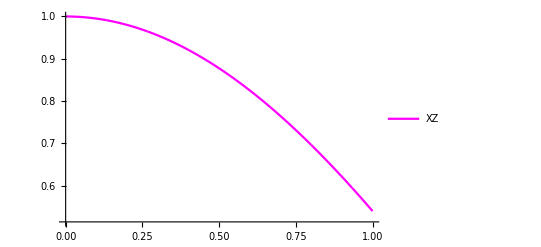

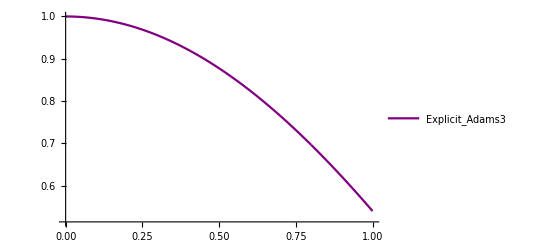

```mathematica
p4=ListLinePlot[{{0,0.99999995500000038451},{0.00010000000000000000479,0.99999992000000104131},{0.00020000000000000000958,0.99999987500000253604},{0.00030000000000000002793,0.99999982000000531279},{0.00040000000000000001917,0.99999975500000992668},{0.00050000000000000001041,0.9999996800000169328},{0.00060000000000000005586,0.99999959500002721935},{0.00070000000000000010131,0.99999950000004156347},{0.00080000000000000014676,0.99999939500006085336},{0.00090000000000000019221,0.99999928000008619922},{0.0010000000000000002377,0.9999991550001188223},{0.0011000000000000002831,0.99999902000015983283},{0.0012000000000000003286,0.9999988750002106741},{0.001300000000000000374,0.9999987200002727894},{0.0014000000000000004195,0.99999855500034773303},{0.0015000000000000004649,0.99999838000043705932},{0.0016000000000000005104,0.99999819500054265564},{0.0017000000000000005558,0.99999800000066629835},{0.0018000000000000006013,0.99999779500080998584},{0.0019000000000000006467,0.99999758000097571653},{0.0020000000000000004753,0.99999735500116559983},{0.0021000000000000003039,0.99999712000138196721},{0.0022000000000000001325,0.99999687500162715015},{0.0022999999999999999611,0.99999662000190359112},{0.0023999999999999997898,0.99999635500221384365},{0.0024999999999999996184,0.99999608000256057228},{0.002599999999999999447,0.99999579500294655254},{0.0026999999999999992756,0.99999550000337456002},{0.0027999999999999991042,0.9999951950038475923},{0.0028999999999999989328,0.99999488000436864699},{0.0029999999999999987614,0.99999455500494094373},{0.00309999999999999859,0.99999422000556770218},{0.0031999999999999984186,0.999993875006252253},{0.0032999999999999982472,0.99999352000699803789},{0.0033999999999999980758,0.99999315500780860955},{0.0034999999999999979045,0.99999278000868774274},{0.0035999999999999977331,0.99999239500963899019},{0.0036999999999999975617,0.99999200001066634869},{0.0037999999999999973903,0.99999159501177370402},{0.0038999999999999972189,0.99999118001296505298},{0.0039999999999999974812,0.99999075501424461443},{0.0040999999999999977435,0.99999032001561671823},{0.0041999999999999980058,0.99998987501708558323},{0.0042999999999999982681,0.99998942001865576135},{0.0043999999999999985303,0.99998895502033169347},{0.0044999999999999987926,0.99998848002211804253},{0.0045999999999999990549,0.99998799502401969352},{0.0046999999999999993172,0.99998750002604130938},{0.0047999999999999995795,0.99998699502818799711},{0.0048999999999999998418,0.99998648003046475274},{0.0050000000000000001041,0.99998595503287668329},{0.0051000000000000003664,0.99998542003542911782},{0.0052000000000000006287,0.99998487503812727439},{0.005300000000000000891,0.99998432004097670411},{0.0054000000000000011532,0.9999837550439829581},{0.0055000000000000014155,0.99998318004715169849},{0.0056000000000000016778,0.99998259505048858742},{0.0057000000000000019401,0.99998200005399962009},{0.0058000000000000022024,0.99998139505769056967},{0.0059000000000000024647,0.99998078006156765341},{0.006000000000000002727,0.9999801550656368665},{0.0061000000000000029893,0.99997952006990453722},{0.0062000000000000032516,0.99997887507437710486},{0.0063000000000000035139,0.9999782200790608977},{0.0064000000000000037761,0.99997755508396246604},{0.0065000000000000040384,0.99997688008908858226},{0.0066000000000000043007,0.99997619509444579666},{0.006700000000000004563,0.99997550010004110366},{0.0068000000000000048253,0.99997479510588138663},{0.0069000000000000050876,0.99997408011197375099},{0.0070000000000000053499,0.99997335511832530219},{0.0071000000000000056122,0.99997262012494336769},{0.0072000000000000058745,0.99997187513183527496},{0.0073000000000000061368,0.99997112013900835148},{0.007400000000000006399,0.99997035514647025778},{0.0075000000000000066613,0.9999695801542286544},{0.0076000000000000069236,0.99996879516229120188},{0.0077000000000000071859,0.99996800017066589383},{0.0078000000000000074482,0.99996719517936050181},{0.0079000000000000077105,0.99996638018838324147},{0.0080000000000000071054,0.99996555519774210641},{0.0081000000000000065004,0.99996472020744542331},{0.0082000000000000058953,0.99996387521750162986},{0.0083000000000000052902,0.99996302022791905273},{0.0084000000000000046851,0.99996215523870624065},{0.0085000000000000040801,0.99996128024987196437},{0.008600000000000003475,0.99996039526142488363},{0.0087000000000000028699,0.99995950027337388022},{0.0088000000000000022649,0.99995859528572783592},{0.0089000000000000016598,0.99995768029849585457},{0.0090000000000000010547,0.99995675531168703998},{0.0091000000000000004496,0.99995582032531071803},{0.0091999999999999998446,0.9999548753393762146},{0.0092999999999999992395,0.99995392035389296659},{0.0093999999999999986344,0.9999529553688705219},{0.0094999999999999980294,0.99995198038431853949},{0.0095999999999999974243,0.99995099540024667828},{0.0096999999999999968192,0.99995000041666493029},{0.0097999999999999962141,0.99994899543358317651},{0.0098999999999999956091,0.99994798045101151995},{0.009999999999999995004,0.99994695546896006366},{0.010099999999999994399,0.99994592048743902168},{0.010199999999999993794,0.99994487550645883012},{0.010299999999999993189,0.99994382052602981403},{0.010399999999999992584,0.99994275554616263157},{0.010499999999999991979,0.99994168056686794088},{0.010599999999999991374,0.9999405955881564001},{0.010699999999999990768,0.99993950061003888941},{0.010799999999999990163,0.99993839563252640001},{0.010899999999999989558,0.99993728065562992313},{0.010999999999999988953,0.99993615567936078303},{0.011099999999999988348,0.99993502070372997093},{0.011199999999999987743,0.99993387572874903313},{0.011299999999999987138,0.99993272075442929392},{0.011399999999999986533,0.99993155578078241064},{0.011499999999999985928,0.9999303808078199296},{0.011599999999999985323,0.99992919583555361918},{0.011699999999999984718,0.99992800086399546977},{0.011799999999999984113,0.99992679589315724975},{0.011899999999999983508,0.99992558092305106054},{0.011999999999999982903,0.99992435595368911461},{0.012099999999999982297,0.99992312098508362439},{0.012199999999999981692,0.99992187601724691337},{0.012299999999999981087,0.99992062105019141605},{0.012399999999999980482,0.99991935608392978896},{0.012499999999999979877,0.99991808111847457763},{0.012599999999999979272,0.99991679615383854962},{0.012699999999999978667,0.99991550119003458352},{0.012799999999999978062,0.99991419622707555792},{0.012899999999999977457,0.99991288126497468447},{0.012999999999999976852,0.99991155630374495278},{0.013099999999999976247,0.99991022134339968552},{0.013199999999999975642,0.99990887638395220538},{0.013299999999999975037,0.99990752142541594605},{0.013399999999999974432,0.99990615646780445225},{0.013499999999999973826,0.99990478151113137972},{0.013599999999999973221,0.99990339655541060626},{0.013699999999999972616,0.99990200160065578761},{0.013799999999999972011,0.99990059664688102359},{0.013899999999999971406,0.99989918169410030302},{0.013999999999999970801,0.99989775674232772573},{0.014099999999999970196,0.9998963217915776136},{0.014199999999999969591,0.99989487684186428851},{0.014299999999999968986,0.99989342189320218335},{0.014399999999999968381,0.99989195694560595307},{0.014499999999999967776,0.99989048199909003056},{0.014599999999999967171,0.99988899705366940385},{0.014699999999999966566,0.99988750210935872786},{0.014799999999999965961,0.99988599716617310165},{0.014899999999999965355,0.99988448222412751321},{0.01499999999999996475,0.99988295728323706157},{0.015099999999999964145,0.99988142234351706783},{0.01519999999999996354,0.99987987740498285305},{0.015299999999999962935,0.99987832246764984934},{0.01539999999999996233,0.99987675753153371083},{0.015499999999999961725,0.99987518259664998066},{0.01559999999999996112,0.99987359766301442399},{0.015699999999999960515,0.999872002730642917},{0.01579999999999995991,0.99987039779955133589},{0.015899999999999959305,0.9998687828697557789},{0.0159999999999999587,0.99986715794127245527},{0.016099999999999958095,0.99986552301411757426},{0.01619999999999995749,0.99986387808830745616},{0.016299999999999956884,0.99986222316385853226},{0.016399999999999956279,0.99986055824078745591},{0.016499999999999955674,0.99985888331911076943},{0.016599999999999955069,0.99985719839884523719},{0.016699999999999954464,0.99985550348000773457},{0.016799999999999953859,0.999853798562615248},{0.016899999999999953254,0.99985208364668476388},{0.016999999999999952649,0.99985035873223337965},{0.017099999999999952044,0.99984862381927852581},{0.017199999999999951439,0.99984687890783741082},{0.017299999999999950834,0.99984512399792746518},{0.017399999999999950229,0.99984335908956634142},{0.017499999999999949624,0.99984158418277158109},{0.017599999999999949019,0.99983979927756105877},{0.017699999999999948413,0.999838004373952427},{0.017799999999999947808,0.99983619947196389344},{0.017899999999999947203,0.99983438457161333268},{0.017999999999999946598,0.99983255967291895239},{0.018099999999999945993,0.99983072477589896021},{0.018199999999999945388,0.99982887988057167483},{0.018299999999999944783,0.99982702498695563698},{0.018399999999999944178,0.99982516009506938737},{0.018499999999999943573,0.99982328520493146673},{0.018599999999999942968,0.99982140031656074886},{0.018699999999999942363,0.99981950542997599651},{0.018799999999999941758,0.99981760054519619452},{0.018899999999999941153,0.9998156856622404387},{0.018999999999999940548,0.99981376078112782491},{0.019099999999999939942,0.99981182590187767101},{0.019199999999999939337,0.99980988102450918387},{0.019299999999999938732,0.99980792614904190341},{0.019399999999999938127,0.99980596127549536956},{0.019499999999999937522,0.99980398640388923326},{0.019599999999999936917,0.99980200153424325649},{0.019699999999999936312,0.99980000666657731223},{0.019799999999999935707,0.99979800180091127348},{0.019899999999999935102,0.99979598693726523528},{0.019999999999999934497,0.99979396207565929267},{0.020099999999999933892,0.99979192721611376271},{0.020199999999999933287,0.9997898823586489625},{0.020299999999999932682,0.99978782750328543116},{0.020399999999999932077,0.9997857626500435968},{0.020499999999999931471,0.99978368779894410956},{0.020599999999999930866,0.99978160295000773061},{0.020699999999999930261,0.99977950810325544317},{0.020799999999999929656,0.99977740325870800842},{0.020899999999999929051,0.99977528841638652057},{0.020999999999999928446,0.99977316357631218491},{0.021099999999999927841,0.99977102873850620668},{0.021199999999999927236,0.99976888390299001319},{0.021299999999999926631,0.99976672906978492072},{0.021399999999999926026,0.99976456423891257863},{0.021499999999999925421,0.99976238941039463626},{0.021599999999999924816,0.99976020458425274295},{0.021699999999999924211,0.99975800976050888114},{0.021799999999999923606,0.9997558049391849222},{0.021899999999999923,0.99975359012030284855},{0.021999999999999922395,0.99975136530388486467},{0.02209999999999992179,0.99974913048995328602},{0.022199999999999921185,0.99974688567853042809},{0.02229999999999992058,0.99974463086963871739},{0.022399999999999919975,0.99974236606330069144},{0.02249999999999991937,0.99974009125953899879},{0.022599999999999918765,0.99973780645837639902},{0.02269999999999991816,0.99973551165983576272},{0.022799999999999917555,0.99973320686393996048},{0.02289999999999991695,0.99973089207071219597},{0.022999999999999916345,0.9997285672801754508},{0.02309999999999991574,0.99972623249235303966},{0.023199999999999915135,0.99972388770726827723},{0.023299999999999914529,0.99972153292494470023},{0.023399999999999913924,0.99971916814540584539},{0.023499999999999913319,0.99971679336867524945},{0.023599999999999912714,0.9997144085947767822},{0.023699999999999912109,0.99971201382373420241},{0.023799999999999911504,0.9997096090555714909},{0.023899999999999910899,0.9997071942903127395},{0.023999999999999910294,0.99970476952798204007},{0.024099999999999909689,0.99970233476860359545},{0.024199999999999909084,0.99969989001220183056},{0.024299999999999908479,0.9996974352588011703},{0.024399999999999907874,0.9996949705084261506},{0.024499999999999907269,0.99969249576110152944},{0.024599999999999906664,0.99969001101685195376},{0.024699999999999906058,0.99968751627570218155},{0.024799999999999905453,0.99968501153767730383},{0.024899999999999904848,0.99968249680280230063},{0.024999999999999904243,0.99967997207110237401},{0.025099999999999903638,0.99967743734260272603},{0.025199999999999903033,0.99967489261732866979},{0.025299999999999902428,0.9996723378953057404},{0.025399999999999901823,0.99966977317655947299},{0.025499999999999901218,0.99966719846111540271},{0.025599999999999900613,0.99966461374899939774},{0.025699999999999900008,0.99966201904023721525},{0.025799999999999899403,0.99965941433485494549},{0.025899999999999898798,0.99965679963287845666},{0.025999999999999898193,0.99965417493433406104},{0.026099999999999897587,0.99965154023924784887},{0.026199999999999896982,0.99964889554764624346},{0.026299999999999896377,0.99964624085955566812},{0.026399999999999895772,0.9996435761750027682},{0.026499999999999895167,0.99964090149401407803},{0.026599999999999894562,0.99963821681661635399},{0.026699999999999893957,0.99963552214283646347},{0.026799999999999893352,0.99963281747270138489},{0.026899999999999892747,0.99963010280623820769},{0.026999999999999892142,0.9996273781434739103},{0.027099999999999891537,0.99962464348443591522},{0.027199999999999890932,0.99962189882915142292},{0.027299999999999890327,0.99961914417764796692},{0.027399999999999889722,0.99961637952995308076},{0.027499999999999889116,0.999613604886094409},{0.027599999999999888511,0.9996108202460997072},{0.027699999999999887906,0.99960802560999684196},{0.027799999999999887301,0.99960522097781367989},{0.027899999999999886696,0.99960240634957830963},{0.027999999999999886091,0.99959958172531893084},{0.028099999999999885486,0.99959674710506374318},{0.028199999999999884881,0.99959390248884105734},{0.028299999999999884276,0.99959104787667940606},{0.028399999999999883671,0.99958818326860721104},{0.028499999999999883066,0.99958530866465322706},{0.028599999999999882461,0.9995824240648462089},{0.028699999999999881856,0.99957952946921491133},{0.028799999999999881251,0.9995766248777884222},{0.028899999999999880645,0.9995737102905956073},{0.02899999999999988004,0.99957078570766577652},{0.029099999999999879435,0.99956785112902801771},{0.02919999999999987883,0.99956490655471175177},{0.029299999999999878225,0.99956195198474639962},{0.02939999999999987762,0.99955898741916160422},{0.029499999999999877015,0.99955601285798689748},{0.02959999999999987641,0.99955302830125214442},{0.029699999999999875805,0.999550033748987099},{0.0297999999999998752,0.99954702920122173726},{0.029899999999999874595,0.99954401465798603521},{0.02999999999999987399,0.99954099011931019092},{0.030099999999999873385,0.99953795558522440245},{0.03019999999999987278,0.99953491105575908993},{0.030299999999999872174,0.99953185653094467344},{0.030399999999999871569,0.99952879201081179517},{0.030499999999999870964,0.99952571749539098622},{0.030599999999999870359,0.99952263298471299979},{0.030699999999999869754,0.99951953847880870008},{0.030799999999999869149,0.99951643397770895128},{0.030899999999999868544,0.99951331948144495065},{0.030999999999999867939,0.99951019499004767344},{0.031099999999999867334,0.99950706050354853893},{0.031199999999999866729,0.99950391602197874441},{0.031299999999999869593,0.9995007615453698202},{0.031399999999999872458,0.99949759707375329665},{0.031499999999999875322,0.9994944226071608151},{0.031599999999999878186,0.99949123814562412793},{0.031699999999999881051,0.99948804368917498753},{0.031799999999999883915,0.99948483923784547933},{0.031899999999999886779,0.99948162479166757777},{0.031999999999999889644,0.9994784003506734793},{0.032099999999999892508,0.9994751659148953804},{0.032199999999999895373,0.99947192148436558856},{0.032299999999999898237,0.99946866705911663331},{0.032399999999999901101,0.99946540263918093316},{0.032499999999999903966,0.9994621282245912397},{0.03259999999999990683,0.9994588438153803045},{0.032699999999999909694,0.99945554941158099016},{0.032799999999999912559,0.99945224501322615929},{0.032899999999999915423,0.99944893062034889653},{0.032999999999999918288,0.99944560623298228652},{0.033099999999999921152,0.99944227185115963596},{0.033199999999999924016,0.99943892747491425155},{0.033299999999999926881,0.999435573104279662},{0.033399999999999929745,0.99943220873928928505},{0.033499999999999932609,0.99942883437997687146},{0.033599999999999935474,0.999425450026376061},{0.033699999999999938338,0.99942205567852082648},{0.033799999999999941203,0.99941865133644502972},{0.033899999999999944067,0.99941523700018275456},{0.033999999999999946931,0.99941181266976808484},{0.034099999999999949796,0.99940837834523532646},{0.03419999999999995266,0.9994049340266187853},{0.034299999999999955524,0.99940147971395287829},{0.034399999999999958389,0.99939801540727213336},{0.034499999999999961253,0.99939454110661130048},{0.034599999999999964118,0.99939105681200501863},{0.034699999999999966982,0.99938756252348825981},{0.034799999999999969846,0.99938405824109588504},{0.034899999999999972711,0.99938054396486286635},{0.034999999999999975575,0.99937701969482439779},{0.035099999999999978439,0.99937348543101578446},{0.035199999999999981304,0.99936994117347233146},{0.035299999999999984168,0.9993663869222294549},{0.035399999999999987033,0.99936282267732279294},{0.035499999999999989897,0.99935924843878787271},{0.035599999999999992761,0.9993556642066604434},{0.035699999999999995626,0.99935206998097636522},{0.03579999999999999849,0.99934846576177160937},{0.035900000000000001354,0.99934485154908225812},{0.036000000000000004219,0.99934122734294439372},{0.036100000000000007083,0.99933759314339420943},{0.036200000000000009948,0.99933394895046812056},{0.036300000000000012812,0.99933029476420254245},{0.036400000000000015676,0.99932663058463400141},{0.036500000000000018541,0.99932295641179924583},{0.036600000000000021405,0.99931927224573491308},{0.036700000000000024269,0.99931557808647786256},{0.036800000000000027134,0.99931187393406495367},{0.036900000000000029998,0.99930815978853337889},{0.037000000000000032863,0.99930443564992021965},{0.037100000000000035727,0.99930070151826266844},{0.037200000000000038591,0.99929695739359813977},{0.037300000000000041456,0.99929320327596404816},{0.03740000000000004432,0.99928943916539791914},{0.037500000000000047184,0.9992856650619375003},{0.037600000000000050049,0.99928188096562031717},{0.037700000000000052913,0.99927808687648445041},{0.037800000000000055778,0.99927428279456764759},{0.037900000000000058642,0.9992704687199081004},{0.038000000000000061506,0.99926664465254377845},{0.038100000000000064371,0.99926281059251309546},{0.038200000000000067235,0.99925896653985424312},{0.038300000000000070099,0.99925511249460574614},{0.038400000000000072964,0.99925124845680612928},{0.038500000000000075828,0.9992473744264940283},{0.038600000000000078693,0.99924349040370818997},{0.038700000000000081557,0.99923959638848747211},{0.038800000000000084421,0.99923569238087084354},{0.038900000000000087286,0.9992317783808972731},{0.03900000000000009015,0.99922785438860595164},{0.039100000000000093014,0.99922392040403607005},{0.039200000000000095879,0.99921997642722704125},{0.039300000000000098743,0.99921602245821816712},{0.039400000000000101608,0.99921205849704908264},{0.039500000000000104472,0.99920808454375942276},{0.039600000000000107336,0.99920410059838893346},{0.039700000000000110201,0.99920010666097747176},{0.039800000000000113065,0.99919610273156500568},{0.039900000000000115929,0.99919208881019150326},{0.040000000000000118794,0.99918806489689704353},{0.040100000000000121658,0.99918403099172203863},{0.040200000000000124523,0.99917998709470667862},{0.040300000000000127387,0.99917593320589148664},{0.040400000000000130251,0.99917186932531687482},{0.040500000000000133116,0.99916779545302358834},{0.04060000000000013598,0.99916371158905237237},{0.040700000000000138844,0.99915961773344408314},{0.040800000000000141709,0.99915551388623957685},{0.040900000000000144573,0.99915140004748004277},{0.041000000000000147438,0.99914727621720644812},{0.041100000000000150302,0.99914314239546009322},{0.041200000000000153166,0.99913899858228238937},{0.041300000000000156031,0.99913484477771463688},{0.041400000000000158895,0.9991306809817984691},{0.041500000000000161759,0.9991265071945755194},{0.041600000000000164624,0.99912232341608753217},{0.041700000000000167488,0.99911812964637625178},{0.041800000000000170353,0.99911392588548364468},{0.041900000000000173217,0.99910971213345178832},{0.042000000000000176081,0.99910548839032287116},{0.042100000000000178946,0.99910125465613908169},{0.04220000000000018181,0.9990970109309427194},{0.042300000000000184674,0.99909275721477630583},{0.042400000000000187539,0.99908849350768236253},{0.042500000000000190403,0.99908421980970341103},{0.042600000000000193268,0.99907993612088230595},{0.042700000000000196132,0.99907564244126190189},{0.042800000000000198996,0.99907133877088505347},{0.042900000000000201861,0.99906702510979483733},{0.043000000000000204725,0.99906270145803433014},{0.04310000000000020759,0.99905836781564683058},{0.043200000000000210454,0.99905402418267563736},{0.043300000000000213318,0.99904967055916427121},{0.043400000000000216183,0.99904530694515614186},{0.043500000000000219047,0.9990409333406949921},{0.043600000000000221911,0.99903654974582445369},{0.043700000000000224776,0.99903215616058849147},{0.04380000000000022764,0.99902775258503095923},{0.043900000000000230505,0.99902333901919593284},{0.044000000000000233369,0.99901891546312748815},{0.044100000000000236233,0.99901448191686992306},{0.044200000000000239098,0.99901003838046753547},{0.044300000000000241962,0.99900558485396473429},{0.044400000000000244826,0.9990011213374061505},{0.044500000000000247691,0.99899664783083630404},{0.044600000000000250555,0.99899216433430004791},{0.04470000000000025342,0.99898767084784212411},{0.044800000000000256284,0.99898316737150749667},{0.044900000000000259148,0.99897865390534124064},{0.045000000000000262013,0.99897413044938843107},{0.045100000000000264877,0.99896959700369425406},{0.045200000000000267741,0.99896505356830422873},{0.045300000000000270606,0.99896050014326365218},{0.04540000000000027347,0.99895593672861804357},{0.045500000000000276335,0.99895136332441303306},{0.045600000000000279199,0.99894677993069447286},{0.045700000000000282063,0.99894218654750810416},{0.045800000000000284928,0.99893758317489989018},{0.045900000000000287792,0.99893296981291579417},{0.046000000000000290656,0.9989283464616020014},{0.046100000000000293521,0.99892371312100480818},{0.046200000000000296385,0.9989190697911705108},{0.04630000000000029925,0.99891441647214551658},{0.046400000000000302114,0.99890975316397634387},{0.046500000000000304978,0.99890507986670962204},{0.046600000000000307843,0.99890039658039220249},{0.046700000000000310707,0.99889570330507071461},{0.046800000000000313571,0.99889100004079223183},{0.046900000000000316436,0.99888628678760382762},{0.0470000000000003193,0.99888156354555246441},{0.047100000000000322165,0.99887683031468554873},{0.047200000000000325029,0.99887208709505026505},{0.047300000000000327893,0.99886733388669413092},{0.047400000000000330758,0.99886257068966466388},{0.047500000000000333622,0.99885779750400960353},{0.047600000000000336486,0.99885301432977646741},{0.047700000000000339351,0.99884822116701332817},{0.047800000000000342215,0.99884341801576792541},{0.04790000000000034508,0.99883860487608833179},{0.048000000000000347944,0.99883378174802261995},{0.048100000000000350808,0.99882894863161919563},{0.048200000000000353673,0.9988241055269262425},{0.048300000000000356537,0.99881925243399227732},{0.048400000000000359401,0.99881438935286581682},{0.048500000000000362266,0.99880951628359548877},{0.04860000000000036513,0.99880463322622992095},{0.048700000000000367995,0.99879974018081807419},{0.048800000000000370859,0.99879483714740879829},{0.048900000000000373723,0.99878992412605116513},{0.049000000000000376588,0.99878500111679435758},{0.049100000000000379452,0.99878006811968755851},{0.049200000000000382316,0.99877512513478006184},{0.049300000000000385181,0.99877017216212127249},{0.049400000000000388045,0.99876520920176081741},{0.04950000000000039091,0.99876023625374821258},{0.049600000000000393774,0.99875525331813330698},{0.049700000000000396638,0.99875026039496583863},{0.049800000000000399503,0.99874525748429576755},{0.049900000000000402367,0.9987402445861731648},{0.050000000000000405231,0.99873522170064810144},{0.050100000000000408096,0.99873018882777087057},{0.05020000000000041096,0.99872514596759176531},{0.050300000000000413825,0.99872009312016118976},{0.050400000000000416689,0.99871503028552965908},{0.050500000000000419553,0.99870995746374791047},{0.050600000000000422418,0.99870487465486657008},{0.050700000000000425282,0.99869978185893648615},{0.050800000000000428146,0.99869467907600861789},{0.050900000000000431011,0.99868956630613392456},{0.051000000000000433875,0.99868444354936358742},{0.05110000000000043674,0.99867931080574878777},{0.051200000000000439604,0.99867416807534092893},{0.051300000000000442468,0.99866901535819141422},{0.051400000000000445333,0.99866385265435164698},{0.051500000000000448197,0.99865867996387347461},{0.051600000000000451061,0.99865349728680841146},{0.051700000000000453926,0.99864830462320841598},{0.05180000000000045679,0.99864310197312544659},{0.051900000000000459655,0.99863788933661146174},{0.052000000000000462519,0.99863266671371853089},{0.052100000000000465383,0.99862743410449894554},{0.052200000000000468248,0.9986221915090049972},{0.052300000000000471112,0.99861693892728919941},{0.052400000000000473976,0.99861167635940406573},{0.052500000000000476841,0.9986064038054021097},{0.052600000000000479705,0.99860112126533617793},{0.05270000000000048257,0.99859582873925900603},{0.052800000000000485434,0.99859052622722355164},{0.052900000000000488298,0.9985852137292828834},{0.053000000000000491163,0.99857989124549006998},{0.053100000000000494027,0.99857455877589829107},{0.053200000000000496891,0.9985692163205609484},{0.053300000000000499756,0.99856386387953144368},{0.05340000000000050262,0.99855850145286340069},{0.053500000000000505485,0.99855312904061022117},{0.053600000000000508349,0.99854774664282586194},{0.053700000000000511213,0.99854235425956394678},{0.053800000000000514078,0.99853695189087854356},{0.053900000000000516942,0.9985315395368236091},{0.054000000000000519806,0.99852611719745332231},{0.054100000000000522671,0.99852068487282186204},{0.054200000000000525535,0.99851524256298362925},{0.0543000000000005284,0.99850979026799291383},{0.054400000000000531264,0.99850432798790433875},{0.054500000000000534128,0.99849885572277252699},{0.054600000000000536993,0.99849337347265210152},{0.054700000000000539857,0.99848788123759801838},{0.054800000000000542721,0.99848237901766501157},{0.054900000000000545586,0.99847686681290825916},{0.05500000000000054845,0.99847134462338282823},{0.055100000000000551315,0.99846581244914400788},{0.055200000000000554179,0.99846027029024708721},{0.055300000000000557043,0.99845471814674746636},{0.055400000000000559908,0.99844915601870065647},{0.055500000000000562772,0.99844358390616227972},{0.055600000000000565636,0.9984380018091880693},{0.055700000000000568501,0.99843240972783386944},{0.055800000000000571365,0.99842680766215563537},{0.05590000000000057423,0.99842119561220932233},{0.056000000000000577094,0.99841557357805099659},{0.056100000000000579958,0.99840994155973694646},{0.056200000000000582823,0.99840429955732357126},{0.056300000000000585687,0.9983986475708671593},{0.056400000000000588551,0.99839298560042422093},{0.056500000000000591416,0.99838731364605148855},{0.05660000000000059428,0.99838163170780558353},{0.056700000000000597145,0.9983759397857433493},{0.056800000000000600009,0.99837023787992174029},{0.056900000000000602873,0.99836452599039782196},{0.057000000000000605738,0.99835880411722865979},{0.057100000000000608602,0.99835307226047143025},{0.057200000000000611466,0.99834733042018353188},{0.057300000000000614331,0.99834157859642225219},{0.057400000000000617195,0.99833581678924521174},{0.05750000000000062006,0.99833004499871003112},{0.057600000000000622924,0.99832426322487444192},{0.057700000000000625788,0.99831847146779617574},{0.057800000000000628653,0.99831266972753318623},{0.057900000000000631517,0.99830685800414353803},{0.058000000000000634381,0.99830103629768540685},{0.058100000000000637246,0.99829520460821685734},{0.05820000000000064011,0.99828936293579628725},{0.058300000000000642975,0.99828351128048209429},{0.058400000000000645839,0.99827764964233278722},{0.058500000000000648703,0.99827177802140698581},{0.058600000000000651568,0.99826589641776342088},{0.058700000000000654432,0.9982600048314608232},{0.058800000000000657296,0.99825410326255825666},{0.058900000000000660161,0.99824819171111467409},{0.059000000000000663025,0.99824227017718913935},{0.05910000000000066589,0.99823633866084093835},{0.059200000000000668754,0.99823039716212935701},{0.059300000000000671618,0.99822444568111379226},{0.059400000000000674483,0.99821848421785375205},{0.059500000000000677347,0.99821251277240896638},{0.059600000000000680211,0.9982065313448389432},{0.059700000000000683076,0.99820053993520374558},{0.05980000000000068594,0.99819453854356310352},{0.059900000000000688805,0.99818852716997708008},{0.060000000000000691669,0.99818250581450573833},{0.060100000000000694533,0.9981764744772094744},{0.060200000000000697398,0.99817043315814835136},{0.060300000000000700262,0.99816438185738298738},{0.060400000000000703126,0.9981583205749737786},{0.060500000000000705991,0.9981522493109813432},{0.060600000000000708855,0.99814616806546652139},{0.06070000000000071172,0.99814007683848993135},{0.060800000000000714584,0.99813397563011263536},{0.060900000000000717448,0.99812786444039558464},{0.061000000000000720313,0.99812174326939984148},{0.061100000000000723177,0.99811561211718669018},{0.061200000000000726041,0.99810947098381741505},{0.061300000000000728906,0.99810331986935352244},{0.06140000000000073177,0.9980971587738564077},{0.061500000000000734635,0.99809098769738768819},{0.061600000000000737499,0.99808480664000909233},{0.061700000000000740363,0.99807861560178245952},{0.061800000000000743228,0.9980724145827696292},{0.061900000000000746092,0.99806620358303277385},{0.062000000000000748956,0.99805998260263384392},{0.062100000000000751821,0.99805375164163512292},{0.062200000000000754685,0.99804751070009878333},{0.06230000000000075755,0.99804125977808744175},{0.062400000000000760414,0.99803499887566349269},{0.062500000000000763278,0.99802872799288955274},{0.062600000000000766143,0.99802244712982834951},{0.062700000000000769007,0.99801615628654261059},{0.062800000000000771871,0.99800985546309539664},{0.062900000000000774736,0.9980035446595495463},{0.0630000000000007776,0.99799722387596834228},{0.063100000000000780465,0.99799089311241484523},{0.063200000000000783329,0.99798455236895244891},{0.063300000000000786193,0.99797820164564454704},{0.063400000000000789058,0.99797184094255464437},{0.063500000000000791922,0.9979654702597463567},{0.063600000000000794786,0.99795908959728341081},{0.063700000000000797651,0.99795269895522953352},{0.063800000000000800515,0.99794629833364867366},{0.06390000000000080338,0.99793988773260478009},{0.064000000000000806244,0.99793346715216213472},{0.064100000000000809108,0.99792703659238479741},{0.064200000000000811973,0.99792059605333705008},{0.064300000000000814837,0.99791414553508339669},{0.064400000000000817701,0.99790768503768823017},{0.064500000000000820566,0.99790121456121627652},{0.06460000000000082343,0.99789473410573215073},{0.064700000000000826295,0.99788824367130068982},{0.064800000000000829159,0.99788174325798684183},{0.064900000000000832023,0.99787523286585555482},{0.065000000000000834888,0.99786871249497188785},{0.065100000000000837752,0.99786218214540112204},{0.065200000000000840616,0.99785564181720853849},{0.065300000000000843481,0.99784909151045964038},{0.065400000000000846345,0.99784253122521981982},{0.06550000000000084921,0.99783596096155469102},{0.065600000000000852074,0.99782938071952997916},{0.065700000000000854938,0.99782279049921140945},{0.065800000000000857803,0.99781619030066492915},{0.065900000000000860667,0.99780958012395659651},{0.066000000000000863531,0.99780295996915246981},{0.066100000000000866396,0.99779632983631871834},{0.06620000000000086926,0.99778968972552173344},{0.066300000000000872125,0.99778303963682779543},{0.066400000000000874989,0.99777637957030351767},{0.066500000000000877853,0.99776970952601540255},{0.066600000000000880718,0.99776302950403028547},{0.066700000000000883582,0.99775633950441477982},{0.066800000000000886446,0.99774963952723594307},{0.066900000000000889311,0.99774292957256072167},{0.067000000000000892175,0.9977362096404561731},{0.06710000000000089504,0.99772947973098957686},{0.067200000000000897904,0.99772273984422821247},{0.067300000000000900768,0.99771598998023935945},{0.067400000000000903633,0.99770923013909063037},{0.067500000000000906497,0.99770246032084963783},{0.067600000000000909361,0.99769568052558410542},{0.067700000000000912226,0.99768889075336175676},{0.06780000000000091509,0.99768209100425042646},{0.067900000000000917955,0.99767528127831828222},{0.068000000000000920819,0.99766846157563326969},{0.068100000000000923683,0.99766163189626366758},{0.068200000000000926548,0.99765479224027775462},{0.068300000000000929412,0.99764794260774392054},{0.068400000000000932276,0.9976410829987306661},{0.068500000000000935141,0.99763421341330660308},{0.068600000000000938005,0.99762733385154045429},{0.06870000000000094087,0.99762044431350094253},{0.068800000000000943734,0.99761354479925701266},{0.068900000000000946598,0.99760663530887760952},{0.069000000000000949463,0.99759971584243190001},{0.069100000000000952327,0.99759278639998905103},{0.069200000000000955191,0.99758584698161834048},{0.069300000000000958056,0.99757889758738915731},{0.06940000000000096092,0.99757193821737100148},{0.069500000000000963785,0.99756496887163348397},{0.069600000000000966649,0.99755798955024621577},{0.069700000000000969513,0.99755100025327914093},{0.069800000000000972378,0.99754400098080198145},{0.069900000000000975242,0.99753699173288490343},{0.070000000000000978106,0.99752997250959785092},{0.070100000000000980971,0.99752294331101110103},{0.070200000000000983835,0.99751590413719493089},{0.0703000000000009867,0.99750885498821972863},{0.070400000000000989564,0.99750179586415599342},{0.070500000000000992428,0.99749472676507433544},{0.070600000000000995293,0.9974876476910454759},{0.070700000000000998157,0.99748055864214002497},{0.070800000000001001021,0.99747345961842903694},{0.070900000000001003886,0.99746635061998345506},{0.07100000000000100675,0.99745923164687444462},{0.071100000000001009615,0.9974521026991730599},{0.071200000000001012479,0.99744496377695068823},{0.071300000000001015343,0.99743781488027871696},{0.071400000000001018208,0.99743065600922853342},{0.071500000000001021072,0.99742348716387185803},{0.071600000000001023936,0.99741630834428030017},{0.071700000000001026801,0.99740911955052569127},{0.071800000000001029665,0.99740192078267986275},{0.07190000000000103253,0.9973947120408148681},{0.072000000000001035394,0.99738749332500276079},{0.072100000000001038258,0.99738026463531570531},{0.072200000000001041123,0.99737302597182597719},{0.072300000000001043987,0.99736577733460607398},{0.072400000000001046851,0.9973585187237282712},{0.072500000000001049716,0.9973512501392653995},{0.07260000000000105258,0.99734397158128995642},{0.072700000000001055445,0.99733668304987488362},{0.072800000000001058309,0.99732938454509290072},{0.072900000000001061173,0.9973220760670171714},{0.073000000000001064038,0.99731475761572063732},{0.073100000000001066902,0.9973074291912765732},{0.073200000000001069766,0.99730009079375825376},{0.073300000000001072631,0.99729274242323895372},{0.073400000000001075495,0.99728538407979228086},{0.07350000000000107836,0.99727801576349173196},{0.073600000000001081224,0.99727063747441102581},{0.073700000000001084088,0.99726324921262399226},{0.073800000000001086953,0.99725585097820446112},{0.073900000000001089817,0.99724844277122648428},{0.074000000000001092682,0.99724102459176400259},{0.074100000000001095546,0.99723359643989128998},{0.07420000000000109841,0.99722615831568262035},{0.074300000000001101275,0.99721871021921237865},{0.074400000000001104139,0.99721125215055506086},{0.074500000000001107003,0.99720378410978527395},{0.074600000000001109868,0.99719630609697762491},{0.074700000000001112732,0.99718881811220694278},{0.074800000000001115597,0.99718132015554805658},{0.074900000000001118461,0.9971738122270760174},{0.075000000000001121325,0.99716629432686587631},{0.07510000000000112419,0.9971587664549927954},{0.075200000000001127054,0.99715122861153204781},{0.075300000000001129918,0.99714368079655901767},{0.075400000000001132783,0.99713612301014920014},{0.075500000000001135647,0.9971285552523780904},{0.075600000000001138512,0.99712097752332151668},{0.075700000000001141376,0.99711338982305508516},{0.07580000000000114424,0.99710579215165484612},{0.075900000000001147105,0.9970981845091966278},{0.076000000000001149969,0.99709056689575659149},{0.076100000000001152833,0.9970829393114108985},{0.076200000000001155698,0.99707530175623582114},{0.076300000000001158562,0.99706765423030774276},{0.076400000000001161427,0.99705999673370315772},{0.076500000000001164291,0.9970523292664985604},{0.076600000000001167155,0.9970446518287706672},{0.07670000000000117002,0.99703696442059630556},{0.076800000000001172884,0.99702926704205230291},{0.076900000000001175748,0.9970215596932155977},{0.077000000000001178613,0.99701384237416335043},{0.077100000000001181477,0.99700611508497272162},{0.077200000000001184342,0.99699837782572087175},{0.077300000000001187206,0.99699063059648529439},{0.07740000000000119007,0.99698287339734337209},{0.077500000000001192935,0.99697510622837282046},{0.077600000000001195799,0.99696732908965113307},{0.077700000000001198663,0.99695954198125624757},{0.077800000000001201528,0.99695174490326587957},{0.077900000000001204392,0.99694393785575807776},{0.078000000000001207257,0.99693612083881089081},{0.078100000000001210121,0.99692829385250258944},{0.078200000000001212985,0.99692045689691133337},{0.07830000000000121585,0.99691260997211550432},{0.078400000000001218714,0.99690475307819359507},{0.078500000000001221578,0.99689688621522409839},{0.078600000000001224443,0.99688900938328572909},{0.078700000000001227307,0.99688112258245731301},{0.078800000000001230172,0.99687322581281767597},{0.078900000000001233036,0.99686531907444586587},{0.0790000000000012359,0.99685740236742081954},{0.079100000000001238765,0.99684947569182169591},{0.079200000000001241629,0.99684153904772787591},{0.079300000000001244493,0.99683359243521862947},{0.079400000000001247358,0.99682563585437355957},{0.079500000000001250222,0.99681766930527204718},{0.079600000000001253087,0.99680969278799391731},{0.079700000000001255951,0.99680170630261888398},{0.079800000000001258815,0.99679370984922677223},{0.07990000000000126168,0.99678570342789751813},{0.080000000000001264544,0.99677768703871127975},{0.080100000000001267408,0.99676966068174821523},{0.080200000000001270273,0.99676162435708848264},{0.080300000000001273137,0.99675357806481257317},{0.080400000000001276002,0.99674552180500086696},{0.080500000000001278866,0.99673745557773396619},{0.08060000000000128173,0.99672937938309247308},{0.080700000000001284595,0.99672129322115721184},{0.080800000000001287459,0.99671319709200900672},{0.080900000000001290323,0.99670509099572890399},{0.081000000000001293188,0.99669697493239783892},{0.081100000000001296052,0.99668884890209707983},{0.081200000000001298917,0.99668071290490778402},{0.081300000000001301781,0.99667256694091144187},{0.081400000000001304645,0.99666441101018943272},{0.08150000000000130751,0.99665624511282324693},{0.081600000000001310374,0.99664806924889470796},{0.081700000000001313238,0.99663988341848541719},{0.081800000000001316103,0.99663168762167730907},{0.081900000000001318967,0.99662348185855231808},{0.082000000000001321832,0.99661526612919248969},{0.082100000000001324696,0.99660704043368009142},{0.08220000000000132756,0.99659880477209727978},{0.082300000000001330425,0.99659055914452643332},{0.082400000000001333289,0.99658230355104993059},{0.082500000000001336153,0.9965740379917504832},{0.082600000000001339018,0.99656576246671058072},{0.082700000000001341882,0.99655747697601315682},{0.082800000000001344747,0.99654918151974092311},{0.082900000000001347611,0.99654087609797692426},{0.083000000000001350475,0.99653256071080409395},{0.08310000000000135334,0.9965242353583056989},{0.083200000000001356204,0.99651590004056500582},{0.083300000000001359068,0.99650755475766528146},{0.083400000000001361933,0.99649919950969001459},{0.083500000000001364797,0.99649083429672280499},{0.083600000000001367662,0.99648245911884725245},{0.083700000000001370526,0.99647407397614706781},{0.08380000000000137339,0.99646567886870618391},{0.083900000000001376255,0.99645727379660853362},{0.084000000000001379119,0.99644885875993816082},{0.084100000000001381983,0.99644043375877922042},{0.084200000000001384848,0.99643199879321586732},{0.084300000000001387712,0.99642355386333258949},{0.084400000000001390577,0.99641509896921376388},{0.084500000000001393441,0.99640663411094398949},{0.084600000000001396305,0.99639815928860786531},{0.08470000000000139917,0.99638967450229010137},{0.084800000000001402034,0.99638117975207562971},{0.084900000000001404898,0.9963726750380493824},{0.085000000000001407763,0.99636416036029640253},{0.085100000000001410627,0.9963556357189018442},{0.085200000000001413492,0.99634710111395086152},{0.085300000000001416356,0.99633855654552894165},{0.08540000000000141922,0.99633000201372146076},{0.085500000000001422085,0.99632143751861390601},{0.085600000000001424949,0.99631286306029198663},{0.085700000000001427813,0.99630427863884152284},{0.085800000000001430678,0.99629568425434822387},{0.085900000000001433542,0.99628707990689813201},{0.086000000000001436407,0.99627846559657717851},{0.086100000000001439271,0.9962698413234716277},{0.086200000000001442135,0.9962612070876676329},{0.086300000000001445,0.99625256288925168047},{0.086400000000001447864,0.99624390872831003474},{0.086500000000001450728,0.99623524460492929311},{0.086600000000001453593,0.996226570519196164},{0.086700000000001456457,0.99621788647119735582},{0.086800000000001459322,0.99620919246101968803},{0.086900000000001462186,0.99620048848875009107},{0.08700000000000146505,0.99619177455447560643},{0.087100000000001467915,0.99618305065828338662},{0.087200000000001470779,0.99617431680026058416},{0.087300000000001473643,0.99616557298049468461},{0.087400000000001476508,0.99615681919907306252},{0.087500000000001479372,0.99614805545608320347},{0.087600000000001482237,0.99613928175161281509},{0.087700000000001485101,0.99613049808574960498},{0.087800000000001487965,0.99612170445858150281},{0.08790000000000149083,0.99611290087019632722},{0.088000000000001493694,0.9961040873206821189},{0.088100000000001496558,0.99609526381012714058},{0.088200000000001499423,0.99608643033861954397},{0.088300000000001502287,0.99607758690624759179},{0.088400000000001505152,0.99606873351309976883},{0.088500000000001508016,0.99605987015926467087},{0.08860000000000151088,0.99605099684483078271},{0.088700000000001513745,0.99604211356988703319},{0.088800000000001516609,0.99603322033452212914},{0.088900000000001519473,0.99602431713882499942},{0.089000000000001522338,0.99601540398288468392},{0.089100000000001525202,0.99600648086679033355},{0.089200000000001528067,0.99599754779063121024},{0.089300000000001530931,0.99598860475449657592},{0.089400000000001533795,0.99597965175847591457},{0.08950000000000153666,0.99597068880265882118},{0.089600000000001539524,0.99596171588713477973},{0.089700000000001542388,0.99595273301199360727},{0.089800000000001545253,0.99594374017732512083},{0.089900000000001548117,0.99593473738321924849},{0.090000000000001550982,0.99592572462976602932},{0.090100000000001553846,0.99591670191705550241},{0.09020000000000155671,0.99590766924517803993},{0.090300000000001559575,0.995898626614223903},{0.090400000000001562439,0.99588957402428346377},{0.090500000000001565303,0.99588051147544731645},{0.090600000000001568168,0.99587143896780605523},{0.090700000000001571032,0.99586235650145038534},{0.090800000000001573897,0.99585326407647123403},{0.090900000000001576761,0.99584416169295941756},{0.091000000000001579625,0.99583504935100597422},{0.09110000000000158249,0.9958259270507020533},{0.091200000000001585354,0.99581679479213880413},{0.091300000000001588218,0.99580765257540770907},{0.091400000000001591083,0.99579850040060002847},{0.091500000000001593947,0.99578933826780735572},{0.091600000000001596812,0.99578016617712128422},{0.091700000000001599676,0.99577098412863362942},{0.09180000000000160254,0.99576179212243609573},{0.091900000000001605405,0.99575259015862072065},{0.092000000000001608269,0.99574337823727943064},{0.092100000000001611133,0.99573415635850437422},{0.092200000000001613998,0.99572492452238769989},{0.092300000000001616862,0.99571568272902177821},{0.092400000000001619727,0.99570643097849909076},{0.092500000000001622591,0.99569716927091211911},{0.092600000000001625455,0.99568789760635345587},{0.09270000000000162832,0.99567861598491580466},{0.092800000000001631184,0.99566932440669198012},{0.092900000000001634048,0.99566002287177490793},{0.093000000000001636913,0.99565071138025762476},{0.093100000000001639777,0.99564138993223327834},{0.093200000000001642642,0.99563205852779501637},{0.093300000000001645506,0.99562271716703620861},{0.09340000000000164837,0.99561336585005022481},{0.093500000000001651235,0.99560400457693054577},{0.093600000000001654099,0.99559463334777087429},{0.093700000000001656963,0.99558525216266480218},{0.093800000000001659828,0.99557586102170625431},{0.093900000000001662692,0.99556645992498915554},{0.094000000000001665557,0.99555704887260743075},{0.094100000000001668421,0.99554762786465522684},{0.094200000000001671285,0.99553819690122680175},{0.09430000000000167415,0.99552875598241630239},{0.094400000000001677014,0.99551930510831831977},{0.094500000000001679878,0.99550984427902733387},{0.094600000000001682743,0.99550037349463782466},{0.094700000000001685607,0.99549089275524460518},{0.094800000000001688472,0.9954814020609424885},{0.094900000000001691336,0.99547190141182639866},{0.0950000000000016942,0.99546239080799125976},{0.095100000000001697065,0.99545287024953221788},{0.095200000000001699929,0.99544333973654453018},{0.095300000000001702793,0.99543379926912345379},{0.095400000000001705658,0.99542424884736435686},{0.095500000000001708522,0.9954146884713628296},{0.095600000000001711387,0.99540511814121435119},{0.095700000000001714251,0.99539553785701473387},{0.095800000000001717115,0.9953859476188597899},{0.09590000000000171998,0.99537634742684533151},{0.096000000000001722844,0.99536673728106739301},{0.096100000000001725708,0.99535711718162211969},{0.096200000000001728573,0.99534748712860565689},{0.096300000000001731437,0.99533784712211437196},{0.096400000000001734302,0.99532819716224463225},{0.096500000000001737166,0.99531853724909291614},{0.09660000000000174003,0.99530886738275581305},{0.096700000000001742895,0.99529918756333002339},{0.096800000000001745759,0.99528949779091235861},{0.096900000000001748623,0.99527979806559974119},{0.097000000000001751488,0.99527008838748920461},{0.097100000000001754352,0.99526036875667767134},{0.097200000000001757217,0.99525063917326250795},{0.097300000000001760081,0.99524089963734096997},{0.097400000000001762945,0.99523115014901042397},{0.09750000000000176581,0.99522139070836845853},{0.097600000000001768674,0.99521162131551255126},{0.097700000000001771538,0.99520184197054040176},{0.097800000000001774403,0.99519205267354993172},{0.097900000000001777267,0.99518225342463884076},{0.098000000000001780132,0.99517244422390527259},{0.098100000000001782996,0.99516262507144725991},{0.09820000000000178586,0.99515279596736305745},{0.098300000000001788725,0.99514295691175091996},{0.098400000000001791589,0.99513310790470910216},{0.098500000000001794453,0.9951232489463363029},{0.098600000000001797318,0.99511338003673099895},{0.098700000000001800182,0.99510350117599188913},{0.098800000000001803047,0.99509361236421778329},{0.098900000000001805911,0.99508371360150760232},{0.099000000000001808775,0.99507380488796026707},{0.09910000000000181164,0.99506388622367492047},{0.099200000000001814504,0.99505395760875070543},{0.099300000000001817368,0.99504401904328687589},{0.099400000000001820233,0.99503407052738290783},{0.099500000000001823097,0.99502411206113816622},{0.099600000000001825962,0.99501414364465234907},{0.099700000000001828826,0.99500416527802515443},{0.09980000000000183169,0.99499417696135628031},{0.099900000000001834555,0.99498417869474564679},{0.10000000000000183742,0.99497417047829328496},{0.10010000000000184028,0.99496415231209922592},{0.10020000000000184315,0.99495412419626361178},{0.10030000000000184601,0.99494408613088680671},{0.10040000000000184888,0.99493403811606906384},{0.10050000000000185174,0.99492398015191096938},{0.10060000000000185461,0.99491391223851310954},{0.10070000000000185747,0.99490383437597607053},{0.10080000000000186033,0.9948937465644007716},{0.1009000000000018632,0.99488364880388802103},{0.10100000000000186606,0.99487354109453873807},{0.10110000000000186893,0.99486342343645406405},{0.10120000000000187179,0.99485329582973514029},{0.10130000000000187466,0.99484315827448333014},{0.10140000000000187752,0.99483301077079988595},{0.10150000000000188038,0.99482285331878639312},{0.10160000000000188325,0.99481268591854432604},{0.10170000000000188611,0.99480250857017549215},{0.10180000000000188898,0.9947923212737815879},{0.10190000000000189184,0.99478212402946442072},{0.10200000000000189471,0.99477191683732602012},{0.10210000000000189757,0.99476169969746841559},{0.10220000000000190044,0.99475147260999385868},{0.1023000000000019033,0.99474123557500460091},{0.10240000000000190616,0.99473098859260300486},{0.10250000000000190903,0.99472073166289154411},{0.10260000000000191189,0.99471046478597269225},{0.10270000000000191476,0.99470018796194925592},{0.10280000000000191762,0.99468990119092393076},{0.10290000000000192049,0.99467960447299963445},{0.10300000000000192335,0.99466929780827928465},{0.10310000000000192621,0.99465898119686591006},{0.10320000000000192908,0.99464865463886276142},{0.10330000000000193194,0.99463831813437308949},{0.10340000000000193481,0.99462797168350025601},{0.10350000000000193767,0.99461761528634773377},{0.10360000000000194054,0.99460724894301910659},{0.1037000000000019434,0.99459687265361795827},{0.10380000000000194627,0.99458648641824809467},{0.10390000000000194913,0.99457609023701332163},{0.10400000000000195199,0.99456568411001766705},{0.10410000000000195486,0.99455526803736515884},{0.10420000000000195772,0.99454484201916004693},{0.10430000000000196059,0.99453440605550647025},{0.10440000000000196345,0.99452396014650890077},{0.10450000000000196632,0.99451350429227169947},{0.10460000000000196918,0.99450303849289944935},{0.10470000000000197204,0.99449256274849684445},{0.10480000000000197491,0.99448207705916857879},{0.10490000000000197777,0.99447158142501956846},{0.10500000000000198064,0.99446107584615472952},{0.1051000000000019835,0.9944505603226792001},{0.10520000000000198637,0.99444003485469811832},{0.10530000000000198923,0.99442949944231662229},{0.1054000000000019921,0.99441895408564018322},{0.10550000000000199496,0.99440839878477416125},{0.10560000000000199782,0.99439783353982424963},{0.10570000000000200069,0.99438725835089591953},{0.10580000000000200355,0.99437667321809508625},{0.10590000000000200642,0.994366078141527443},{0.10600000000000200928,0.99435547312129901609},{0.10610000000000201215,0.99434485815751594284},{0.10620000000000201501,0.99433423325028424955},{0.10630000000000201787,0.99432359839971029558},{0.10640000000000202074,0.99431295360590032928},{0.1065000000000020236,0.99430229886896082103},{0.10660000000000202647,0.99429163418899835225},{0.10670000000000202933,0.99428095956611950434},{0.1068000000000020322,0.99427027500043108077},{0.10690000000000203506,0.99425958049203988498},{0.10700000000000203793,0.99424887604105294248},{0.10710000000000204079,0.99423816164757727876},{0.10720000000000204365,0.99422743731171991932},{0.10730000000000204652,0.99421670303358822274},{0.10740000000000204938,0.99420595881328954757},{0.10750000000000205225,0.99419520465093125239},{0.10760000000000205511,0.9941844405466209178},{0.10770000000000205798,0.99417366650046623544},{0.10780000000000206084,0.99416288251257489694},{0.1079000000000020637,0.99415208858305470496},{0.10800000000000206657,0.9941412847120136842},{0.10810000000000206943,0.99413047089955974833},{0.1082000000000020723,0.99411964714580114411},{0.10830000000000207516,0.99410881345084611826},{0.10840000000000207803,0.99409796981480291755},{0.10850000000000208089,0.99408711623778001076},{0.10860000000000208376,0.9940762527198859777},{0.10870000000000208662,0.99406537926122939819},{0.10880000000000208948,0.99405449586191907407},{0.10890000000000209235,0.99404360252206380721},{0.10900000000000209521,0.99403269924177251049},{0.10910000000000209808,0.9940217860211542078},{0.10920000000000210094,0.99401086286031803407},{0.10930000000000210381,0.99399992975937323525},{0.10940000000000210667,0.9939889867184291683},{0.10950000000000210953,0.99397803373759530121},{0.1096000000000021124,0.99396707081698110198},{0.10970000000000211526,0.99395609795669614961},{0.10980000000000211813,0.99394511515685024516},{0.10990000000000212099,0.9939341224175531897},{0.11000000000000212386,0.99392311973891489529},{0.11010000000000212672,0.99391210712104549607},{0.11020000000000212959,0.99390108456405501514},{0.11030000000000213245,0.99389005206805369763},{0.11040000000000213531,0.99387900963315178871},{0.11050000000000213818,0.99386795725945986657},{0.11060000000000214104,0.9938568949470882874},{0.11070000000000214391,0.99384582269614785144},{0.11080000000000214677,0.99383474050674913691},{0.11090000000000214964,0.9938236483790030551},{0.1110000000000021525,0.99381254631302051727},{0.11110000000000215536,0.99380143430891254575},{0.11120000000000215823,0.99379031236679016281},{0.11130000000000216109,0.99377918048676472385},{0.11140000000000216396,0.99376803866894747319},{0.11150000000000216682,0.99375688691344987724},{0.11160000000000216969,0.99374572522038340239},{0.11170000000000217255,0.99373455358985962604},{0.11180000000000217542,0.99372337202199034767},{0.11190000000000217828,0.99371218051688736672},{0.11200000000000218114,0.99370097907466259368},{0.11210000000000218401,0.99368976769542805005},{0.11220000000000218687,0.99367854637929586836},{0.11230000000000218974,0.99366731512637818113},{0.1124000000000021926,0.99365607393678734294},{0.11250000000000219547,0.99364482281063581937},{0.11260000000000219833,0.99363356174803607601},{0.11270000000000220119,0.99362229074910068949},{0.11280000000000220406,0.99361100981394234744},{0.11290000000000220692,0.99359971894267395953},{0.11300000000000220979,0.99358841813540843546},{0.11310000000000221265,0.9935771073922586849},{0.11320000000000221552,0.99356578671333783959},{0.11330000000000221838,0.99355445609875925328},{0.11340000000000222125,0.99354311554863605771},{0.11350000000000222411,0.99353176506308171767},{0.11360000000000222697,0.99352040464220969795},{0.11370000000000222984,0.9935090342861336854},{0.1138000000000022327,0.99349765399496736684},{0.11390000000000223557,0.99348626376882442912},{0.11400000000000223843,0.99347486360781889214},{0.1141000000000022413,0.99346345351206477581},{0.11420000000000224416,0.99345203348167610002},{0.11430000000000224702,0.99344060351676710674},{0.11440000000000224989,0.9934291636174520379},{0.11450000000000225275,0.99341771378384535751},{0.11460000000000225562,0.99340625401606152955},{0.11470000000000225848,0.99339478431421524007},{0.11480000000000226135,0.99338330467842106408},{0.11490000000000226421,0.99337181510879390967},{0.11500000000000226708,0.99336031560544857388},{0.11510000000000226994,0.99334880616850007584},{0.1152000000000022728,0.99333728679806354567},{0.11530000000000227567,0.99332575749425411349},{0.11540000000000227853,0.99331421825718713148},{0.1155000000000022814,0.99330266908697795181},{0.11560000000000228426,0.99329110998374214869},{0.11570000000000228713,0.99327954094759518533},{0.11580000000000228999,0.99326796197865285798},{0.11590000000000229285,0.9932563730770309629},{0.11600000000000229572,0.99324477424284529636},{0.11610000000000229858,0.99323316547621187667},{0.11620000000000230145,0.99322154677724683314},{0.11630000000000230431,0.99320991814606629511},{0.11640000000000230718,0.99319827958278661395},{0.11650000000000231004,0.99318663108752414104},{0.11660000000000231291,0.99317497266039544979},{0.11670000000000231577,0.99316330430151700259},{0.11680000000000231863,0.9931516260110054839},{0.1169000000000023215,0.99313993778897768916},{0.11700000000000232436,0.99312823963555052487},{0.11710000000000232723,0.99311653155084100852},{0.11720000000000233009,0.99310481353496615764},{0.11730000000000233296,0.99309308558804321176},{0.11740000000000233582,0.99308134771018941045},{0.11750000000000233868,0.99306959990152221529},{0.11760000000000234155,0.99305784216215897686},{0.11770000000000234441,0.99304607449221726778},{0.11780000000000234728,0.99303429689181488271},{0.11790000000000235014,0.9930225093610695053},{0.11800000000000235301,0.99301071190009904122},{0.11810000000000235587,0.99299890450902150718},{0.11820000000000235874,0.9929870871879549199},{0.1183000000000023616,0.9929752599370174071},{0.11840000000000236446,0.99296342275632731855},{0.11850000000000236733,0.99295157564600300404},{0.11860000000000237019,0.99293971860616303537},{0.11870000000000237306,0.99292785163692587336},{0.11880000000000237592,0.99291597473841020083},{0.11890000000000237879,0.99290408791073470063},{0.11900000000000238165,0.99289219115401838867},{0.11910000000000238451,0.99288028446838016983},{0.11920000000000238738,0.99286836785393917104},{0.11930000000000239024,0.99285644131081440822},{0.11940000000000239311,0.99284450483912523033},{0.11950000000000239597,0.99283255843899109738},{0.11960000000000239884,0.99282060211053135834},{0.1197000000000024017,0.99280863585386558423},{0.11980000000000240457,0.99279665966911345709},{0.11990000000000240743,0.99278467355639476999},{0.12000000000000241029,0.99277267751582931599},{0.12010000000000241316,0.99276067154753711019},{0.12020000000000241602,0.99274865565163816772},{0.12030000000000241889,0.99273662982825272572},{0.12040000000000242175,0.99272459407750102134},{0.12050000000000242462,0.99271254839950340276},{0.12060000000000242748,0.99270049279438021816},{0.12070000000000243034,0.99268842726225214879},{0.12080000000000243321,0.99267635180323976485},{0.12090000000000243607,0.99266426641746396964},{0.12100000000000243894,0.9926521711050454444},{0.1211000000000024418,0.99264006586610520344},{0.12120000000000244467,0.99262795070076437209},{0.12130000000000244753,0.99261582560914407569},{0.1214000000000024504,0.99260369059136543957},{0.12150000000000245326,0.99259154564754992212},{0.12160000000000245612,0.99257939077781898174},{0.12170000000000245899,0.99256722598229407684},{0.12180000000000246185,0.99255505126109699887},{0.12190000000000246472,0.99254286661434942829},{0.12200000000000246758,0.99253067204217315656},{0.12210000000000247045,0.99251846754469019718},{0.12220000000000247331,0.99250625312202256367},{0.12230000000000247617,0.99249402877429238057},{0.12240000000000247904,0.99248179450162199444},{0.1225000000000024819,0.99246955030413364085},{0.12260000000000248477,0.99245729618194977739},{0.12270000000000248763,0.99244503213519297269},{0.1228000000000024905,0.99243275816398579536},{0.12290000000000249336,0.99242047426845103608},{0.12300000000000249623,0.99240818044871159653},{0.12310000000000249909,0.99239587670489037841},{0.12320000000000250195,0.99238356303711039441},{0.12330000000000250482,0.99237123944549476828},{0.12340000000000250768,0.99235890593016673478},{0.12350000000000251055,0.99234656249124963967},{0.12360000000000251341,0.99233420912886693976},{0.12370000000000251628,0.99232184584314220288},{0.12380000000000251914,0.99230947263419899684},{0.123900000000002522,0.99229708950216111152},{0.12400000000000252487,0.99228469644715233677},{0.12410000000000252773,0.9922722934692965735},{0.1242000000000025306,0.9922598805687178336},{0.12430000000000253346,0.99224745774554035105},{0.12440000000000253633,0.99223502499988824876},{0.12450000000000253919,0.99222258233188598275},{0.12460000000000254206,0.99221012974165789799},{0.12470000000000254492,0.99219766722932845049},{0.12480000000000254778,0.9921851947950224293},{0.12490000000000255065,0.99217271243886440146},{0.12500000000000255351,0.99216022016097926706},{0.1251000000000025425,0.99214771796149192618},{0.12520000000000253149,0.99213520584052738993},{0.12530000000000252047,0.99212268379821089148},{0.12540000000000250946,0.99211015183466744194},{0.12550000000000249845,0.99209760995002260753},{0.12560000000000248743,0.9920850581444016214},{0.12570000000000247642,0.99207249641793004979},{0.12580000000000246541,0.99205992477073356994},{0.12590000000000245439,0.9920473432029378591},{0.12600000000000244338,0.99203475171466870552},{0.12610000000000243237,0.99202215030605200852},{0.12620000000000242135,0.99200953897721377839},{0.12630000000000241034,0.99199691772828024749},{0.12640000000000239933,0.99198428655937753717},{0.12650000000000238831,0.9919716454706319908},{0.1266000000000023773,0.99195899446216995177},{0.12670000000000236628,0.99194633353411798549},{0.12680000000000235527,0.99193366268660265739},{0.12690000000000234426,0.99192098191975075494},{0.12700000000000233324,0.99190829123368906561},{0.12710000000000232223,0.99189559062854437688},{0.12720000000000231122,0.99188288010444392029},{0.1273000000000023002,0.99187015966151459434},{0.12740000000000228919,0.99185742929988374161},{0.12750000000000227818,0.99184468901967848264},{0.12760000000000226716,0.99183193882102638206},{0.12770000000000225615,0.99181917870405489346},{0.12780000000000224514,0.99180640866889169249},{0.12790000000000223412,0.99179362871566434379},{0.12800000000000222311,0.99178083884450074503},{0.1281000000000022121,0.99176803905552879392},{0.12820000000000220108,0.99175522934887638815},{0.12830000000000219007,0.99174240972467175848},{0.12840000000000217906,0.99172958018304302463},{0.12850000000000216804,0.99171674072411852841},{0.12860000000000215703,0.99170389134802661157},{0.12870000000000214602,0.99169103205489583797},{0.128800000000002135,0.99167816284485466038},{0.12890000000000212399,0.9916652837180318647},{0.12900000000000211298,0.99165239467455623679},{0.12910000000000210196,0.99163949571455678456},{0.12920000000000209095,0.99162658683816229388},{0.12930000000000207994,0.99161366804550199472},{0.12940000000000206892,0.99160073933670500601},{0.12950000000000205791,0.99158780071190066874},{0.1296000000000020469,0.99157485217121832388},{0.12970000000000203588,0.99156189371478742345},{0.12980000000000202487,0.99154892534273764149},{0.12990000000000201386,0.99153594705519854102},{0.13000000000000200284,0.99152295885230001815},{0.13010000000000199183,0.99150996073417185794},{0.13020000000000198082,0.99149695270094417854},{0.1303000000000019698,0.99148393475274698705},{0.13040000000000195879,0.99147090688971040162},{0.13050000000000194778,0.99145786911196476243},{0.13060000000000193676,0.99144482141964040967},{0.13070000000000192575,0.99143176381286790555},{0.13080000000000191474,0.99141869629177770129},{0.13090000000000190372,0.99140561885650058116},{0.13100000000000189271,0.99139253150716732943},{0.13110000000000188169,0.99137943424390873037},{0.13120000000000187068,0.99136632706685579031},{0.13130000000000185967,0.99135320997613962657},{0.13140000000000184865,0.9913400829718913565},{0.13150000000000183764,0.99132694605424220846},{0.13160000000000182663,0.99131379922332363286},{0.13170000000000181561,0.9913006424792670801},{0.1318000000000018046,0.99128747582220411161},{0.13190000000000179359,0.99127429925226639984},{0.13200000000000178257,0.99126111276958572827},{0.13210000000000177156,0.99124791637429388036},{0.13220000000000176055,0.99123471006652297266},{0.13230000000000174953,0.99122149384640489966},{0.13240000000000173852,0.99120826771407188893},{0.13250000000000172751,0.99119503166965627905},{0.13260000000000171649,0.99118178571329029758},{0.13270000000000170548,0.99116852984510650515},{0.13280000000000169447,0.99115526406523746239},{0.13290000000000168345,0.99114198837381572993},{0.13300000000000167244,0.99112870277097409044},{0.13310000000000166143,0.99111540725684543762},{0.13320000000000165041,0.99110210183156277619},{0.1333000000000016394,0.99108878649525899984},{0.13340000000000162839,0.99107546124806744636},{0.13350000000000161737,0.99106212609012123149},{0.13360000000000160636,0.99104878102155380404},{0.13370000000000159535,0.99103542604249861281},{0.13380000000000158433,0.99102206115308910661},{0.13390000000000157332,0.99100868635345906732},{0.13400000000000156231,0.99099530164374216579},{0.13410000000000155129,0.99098190702407218389},{0.13420000000000154028,0.99096850249458323656},{0.13430000000000152927,0.99095508805540921671},{0.13440000000000151825,0.99094166370668435029},{0.13450000000000150724,0.99092822944854286327},{0.13460000000000149623,0.99091478528111909263},{0.13470000000000148521,0.99090133120454748639},{0.1348000000000014742,0.99088786721896249254},{0.13490000000000146319,0.99087439332449889218},{0.13500000000000145217,0.99086090952129135534},{0.13510000000000144116,0.99084741580947477413},{0.13520000000000143014,0.99083391218918392962},{0.13530000000000141913,0.99082039866055404698},{0.13540000000000140812,0.99080687522372012932},{0.1355000000000013971,0.99079334187881751284},{0.13560000000000138609,0.99077979862598153371},{0.13570000000000137508,0.99076624546534752813},{0.13580000000000136406,0.99075268239705105433},{0.13590000000000135305,0.99073910942122778156},{0.13600000000000134204,0.99072552653801337907},{0.13610000000000133102,0.99071193374754373817},{0.13620000000000132001,0.99069833104995486117},{0.136300000000001309,0.99068471844538263937},{0.13640000000000129798,0.99067109593396318612},{0.13650000000000128697,0.9906574635158328368},{0.13660000000000127596,0.99064382119112781577},{0.13670000000000126494,0.99063016895998456945},{0.13680000000000125393,0.99061650682253965527},{0.13690000000000124292,0.99060283477892974169},{0.1370000000000012319,0.99058915282929149715},{0.13710000000000122089,0.99057546097376170113},{0.13720000000000120988,0.99056175921247735516},{0.13730000000000119886,0.99054804754557534974},{0.13740000000000118785,0.99053432597319290842},{0.13750000000000117684,0.99052059449546725478},{0.13760000000000116582,0.99050685311253561238},{0.13770000000000115481,0.99049310182453542684},{0.1378000000000011438,0.99047934063160425477},{0.13790000000000113278,0.99046556953387965283},{0.13800000000000112177,0.99045178853149939968},{0.13810000000000111076,0.990437997624601274},{0.13820000000000109974,0.9904241968133231655},{0.13830000000000108873,0.99041038609780307489},{0.13840000000000107772,0.99039656547817911392},{0.1385000000000010667,0.99038273495458961637},{0.13860000000000105569,0.990368894527172694},{0.13870000000000104468,0.99035504419606690263},{0.13880000000000103366,0.99034118396141057605},{0.13890000000000102265,0.99032731382334249215},{0.13900000000000101164,0.99031343378200120675},{0.13910000000000100062,0.99029954383752560876},{0.13920000000000098961,0.99028564399005458707},{0.13930000000000097859,0.99027173423972714161},{0.13940000000000096758,0.99025781458668238333},{0.13950000000000095657,0.99024388503105953419},{0.13960000000000094555,0.99022994557299781615},{0.13970000000000093454,0.99021599621263667323},{0.13980000000000092353,0.99020203695011554945},{0.13990000000000091251,0.99018806778557399983},{0.1400000000000009015,0.99017408871915180146},{0.14010000000000089049,0.99016009975098873142},{0.14020000000000087947,0.99014610088122467779},{0.14030000000000086846,0.99013209210999963972},{0.14040000000000085745,0.99011807343745372734},{0.14050000000000084643,0.9901040448637270508},{0.14060000000000083542,0.99009000638895994229},{0.14070000000000082441,0.99007595801329273399},{0.14080000000000081339,0.99006189973686598016},{0.14090000000000080238,0.99004783155982023501},{0.14100000000000079137,0.99003375348229616382},{0.14110000000000078035,0.99001966550443454285},{0.14120000000000076934,0.99000556762637637043},{0.14130000000000075833,0.98999145984826242284},{0.14140000000000074731,0.98997734217023403147},{0.1415000000000007363,0.98996321459243208363},{0.14160000000000072529,0.98994907711499813274},{0.14170000000000071427,0.98993492973807328816},{0.14180000000000070326,0.98992077246179921435},{0.14190000000000069225,0.98990660528631746473},{0.14200000000000068123,0.98989242821176959275},{0.14210000000000067022,0.98987824123829748491},{0.14220000000000065921,0.98986404436604291668},{0.14230000000000064819,0.98984983759514799662},{0.14240000000000063718,0.98983562092575461122},{0.14250000000000062617,0.98982139435800509109},{0.14260000000000061515,0.98980715789204165578},{0.14270000000000060414,0.98979291152800663589},{0.14280000000000059313,0.98977865526604247304},{0.14290000000000058211,0.98976438910629183088},{0.1430000000000005711,0.98975011304889726205},{0.14310000000000056009,0.98973582709400154123},{0.14320000000000054907,0.98972153124174766514},{0.14330000000000053806,0.98970722549227840847},{0.14340000000000052705,0.98969290984573687897},{0.14350000000000051603,0.9896785843022662954},{0.14360000000000050502,0.98966424886200987654},{0.143700000000000494,0.98964990352511095217},{0.14380000000000048299,0.98963554829171307414},{0.14390000000000047198,0.98962118316195968326},{0.14400000000000046096,0.98960680813599444239},{0.14410000000000044995,0.98959242321396112541},{0.14420000000000043894,0.98957802839600361722},{0.14430000000000042792,0.98956362368226580273},{0.14440000000000041691,0.98954920907289178889},{0.1445000000000004059,0.98953478456802568264},{0.14460000000000039488,0.98952035016781170196},{0.14470000000000038387,0.98950590587239428686},{0.14480000000000037286,0.98949145168191776634},{0.14490000000000036184,0.98947698759652680245},{0.14500000000000035083,0.98946251361636594623},{0.14510000000000033982,0.98944802974157997077},{0.1452000000000003288,0.98943353597231364915},{0.14530000000000031779,0.9894190323087119765},{0.14540000000000030678,0.98940451875092005896},{0.14550000000000029576,0.98938999529908289166},{0.14560000000000028475,0.98937546195334580279},{0.14570000000000027374,0.98936091871385412055},{0.14580000000000026272,0.98934636558075328416},{0.14590000000000025171,0.98933180255418873283},{0.1460000000000002407,0.98931722963430623885},{0.14610000000000022968,0.98930264682125146347},{0.14620000000000021867,0.98928805411517017898},{0.14630000000000020766,0.98927345151620837971},{0.14640000000000019664,0.98925883902451205998},{0.14650000000000018563,0.98924421664022732514},{0.14660000000000017462,0.9892295843635005026},{0.1467000000000001636,0.98921494219447780871},{0.14680000000000015259,0.98920029013330568191},{0.14690000000000014158,0.98918562818013067162},{0.14700000000000013056,0.98917095633509943831},{0.14710000000000011955,0.98915627459835864244},{0.14720000000000010854,0.98914158297005505549},{0.14730000000000009752,0.989126881450335671},{0.14740000000000008651,0.98911217003934748249},{0.1475000000000000755,0.98909744873723759451},{0.14760000000000006448,0.98908271754415322263},{0.14770000000000005347,0.98906797646024169346},{0.14780000000000004245,0.9890532254856504446},{0.14790000000000003144,0.98903846462052691368},{0.14800000000000002043,0.98902369386501876036},{0.14810000000000000941,0.9890089132192736443},{0.1481999999999999984,0.98899412268343944721},{0.14829999999999998739,0.98897932225766393977},{0.14839999999999997637,0.98896451194209522573},{0.14849999999999996536,0.98894969173688140884},{0.14859999999999995435,0.98893486164217070389},{0.14869999999999994333,0.98892002165811143666},{0.14879999999999993232,0.98890517178485193295},{0.14889999999999992131,0.9888903120225407406},{0.14899999999999991029,0.98887544237132640745},{0.14909999999999989928,0.98886056283135770339},{0.14919999999999988827,0.98884567340278328729},{0.14929999999999987725,0.98883077408575215106},{0.14939999999999986624,0.98881586488041339766},{0.14949999999999985523,0.98880094578691590801},{0.14959999999999984421,0.98878601680540900709},{0.1496999999999998332,0.98877107793604190888},{0.14979999999999982219,0.98875612917896404941},{0.14989999999999981117,0.9887411705343249757},{0.14999999999999980016,0.98872620200227412379},{0.15009999999999978915,0.98871122358296126276},{0.15019999999999977813,0.98869623527653616168},{0.15029999999999976712,0.98868123708314881171},{0.15039999999999975611,0.98866622900294909293},{0.15049999999999974509,0.98865121103608710751},{0.15059999999999973408,0.9886361831827129576},{0.15069999999999972307,0.98862114544297696739},{0.15079999999999971205,0.98860609781702957211},{0.15089999999999970104,0.98859104030502120697},{0.15099999999999969003,0.98857597290710241822},{0.15109999999999967901,0.98856089562342386312},{0.151199999999999668,0.98854580845413642098},{0.15129999999999965699,0.98853071139939086009},{0.15139999999999964597,0.98851560445933817078},{0.15149999999999963496,0.98850048763412956543},{0.15159999999999962395,0.98848536092391603436},{0.15169999999999961293,0.98847022432884890097},{0.15179999999999960192,0.98845507784907948867},{0.15189999999999959091,0.9884399214847593429},{0.15199999999999957989,0.98842475523604000909},{0.15209999999999956888,0.98840957910307314371},{0.15219999999999955786,0.98839439308601051426},{0.15229999999999954685,0.98837919718500388822},{0.15239999999999953584,0.98836399140020536613},{0.15249999999999952482,0.98834877573176693755},{0.15259999999999951381,0.98833355017984070301},{0.1526999999999995028,0.98831831474457898512},{0.15279999999999949178,0.98830306942613410648},{0.15289999999999948077,0.98828781422465861173},{0.15299999999999946976,0.98827254914030493449},{0.15309999999999945874,0.98825727417322573043},{0.15319999999999944773,0.98824198932357387726},{0.15329999999999943672,0.98822669459150203064},{0.1533999999999994257,0.98821138997716329033},{0.15349999999999941469,0.98819607548071064507},{0.15359999999999940368,0.98818075110229730562},{0.15369999999999939266,0.98816541684207648277},{0.15379999999999938165,0.98815007270020149832},{0.15389999999999937064,0.98813471867682578509},{0.15399999999999935962,0.98811935477210288692},{0.15409999999999934861,0.98810398098618645868},{0.1541999999999993376,0.98808859731923015524},{0.15429999999999932658,0.98807320377138796452},{0.15439999999999931557,0.98805780034281376345},{0.15449999999999930456,0.98804238703366153995},{0.15459999999999929354,0.98802696384408539299},{0.15469999999999928253,0.98801153077423964355},{0.15479999999999927152,0.98799608782427861264},{0.1548999999999992605,0.98798063499435673229},{0.15499999999999924949,0.98796517228462843452},{0.15509999999999923848,0.98794969969524848441},{0.15519999999999922746,0.98793421722637153604},{0.15529999999999921645,0.98791872487815246551},{0.15539999999999920544,0.98790322265074614894},{0.15549999999999919442,0.98788771054430757346},{0.15559999999999918341,0.98787218855899194825},{0.1556999999999991724,0.98785665669495437147},{0.15579999999999916138,0.98784111495235027434},{0.15589999999999915037,0.98782556333133497706},{0.15599999999999913936,0.9878100018320641329},{0.15609999999999912834,0.9877944304546932841},{0.15619999999999911733,0.98777884919937808395},{0.15629999999999910631,0.98776325806627440773},{0.1563999999999990953,0.98774765705553813078},{0.15649999999999908429,0.98773204616732535044},{0.15659999999999907327,0.98771642540179205305},{0.15669999999999906226,0.98770079475909455802},{0.15679999999999905125,0.98768515423938907372},{0.15689999999999904023,0.98766950384283214159},{0.15699999999999902922,0.98765384356958008105},{0.15709999999999901821,0.98763817341978965558},{0.15719999999999900719,0.98762249339361751765},{0.15729999999999899618,0.98760680349122043076},{0.15739999999999898517,0.98759110371275538043},{0.15749999999999897415,0.98757539405837924118},{0.15759999999999896314,0.98755967452824922059},{0.15769999999999895213,0.98754394512252241523},{0.15779999999999894111,0.98752820584135614368},{0.1578999999999989301,0.98751245668490783558},{0.15799999999999891909,0.98749669765333503157},{0.15809999999999890807,0.98748092874679516129},{0.15819999999999889706,0.98746514996544609843},{0.15829999999999888605,0.98744936130944549468},{0.15839999999999887503,0.98743356277895133477},{0.15849999999999886402,0.98741775437412149241},{0.15859999999999885301,0.98740193609511417439},{0.15869999999999884199,0.98738610794208747645},{0.15879999999999883098,0.98737026991519971642},{0.15889999999999881997,0.98735442201460921208},{0.15899999999999880895,0.98733856424047450329},{0.15909999999999879794,0.98732269659295412989},{0.15919999999999878693,0.98730681907220685378},{0.15929999999999877591,0.98729093167839143685},{0.1593999999999987649,0.987275034411666641},{0.15949999999999875389,0.98725912727219156118},{0.15959999999999874287,0.98724321026012518132},{0.15969999999999873186,0.98722728337562670742},{0.15979999999999872085,0.98721134661885545647},{0.15989999999999870983,0.98719539998997074548},{0.15999999999999869882,0.98717944348913200248},{0.16009999999999868781,0.98716347711649887753},{0.16019999999999867679,0.98714750087223090969},{0.16029999999999866578,0.98713151475648797106},{0.16039999999999865476,0.98711551876942993378},{0.16049999999999864375,0.98709951291121666994},{0.16059999999999863274,0.98708349718200827372},{0.16069999999999862172,0.98706747158196495029},{0.16079999999999861071,0.98705143611124690484},{0.1608999999999985997,0.98703539077001456459},{0.16099999999999858868,0.98701933555842824575},{0.16109999999999857767,0.98700327047664859759},{0.16119999999999856666,0.98698719552483626938},{0.16129999999999855564,0.98697111070315202142},{0.16139999999999854463,0.98695501601175661399},{0.16149999999999853362,0.98693891145081114047},{0.1615999999999985226,0.98692279702047647216},{0.16169999999999851159,0.98690667272091392448},{0.16179999999999850058,0.98689053855228459078},{0.16189999999999848956,0.98687439451474989749},{0.16199999999999847855,0.98685824060847127104},{0.16209999999999846754,0.98684207683361024888},{0.16219999999999845652,0.98682590319032847948},{0.16229999999999844551,0.98680971967878772233},{0.1623999999999984345,0.98679352629914973694},{0.16249999999999842348,0.98677732305157650483},{0.16259999999999841247,0.98676110993623000756},{0.16269999999999840146,0.98674488695327244869},{0.16279999999999839044,0.98672865410286603183},{0.16289999999999837943,0.98671241138517307157},{0.16299999999999836842,0.98669615880035599353},{0.1630999999999983574,0.98667989634857733439},{0.16319999999999834639,0.98666362402999974179},{0.16329999999999833538,0.98664734184478586343},{0.16339999999999832436,0.98663104979309856901},{0.16349999999999831335,0.98661474787510083928},{0.16359999999999830234,0.98659843609095565498},{0.16369999999999829132,0.98658211444082610786},{0.16379999999999828031,0.98656578292487540072},{0.1638999999999982693,0.98654944154326684735},{0.16399999999999825828,0.98653309029616398362},{0.16409999999999824727,0.98651672918373012333},{0.16419999999999823626,0.98650035820612902437},{0.16429999999999822524,0.98648397736352433363},{0.16439999999999821423,0.98646758665607992},{0.16449999999999820322,0.98645118608395965243},{0.1645999999999981922,0.98643477564732751084},{0.16469999999999818119,0.9864183553463475862},{0.16479999999999817017,0.98640192518118419152},{0.16489999999999815916,0.98638548515200152877},{0.16499999999999814815,0.98636903525896402201},{0.16509999999999813713,0.98635257550223609524},{0.16519999999999812612,0.98633610588198250557},{0.16529999999999811511,0.98631962639836778806},{0.16539999999999810409,0.98630313705155681081},{0.16549999999999809308,0.98628663784171455298},{0.16559999999999808207,0.98627012876900588267},{0.16569999999999807105,0.98625360983359600109},{0.16579999999999806004,0.98623708103564999838},{0.16589999999999804903,0.98622054237533318677},{0.16599999999999803801,0.98620399385281087845},{0.166099999999998027,0.98618743546824871871},{0.16619999999999801599,0.98617086722181224179},{0.16629999999999800497,0.98615428911366709297},{0.16639999999999799396,0.98613770114397902855},{0.16649999999999798295,0.98612110331291391585},{0.16659999999999797193,0.98610449562063784423},{0.16669999999999796092,0.98608787806731679204},{0.16679999999999794991,0.98607125065311695966},{0.16689999999999793889,0.9860546133782046585},{0.16699999999999792788,0.98603796624274619997},{0.16709999999999791687,0.98602130924690811753},{0.16719999999999790585,0.98600464239085694462},{0.16729999999999789484,0.98598796567475932573},{0.16739999999999788383,0.98597127909878212737},{0.16749999999999787281,0.98595458266309210504},{0.1675999999999978618,0.98593787636785623629},{0.16769999999999785079,0.98592116021324160968},{0.16779999999999783977,0.9859044341994154248},{0.16789999999999782876,0.98588769832654488123},{0.16799999999999781775,0.98587095259479740061},{0.16809999999999780673,0.98585419700434040458},{0.16819999999999779572,0.98583743155534142577},{0.16829999999999778471,0.98582065624796810788},{0.16839999999999777369,0.98580387108238820559},{0.16849999999999776268,0.98578707605876969566},{0.16859999999999775167,0.98577027117728033279},{0.16869999999999774065,0.98575345643808831575},{0.16879999999999772964,0.98573663184136173232},{0.16889999999999771862,0.98571979738726889231},{0.16899999999999770761,0.9857029530759779945},{0.1690999999999976966,0.98568609890765768178},{0.16919999999999768558,0.98566923488247637497},{0.16929999999999767457,0.98565236100060271696},{0.16939999999999766356,0.98563547726220546163},{0.16949999999999765254,0.98561858366745336291},{0.16959999999999764153,0.98560168021651550774},{0.16969999999999763052,0.98558476690956076105},{0.1697999999999976195,0.98556784374675843186},{0.16989999999999760849,0.98555091072827771814},{0.16999999999999759748,0.9855339678542878179},{0.17009999999999758646,0.98551701512495826218},{0.17019999999999757545,0.98550005254045858205},{0.17029999999999756444,0.98548308010095841958},{0.17039999999999755342,0.98546609780662741684},{0.17049999999999754241,0.98544910565763543797},{0.1705999999999975314,0.98543210365415245811},{0.17069999999999752038,0.98541509179634845239},{0.17079999999999750937,0.985398070084393507},{0.17089999999999749836,0.98538103851845781911},{0.17099999999999748734,0.98536399709871180796},{0.17109999999999747633,0.9853469458253258928},{0.17119999999999746532,0.98532988469847049284},{0.1712999999999974543,0.98531281371831624938},{0.17139999999999744329,0.98529573288503380368},{0.17149999999999743228,0.9852786421987941301},{0.17159999999999742126,0.98526154165976798094},{0.17169999999999741025,0.98524443126812644156},{0.17179999999999739924,0.98522731102404059733},{0.17189999999999738822,0.98521018092768164465},{0.17199999999999737721,0.98519304097922089092},{0.1720999999999973662,0.98517589117882975458},{0.17219999999999735518,0.98515873152667976509},{0.17229999999999734417,0.9851415620229424519},{0.17239999999999733316,0.9851243826677894555},{0.17249999999999732214,0.98510719346139263841},{0.17259999999999731113,0.98508999440392397418},{0.17269999999999730012,0.98507278549555532532},{0.1727999999999972891,0.98505556673645888743},{0.17289999999999727809,0.98503833812680674509},{0.17299999999999726708,0.98502109966677120489},{0.17309999999999725606,0.98500385135652468449},{0.17319999999999724505,0.98498659319623971253},{0.17329999999999723403,0.98496932518608870666},{0.17339999999999722302,0.98495204732624452859},{0.17349999999999721201,0.98493475961687981801},{0.17359999999999720099,0.98491746205816754767},{0.17369999999999718998,0.9849001546502806903},{0.17379999999999717897,0.98488283739339232969},{0.17389999999999716795,0.98486551028767554961},{0.17399999999999715694,0.98484817333330365585},{0.17409999999999714593,0.98483082653045006527},{0.17419999999999713491,0.9848134698792881947},{0.1742999999999971239,0.98479610337999168301},{0.17439999999999711289,0.9847787270327341691},{0.17449999999999710187,0.98476134083768940286},{0.17459999999999709086,0.98474394479503124522},{0.17469999999999707985,0.98472653890493355711},{0.17479999999999706883,0.98470912316757053251},{0.17489999999999705782,0.9846916975831162544},{0.17499999999999704681,0.98467426215174502779},{0.17509999999999703579,0.9846568168736311577},{0.17519999999999702478,0.98463936174894917119},{0.17529999999999701377,0.98462189677787359532},{0.17539999999999700275,0.98460442196057906816},{0.17549999999999699174,0.98458693729724033883},{0.17559999999999698073,0.98456944278803215642},{0.17569999999999696971,0.98455193843312960311},{0.1757999999999969587,0.98453442423270765005},{0.17589999999999694769,0.98451690018694149042},{0.17599999999999693667,0.98449936629600631743},{0.17609999999999692566,0.98448182256007754631},{0.17619999999999691465,0.98446426897933048128},{0.17629999999999690363,0.98444670555394075961},{0.17639999999999689262,0.9844291322840840186},{0.17649999999999688161,0.98441154916993589552},{0.17659999999999687059,0.98439395621167236072},{0.17669999999999685958,0.98437635340946927354},{0.17679999999999684857,0.98435874076350260431},{0.17689999999999683755,0.98434111827394854544},{0.17699999999999682654,0.98432348594098328931},{0.17709999999999681553,0.98430584376478325037},{0.17719999999999680451,0.98428819174552473203},{0.1772999999999967935,0.98427052988338437078},{0.17739999999999678248,0.98425285817853869208},{0.17749999999999677147,0.98423517663116444343},{0.17759999999999676046,0.98421748524143837233},{0.17769999999999674944,0.98419978400953755937},{0.17779999999999673843,0.98418207293563886306},{0.17789999999999672742,0.98416435201991947501},{0.1779999999999967164,0.98414662126255658681},{0.17809999999999670539,0.98412888066372739004},{0.17819999999999669438,0.98411113022360940938},{0.17829999999999668336,0.98409336994238016949},{0.17839999999999667235,0.98407559982021719502},{0.17849999999999666134,0.98405781985729834371},{0.17859999999999665032,0.98404003005380125124},{0.17869999999999663931,0.98402223040990388636},{0.1787999999999966283,0.98400442092578421782},{0.17889999999999661728,0.9839866016016203254},{0.17899999999999660627,0.98396877243759039988},{0.17909999999999659526,0.98395093343387274309},{0.17919999999999658424,0.98393308459064576788},{0.17929999999999657323,0.98391522590808799809},{0.17939999999999656222,0.98389735738637795759},{0.1794999999999965512,0.98387947902569439229},{0.17959999999999654019,0.9838615908262160481},{0.17969999999999652918,0.98384369278812178194},{0.17979999999999651816,0.98382578491159056178},{0.17989999999999650715,0.98380786719680146657},{0.17999999999999649614,0.98378993964393379734},{0.18009999999999648512,0.98377200225316674409},{0.18019999999999647411,0.98375405502467960783},{0.1802999999999964631,0.98373609795865191163},{0.18039999999999645208,0.98371813105526328957},{0.18049999999999644107,0.98370015431469337575},{0.18059999999999643006,0.98368216773712191525},{0.18069999999999641904,0.98366417132272876422},{0.18079999999999640803,0.98364616507169388981},{0.18089999999999639702,0.9836281489841973702},{0.180999999999996386,0.98361012306041939457},{0.18109999999999637499,0.98359208730054026315},{0.18119999999999636398,0.98357404170474016514},{0.18129999999999635296,0.98355598627319973382},{0.18139999999999634195,0.98353792100609938043},{0.18149999999999633093,0.98351984590361984928},{0.18159999999999631992,0.98350176096594188468},{0.18169999999999630891,0.98348366619324634197},{0.18179999999999629789,0.98346556158571407646},{0.18189999999999628688,0.98344744714352627657},{0.18199999999999627587,0.98342932286686401966},{0.18209999999999626485,0.98341118875590849413},{0.18219999999999625384,0.98339304481084111043},{0.18229999999999624283,0.98337489103184327899},{0.18239999999999623181,0.98335672741909652128},{0.1824999999999962208,0.98333855397278258081},{0.18259999999999620979,0.98332037069308309007},{0.18269999999999619877,0.98330217758017990359},{0.18279999999999618776,0.9832839746342548759},{0.18289999999999617675,0.9832657618554901946},{0.18299999999999616573,0.98324753924406782524},{0.18309999999999615472,0.98322930680017006644},{0.18319999999999614371,0.98321106452397932784},{0.18329999999999613269,0.98319281241567790808},{0.18339999999999612168,0.9831745504754483278},{0.18349999999999611067,0.98315627870347332973},{0.18359999999999609965,0.98313799709993554554},{0.18369999999999608864,0.98311970566501771795},{0.18379999999999607763,0.98310140439890292274},{0.18389999999999606661,0.98308309330177401364},{0.1839999999999960556,0.98306477237381428846},{0.18409999999999604459,0.98304644161520671197},{0.18419999999999603357,0.98302810102613480403},{0.18429999999999602256,0.98300975060678186246},{0.18439999999999601155,0.98299139035733140712},{0.18449999999999600053,0.98297302027796717994},{0.18459999999999598952,0.98295464036887270076},{0.18469999999999597851,0.98293625063023182253},{0.18479999999999596749,0.98291785106222839818},{0.18489999999999595648,0.98289944166504650269},{0.18499999999999594547,0.98288102243887021103},{0.18509999999999593445,0.98286259338388370921},{0.18519999999999592344,0.98284415450027129424},{0.18529999999999591243,0.98282570578821726315},{0.18539999999999590141,0.98280724724790624602},{0.1854999999999958904,0.98278877887952276193},{0.18559999999999587939,0.98277030068325144097},{0.18569999999999586837,0.98275181265927713525},{0.18579999999999585736,0.98273331480778469693},{0.18589999999999584634,0.98271480712895920018},{0.18599999999999583533,0.98269628962298560815},{0.18609999999999582432,0.98267776229004910604},{0.1861999999999958133,0.98265922513033499008},{0.18629999999999580229,0.98264067814402866752},{0.18639999999999579128,0.98262212133131554559},{0.18649999999999578026,0.98260355469238125359},{0.18659999999999576925,0.9825849782274114208},{0.18669999999999575824,0.98256639193659178755},{0.18679999999999574722,0.98254779582010820516},{0.18689999999999573621,0.98252918987814674701},{0.1869999999999957252,0.98251057411089337545},{0.18709999999999571418,0.9824919485185342749},{0.18719999999999570317,0.98247331310125562975},{0.18729999999999569216,0.98245466785924395747},{0.18739999999999568114,0.98243601279268555349},{0.18749999999999567013,0.98241734790176704628},{0.18759999999999565912,0.98239867318667506435},{0.1876999999999956481,0.98237998864759634721},{0.18779999999999563709,0.98236129428471774538},{0.18789999999999562608,0.98234259009822622044},{0.18799999999999561506,0.98232387608830884496},{0.18809999999999560405,0.98230515225515269151},{0.18819999999999559304,0.98228641859894505473},{0.18829999999999558202,0.98226767511987322923},{0.18839999999999557101,0.98224892181812462066},{0.18849999999999556,0.98223015869388685672},{0.18859999999999554898,0.98221138574734745408},{0.18869999999999553797,0.98219260297869426246},{0.18879999999999552696,0.98217381038811502059},{0.18889999999999551594,0.98215500797579768921},{0.18899999999999550493,0.9821361957419302291},{0.18909999999999549392,0.98211737368670082304},{0.1891999999999954829,0.98209854181029776488},{0.18929999999999547189,0.9820797001129092374},{0.18939999999999546088,0.98206084859472375648},{0.18949999999999544986,0.98204198725592972696},{0.18959999999999543885,0.98202311609671588677},{0.18969999999999542784,0.98200423511727086279},{0.18979999999999541682,0.98198534431778350395},{0.18989999999999540581,0.98196644369844277023},{0.18999999999999539479,0.98194753325943751054},{0.19009999999999538378,0.98192861300095701793},{0.19019999999999537277,0.98190968292319036337},{0.19029999999999536175,0.98189074302632683988},{0.19039999999999535074,0.98187179331055596254},{0.19049999999999533973,0.9818528337760671354},{0.19059999999999532871,0.98183386442304998454},{0.1906999999999953177,0.98181488525169424708},{0.19079999999999530669,0.98179589626218966014},{0.19089999999999529567,0.98177689745472607186},{0.19099999999999528466,0.98175788882949355241},{0.19109999999999527365,0.98173887038668206095},{0.19119999999999526263,0.98171984212648188972},{0.19129999999999525162,0.98170080404908333094},{0.19139999999999524061,0.98168175615467678785},{0.19149999999999522959,0.98166269844345266371},{0.19159999999999521858,0.98164363091560158381},{0.19169999999999520757,0.98162455357131417344},{0.19179999999999519655,0.98160546641078127994},{0.19189999999999518554,0.98158636943419363963},{0.19199999999999517453,0.98156726264174232188},{0.19209999999999516351,0.98154814603361839609},{0.1921999999999951525,0.98152901961001304265},{0.19229999999999514149,0.981509883371117553},{0.19239999999999513047,0.98149073731712321855},{0.19249999999999511946,0.98147158144822144177},{0.19259999999999510845,0.98145241576460395816},{0.19269999999999509743,0.9814332402664622812},{0.19279999999999508642,0.98141405495398825742},{0.19289999999999507541,0.98139485982737362235},{0.19299999999999506439,0.98137565488681044457},{0.19309999999999505338,0.98135644013249068163},{0.19319999999999504237,0.98133721556460651314},{0.19329999999999503135,0.98131798118335022973},{0.19339999999999502034,0.98129873698891412204},{0.19349999999999500933,0.98127948298149070272},{0.19359999999999499831,0.98126021916127237343},{0.1936999999999949873,0.98124094552845197992},{0.19379999999999497629,0.98122166208322203484},{0.19389999999999496527,0.98120236882577549498},{0.19399999999999495426,0.98118306575630531707},{0.19409999999999494324,0.9811637528750044579},{0.19419999999999493223,0.98114443018206609626},{0.19429999999999492122,0.98112509767768341096},{0.1943999999999949102,0.98110575536204980285},{0.19449999999999489919,0.98108640323535867278},{0.19459999999999488818,0.98106704129780342161},{0.19469999999999487716,0.98104766954957789427},{0.19479999999999486615,0.98102828799087560263},{0.19489999999999485514,0.98100889662189039164},{0.19499999999999484412,0.98098949544281632829},{0.19509999999999483311,0.9809700844538472575},{0.1951999999999948221,0.98095066365517735729},{0.19529999999999481108,0.98093123304700080567},{0.19539999999999480007,0.98091179262951200268},{0.19549999999999478906,0.98089234240290523736},{0.19559999999999477804,0.98087288236737502078},{0.19569999999999476703,0.98085341252311597504},{0.19579999999999475602,0.98083393287032283325},{0.195899999999994745,0.98081444340919043956},{0.19599999999999473399,0.98079494413991352708},{0.19609999999999472298,0.98077543506268727302},{0.19619999999999471196,0.98075591617770663255},{0.19629999999999470095,0.98073638748516678287},{0.19639999999999468994,0.98071684898526312324},{0.19649999999999467892,0.98069730067819094188},{0.19659999999999466791,0.98067774256414586009},{0.1966999999999946569,0.98065817464332327713},{0.19679999999999464588,0.98063859691591903633},{0.19689999999999463487,0.980619009382128759},{0.19699999999999462386,0.98059941204214839949},{0.19709999999999461284,0.98057980489617391218},{0.19719999999999460183,0.98056018794440147346},{0.19729999999999459082,0.98054056118702714873},{0.1973999999999945798,0.98052092462424711439},{0.19749999999999456879,0.98050127825625787992},{0.19759999999999455778,0.98048162208325584377},{0.19769999999999454676,0.98046195610543762644},{0.19779999999999453575,0.98044228032299984843},{0.19789999999999452474,0.98042259473613935228},{0.19799999999999451372,0.98040289934505286951},{0.19809999999999450271,0.9803831941499374647},{0.1981999999999944917,0.98036347915099009143},{0.19829999999999448068,0.98034375434840792529},{0.19839999999999446967,0.98032401974238814191},{0.19849999999999445865,0.98030427533312824995},{0.19859999999999444764,0.98028452112082564707},{0.19869999999999443663,0.98026475710567773092},{0.19879999999999442561,0.98024498328788234325},{0.1988999999999944146,0.98022519966763710375},{0.19899999999999440359,0.98020540624513985417},{0.19909999999999439257,0.98018560302058854727},{0.19919999999999438156,0.98016578999418124685},{0.19929999999999437055,0.98014596716611601668},{0.19939999999999435953,0.9801261345365911426},{0.19949999999999434852,0.98010629210580491044},{0.19959999999999433751,0.98008643987395582808},{0.19969999999999432649,0.98006657784124229238},{0.19979999999999431548,0.98004670600786303325},{0.19989999999999430447,0.98002682437401666959},{0.19999999999999429345,0.98000693293990215338},{0.20009999999999428244,0.97998703170571832555},{0.20019999999999427143,0.97996712067166413807},{0.20029999999999426041,0.97994719983793876494},{0.2003999999999942494,0.97992726920474138019},{0.20049999999999423839,0.97990732877227126885},{0.20059999999999422737,0.97988737854072793798},{0.20069999999999421636,0.97986741851031078365},{0.20079999999999420535,0.97984744868121953498},{0.20089999999999419433,0.97982746905365369905},{0.20099999999999418332,0.97980747962781322702},{0.20109999999999417231,0.97978748040389795904},{0.20119999999999416129,0.97976747138210795729},{0.20129999999999415028,0.97974745256264317295},{0.20139999999999413927,0.97972742394570389024},{0.20149999999999412825,0.9797073855314903934},{0.20159999999999411724,0.9796873373202030777},{0.20169999999999410623,0.97966727931204233837},{0.20179999999999409521,0.97964721150720879272},{0.2018999999999940842,0.97962713390590316909},{0.20199999999999407319,0.9796070465083263068},{0.20209999999999406217,0.97958694931467893419},{0.20219999999999405116,0.97956684232516211264},{0.20229999999999404015,0.97954672553997679252},{0.20239999999999402913,0.97952659895932425727},{0.20249999999999401812,0.97950646258340567929},{0.2025999999999940071,0.97948631641242256407},{0.20269999999999399609,0.97946616044657630606},{0.20279999999999398508,0.97944599468606841075},{0.20289999999999397406,0.97942581913110060565},{0.20299999999999396305,0.97940563378187461829},{0.20309999999999395204,0.97938543863859228722},{0.20319999999999394102,0.979365233701455562},{0.20329999999999393001,0.97934501897066650322},{0.203399999999993919,0.9793247944464272825},{0.20349999999999390798,0.97930456012894007145},{0.20359999999999389697,0.97928431601840726373},{0.20369999999999388596,0.97926406211503136401},{0.20379999999999387494,0.97924379841901487698},{0.20389999999999386393,0.97922352493056030731},{0.20399999999999385292,0.97920324164987060378},{0.2040999999999938419,0.97918294857714849311},{0.20419999999999383089,0.97916264571259681304},{0.20429999999999381988,0.97914233305641873439},{0.20439999999999380886,0.97912201060881731696},{0.20449999999999379785,0.97910167836999584257},{0.20459999999999378684,0.97908133634015759306},{0.20469999999999377582,0.97906098451950596129},{0.20479999999999376481,0.97904062290824445114},{0.2048999999999937538,0.97902025150657678854},{0.20499999999999374278,0.97899987031470658838},{0.20509999999999373177,0.97897947933283768762},{0.20519999999999372076,0.97895907856117403423},{0.20529999999999370974,0.97893866799991957617},{0.20539999999999369873,0.97891824764927848346},{0.20549999999999368772,0.97889781750945492611},{0.2055999999999936767,0.97887737758065318516},{0.20569999999999366569,0.97885692786307765267},{0.20579999999999365468,0.97883646835693283172},{0.20589999999999364366,0.97881599906242333642},{0.20599999999999363265,0.97879551997975389188},{0.20609999999999362164,0.97877503110912922324},{0.20619999999999361062,0.97875453245075427766},{0.20629999999999359961,0.97873402400483400232},{0.2063999999999935886,0.97871350577157345541},{0.20649999999999357758,0.97869297775117791716},{0.20659999999999356657,0.97867243994385255679},{0.20669999999999355556,0.97865189234980287658},{0.20679999999999354454,0.9786313349692342678},{0.20689999999999353353,0.97861076780235234374},{0.20699999999999352251,0.97859019084936271771},{0.2070999999999935115,0.97856960411047122506},{0.20719999999999350049,0.97854900758588359011},{0.20729999999999348947,0.97852840127580598129},{0.20739999999999347846,0.97850778518044434495},{0.20749999999999346745,0.97848715930000484953},{0.20759999999999345643,0.97846652363469377445},{0.20769999999999344542,0.97844587818471751017},{0.20779999999999343441,0.97842522295028244717},{0.20789999999999342339,0.97840455793159508691},{0.20799999999999341238,0.97838388312886226394},{0.20809999999999340137,0.97836319854229059079},{0.20819999999999339035,0.97834250417208690198},{0.20829999999999337934,0.97832180001845825412},{0.20839999999999336833,0.97830108608161159278},{0.20849999999999335731,0.97828036236175408558},{0.2085999999999933463,0.97825962885909290012},{0.20869999999999333529,0.97823888557383542608},{0.20879999999999332427,0.97821813250618916413},{0.20889999999999331326,0.97819736965636150394},{0.20899999999999330225,0.97817659702456027926},{0.20909999999999329123,0.97815581461099299077},{0.20919999999999328022,0.97813502241586758323},{0.20929999999999326921,0.97811422043939200144},{0.20939999999999325819,0.97809340868177419015},{0.20949999999999324718,0.97807258714322231619},{0.20959999999999323617,0.97805175582394454636},{0.20969999999999322515,0.97803091472414926955},{0.20979999999999321414,0.97801006384404487459},{0.20989999999999320313,0.97798920318383975037},{0.20999999999999319211,0.97796833274374272982},{0.2100999999999931811,0.97794745252396231283},{0.21019999999999317009,0.97792656252470744338},{0.21029999999999315907,0.97790566274618684339},{0.21039999999999314806,0.97788475318860967889},{0.21049999999999313705,0.97786383385218500486},{0.21059999999999312603,0.97784290473712198732},{0.21069999999999311502,0.97782196584362990333},{0.21079999999999310401,0.97780101717191825195},{0.21089999999999309299,0.97778005872219631023},{0.21099999999999308198,0.97775909049467391032},{0.21109999999999307096,0.97773811248956055131},{0.21119999999999305995,0.97771712470706606535},{0.21129999999999304894,0.97769612714740039561},{0.21139999999999303792,0.97767511981077337424},{0.21149999999999302691,0.97765410269739527749},{0.2115999999999930159,0.97763307580747604852},{0.21169999999999300488,0.97761203914122618563},{0.21179999999999299387,0.97759099269885585404},{0.21189999999999298286,0.97756993648057566304},{0.21199999999999297184,0.97754887048659611093},{0.21209999999999296083,0.97752779471712780701},{0.21219999999999294982,0.97750670917238158264},{0.2122999999999929388,0.97748561385256826917},{0.21239999999999292779,0.97746450875789880897},{0.21249999999999291678,0.97744339388858425544},{0.21259999999999290576,0.97742226924483577299},{0.21269999999999289475,0.97740113482686463708},{0.21279999999999288374,0.97737999063488223417},{0.21289999999999287272,0.97735883666909983969},{0.21299999999999286171,0.97733767292972917318},{0.2130999999999928507,0.97731649941698173212},{0.21319999999999283968,0.97729531613106934707},{0.21329999999999282867,0.97727412307220373755},{0.21339999999999281766,0.97725292024059695617},{0.21349999999999280664,0.9772317076364609445},{0.21359999999999279563,0.97721048526000786616},{0.21369999999999278462,0.97718925311144999579},{0.2137999999999927736,0.97716801119099960804},{0.21389999999999276259,0.97714675949886908857},{0.21399999999999275158,0.97712549803527093406},{0.21409999999999274056,0.97710422680041786325},{0.21419999999999272955,0.97708294579452248385},{0.21429999999999271854,0.97706165501779762561},{0.21439999999999270752,0.97704035447045634033},{0.21449999999999269651,0.97701904415271145776},{0.2145999999999926855,0.97699772406477614073},{0.21469999999999267448,0.97697639420686355205},{0.21479999999999266347,0.97695505457918707659},{0.21489999999999265246,0.9769337051819599882},{0.21499999999999264144,0.97691234601539589377},{0.21509999999999263043,0.97689097707970840023},{0.21519999999999261941,0.97686959837511111449},{0.2152999999999926084,0.97684820990181786549},{0.21539999999999259739,0.97682681166004248219},{0.21549999999999258637,0.97680540364999901559},{0.21559999999999257536,0.9767839858719015167},{0.21569999999999256435,0.97676255832596414752},{0.21579999999999255333,0.97674112101240129213},{0.21589999999999254232,0.97671967393142722358},{0.21599999999999253131,0.97669821708325632592},{0.21609999999999252029,0.97667675046810331629},{0.21619999999999250928,0.97665527408618280081},{0.21629999999999249827,0.97663378793770960762},{0.21639999999999248725,0.97661229202289845386},{0.21649999999999247624,0.97659078634196450075},{0.21659999999999246523,0.97656927089512257645},{0.21669999999999245421,0.97654774568258806422},{0.2167999999999924432,0.97652621070457601427},{0.21689999999999243219,0.97650466596130192087},{0.21699999999999242117,0.97648311145298116731},{0.21709999999999241016,0.97646154717982924787},{0.21719999999999239915,0.97643997314206187887},{0.21729999999999238813,0.97641838933989488769},{0.21739999999999237712,0.97639679577354387963},{0.21749999999999236611,0.9763751924432250151},{0.21759999999999235509,0.9763535793491542325},{0.21769999999999234408,0.97633195649154758122},{0.21779999999999233307,0.97631032387062144373},{0.21789999999999232205,0.97628868148659209147},{0.21799999999999231104,0.97626702933967590692},{0.21809999999999230003,0.97624536743008938355},{0.21819999999999228901,0.97622369575804923691},{0.218299999999992278,0.97620201432377218254},{0.21839999999999226699,0.97618032312747493595},{0.21849999999999225597,0.97615862216937443474},{0.21859999999999224496,0.9761369114496877275},{0.21869999999999223395,0.97611519096863197387},{0.21879999999999222293,0.97609346072642433345},{0.21889999999999221192,0.9760717207232820769},{0.21899999999999220091,0.97604997095942258589},{0.21909999999999218989,0.97602821143506346413},{0.21919999999999217888,0.97600644215042220431},{0.21929999999999216787,0.97598466310571652116},{0.21939999999999215685,0.97596287430116424044},{0.21949999999999214584,0.97594107573698318792},{0.21959999999999213482,0.97591926741339141138},{0.21969999999999212381,0.97589744933060695864},{0.2197999999999921128,0.97587562148884798852},{0.21989999999999210178,0.97585378388833277086},{0.21999999999999209077,0.97583193652927979755},{0.22009999999999207976,0.97581007941190744948},{0.22019999999999206874,0.97578821253643432954},{0.22029999999999205773,0.97576633590307904065},{0.22039999999999204672,0.97574444951206040777},{0.2204999999999920357,0.97572255336359736688},{0.22059999999999202469,0.97570064745790874294},{0.22069999999999201368,0.97567873179521369398},{0.22079999999999200266,0.97565680637573126699},{0.22089999999999199165,0.97563487119968084205},{0.22099999999999198064,0.9756129262672816882},{0.22109999999999196962,0.97559097157875329653},{0.22119999999999195861,0.97556900713431515815},{0.2212999999999919476,0.97554703293418698618},{0.22139999999999193658,0.97552504897858849375},{0.22149999999999192557,0.97550305526773950504},{0.22159999999999191456,0.97548105180185995522},{0.22169999999999190354,0.97545903858116989049},{0.22179999999999189253,0.97543701560588946808},{0.22189999999999188152,0.97541498287623895624},{0.2219999999999918705,0.97539294039243862322},{0.22209999999999185949,0.97537088815470884828},{0.22219999999999184848,0.97534882616327023275},{0.22229999999999183746,0.97532675441834326691},{0.22239999999999182645,0.97530467292014888514},{0.22249999999999181544,0.97528258166890768877},{0.22259999999999180442,0.97526048066484072319},{0.22269999999999179341,0.97523836990816892278},{0.2227999999999917824,0.97521624939911344399},{0.22289999999999177138,0.97519411913789544322},{0.22299999999999176037,0.97517197912473629895},{0.22309999999999174936,0.97514982935985738965},{0.22319999999999173834,0.97512766984348020483},{0.22329999999999172733,0.97510550057582634498},{0.22339999999999171632,0.97508332155711741063},{0.2234999999999917053,0.97506113278757533536},{0.22359999999999169429,0.97503893426742194173},{0.22369999999999168327,0.97501672599687916332},{0.22379999999999167226,0.97499450797616915576},{0.22389999999999166125,0.97497228020551407468},{0.22399999999999165023,0.97495004268513618673},{0.22409999999999163922,0.97492779541525786957},{0.22419999999999162821,0.97490553839610161191},{0.22429999999999161719,0.97488327162789001346},{0.22439999999999160618,0.97486099511084567393},{0.22449999999999159517,0.97483870884519141509},{0.22459999999999158415,0.97481641283115005869},{0.22469999999999157314,0.97479410706894464855},{0.22479999999999156213,0.97477179155879811745},{0.22489999999999155111,0.97474946630093373123},{0.2249999999999915401,0.97472713129557464473},{0.22509999999999152909,0.97470478654294423482},{0.22519999999999151807,0.97468243204326598939},{0.22529999999999150706,0.97466006779676339633},{0.22539999999999149605,0.97463769380366016559},{0.22549999999999148503,0.97461531006418000711},{0.22559999999999147402,0.97459291657854674185},{0.22569999999999146301,0.97457051334698430178},{0.22579999999999145199,0.97454810036971684095},{0.22589999999999144098,0.97452567764696829133},{0.22599999999999142997,0.97450324517896302901},{0.22609999999999141895,0.97448080296592531901},{0.22619999999999140794,0.97445835100807953744},{0.22629999999999139693,0.97443588930565028239},{0.22639999999999138591,0.97441341785886215199},{0.2264999999999913749,0.97439093666793985538},{0.22659999999999136389,0.97436844573310821271},{0.22669999999999135287,0.97434594505459204417},{0.22679999999999134186,0.97432343463261650296},{0.22689999999999133085,0.9743009144674066313},{0.22699999999999131983,0.97427838455918758243},{0.22709999999999130882,0.9742558449081847316},{0.22719999999999129781,0.9742332955146234541},{0.22729999999999128679,0.97421073637872912521},{0.22739999999999127578,0.97418816750072745325},{0.22749999999999126477,0.97416558888084414658},{0.22759999999999125375,0.97414300051930502455},{0.22769999999999124274,0.97412040241633590654},{0.22779999999999123173,0.97409779457216272291},{0.22789999999999122071,0.97407517698701162612},{0.2279999999999912097,0.97405254966110876857},{0.22809999999999119868,0.97402991259468041374},{0.22819999999999118767,0.97400726578795293609},{0.22829999999999117666,0.97398460924115282111},{0.22839999999999116564,0.97396194295450655432},{0.22849999999999115463,0.97393926692824095426},{0.22859999999999114362,0.97391658116258261746},{0.2286999999999911326,0.97389388565775847351},{0.22879999999999112159,0.97387118041399556301},{0.22889999999999111058,0.97384846543152081555},{0.22899999999999109956,0.97382574071056138276},{0.22909999999999108855,0.9738030062513445273},{0.22919999999999107754,0.97378026205409773386},{0.22929999999999106652,0.97375750811904826509},{0.22939999999999105551,0.97373474444642371672},{0.2294999999999910445,0.97371197103645168447},{0.22959999999999103348,0.97368918788935998609},{0.22969999999999102247,0.97366639500537643936},{0.22979999999999101146,0.97364359238472897307},{0.22989999999999100044,0.97362078002764562701},{0.22999999999999098943,0.973597957934354441},{0.23009999999999097842,0.9735751261050836769},{0.2301999999999909674,0.97355228454006159655},{0.23029999999999095639,0.97352943323951679488},{0.23039999999999094538,0.97350657220367764477},{0.23049999999999093436,0.97348370143277274114},{0.23059999999999092335,0.97346082092703078992},{0.23069999999999091234,0.97343793068668071911},{0.23079999999999090132,0.97341503071195134567},{0.23089999999999089031,0.97339212100307159758},{0.2309999999999908793,0.97336920156027073592},{0.23109999999999086828,0.97334627238377779967},{0.23119999999999085727,0.97332333347382216093},{0.23129999999999084626,0.97330038483063319177},{0.23139999999999083524,0.97327742645444037528},{0.23149999999999082423,0.97325445834547330559},{0.23159999999999081322,0.97323148050396168784},{0.2316999999999908022,0.97320849293013522718},{0.23179999999999079119,0.9731854956242238508},{0.23189999999999078018,0.9731624885864575969},{0.23199999999999076916,0.97313947181706639267},{0.23209999999999075815,0.97311644531628049837},{0.23219999999999074713,0.97309340908433017425},{0.23229999999999073612,0.9730703631214457916},{0.23239999999999072511,0.97304730742785772168},{0.23249999999999071409,0.97302424200379666885},{0.23259999999999070308,0.97300116684949311541},{0.23269999999999069207,0.97297808196517798773},{0.23279999999999068105,0.97295498735108199018},{0.23289999999999067004,0.97293188300743616015},{0.23299999999999065903,0.97290876893447153506},{0.23309999999999064801,0.97288564513241915233},{0.233199999999990637,0.97286251160151038242},{0.23329999999999062599,0.9728393683419764848},{0.23339999999999061497,0.97281621535404894097},{0.23349999999999060396,0.97279305263795923242},{0.23359999999999059295,0.97276988019393895168},{0.23369999999999058193,0.97274669802221991333},{0.23379999999999057092,0.97272350612303393191},{0.23389999999999055991,0.97270030449661282201},{0.23399999999999054889,0.97267709314318873126},{0.23409999999999053788,0.97265387206299369627},{0.23419999999999052687,0.97263064125625997569},{0.23429999999999051585,0.97260740072321982819},{0.23439999999999050484,0.97258415046410573446},{0.23449999999999049383,0.97256089047915006418},{0.23459999999999048281,0.9725376207685855201},{0.2346999999999904718,0.97251434133264480497},{0.23479999999999046079,0.97249105217156062153},{0.23489999999999044977,0.97246775328556600559},{0.23499999999999043876,0.97244444467489388195},{0.23509999999999042775,0.97242112633977728642},{0.23519999999999041673,0.97239779828044936583},{0.23529999999999040572,0.97237446049714360008},{0.23539999999999039471,0.97235111299009313601},{0.23549999999999038369,0.97232775575953156455},{0.23559999999999037268,0.97230438880569247662},{0.23569999999999036167,0.97228101212880946314},{0.23579999999999035065,0.97225762572911633708},{0.23589999999999033964,0.97223422960684702243},{0.23599999999999032863,0.97221082376223533217},{0.23609999999999031761,0.97218740819551552335},{0.2361999999999903066,0.97216398290692151996},{0.23629999999999029558,0.9721405478966878011},{0.23639999999999028457,0.97211710316504851281},{0.23649999999999027356,0.97209364871223824522},{0.23659999999999026254,0.97207018453849147743},{0.23669999999999025153,0.97204671064404291059},{0.23679999999999024052,0.97202322702912724584},{0.2368999999999902295,0.97199973369397929535},{0.23699999999999021849,0.97197623063883398231},{0.23709999999999020748,0.97195271786392645197},{0.23719999999999019646,0.97192919536949173853},{0.23729999999999018545,0.97190566315576509826},{0.23739999999999017444,0.97188212122298178741},{0.23749999999999016342,0.97185856957137728429},{0.23759999999999015241,0.9718350082011870672},{0.2376999999999901414,0.97181143711264683649},{0.23779999999999013038,0.97178785630599218148},{0.23789999999999011937,0.97176426578145902457},{0.23799999999999010836,0.97174066553928317713},{0.23809999999999009734,0.97171705557970067257},{0.23819999999999008633,0.97169343590294765534},{0.23829999999999007532,0.97166980650926026986},{0.2383999999999900643,0.97164616739887488261},{0.23849999999999005329,0.97162251857202774907},{0.23859999999999004228,0.97159886002895545776},{0.23869999999999003126,0.97157519176989459719},{0.23879999999999002025,0.97155151379508186693},{0.23889999999999000924,0.97152782610475396652},{0.23899999999998999822,0.97150412869914781755},{0.23909999999998998721,0.97148042157850034162},{0.2391999999999899762,0.97145670474304868236},{0.23929999999998996518,0.97143297819302998342},{0.23939999999998995417,0.97140924192868149945},{0.23949999999998994316,0.97138549595024059613},{0.23959999999998993214,0.97136174025794475018},{0.23969999999998992113,0.97133797485203154931},{0.23979999999998991012,0.97131419973273858126},{0.2398999999999898991,0.9712904149003036558},{0.23999999999998988809,0.9712666203549645827},{0.24009999999998987708,0.97124281609695928275},{0.24019999999998986606,0.97121900212652589879},{0.24029999999998985505,0.97119517844390246264},{0.24039999999998984404,0.97117134504932722816},{0.24049999999998983302,0.97114750194303856023},{0.24059999999998982201,0.97112364912527482375},{0.24069999999998981099,0.97109978659627471664},{0.24079999999998979998,0.97107591435627671483},{0.24089999999998978897,0.97105203240551951627},{0.24099999999998977795,0.97102814074424204094},{0.24109999999998976694,0.97100423937268320884},{0.24119999999998975593,0.97098032829108193997},{0.24129999999998974491,0.97095640749967737637},{0.2413999999999897339,0.9709324769987087711},{0.24149999999998972289,0.97090853678841537722},{0.24159999999998971187,0.97088458686903666983},{0.24169999999998970086,0.97086062724081212405},{0.24179999999998968985,0.97083665790398121498},{0.24189999999998967883,0.97081267885878375079},{0.24199999999998966782,0.97078869010545953966},{0.24209999999998965681,0.97076469164424850078},{0.24219999999998964579,0.97074068347539044233},{0.24229999999998963478,0.97071666559912561656},{0.24239999999998962377,0.97069263801569416472},{0.24249999999998961275,0.97066860072533633907},{0.24259999999998960174,0.9706445537282925029},{0.24269999999998959073,0.97062049702480313051},{0.24279999999998957971,0.97059643061510880724},{0.2428999999999895687,0.9705723544994501184},{0.24299999999998955769,0.97054826867806798241},{0.24309999999998954667,0.9705241731512030956},{0.24319999999998953566,0.9705000679190964874},{0.24329999999998952465,0.97047595298198929825},{0.24339999999998951363,0.97045182834012255757},{0.24349999999998950262,0.97042769399373751682},{0.24359999999998949161,0.97040354994307553849},{0.24369999999998948059,0.97037939618837809608},{0.24379999999998946958,0.9703552327298866631},{0.24389999999998945857,0.97033105956784293511},{0.24399999999998944755,0.97030687670248860766},{0.24409999999998943654,0.97028268413406548731},{0.24419999999998942553,0.9702584818628156027},{0.24429999999998941451,0.97023426988898087142},{0.2443999999999894035,0.97021004821280343311},{0.24449999999998939249,0.97018581683452553843},{0.24459999999998938147,0.97016157575438943805},{0.24469999999998937046,0.97013732497263760468},{0.24479999999998935944,0.97011306448951251102},{0.24489999999998934843,0.97008879430525685184},{0.24499999999998933742,0.97006451442011321085},{0.2450999999999893264,0.97004022483432450485},{0.24519999999998931539,0.97001592554813353964},{0.24529999999998930438,0.96999161656178334301},{0.24539999999998929336,0.9699672978755169428},{0.24549999999998928235,0.96994296948957758886},{0.24559999999998927134,0.96991863140420853107},{0.24569999999998926032,0.9698942836196531303},{0.24579999999998924931,0.9698699261361549695},{0.2458999999999892383,0.96984555895395752056},{0.24599999999998922728,0.96982118207330447746},{0.24609999999998921627,0.96979679549443964515},{0.24619999999998920526,0.96977239921760682861},{0.24629999999998919424,0.96974799324305005488},{0.24639999999998918323,0.96972357757101335096},{0.24649999999998917222,0.96969915220174085491},{0.2465999999999891612,0.9696747171354769268},{0.24669999999998915019,0.96965027237246581571},{0.24679999999998913918,0.96962581791295188172},{0.24689999999998912816,0.96960135375717981798},{0.24699999999998911715,0.96957687990539420664},{0.24709999999998910614,0.96955239635783985186},{0.24719999999998909512,0.96952790311476155782},{0.24729999999998908411,0.96950340017640423973},{0.2473999999999890731,0.9694788875430129238},{0.24749999999998906208,0.96945436521483274728},{0.24759999999998905107,0.96942983319210895843},{0.24769999999998904006,0.96940529147508680552},{0.24779999999998902904,0.96938074006401175886},{0.24789999999998901803,0.96935617895912928876},{0.24799999999998900702,0.96933160816068508758},{0.248099999999988996,0.96930702766892473665},{0.24819999999998898499,0.96928243748409415037},{0.24829999999998897398,0.96925783760643924314},{0.24839999999998896296,0.96923322803620592936},{0.24849999999998895195,0.96920860877364034547},{0.24859999999998894094,0.96918397981898862792},{0.24869999999998892992,0.9691593411724971352},{0.24879999999998891891,0.96913469283441222579},{0.24889999999998890789,0.96911003480498048024},{0.24899999999998889688,0.96908536708444836805},{0.24909999999998888587,0.96906068967306258077},{0.24919999999998887485,0.969036002571069921},{0.24929999999998886384,0.96901130577871719129},{0.24939999999998885283,0.96898659929625141629},{0.24949999999998884181,0.96896188312391973163},{0.2495999999999888308,0.96893715726196916194},{0.24969999999998881979,0.9689124217106470649},{0.24979999999998880877,0.96888767647020068718},{0.24989999999998879776,0.96886292154087760853},{0.24999999999998878675,0.96883815692292529764},{0.25009999999998877573,0.96881338261659144528},{0.25019999999998876472,0.96878859862212385323},{0.25029999999998875371,0.96876380493977021224},{0.25039999999998874269,0.96873900156977854614},{0.25049999999998873168,0.96871418851239687875},{0.25059999999998872067,0.96868936576787334491},{0.25069999999998870965,0.9686645333364561905},{0.25079999999998869864,0.96863969121839366139},{0.25089999999998868763,0.96861483941393422548},{0.25099999999998867661,0.96858997792332635068},{0.2510999999999886656,0.96856510674681872697},{0.25119999999998865459,0.96854022588466004429},{0.25129999999998864357,0.96851533533709910362},{0.25139999999998863256,0.96849043510438481697},{0.25149999999998862155,0.96846552518676620736},{0.25159999999998861053,0.96844060558449240883},{0.25169999999998859952,0.96841567629781255544},{0.25179999999998858851,0.96839073732697589225},{0.25189999999998857749,0.96836578867223188638},{0.25199999999998856648,0.96834083033383000494},{0.25209999999998855547,0.96831586231201982606},{0.25219999999998854445,0.96829088460705103891},{0.25229999999998853344,0.96826589721917344367},{0.25239999999998852243,0.96824090014863684051},{0.25249999999998851141,0.96821589339569125165},{0.2525999999999885004,0.96819087696058669934},{0.25269999999998848939,0.96816585084357342783},{0.25279999999998847837,0.9681408150449016814},{0.25289999999998846736,0.96811576956482170431},{0.25299999999998845635,0.9680907144035840739},{0.25309999999998844533,0.96806564956143936751},{0.25319999999998843432,0.96804057503863816248},{0.2532999999999884233,0.96801549083543114715},{0.25339999999998841229,0.96799039695206923195},{0.25349999999998840128,0.96796529338880343829},{0.25359999999998839026,0.96794018014588467658},{0.25369999999998837925,0.96791505722356407926},{0.25379999999998836824,0.96788992462209300083},{0.25389999999998835722,0.96786478234172268476},{0.25399999999998834621,0.96783963038270448553},{0.2540999999999883352,0.9678144687452899797},{0.25419999999998832418,0.96778929742973085482},{0.25429999999998831317,0.96776411643627868742},{0.25439999999998830216,0.96773892576518538711},{0.25449999999998829114,0.96771372541670286349},{0.25459999999998828013,0.9676885153910831372},{0.25469999999998826912,0.96766329568857822885},{0.2547999999999882581,0.96763806630944038112},{0.25489999999998824709,0.96761282725392183668},{0.25499999999998823608,0.96758757852227506024},{0.25509999999998822506,0.96756232011475251653},{0.25519999999998821405,0.96753705203160678128},{0.25529999999998820304,0.96751177427309043022},{0.25539999999998819202,0.96748648683945648319},{0.25549999999998818101,0.96746118973095762694},{0.25559999999998817,0.96743588294784688131},{0.25569999999998815898,0.96741056649037726611},{0.25579999999998814797,0.96738524035880202323},{0.25589999999998813696,0.96735990455337439453},{0.25599999999998812594,0.96733455907434773291},{0.25609999999998811493,0.96730920392197550228},{0.25619999999998810392,0.96728383909651116657},{0.2562999999999880929,0.96725846459820852274},{0.25639999999998808189,0.96723308042732125678},{0.25649999999998807088,0.96720768658410316565},{0.25659999999998805986,0.96718228306880815737},{0.25669999999998804885,0.96715686988169036198},{0.25679999999998803784,0.96713144702300390954},{0.25689999999998802682,0.96710601449300293009},{0.25699999999998801581,0.96708057229194188675},{0.2570999999999880048,0.96705512042007513163},{0.25719999999998799378,0.96702965887765712782},{0.25729999999998798277,0.96700418766494256051},{0.25739999999998797175,0.96697870678218611484},{0.25749999999998796074,0.96695321622964258701},{0.25759999999998794973,0.96692771600756699524},{0.25769999999998793871,0.96690220611621424673},{0.2577999999999879277,0.96687668655583935973},{0.25789999999998791669,0.96685115732669768551},{0.25799999999998790567,0.96682561842904435334},{0.25809999999998789466,0.96680006986313493655},{0.25819999999998788365,0.96677451162922478645},{0.25829999999998787263,0.96674894372756958738},{0.25839999999998786162,0.9667233661584249127},{0.25849999999998785061,0.96669777892204655778},{0.25859999999998783959,0.96667218201869042904},{0.25869999999998782858,0.9666465754486125439},{0.25879999999998781757,0.9666209592120689198},{0.25889999999998780655,0.96659533330931568518},{0.25899999999998779554,0.96656969774060907952},{0.25909999999998778453,0.96654405250620556433},{0.25919999999998777351,0.96651839760636149013},{0.2592999999999877625,0.96649273304133342943},{0.25939999999998775149,0.96646705881137806582},{0.25949999999998774047,0.96644137491675208285},{0.25959999999998772946,0.96641568135771238612},{0.25969999999998771845,0.96638997813451588126},{0.25979999999998770743,0.9663642652474196959},{0.25989999999998769642,0.96633854269668073567},{0.25999999999998768541,0.96631281048255646127},{0.26009999999998767439,0.96628706860530400036},{0.26019999999998766338,0.96626131706518092468},{0.26029999999998765237,0.96623555586244469495},{0.26039999999998764135,0.96620978499735288292},{0.26049999999998763034,0.96618400447016328236},{0.26059999999998761933,0.96615821428113357605},{0.26069999999998760831,0.96613241443052177981},{0.2607999999999875973,0.96610660491858579846},{0.26089999999998758629,0.96608078574558375884},{0.26099999999998757527,0.96605495691177389883},{0.26109999999998756426,0.96602911841741445631},{0.26119999999998755325,0.9660032702627638912},{0.26129999999998754223,0.96597741244808066341},{0.26139999999998753122,0.96595154497362334389},{0.26149999999998752021,0.96592566783965050359},{0.26159999999998750919,0.9658997810464210465},{0.26169999999998749818,0.96587388459419376563},{0.26179999999998748716,0.96584797848322756497},{0.26189999999998747615,0.96582206271378168161},{0.26199999999998746514,0.96579613728611513057},{0.26209999999998745412,0.96577020220048725996},{0.26219999999998744311,0.96574425745715730685},{0.2622999999999874321,0.96571830305638484138},{0.26239999999998742108,0.96569233899842932267},{0.26249999999998741007,0.9656663652835504319},{0.26259999999998739906,0.96564038191200785022},{0.26269999999998738804,0.96561438888406148084},{0.26279999999998737703,0.96558838619997122699},{0.26289999999998736602,0.9655623738599972139},{0.262999999999987355,0.96553635186439934479},{0.26309999999998734399,0.96551032021343807799},{0.26319999999998733298,0.96548427890737353874},{0.26329999999998732196,0.96545822794646629639},{0.26339999999998731095,0.96543216733097669824},{0.26349999999998729994,0.96540609706116542466},{0.26359999999998728892,0.96538001713729326703},{0.26369999999998727791,0.96535392755962090572},{0.2637999999999872669,0.96532782832840924314},{0.26389999999998725588,0.96530171944391940375},{0.26399999999998724487,0.96527560090641228996},{0.26409999999998723386,0.96524947271614924826},{0.26419999999998722284,0.96522333487339140312},{0.26429999999998721183,0.96519718737840021205},{0.26439999999998720082,0.96517103023143724361},{0.2644999999999871898,0.9651448634327639553},{0.26459999999998717879,0.96511868698264202671},{0.26469999999998716778,0.96509250088133324841},{0.26479999999998715676,0.965066305129099411},{0.26489999999998714575,0.96504009972620252711},{0.26499999999998713474,0.9650138846729047204},{0.26509999999998712372,0.9649876599694680035},{0.26519999999998711271,0.96496142561615472211},{0.2652999999999871017,0.96493518161322722193},{0.26539999999998709068,0.96490892796094795969},{0.26549999999998707967,0.96488266465957939211},{0.26559999999998706866,0.96485639170938419795},{0.26569999999998705764,0.96483010911062505599},{0.26579999999998704663,0.96480381686356486703},{0.26589999999998703561,0.9647775149684665319},{0.2659999999999870246,0.96475120342559295139},{0.26609999999998701359,0.96472488223520747042},{0.26619999999998700257,0.96469855139757310081},{0.26629999999998699156,0.96467221091295318747},{0.26639999999998698055,0.96464586078161118632},{0.26649999999998696953,0.96461950100381066431},{0.26659999999998695852,0.96459313157981507736},{0.26669999999998694751,0.96456675250988821446},{0.26679999999998693649,0.96454036379429386461},{0.26689999999998692548,0.96451396543329581679},{0.26699999999998691447,0.96448755742715819306},{0.26709999999998690345,0.96446113977614500445},{0.26719999999998689244,0.96443471248052037303},{0.26729999999998688143,0.9644082755405486429},{0.26739999999998687041,0.96438182895649415816},{0.2674999999999868594,0.96435537272862137392},{0.26759999999998684839,0.96432890685719485635},{0.26769999999998683737,0.96430243134247928261},{0.26779999999998682636,0.96427594618473944088},{0.26789999999998681535,0.96424945138424011937},{0.26799999999998680433,0.9642229469412463283},{0.26809999999998679332,0.96419643285602307792},{0.26819999999998678231,0.96416990912883548948},{0.26829999999998677129,0.96414337575994879526},{0.26839999999998676028,0.96411683274962833856},{0.26849999999998674927,0.96409028009813957372},{0.26859999999998673825,0.96406371780574806607},{0.26869999999998672724,0.96403714587271926995},{0.26879999999998671623,0.96401056429931908376},{0.26889999999998670521,0.9639839730858132949},{0.2689999999999866942,0.96395737223246780179},{0.26909999999998668319,0.96393076173954861385},{0.26919999999998667217,0.96390414160732174054},{0.26929999999998666116,0.96387751183605352434},{0.26939999999998665015,0.96385087242601008573},{0.26949999999998663913,0.96382422337745798924},{0.26959999999998662812,0.9637975646906636884},{0.26969999999998661711,0.96377089636589374777},{0.26979999999998660609,0.96374421840341484291},{0.26989999999998659508,0.96371753080349376042},{0.26999999999998658406,0.9636908335663973979},{0.27009999999998657305,0.96366412669239265298},{0.27019999999998656204,0.96363741018174664532},{0.27029999999998655102,0.9636106840347266056},{0.27039999999998654001,0.96358394825159976449},{0.270499999999986529,0.96355720283263335268},{0.27059999999998651798,0.96353044777809493393},{0.27069999999998650697,0.96350368308825207198},{0.27079999999998649596,0.96347690876337244159},{0.27089999999998648494,0.96345012480372371755},{0.27099999999998647393,0.96342333120957368564},{0.27109999999998646292,0.96339652798119035371},{0.2711999999999864519,0.96336971511884172958},{0.27129999999998644089,0.96334289262279604316},{0.27139999999998642988,0.96331606049332141328},{0.27149999999998641886,0.96328921873068618087},{0.27159999999998640785,0.96326236733515879784},{0.27169999999998639684,0.96323550630700771613},{0.27179999999998638582,0.96320863564650160971},{0.27189999999998637481,0.96318175535390915254},{0.2719999999999863638,0.96315486542949912963},{0.27209999999998635278,0.96312796587354043698},{0.27219999999998634177,0.96310105668630208164},{0.27229999999998633076,0.96307413786805318168},{0.27239999999998631974,0.96304720941906296616},{0.27249999999998630873,0.96302027133960066418},{0.27259999999998629772,0.96299332362993561585},{0.2726999999999862867,0.9629663662903373833},{0.27279999999998627569,0.96293939932107541768},{0.27289999999998626468,0.96291242272241950317},{0.27299999999998625366,0.96288543649463942398},{0.27309999999998624265,0.96285844063800496428},{0.27319999999998623164,0.96283143515278613034},{0.27329999999998622062,0.96280442003925292838},{0.27339999999998620961,0.96277739529767547566},{0.2734999999999861986,0.9627503609283241115},{0.27359999999998618758,0.96272331693146917519},{0.27369999999998617657,0.96269626330738100606},{0.27379999999998616556,0.96266920005633027646},{0.27389999999998615454,0.96264212717858754775},{0.27399999999998614353,0.96261504467442349231},{0.27409999999998613252,0.96258795254410900455},{0.2741999999999861215,0.96256085078791508991},{0.27429999999998611049,0.96253373940611264281},{0.27439999999998609947,0.96250661839897277972},{0.27449999999998608846,0.96247948776676672811},{0.27459999999998607745,0.96245234750976582649},{0.27469999999998606643,0.96242519762824141338},{0.27479999999998605542,0.96239803812246504933},{0.27489999999998604441,0.96237086899270829488},{0.27499999999998603339,0.96234369023924293263},{0.27509999999998602238,0.96231650186234063415},{0.27519999999998601137,0.9622893038622734041},{0.27529999999998600035,0.96226209623931302506},{0.27539999999998598934,0.96223487899373172372},{0.27549999999998597833,0.96220765212580172676},{0.27559999999998596731,0.96218041563579514985},{0.2756999999999859563,0.96215316952398444172},{0.27579999999998594529,0.9621259137906420511},{0.27589999999998593427,0.96209864843604053775},{0.27599999999998592326,0.9620713734604524614},{0.27609999999998591225,0.96204408886415071489},{0.27619999999998590123,0.96201679464740808001},{0.27629999999998589022,0.9619894908104975606},{0.27639999999998587921,0.96196217735369204949},{0.27649999999998586819,0.96193485427726477255},{0.27659999999998585718,0.9619075215814890667},{0.27669999999998584617,0.9618801792666380468},{0.27679999999998583515,0.9618528273329852718},{0.27689999999998582414,0.96182546578080430066},{0.27699999999998581313,0.96179809461036869234},{0.27709999999998580211,0.9617707138219521168},{0.2771999999999857911,0.96174332341582835504},{0.27729999999998578009,0.96171592339227141011},{0.27739999999998576907,0.96168851375155517403},{0.27749999999998575806,0.96166109449395387188},{0.27759999999998574705,0.96163366561974161772},{0.27769999999998573603,0.96160622712919274768},{0.27779999999998572502,0.96157877902258159786},{0.27789999999998571401,0.96155132130018261538},{0.27799999999998570299,0.96152385396227046943},{0.27809999999998569198,0.96149637700911982918},{0.27819999999998568097,0.96146889044100536381},{0.27829999999998566995,0.96144139425820207556},{0.27839999999998565894,0.96141388846098474463},{0.27849999999998564792,0.96138637304962859531},{0.27859999999998563691,0.96135884802440874086},{0.2786999999999856259,0.96133131338560040557},{0.27879999999998561488,0.96130376913347892476},{0.27889999999998560387,0.96127621526831974474},{0.27899999999998559286,0.96124865179039842289},{0.27909999999998558184,0.96122107869999062757},{0.27919999999998557083,0.96119349599737202716},{0.27929999999998555982,0.96116590368281851209},{0.2793999999999855488,0.96113830175660597277},{0.27949999999998553779,0.96111069021901041065},{0.27959999999998552678,0.9610830690703079382},{0.27969999999998551576,0.9610554383107747789},{0.27979999999998550475,0.96102779794068726726},{0.27989999999998549374,0.96100014796032173781},{0.27999999999998548272,0.96097248836995474708},{0.28009999999998547171,0.96094481916986285164},{0.2801999999999854607,0.96091714036032283008},{0.28029999999998544968,0.96088945194161134999},{0.28039999999998543867,0.96086175391400541201},{0.28049999999998542766,0.96083404627778190576},{0.28059999999998541664,0.96080632903321794291},{0.28069999999998540563,0.96077860218059074615},{0.28079999999998539462,0.96075086572017753817},{0.2808999999999853836,0.96072311965225565267},{0.28099999999998537259,0.96069536397710253439},{0.28109999999998536158,0.96066759869499585012},{0.28119999999998535056,0.9606398238062131556},{0.28129999999998533955,0.96061203931103222864},{0.28139999999998532854,0.96058424520973095806},{0.28149999999998531752,0.96055644150258723268},{0.28159999999998530651,0.96052862818987905236},{0.2816999999999852955,0.96050080527188463897},{0.28179999999998528448,0.96047297274888221441},{0.28189999999998527347,0.96044513062115000057},{0.28199999999998526246,0.96041727888896655241},{0.28209999999998525144,0.96038941755261031386},{0.28219999999998524043,0.96036154661235983987},{0.28229999999998522942,0.96033366606849390745},{0.2823999999999852184,0.96030577592129140463},{0.28249999999998520739,0.9602778761710311084},{0.28259999999998519638,0.96024996681799201781},{0.28269999999998518536,0.96022204786245335395},{0.28279999999998517435,0.96019411930469422689},{0.28289999999998516333,0.96016618114499385772},{0.28299999999998515232,0.96013823338363168958},{0.28309999999998514131,0.96011027602088716559},{0.28319999999998513029,0.96008230905703995095},{0.28329999999998511928,0.96005433249236959981},{0.28339999999998510827,0.96002634632715599938},{0.28349999999998509725,0.95999835056167892589},{0.28359999999998508624,0.95997034519621826654},{0.28369999999998507523,0.95994233023105424163},{0.28379999999998506421,0.95991430566646696043},{0.2838999999999850532,0.95988627150273653221},{0.28399999999998504219,0.95985822774014351033},{0.28409999999998503117,0.95983017437896811508},{0.28419999999998502016,0.95980211141949101084},{0.28429999999998500915,0.95977403886199286198},{0.28439999999998499813,0.95974595670675422188},{0.28449999999998498712,0.95971786495405608797},{0.28459999999998497611,0.95968976360417934668},{0.28469999999998496509,0.95966165265740499546},{0.28479999999998495408,0.95963353211401403176},{0.28489999999998494307,0.95960540197428778608},{0.28499999999998493205,0.95957726223850758895},{0.28509999999998492104,0.95954911290695465986},{0.28519999999998491003,0.95952095397991066239},{0.28529999999998489901,0.9594927854576571491},{0.285399999999984888,0.95946460734047578356},{0.28549999999998487699,0.95943641962864834039},{0.28559999999998486597,0.9594082223224567052},{0.28569999999998485496,0.95938001542218287465},{0.28579999999998484395,0.95935179892810895641},{0.28589999999998483293,0.95932357284051694712},{0.28599999999998482192,0.95929533715968928753},{0.28609999999998481091,0.95926709188590819632},{0.28619999999998479989,0.95923883701945622526},{0.28629999999998478888,0.95921057256061592611},{0.28639999999998477787,0.95918229850966985062},{0.28649999999998476685,0.95915401486690088362},{0.28659999999998475584,0.95912572163259168789},{0.28669999999998474483,0.95909741880702537031},{0.28679999999998473381,0.95906910639048481571},{0.2868999999999847228,0.95904078438325324196},{0.28699999999998471178,0.95901245278561386698},{0.28709999999998470077,0.95898411159784990865},{0.28719999999998468976,0.95895576082024480691},{0.28729999999998467874,0.95892740045308211272},{0.28739999999998466773,0.95889903049664548806},{0.28749999999998465672,0.95887065095121859493},{0.2875999999999846457,0.95884226181708509529},{0.28769999999998463469,0.95881386309452909522},{0.28779999999998462368,0.95878545478383436773},{0.28789999999998461266,0.95875703688528512991},{0.28799999999998460165,0.95872860939916548784},{0.28809999999998459064,0.95870017232575976962},{0.28819999999998457962,0.9586717256653524144},{0.28829999999998456861,0.9586432694182277503},{0.2883999999999845576,0.9586148035846704385},{0.28849999999998454658,0.95858632816496514018},{0.28859999999998453557,0.95855784315939651652},{0.28869999999998452456,0.95852934856824945076},{0.28879999999998451354,0.95850084439180893714},{0.28889999999998450253,0.95847233063035996992},{0.28899999999998449152,0.95844380728418776538},{0.2890999999999844805,0.95841527435357742881},{0.28919999999998446949,0.95838673183881439854},{0.28929999999998445848,0.95835817974018400189},{0.28939999999998444746,0.95832961805797178823},{0.28949999999998443645,0.95830104679246341792},{0.28959999999998442544,0.95827246594394466239},{0.28969999999998441442,0.95824387551270118202},{0.28979999999998440341,0.95821527549901897025},{0.2898999999999843924,0.95818666590318402054},{0.28999999999998438138,0.95815804672548243737},{0.29009999999998437037,0.95812941796620043622},{0.29019999999998435936,0.95810077962562423259},{0.29029999999998434834,0.95807213170404026403},{0.29039999999998433733,0.95804347420173496808},{0.29049999999998432632,0.95801480711899489329},{0.2905999999999843153,0.95798613045610681027},{0.29069999999998430429,0.95795744421335737862},{0.29079999999998429328,0.95792874839103347995},{0.29089999999998428226,0.95790004298942221794},{0.29099999999998427125,0.95787132800881047423},{0.29109999999998426023,0.95784260344948546351},{0.29119999999998424922,0.95781386931173440047},{0.29129999999998423821,0.95778512559584461084},{0.29139999999998422719,0.95775637230210364237},{0.29149999999998421618,0.95772760943079893181},{0.29159999999998420517,0.95769883698221813795},{0.29169999999998419415,0.95767005495664903059},{0.29179999999998418314,0.95764126335437937954},{0.29189999999998417213,0.95761246217569706563},{0.29199999999998416111,0.95758365142089019173},{0.2920999999999841501,0.9575548310902467497},{0.29219999999998413909,0.95752600118405506446},{0.29229999999998412807,0.95749716170260334991},{0.29239999999998411706,0.95746831264617993096},{0.29249999999998410605,0.9574394540150734656},{0.29259999999998409503,0.95741058580957250079},{0.29269999999998408402,0.95738170802996569453},{0.29279999999998407301,0.95735282067654170479},{0.29289999999998406199,0.95732392374958963366},{0.29299999999998405098,0.95729501724939825014},{0.29309999999998403997,0.95726610117625676732},{0.29319999999998402895,0.9572371755304542873},{0.29329999999998401794,0.95720824031228002315},{0.29339999999998400693,0.95717929552202341004},{0.29349999999998399591,0.95715034115997377206},{0.2935999999999839849,0.95712137722642076643},{0.29369999999998397389,0.95709240372165393929},{0.29379999999998396287,0.95706342064596316987},{0.29389999999998395186,0.95703442799963811538},{0.29399999999998394085,0.95700542578296887708},{0.29409999999998392983,0.9569764139962453342},{0.29419999999998391882,0.95694739263975769905},{0.29429999999998390781,0.9569183617137960729},{0.29439999999998389679,0.95688932121865089009},{0.29449999999998388578,0.95686027115461247394},{0.29459999999998387477,0.95683121152197136983},{0.29469999999998386375,0.95680214232101812311},{0.29479999999998385274,0.95677306355204350119},{0.29489999999998384173,0.95674397521533827149},{0.29499999999998383071,0.95671487731119331244},{0.2950999999999838197,0.95668576983989961349},{0.29519999999998380869,0.95665665280174816409},{0.29529999999998379767,0.95662752619703017576},{0.29539999999998378666,0.956598390026036971},{0.29549999999998377564,0.95656924428905987234},{0.29559999999998376463,0.95654008898639031333},{0.29569999999998375362,0.95651092411831994955},{0.2957999999999837426,0.95648174968514032557},{0.29589999999998373159,0.956452565687143208},{0.29599999999998372058,0.95642337212462036344},{0.29609999999998370956,0.95639416899786389159},{0.29619999999998369855,0.95636495630716567007},{0.29629999999998368754,0.95633573405281790958},{0.29639999999998367652,0.95630650223511282082},{0.29649999999998366551,0.95627726085434272552},{0.2965999999999836545,0.95624800991080005641},{0.29669999999998364348,0.95621874940477724625},{0.29679999999998363247,0.95618947933656694982},{0.29689999999998362146,0.95616019970646193293},{0.29699999999998361044,0.95613091051475485038},{0.29709999999998359943,0.95610161176173869002},{0.29719999999998358842,0.95607230344770643971},{0.2972999999999835774,0.95604298557295119831},{0.29739999999998356639,0.95601365813776606473},{0.29749999999998355538,0.95598432114244435986},{0.29759999999998354436,0.95595497458727951567},{0.29769999999998353335,0.95592561847256485308},{0.29779999999998352234,0.95589625279859402607},{0.29789999999998351132,0.95586687756566068863},{0.29799999999998350031,0.95583749277405860578},{0.2980999999999834893,0.95580809842408154253},{0.29819999999998347828,0.95577869451602359696},{0.29829999999998346727,0.9557492810501786451},{0.29839999999998345626,0.95571985802684089606},{0.29849999999998344524,0.95569042544630455893},{0.29859999999998343423,0.95566098330886406487},{0.29869999999998342322,0.95563153161481362297},{0.2987999999999834122,0.95560207036444799744},{0.29889999999998340119,0.95557259955806161944},{0.29899999999998339018,0.95554311919594925318},{0.29909999999998337916,0.95551362927840566286},{0.29919999999998336815,0.95548412980572583475},{0.29929999999998335714,0.9554546207782047551},{0.29939999999998334612,0.95542510219613741018},{0.29949999999998333511,0.95539557405981911931},{0.29959999999998332409,0.95536603636954497976},{0.29969999999998331308,0.9553364891256105329},{0.29979999999998330207,0.95530693232831120909},{0.29989999999998329105,0.95527736597794254969},{0.29999999999998328004,0.95524779007480031812},{0.30009999999998326903,0.95521820461918016676},{0.30019999999998325801,0.95518860961137797005},{0.300299999999983247,0.95515900505168971346},{0.30039999999998323599,0.95512939094041138244},{0.30049999999998322497,0.95509976727783918449},{0.30059999999998321396,0.95507013406426921609},{0.30069999999998320295,0.95504049129999801782},{0.30079999999998319193,0.95501083898532179717},{0.30089999999998318092,0.95498117712053731676},{0.30099999999998316991,0.95495150570594100614},{0.30109999999998315889,0.95492182474182962792},{0.30119999999998314788,0.95489213422850005575},{0.30129999999998313687,0.95486243416624916325},{0.30139999999998312585,0.95483272455537393508},{0.30149999999998311484,0.95480300539617146693},{0.30159999999998310383,0.95477327668893896551},{0.30169999999998309281,0.9547435384339736375},{0.3017999999999830818,0.95471379063157291167},{0.30189999999998307079,0.95468403328203432778},{0.30199999999998305977,0.95465426638565542561},{0.30209999999998304876,0.95462448994273385594},{0.30219999999998303775,0.95459470395356738059},{0.30229999999998302673,0.95456490841845387241},{0.30239999999998301572,0.95453510333769131524},{0.30249999999998300471,0.95450528871157769295},{0.30259999999998299369,0.95447546454041121144},{0.30269999999998298268,0.95444563082449007663},{0.30279999999998297167,0.95441578756411271645},{0.30289999999998296065,0.95438593475957744783},{0.30299999999998294964,0.95435607241118292077},{0.30309999999998293863,0.95432620051922756321},{0.30319999999998292761,0.9542963190840102472},{0.3032999999999829166,0.95426642810582973375},{0.30339999999998290559,0.95423652758498500592},{0.30349999999998289457,0.95420661752177493575},{0.30359999999998288356,0.95417669791649872835},{0.30369999999998287254,0.95414676876945558881},{0.30379999999998286153,0.95411683008094472225},{0.30389999999998285052,0.95408688185126555581},{0.3039999999999828395,0.95405692408071762767},{0.30409999999998282849,0.95402695676960047599},{0.30419999999998281748,0.95399697991821374998},{0.30429999999998280646,0.95396699352685720985},{0.30439999999998279545,0.95393699759583072684},{0.30449999999998278444,0.9539069921254342832},{0.30459999999998277342,0.95387697711596797223},{0.30469999999998276241,0.95384695256773188721},{0.3047999999999827514,0.95381691848102623243},{0.30489999999998274038,0.95378687485615143427},{0.30499999999998272937,0.95375682169340791905},{0.30509999999998271836,0.95372675899309611314},{0.30519999999998270734,0.95369668675551677595},{0.30529999999998269633,0.95366660498097055587},{0.30539999999998268532,0.95363651366975832335},{0.3054999999999826743,0.95360641282218094883},{0.30559999999998266329,0.95357630243853941376},{0.30569999999998265228,0.95354618251913492166},{0.30579999999998264126,0.95351605306426856501},{0.30589999999998263025,0.95348591407424176936},{0.30599999999998261924,0.95345576554935584923},{0.30609999999998260822,0.95342560748991223019},{0.30619999999998259721,0.95339543989621255982},{0.3062999999999825862,0.95336526276855848572},{0.30639999999998257518,0.95333507610725176651},{0.30649999999998256417,0.95330487991259427183},{0.30659999999998255316,0.95327467418488798234},{0.30669999999998254214,0.95324445892443498973},{0.30679999999998253113,0.95321423413153738569},{0.30689999999998252012,0.95318399980649748393},{0.3069999999999825091,0.9531537559496175982},{0.30709999999998249809,0.95312350256120015324},{0.30719999999998248708,0.95309323964154768483},{0.30729999999998247606,0.95306296719096283976},{0.30739999999998246505,0.95303268520974837585},{0.30749999999998245404,0.95300239369820705093},{0.30759999999998244302,0.95297209265664173383},{0.30769999999998243201,0.95294178208535551544},{0.307799999999982421,0.95291146198465148665},{0.30789999999998240998,0.95288113235483284935},{0.30799999999998239897,0.95285079319620291649},{0.30809999999998238795,0.95282044450906500099},{0.30819999999998237694,0.95279008629372274886},{0.30829999999998236593,0.95275971855047958403},{0.30839999999998235491,0.95272934127963926354},{0.3084999999999823439,0.9526989544815055444},{0.30859999999998233289,0.95266855815638229465},{0.30869999999998232187,0.95263815230457349337},{0.30879999999998231086,0.9526077369263831196},{0.30889999999998229985,0.95257731202211537447},{0.30899999999998228883,0.9525468775920745701},{0.30909999999998227782,0.95251643363656490759},{0.30919999999998226681,0.95248598015589103216},{0.30929999999998225579,0.95245551715035725593},{0.30939999999998224478,0.95242504462026833512},{0.30949999999998223377,0.95239456256592902594},{0.30959999999998222275,0.95236407098764408463},{0.30969999999998221174,0.95233356988571848945},{0.30979999999998220073,0.95230305926045710763},{0.30989999999998218971,0.95227253911216513949},{0.3099999999999821787,0.95224200944114789635},{0.31009999999998216769,0.95221147024771046752},{0.31019999999998215667,0.95218092153215838636},{0.31029999999998214566,0.95215036329479707522},{0.31039999999998213465,0.95211979553593217851},{0.31049999999998212363,0.95208921825586934062},{0.31059999999998211262,0.95205863145491431698},{0.31069999999998210161,0.95202803513337297403},{0.31079999999998209059,0.95199742929155128923},{0.31089999999998207958,0.95196681392975535108},{0.31099999999998206857,0.95193618904829124805},{0.31109999999998205755,0.95190555464746529069},{0.31119999999998204654,0.95187491072758378952},{0.31129999999998203553,0.9518442572889531661},{0.31139999999998202451,0.951813594331879953},{0.3114999999999820135,0.95178292185667079384},{0.31159999999998200249,0.95175223986363244322},{0.31169999999998199147,0.95172154835307165577},{0.31179999999998198046,0.95169084732529540815},{0.31189999999998196945,0.95166013678061067704},{0.31199999999998195843,0.95162941671932466114},{0.31209999999998194742,0.95159868714174444815},{0.3121999999999819364,0.95156794804817734779},{0.31229999999998192539,0.95153719943893078081},{0.31239999999998191438,0.95150644131431227901},{0.31249999999998190336,0.95147567367462937415},{0.31259999999998189235,0.95144489652018970904},{0.31269999999998188134,0.95141410985130114852},{0.31279999999998187032,0.95138331366827144642},{0.31289999999998185931,0.95135250797140857859},{0.3129999999999818483,0.95132169276102063193},{0.31309999999998183728,0.95129086803741580436},{0.31319999999998182627,0.95126003380090229378},{0.31329999999998181526,0.95122919005178852014},{0.31339999999998180424,0.95119833679038279239},{0.31349999999998179323,0.95116747401699375253},{0.31359999999998178222,0.95113660173192993152},{0.3136999999999817712,0.95110571993550008241},{0.31379999999998176019,0.95107482862801306922},{0.31389999999998174918,0.95104392780977775601},{0.31399999999998173816,0.95101301748110322887},{0.31409999999998172715,0.95098209764229857388},{0.31419999999998171614,0.95095116829367287714},{0.31429999999998170512,0.9509202294355355578},{0.31439999999998169411,0.95088928106819592401},{0.3144999999999816831,0.95085832319196350593},{0.31459999999998167208,0.95082735580714783374},{0.31469999999998166107,0.95079637891405854866},{0.31479999999998165006,0.95076539251300551392},{0.31489999999998163904,0.95073439660429859277},{0.31499999999998162803,0.95070339118824775948},{0.31509999999998161702,0.95067237626516298832},{0.315199999999981606,0.9506413518353544756},{0.31529999999998159499,0.95061031789913241763},{0.31539999999998158398,0.95057927445680723277},{0.31549999999998157296,0.95054822150868922837},{0.31559999999998156195,0.95051715905508904481},{0.31569999999998155094,0.9504860870963173225},{0.31579999999998153992,0.95045500563268470184},{0.31589999999998152891,0.95042391466450204529},{0.3159999999999815179,0.95039281419208021529},{0.31609999999998150688,0.95036170421573029632},{0.31619999999998149587,0.95033058473576337288},{0.31629999999998148486,0.95029945575249052947},{0.31639999999998147384,0.95026831726622318364},{0.31649999999998146283,0.95023716927727264192},{0.31659999999998145181,0.9502060117859504329},{0.3166999999999814408,0.95017484479256808516},{0.31679999999998142979,0.95014366829743734932},{0.31689999999998141877,0.95011248230086986499},{0.31699999999998140776,0.95008128680317760484},{0.31709999999998139675,0.95005008180467254153},{0.31719999999998138573,0.95001886730566664774},{0.31729999999998137472,0.94998764330647200715},{0.31739999999998136371,0.94995640980740103654},{0.31749999999998135269,0.9499251668087659306},{0.31759999999998134168,0.94989391431087921713},{0.31769999999998133067,0.94986265231405331289},{0.31779999999998131965,0.94983138081860085666},{0.31789999999998130864,0.94980009982483459829},{0.31799999999998129763,0.94976880933306739863},{0.31809999999998128661,0.94973750934361211851},{0.3181999999999812756,0.94970619985678172981},{0.31829999999998126459,0.94967488087288942644},{0.31839999999998125357,0.94964355239224829131},{0.31849999999998124256,0.94961221441517162933},{0.31859999999998123155,0.94958086694197285649},{0.31869999999998122053,0.94954950997296538873},{0.31879999999998120952,0.94951814350846275303},{0.31889999999998119851,0.94948676754877880946},{0.31899999999998118749,0.94945538209422708498},{0.31909999999998117648,0.94942398714512166169},{0.31919999999998116547,0.94939258270177628862},{0.31929999999998115445,0.94936116876450515889},{0.31939999999998114344,0.94932974533362224356},{0.31949999999998113243,0.9492983124094419578},{0.31959999999998112141,0.94926686999227849473},{0.3196999999999811104,0.94923541808244638052},{0.31979999999998109939,0.94920395668026014135},{0.31989999999998108837,0.94917248578603430342},{0.31999999999998107736,0.94914100540008361495},{0.32009999999998106635,0.94910951552272293519},{0.32019999999998105533,0.94907801615426712338},{0.32029999999998104432,0.94904650729503103879},{0.32039999999998103331,0.94901498894532998474},{0.32049999999998102229,0.94898346110547904253},{0.32059999999998101128,0.9489519237757935155},{0.32069999999998100026,0.948920376956588707},{0.32079999999998098925,0.94888882064818014239},{0.32089999999998097824,0.94885725485088334707},{0.32099999999998096722,0.94882567956501406847},{0.32109999999998095621,0.94879409479088794299},{0.3211999999999809452,0.9487625005288209401},{0.32129999999998093418,0.94873089677912891826},{0.32139999999998092317,0.94869928354212795796},{0.32149999999998091216,0.94866766081813413969},{0.32159999999998090114,0.94863602860746376599},{0.32169999999998089013,0.94860438691043302839},{0.32179999999998087912,0.94857273572735845146},{0.3218999999999808681,0.9485410750585565598},{0.32199999999998085709,0.94850940490434387797},{0.32209999999998084608,0.94847772526503715262},{0.32219999999998083506,0.9484460361409532414},{0.32229999999998082405,0.94841433753240889093},{0.32239999999998081304,0.94838262943972129193},{0.32249999999998080202,0.94835091186320730205},{0.32259999999998079101,0.94831918480318422304},{0.32269999999998078,0.94828744825996935663},{0.32279999999998076898,0.94825570223388000457},{0.32289999999998075797,0.94822394672523357961},{0.32299999999998074696,0.94819218173434771657},{0.32309999999998073594,0.94816040726154005025},{0.32319999999998072493,0.94812862330712832648},{0.32329999999998071392,0.94809682987143040211},{0.3233999999999807029,0.94806502695476424503},{0.32349999999998069189,0.94803321455744771207},{0.32359999999998068088,0.94800139267979910418},{0.32369999999998066986,0.94796956132213661128},{0.32379999999998065885,0.94793772048477842329},{0.32389999999998064784,0.9479058701680430632},{0.32399999999998063682,0.94787401037224905398},{0.32409999999998062581,0.94784214109771491863},{0.3241999999999806148,0.94781026234475940218},{0.32429999999998060378,0.94777837411370124965},{0.32439999999998059277,0.9477464764048593171},{0.32449999999998058176,0.94771456921855268263},{0.32459999999998057074,0.94768265255510031331},{0.32469999999998055973,0.94765072641482150928},{0.32479999999998054871,0.94761879079803545967},{0.3248999999999805377,0.94758684570506146461},{0.32499999999998052669,0.94755489113621904629},{0.32509999999998051567,0.9475229270918277269},{0.32519999999998050466,0.94749095357220713964},{0.32529999999998049365,0.94745897057767691773},{0.32539999999998048263,0.94742697810855702745},{0.32549999999998047162,0.94739497616516743506},{0.32559999999998046061,0.94736296474782810684},{0.32569999999998044959,0.94733094385685912009},{0.32579999999998043858,0.94729891349258066313},{0.32589999999998042757,0.94726687365531303531},{0.32599999999998041655,0.947234824345376758},{0.32609999999998040554,0.94720276556309224159},{0.32619999999998039453,0.94717069730878000744},{0.32629999999998038351,0.947138619582760799},{0.3263999999999803725,0.94710653238535547072},{0.32649999999998036149,0.94707443571688476602},{0.32659999999998035047,0.94704232957766976142},{0.32669999999998033946,0.9470102139680315334},{0.32679999999998032845,0.94697808888829115848},{0.32689999999998031743,0.94694595433876982415},{0.32699999999998030642,0.94691381031978905103},{0.32709999999998029541,0.94688165683167013764},{0.32719999999998028439,0.94684949387473460458},{0.32729999999998027338,0.94681732144930419448},{0.32739999999998026237,0.94678513955570053895},{0.32749999999998025135,0.94675294819424549164},{0.32759999999998024034,0.94672074736526101724},{0.32769999999998022933,0.94668853706906908041},{0.32779999999998021831,0.94665631730599175686},{0.3278999999999802073,0.94662408807635123331},{0.32799999999998019629,0.94659184938046991853},{0.32809999999998018527,0.94655960121866999923},{0.32819999999998017426,0.94652734359127421726},{0.32829999999998016325,0.94649507649860487035},{0.32839999999998015223,0.94646279994098481136},{0.32849999999998014122,0.94643051391873678213},{0.32859999999998013021,0.94639821843218363551},{0.32869999999998011919,0.94636591348164833537},{0.32879999999998010818,0.9463335990674538456},{0.32889999999998009717,0.94630127518992346314},{0.32899999999998008615,0.94626894184938026289},{0.32909999999998007514,0.94623659904614765281},{0.32919999999998006412,0.94620424678054904088},{0.32929999999998005311,0.94617188505290805711},{0.3293999999999800421,0.94613951386354822048},{0.32949999999998003108,0.94610713321279316101},{0.32959999999998002007,0.94607474310096684178},{0.32969999999998000906,0.94604234352839311484},{0.32979999999997999804,0.94600993449539594327},{0.32989999999997998703,0.94597751600229940117},{0.32999999999997997602,0.94594508804942767366},{0.330099999999979965,0.94591265063710516792},{0.33019999999997995399,0.94588020376565606906},{0.33029999999997994298,0.9458477474354050063},{0.33039999999997993196,0.94581528164667638681},{0.33049999999997992095,0.94578280639979506184},{0.33059999999997990994,0.9457503216950856606},{0.33069999999997989892,0.94571782753287303436},{0.33079999999997988791,0.94568532391348214539},{0.3308999999999798769,0.94565281083723806699},{0.33099999999997986588,0.94562028830446587246},{0.33109999999997985487,0.94558775631549074614},{0.33119999999997984386,0.94555521487063809438},{0.33129999999997983284,0.94552266397023332356},{0.33139999999997982183,0.94549010361460195107},{0.33149999999997981082,0.94545753380406949429},{0.3315999999999797998,0.94542495453896169266},{0.33169999999997978879,0.94539236581960439665},{0.33179999999997977778,0.9453597676463234567},{0.33189999999997976676,0.9453271600194448343},{0.33199999999997975575,0.94529454293929460196},{0.33209999999997974474,0.94526191640619894319},{0.33219999999997973372,0.94522928042048415254},{0.33229999999997972271,0.94519663498247652456},{0.3323999999999797117,0.94516398009250257584},{0.33249999999997970068,0.94513131575088882297},{0.33259999999997968967,0.94509864195796189357},{0.33269999999997967866,0.94506595871404863729},{0.33279999999997966764,0.94503326601947579277},{0.33289999999997965663,0.94500056387457020968},{0.33299999999997964562,0.94496785227965907072},{0.3330999999999796346,0.9449351312350693366},{0.33319999999997962359,0.94490240074112841206},{0.33329999999997961257,0.94486966079816336883},{0.33339999999997960156,0.94483691140650183371},{0.33349999999997959055,0.94480415256647110045},{0.33359999999997957953,0.94477138427839890689},{0.33369999999997956852,0.94473860654261287984},{0.33379999999997955751,0.94470581935944075713},{0.33389999999997954649,0.94467302272921049866},{0.33399999999997953548,0.94464021665224995328},{0.33409999999997952447,0.94460740112888730291},{0.33419999999997951345,0.94457457615945061846},{0.33429999999997950244,0.94454174174426819288},{0.33439999999997949143,0.94450889788366831912},{0.33449999999997948041,0.94447604457797951216},{0.3345999999999794694,0.94444318182753028701},{0.33469999999997945839,0.94441030963264926967},{0.33479999999997944737,0.94437742799366519719},{0.33489999999997943636,0.9443445369109068066},{0.33499999999997942535,0.94431163638470305699},{0.33509999999997941433,0.94427872641538290743},{0.33519999999997940332,0.94424580700327553906},{0.33529999999997939231,0.944212878148710133},{0.33539999999997938129,0.94417993985201587037},{0.33549999999997937028,0.94414699211352226538},{0.33559999999997935927,0.94411403493355872119},{0.33569999999997934825,0.94408106831245486301},{0.33579999999997933724,0.94404809225054031607},{0.33589999999997932623,0.94401510674814481661},{0.33599999999997931521,0.9439821118055983229},{0.3360999999999793042,0.9439491074232306822},{0.33619999999997929319,0.94391609360137196383},{0.33629999999997928217,0.9438830703403523481},{0.33639999999997927116,0.94385003764050201536},{0.33649999999997926015,0.94381699550215136796},{0.33659999999997924913,0.94378394392563080828},{0.33669999999997923812,0.9437508829112707387},{0.33679999999997922711,0.94371781245940189464},{0.33689999999997921609,0.94368473257035490054},{0.33699999999997920508,0.94365164324446060284},{0.33709999999997919407,0.94361854448204984802},{0.33719999999997918305,0.94358543628345370458},{0.33729999999997917204,0.94355231864900312999},{0.33739999999997916103,0.94351919157902941482},{0.33749999999997915001,0.94348605507386384961},{0.337599999999979139,0.94345290913383772491},{0.33769999999997912798,0.9434197537592824423},{0.33779999999997911697,0.94338658895052973641},{0.33789999999997910596,0.94335341470791100882},{0.33799999999997909494,0.94332023103175821621},{0.33809999999997908393,0.94328703792240309323},{0.33819999999997907292,0.94325383538017759655},{0.3382999999999790619,0.94322062340541379388},{0.33839999999997905089,0.94318740199844375294},{0.33849999999997903988,0.94315417115959965244},{0.33859999999997902886,0.94312093088921389317},{0.33869999999997901785,0.94308768118761887589},{0.33879999999997900684,0.94305442205514700138},{0.33889999999997899582,0.94302115349213100348},{0.33899999999997898481,0.94298787549890339399},{0.3390999999999789738,0.94295458807579701777},{0.33919999999997896278,0.9429212912231448307},{0.33929999999997895177,0.94288798494127967764},{0.33939999999997894076,0.94285466923053473653},{0.33949999999997892974,0.94282134409124307428},{0.33959999999997891873,0.94278800952373797983},{0.33969999999997890772,0.94275466552835285317},{0.3397999999999788967,0.94272131210542109425},{0.33989999999997888569,0.94268794925527610307},{0.33999999999997887468,0.94265457697825172367},{0.34009999999997886366,0.94262119527468157809},{0.34019999999997885265,0.94258780414489939936},{0.34029999999997884164,0.94255440358923925359},{0.34039999999997883062,0.94252099360803509587},{0.34049999999997881961,0.9424875742016209923},{0.3405999999999788086,0.94245414537033112001},{0.34069999999997879758,0.94242070711449976717},{0.34079999999997878657,0.94238725943446144395},{0.34089999999997877556,0.94235380233055054955},{0.34099999999997876454,0.94232033580310159415},{0.34109999999997875353,0.94228685985244931},{0.34119999999997874252,0.94225337447892842935},{0.3412999999999787315,0.94221987968287379545},{0.34139999999997872049,0.94218637546462036259},{0.34149999999997870948,0.94215286182450319608},{0.34159999999997869846,0.94211933876285736122},{0.34169999999997868745,0.94208580628001814539},{0.34179999999997867643,0.94205226437632094694},{0.34189999999997866542,0.94201871305210105323},{0.34199999999997865441,0.94198515230769408468},{0.34209999999997864339,0.9419515821434355507},{0.34219999999997863238,0.94191800255966129374},{0.34229999999997862137,0.94188441355670693422},{0.34239999999997861035,0.94185081513490853666},{0.34249999999997859934,0.94181720729460194352},{0.34259999999997858833,0.94178359003612333034},{0.34269999999997857731,0.94174996335980876161},{0.3427999999999785663,0.94171632726599463492},{0.34289999999997855529,0.9416826817550171258},{0.34299999999997854427,0.94164902682721285387},{0.34309999999997853326,0.94161536248291832774},{0.34319999999997852225,0.94158168872247016701},{0.34329999999997851123,0.94154800554620521336},{0.34339999999997850022,0.94151431295446019742},{0.34349999999997848921,0.9414806109475720719},{0.34359999999997847819,0.94144689952587778947},{0.34369999999997846718,0.94141317868971452487},{0.34379999999997845617,0.94137944843941945283},{0.34389999999997844515,0.94134570877532997013},{0.34399999999997843414,0.94131195969778336252},{0.34409999999997842313,0.94127820120711713781},{0.34419999999997841211,0.9412444333036689148},{0.3442999999999784011,0.94121065598777642336},{0.34439999999997839009,0.94117686925977728229},{0.34449999999997837907,0.94114307312000955452},{0.34459999999997836806,0.94110926756881108091},{0.34469999999997835705,0.94107545260651992436},{0.34479999999997834603,0.94104162823347425881},{0.34489999999997833502,0.94100779445001236923},{0.34499999999997832401,0.94097395125647242953},{0.34509999999997831299,0.94094009865319305774},{0.34519999999997830198,0.94090623664051264985},{0.34529999999997829097,0.94087236521876993489},{0.34539999999997827995,0.94083848438830353089},{0.34549999999997826894,0.94080459414945238894},{0.34559999999997825793,0.94077069450255523808},{0.34569999999997824691,0.94073678544795114043},{0.3457999999999782359,0.94070286698597926911},{0.34589999999997822488,0.94066893911697868624},{0.34599999999997821387,0.94063500184128867598},{0.34609999999997820286,0.94060105515924874453},{0.34619999999997819184,0.94056709907119828706},{0.34629999999997818083,0.94053313357747680978},{0.34639999999997816982,0.94049915867842392991},{0.3464999999999781588,0.94046517437437948672},{0.34659999999997814779,0.94043118066568331948},{0.34669999999997813678,0.94039717755267537846},{0.34679999999997812576,0.940363165035695725},{0.34689999999997811475,0.9403291431150844204},{0.34699999999997810374,0.940295111791181637},{0.34709999999997809272,0.94026107106432776916},{0.34719999999997808171,0.94022702093486321129},{0.3472999999999780707,0.94019296140312846877},{0.34739999999997805968,0.940158892469464047},{0.34749999999997804867,0.94012481413421067344},{0.34759999999997803766,0.94009072639770918656},{0.34769999999997802664,0.94005662926030053583},{0.34779999999997801563,0.94002252272232555974},{0.34789999999997800462,0.93998840678412531879},{0.3479999999999779936,0.93995428144604109555},{0.34809999999997798259,0.93992014670841406154},{0.34819999999997797158,0.93988600257158549933},{0.34829999999997796056,0.93985184903589691352},{0.34839999999997794955,0.93981768610168991973},{0.34849999999997793854,0.93978351376930602257},{0.34859999999997792752,0.93974933203908694868},{0.34869999999997791651,0.93971514091137464675},{0.3487999999999779055,0.93968094038651084343},{0.34889999999997789448,0.93964673046483770946},{0.34899999999997788347,0.93961251114669730455},{0.34909999999997787246,0.93957828243243179944},{0.34919999999997786144,0.93954404432238347589},{0.34929999999997785043,0.93950979681689472667},{0.34939999999997783942,0.93947553991630794457},{0.3494999999999778284,0.93944127362096585543},{0.34959999999997781739,0.93940699793121096306},{0.34969999999997780638,0.93937271284738610433},{0.34979999999997779536,0.93933841836983411611},{0.34989999999997778435,0.93930411449889794628},{0.34999999999997777334,0.9392698012349207648},{0.35009999999997776232,0.93923547857824551954},{0.35019999999997775131,0.93920114652921549148},{0.35029999999997774029,0.93916680508817396156},{0.35039999999997772928,0.93913245425546443279},{0.35049999999997771827,0.93909809403143040818},{0.35059999999997770725,0.93906372441641539073},{0.35069999999997769624,0.93902934541076310548},{0.35079999999997768523,0.93899495701481738852},{0.35089999999997767421,0.9389605592289220759},{0.3509999999999776632,0.93892615205342122575},{0.35109999999997765219,0.93889173548865889618},{0.35119999999997764117,0.9388573095349791453},{0.35129999999997763016,0.93882287419272636431},{0.35139999999997761915,0.93878842946224483335},{0.35149999999997760813,0.93875397534387905463},{0.35159999999997759712,0.93871951183797353035},{0.35169999999997758611,0.93868503894487287376},{0.35179999999997757509,0.93865055666492180908},{0.35189999999997756408,0.9386160649984651716},{0.35199999999997755307,0.9385815639458479076},{0.35209999999997754205,0.93854705350741507441},{0.35219999999997753104,0.93851253368351161832},{0.35229999999997752003,0.93847800447448292971},{0.35239999999997750901,0.93844346588067417692},{0.352499999999977498,0.93840891790243075032},{0.35259999999997748699,0.93837436054009815134},{0.35269999999997747597,0.93833979379402199239},{0.35279999999997746496,0.9383052176645478859},{0.35289999999997745395,0.93827063215202155533},{0.35299999999997744293,0.93823603725678894616},{0.35309999999997743192,0.93820143297919600389},{0.35319999999997742091,0.93816681931958867402},{0.35329999999997740989,0.9381321962783132351},{0.35339999999997739888,0.93809756385571574366},{0.35349999999997738787,0.9380629220521427003},{0.35359999999997737685,0.93802827086794038358},{0.35369999999997736584,0.93799361030345540513},{0.35379999999997735483,0.93795894035903437658},{0.35389999999997734381,0.93792426103502390955},{0.3539999999999773328,0.93788957233177083772},{0.35409999999997732179,0.93785487424962210579},{0.35419999999997731077,0.93782016678892454742},{0.35429999999997729976,0.93778544995002532936},{0.35439999999997728874,0.93775072373327161834},{0.35449999999997727773,0.93771598813901069214},{0.35459999999997726672,0.93768124316758993952},{0.3546999999999772557,0.93764648881935674929},{0.35479999999997724469,0.93761172509465862124},{0.35489999999997723368,0.93757695199384327722},{0.35499999999997722266,0.93754216951725843909},{0.35509999999997721165,0.93750737766525193972},{0.35519999999997720064,0.93747257643817161199},{0.35529999999997718962,0.93743776583636562183},{0.35539999999997717861,0.93740294586018191314},{0.3554999999999771676,0.93736811650996876288},{0.35559999999997715658,0.93733327778607444802},{0.35569999999997714557,0.93729842968884735654},{0.35579999999997713456,0.93726357221863598745},{0.35589999999997712354,0.93722870537578895078},{0.35599999999997711253,0.93719382916065485656},{0.35609999999997710152,0.93715894357358242583},{0.3561999999999770905,0.93712404861492060171},{0.35629999999997707949,0.93708914428501832727},{0.35639999999997706848,0.93705423058422454563},{0.35649999999997705746,0.93701930751288853294},{0.35659999999997704645,0.93698437507135934332},{0.35669999999997703544,0.93694943325998647499},{0.35679999999997702442,0.93691448207911931512},{0.35689999999997701341,0.93687952152910736192},{0.3569999999999770024,0.93684455161030011361},{0.35709999999997699138,0.93680957232304740145},{0.35719999999997698037,0.93677458366769894571},{0.35729999999997696936,0.93673958564460468867},{0.35739999999997695834,0.93670457825411457264},{0.35749999999997694733,0.93666956149657865094},{0.35759999999997693632,0.93663453537234719892},{0.3576999999999769253,0.93659949988177038094},{0.35779999999997691429,0.93656445502519858337},{0.35789999999997690328,0.93652940080298219261},{0.35799999999997689226,0.93649433721547181708},{0.35809999999997688125,0.93645926426301806522},{0.35819999999997687024,0.93642418194597165648},{0.35829999999997685922,0.93638909026468353236},{0.35839999999997684821,0.93635398921950441231},{0.35849999999997683719,0.93631887881078545988},{0.35859999999997682618,0.93628375903887772758},{0.35869999999997681517,0.93624862990413237895},{0.35879999999997680415,0.9362134914069007996},{0.35889999999997679314,0.93617834354753426407},{0.35899999999997678213,0.93614318632638438},{0.35909999999997677111,0.93610801974380253299},{0.3591999999999767601,0.93607284380014055269},{0.35929999999997674909,0.93603765849575015778},{0.35939999999997673807,0.93600246383098317793},{0.35949999999997672706,0.93596725980619155383},{0.35959999999997671605,0.9359320464217273372},{0.35969999999997670503,0.9358968236779426908},{0.35979999999997669402,0.93586159157518977736},{0.35989999999997668301,0.93582635011382098167},{0.35999999999997667199,0.93579109929418868852},{0.36009999999997666098,0.93575583911664539372},{0.36019999999997664997,0.9357205695815437041},{0.36029999999997663895,0.93568529068923633751},{0.36039999999997662794,0.93565000244007612284},{0.36049999999997661693,0.93561470483441588897},{0.36059999999997660591,0.93557939787260857578},{0.3606999999999765949,0.93554408155500723421},{0.36079999999997658389,0.93550875588196513721},{0.36089999999997657287,0.93547342085383544674},{0.36099999999997656186,0.93543807647097154678},{0.36109999999997655085,0.93540272273372693235},{0.36119999999997653983,0.93536735964245509845},{0.36129999999997652882,0.93533198719750965111},{0.36139999999997651781,0.93529660539924441842},{0.36149999999997650679,0.93526121424801311743},{0.36159999999997649578,0.93522581374416968725},{0.36169999999997648477,0.93519040388806806696},{0.36179999999997647375,0.93515498468006241772},{0.36189999999997646274,0.9351195561205070117},{0.36199999999997645173,0.93508411820975601003},{0.36209999999997644071,0.93504867094816379591},{0.3621999999999764297,0.93501321433608497458},{0.36229999999997641869,0.93497774837387392921},{0.36239999999997640767,0.93494227306188537607},{0.36249999999997639666,0.93490678840047414244},{0.36259999999997638565,0.9348712943899950556},{0.36269999999997637463,0.93483579103080305384},{0.36279999999997636362,0.93480027832325307546},{0.3628999999999763526,0.93476475626770039185},{0.36299999999997634159,0.93472922486450005231},{0.36309999999997633058,0.93469368411400755026},{0.36319999999997631956,0.93465813401657815707},{0.36329999999997630855,0.93462257457256747717},{0.36339999999997629754,0.934587005782331115},{0.36349999999997628652,0.93455142764622467499},{0.36359999999997627551,0.93451584016460398363},{0.3636999999999762645,0.93448024333782486739},{0.36379999999997625348,0.93444463716624326377},{0.36389999999997624247,0.93440902165021533232},{0.36399999999997623146,0.93437339679009723259},{0.36409999999997622044,0.93433776258624512412},{0.36419999999997620943,0.9343021190390153885},{0.36429999999997619842,0.93426646614876451835},{0.3643999999999761874,0.93423080391584900628},{0.36449999999997617639,0.93419513234062545592},{0.36459999999997616538,0.93415945142345058194},{0.36469999999997615436,0.93412376116468121001},{0.36479999999997614335,0.93408806156467416582},{0.36489999999997613234,0.9340523526237866081},{0.36499999999997612132,0.93401663434237547357},{0.36509999999997611031,0.93398090672079803198},{0.3651999999999760993,0.93394516975941155312},{0.36529999999997608828,0.93390942345857330675},{0.36539999999997607727,0.93387366781864089571},{0.36549999999997606626,0.93383790283997181181},{0.36559999999997605524,0.93380212852292365788},{0.36569999999997604423,0.93376634486785425882},{0.36579999999997603322,0.93373055187512143949},{0.3658999999999760222,0.93369474954508302478},{0.36599999999997601119,0.93365893787809717264},{0.36609999999997600018,0.93362311687452192999},{0.36619999999997598916,0.9335872865347155658},{0.36629999999997597815,0.93355144685903634905},{0.36639999999997596714,0.93351559784784265972},{0.36649999999997595612,0.93347973950149298883},{0.36659999999997594511,0.93344387182034593842},{0.3666999999999759341,0.93340799480476022154},{0.36679999999997592308,0.93337210845509455126},{0.36689999999997591207,0.93333621277170775166},{0.36699999999997590105,0.93330030775495886886},{0.36709999999997589004,0.93326439340520683796},{0.36719999999997587903,0.93322846972281092714},{0.36729999999997586801,0.93319253670813029355},{0.367399999999975857,0.93315659436152442741},{0.36749999999997584599,0.93312064268335248585},{0.36759999999997583497,0.93308468167397418114},{0.36769999999997582396,0.93304871133374911452},{0.36779999999997581295,0.93301273166303688722},{0.36789999999997580193,0.93297674266219732253},{0.36799999999997579092,0.93294074433159046578},{0.36809999999997577991,0.93290473667157602922},{0.36819999999997576889,0.93286871968251428022},{0.36829999999997575788,0.93283269336476537514},{0.36839999999997574687,0.93279665771868958135},{0.36849999999997573585,0.93276061274464716622},{0.36859999999997572484,0.93272455844299861916},{0.36869999999997571383,0.93268849481410454061},{0.36879999999997570281,0.93265242185832553101},{0.3688999999999756918,0.93261633957602230183},{0.36899999999997568079,0.93258024796755567554},{0.36909999999997566977,0.93254414703328658565},{0.36919999999997565876,0.93250803677357596566},{0.36929999999997564775,0.93247191718878497113},{0.36939999999997563673,0.93243578827927486863},{0.36949999999997562572,0.93239965004540692473},{0.36959999999997561471,0.93236350248754240599},{0.36969999999997560369,0.93232734560604291207},{0.36979999999997559268,0.93229117940126993158},{0.36989999999997558167,0.93225500387358517518},{0.36999999999997557065,0.93221881902335046455},{0.37009999999997555964,0.93218262485092751035},{0.37019999999997554863,0.93214642135667835632},{0.37029999999997553761,0.93211020854096493515},{0.3703999999999755266,0.93207398640414951263},{0.37049999999997551559,0.93203775494659413248},{0.37059999999997550457,0.93200151416866128251},{0.37069999999997549356,0.93196526407071322851},{0.37079999999997548255,0.9319290046531125693},{0.37089999999997547153,0.93189273591622190374},{0.37099999999997546052,0.93185645786040383065},{0.37109999999997544951,0.93182017048602128195},{0.37119999999997543849,0.9317838737934369675},{0.37129999999997542748,0.93174756778301393023},{0.37139999999997541646,0.93171125245511521307},{0.37149999999997540545,0.93167492781010396996},{0.37159999999997539444,0.93163859384834346589},{0.37169999999997538342,0.93160225057019707684},{0.37179999999997537241,0.93156589797602817882},{0.3718999999999753614,0.93152953606620036986},{0.37199999999997535038,0.93149316484107713698},{0.37209999999997533937,0.93145678430102230028},{0.37219999999997532836,0.9314203944463995688},{0.37229999999997531734,0.93138399527757287366},{0.37239999999997530633,0.93134758679490625699},{0.37249999999997529532,0.93131116899876387194},{0.3725999999999752843,0.93127474188950976064},{0.37269999999997527329,0.93123830546750818726},{0.37279999999997526228,0.93120185973312363803},{0.37289999999997525126,0.93116540468672048814},{0.37299999999997524025,0.9311289403286632238},{0.37309999999997522924,0.93109246665931666431},{0.37319999999997521822,0.93105598367904540691},{0.37329999999997520721,0.93101949138821427088},{0.3733999999999751962,0.93098298978718829755},{0.37349999999997518518,0.93094647887633241723},{0.37359999999997517417,0.93090995865601178227},{0.37369999999997516316,0.93087342912659154504},{0.37379999999997515214,0.93083689028843696889},{0.37389999999997514113,0.93080034214191353925},{0.37399999999997513012,0.93076378468738663052},{0.3740999999999751191,0.93072721792522195017},{0.37419999999997510809,0.93069064185578509463},{0.37429999999997509708,0.93065405647944177137},{0.37439999999997508606,0.93061746179655790989},{0.37449999999997507505,0.93058085780749943972},{0.37459999999997506404,0.93054424451263240137},{0.37469999999997505302,0.9305076219123229464},{0.37479999999997504201,0.93047099000693733739},{0.374899999999975031,0.93043434879684183691},{0.37499999999997501998,0.93039769828240281857},{0.37509999999997500897,0.93036103846398676698},{0.37519999999997499796,0.9303243693419603888},{0.37529999999997498694,0.93028769091669027969},{0.37539999999997497593,0.93025100318854336834},{0.37549999999997496491,0.93021430615788636143},{0.3755999999999749539,0.93017759982508629868},{0.37569999999997494289,0.93014088419051021983},{0.37579999999997493187,0.93010415925452538666},{0.37589999999997492086,0.93006742501749894991},{0.37599999999997490985,0.9300306814797982824},{0.37609999999997489883,0.92999392864179075691},{0.37619999999997488782,0.92995716650384396829},{0.37629999999997487681,0.92992039506632551138},{0.37639999999997486579,0.92988361432960309205},{0.37649999999997485478,0.92984682429404452719},{0.37659999999997484377,0.92981002496001774471},{0.37669999999997483275,0.92977321632789078354},{0.37679999999997482174,0.92973639839803157159},{0.37689999999997481073,0.92969957117080848086},{0.37699999999997479971,0.9296627346465896613},{0.3770999999999747887,0.92962588882574348492},{0.37719999999997477769,0.92958903370863843474},{0.37729999999997476667,0.9295521692956431048},{0.37739999999997475566,0.92951529558712608914},{0.37749999999997474465,0.92947841258345609283},{0.37759999999997473363,0.92944152028500193197},{0.37769999999997472262,0.92940461869213264468},{0.37779999999997471161,0.92936770780521715807},{0.37789999999997470059,0.9293307876246246213},{0.37799999999997468958,0.92929385815072418353},{0.37809999999997467857,0.92925691938388510493},{0.37819999999997466755,0.92921997132447686774},{0.37829999999997465654,0.92918301397286895416},{0.37839999999997464553,0.92914604732943095744},{0.37849999999997463451,0.92910907139453247083},{0.3785999999999746235,0.9290720861685431986},{0.37869999999997461249,0.92903509165183317808},{0.37879999999997460147,0.92899808784477222456},{0.37889999999997459046,0.92896107474773037538},{0.37899999999997457945,0.92892405236107777888},{0.37909999999997456843,0.92888702068518469446},{0.37919999999997455742,0.92884997972042138148},{0.37929999999997454641,0.92881292946715832137},{0.37939999999997453539,0.92877586992576588454},{0.37949999999997452438,0.92873880109661477444},{0.37959999999997451336,0.92870172298007569456},{0.37969999999997450235,0.92866463557651934835},{0.37979999999997449134,0.92862753888631666133},{0.37989999999997448032,0.92859043290983867003},{0.37999999999997446931,0.92855331764745629997},{0.3800999999999744583,0.92851619309954080972},{0.38019999999997444728,0.92847905926646334684},{0.38029999999997443627,0.92844191614859539197},{0.38039999999997442526,0.92840476374630820366},{0.38049999999997441424,0.92836760205997337358},{0.38059999999997440323,0.92833043108996249337},{0.38069999999997439222,0.92829325083664737672},{0.3807999999999743812,0.9282560613003997263},{0.38089999999997437019,0.92821886248159146682},{0.38099999999997435918,0.92818165438059463401},{0.38109999999997434816,0.92814443699778126362},{0.38119999999997433715,0.9281072103335235024},{0.38129999999997432614,0.92806997438819371915},{0.38139999999997431512,0.92803272916216417165},{0.38149999999997430411,0.92799547465580733974},{0.3815999999999742931,0.92795821086949570322},{0.38169999999997428208,0.92792093780360196398},{0.38179999999997427107,0.9278836554584989349},{0.38189999999997426006,0.92784636383455931785},{0.38199999999997424904,0.92780906293215603675},{0.38209999999997423803,0.92777175275166212653},{0.38219999999997422702,0.92773443329345073316},{0.382299999999974216,0.92769710455789500259},{0.38239999999997420499,0.92765976654536830281},{0.38249999999997419398,0.92762241925624389083},{0.38259999999997418296,0.92758506269089524565},{0.38269999999997417195,0.92754769684969606836},{0.38279999999997416094,0.92751032173301994899},{0.38289999999997414992,0.92747293734124058862},{0.38299999999997413891,0.92743554367473179934},{0.3830999999999741279,0.92739814073386761528},{0.38319999999997411688,0.92736072851902207059},{0.38329999999997410587,0.92732330703056919941},{0.38339999999997409486,0.9272858762688832579},{0.38349999999997408384,0.92724843623433861328},{0.38359999999997407283,0.92721098692730963275},{0.38369999999997406182,0.92717352834817068352},{0.3837999999999740508,0.92713606049729646585},{0.38389999999997403979,0.92709858337506168002},{0.38399999999997402877,0.92706109698184113732},{0.38409999999997401776,0.92702360131800953802},{0.38419999999997400675,0.92698609638394202648},{0.38429999999997399573,0.92694858218001352501},{0.38439999999997398472,0.92691105870659917798},{0.38449999999997397371,0.92687352596407424077},{0.38459999999997396269,0.92683598395281407978},{0.38469999999997395168,0.92679843267319406142},{0.38479999999997394067,0.92676087212558977413},{0.38489999999997392965,0.92672330231037680637},{0.38499999999997391864,0.92668572322793074658},{0.38509999999997390763,0.92664813487862751629},{0.38519999999997389661,0.92661053726284292598},{0.3852999999999738856,0.92657293038095289717},{0.38539999999997387459,0.92653531423333368444},{0.38549999999997386357,0.92649768882036120932},{0.38559999999997385256,0.92646005414241194842},{0.38569999999997384155,0.92642241019986215633},{0.38579999999997383053,0.92638475699308819866},{0.38589999999997381952,0.92634709452246677408},{0.38599999999997380851,0.92630942278837435921},{0.38609999999997379749,0.92627174179118776376},{0.38619999999997378648,0.92623405153128368639},{0.38629999999997377547,0.92619635200903915884},{0.38639999999997376445,0.92615864322483110183},{0.38649999999997375344,0.92612092517903665811},{0.38659999999997374243,0.92608319787203297047},{0.38669999999997373141,0.92604546130419729266},{0.3867999999999737204,0.92600771547590698951},{0.38689999999997370939,0.92596996038753953684},{0.38699999999997369837,0.9259321960394725215},{0.38709999999997368736,0.92589442243208353034},{0.38719999999997367635,0.92585663956575026123},{0.38729999999997366533,0.9258188474408506341},{0.38739999999997365432,0.92578104605776256886},{0.38749999999997364331,0.92574323541686398542},{0.38759999999997363229,0.92570541551853313678},{0.38769999999997362128,0.92566758636314816489},{0.38779999999997361027,0.92562974795108732273},{0.38789999999997359925,0.92559190028272897433},{0.38799999999997358824,0.92555404335845159469},{0.38809999999997357722,0.92551617717863388091},{0.38819999999997356621,0.925478301743654308},{0.3882999999999735552,0.92544041705389179509},{0.38839999999997354418,0.92540252310972503924},{0.38849999999997353317,0.92536461991153307061},{0.38859999999997352216,0.92532670745969491932},{0.38869999999997351114,0.92528878575458972655},{0.38879999999997350013,0.92525085479659674448},{0.38889999999997348912,0.92521291458609511427},{0.3889999999999734781,0.92517496512346442117},{0.38909999999997346709,0.92513700640908402839},{0.38919999999997345608,0.92509903844333363221},{0.38929999999997344506,0.92506106122659281787},{0.38939999999997343405,0.92502307475924139268},{0.38949999999997342304,0.92498507904165927496},{0.38959999999997341202,0.92494707407422638301},{0.38969999999997340101,0.92490905985732274619},{0.38979999999997339,0.92487103639132850486},{0.38989999999997337898,0.92483300367662391039},{0.38999999999997336797,0.92479496171358932521},{0.39009999999997335696,0.92475691050260511172},{0.39019999999997334594,0.92471885004405174335},{0.39029999999997333493,0.92468078033830991558},{0.39039999999997332392,0.92464270138576032387},{0.3904999999999733129,0.92460461318678366371},{0.39059999999997330189,0.92456651574176096364},{0.39069999999997329088,0.92452840905107303016},{0.39079999999997327986,0.92449029311510100282},{0.39089999999997326885,0.92445216793422613222},{0.39099999999997325784,0.92441403350882955792},{0.39109999999997324682,0.92437588983929264153},{0.39119999999997323581,0.92433773692599685567},{0.3912999999999732248,0.924299574769323673},{0.39139999999997321378,0.92426140336965478816},{0.39149999999997320277,0.92422322272737189586},{0.39159999999997319176,0.92418503284285669075},{0.39169999999997318074,0.92414683371649120058},{0.39179999999997316973,0.9241086253486574531},{0.39189999999997315872,0.92407040773973736503},{0.3919999999999731477,0.92403218089011329717},{0.39209999999997313669,0.92399394480016738829},{0.39219999999997312568,0.9239556994702819992},{0.39229999999997311466,0.92391744490083971275},{0.39239999999997310365,0.92387918109222288976},{0.39249999999997309263,0.92384090804481433512},{0.39259999999997308162,0.92380262575899663169},{0.39269999999997307061,0.92376433423515269538},{0.39279999999997305959,0.92372603347366544213},{0.39289999999997304858,0.92368772347491789887},{0.39299999999997303757,0.92364940423929309254},{0.39309999999997302655,0.92361107576717427214},{0.39319999999997301554,0.92357273805894468666},{0.39329999999997300453,0.92353439111498769609},{0.39339999999997299351,0.92349603493568688251},{0.3934999999999729825,0.92345766952142571693},{0.39359999999997297149,0.92341929487258789244},{0.39369999999997296047,0.92338091098955710212},{0.39379999999997294946,0.92334251787271715006},{0.39389999999997293845,0.92330411552245206241},{0.39399999999997292743,0.9232657039391457543},{0.39409999999997291642,0.9232272831231824739},{0.39419999999997290541,0.92318885307494635839},{0.39429999999997289439,0.92315041379482176698},{0.39439999999997288338,0.92311196528319305887},{0.39449999999997287237,0.92307350754044459329},{0.39459999999997286135,0.92303504056696117352},{0.39469999999997285034,0.92299656436312726981},{0.39479999999997283933,0.92295807892932779648},{0.39489999999997282831,0.92291958426594755682},{0.3949999999999728173,0.92288108037337146516},{0.39509999999997280629,0.92284256725198454685},{0.39519999999997279527,0.92280404490217193825},{0.39529999999997278426,0.92276551332431888675},{0.39539999999997277325,0.92272697251881075076},{0.39549999999997276223,0.92268842248603288869},{0.39559999999997275122,0.92264986322637076999},{0.39569999999997274021,0.92261129474021008612},{0.39579999999997272919,0.92257271702793641754},{0.39589999999997271818,0.92253413008993556677},{0.39599999999997270717,0.9224955339265934473},{0.39609999999997269615,0.92245692853829608371},{0.39619999999997268514,0.9224183139254293895},{0.39629999999997267413,0.92237969008837961127},{0.39639999999997266311,0.92234105702753288458},{0.3964999999999726521,0.92230241474327556706},{0.39659999999997264108,0.92226376323599412732},{0.39669999999997263007,0.92222510250607503401},{0.39679999999997261906,0.92218643255390497782},{0.39689999999997260804,0.92214775337987053838},{0.39699999999997259703,0.92210906498435862844},{0.39709999999997258602,0.92207036736775604968},{0.397199999999972575,0.92203166053044982586},{0.39729999999997256399,0.92199294447282698073},{0.39739999999997255298,0.92195421919527476007},{0.39749999999997254196,0.92191548469818029865},{0.39759999999997253095,0.92187674098193106431},{0.39769999999997251994,0.92183798804691430284},{0.39779999999997250892,0.92179922589351770412},{0.39789999999997249791,0.92176045452212884701},{0.3979999999999724869,0.92172167393313553241},{0.39809999999997247588,0.9216828841269254502},{0.39819999999997246487,0.9216440851038865123},{0.39829999999997245386,0.92160527686440674167},{0.39839999999997244284,0.92156645940887427226},{0.39849999999997243183,0.92152763273767712704},{0.39859999999997242082,0.92148879685120366201},{0.3986999999999724098,0.92144995174984234421},{0.39879999999997239879,0.92141109743398141863},{0.39889999999997238778,0.92137223390400957435},{0.39899999999997237676,0.92133336116031538943},{0.39909999999997236575,0.92129447920328755295},{0.39919999999997235474,0.92125558803331497604},{0.39929999999997234372,0.92121668765078656982},{0.39939999999997233271,0.92117777805609124542},{0.3994999999999723217,0.921138859249618136},{0.39959999999997231068,0.92109993123175648577},{0.39969999999997229967,0.92106099400289542789},{0.39979999999997228866,0.92102204756342453962},{0.39989999999997227764,0.92098309191373317617},{0.39999999999997226663,0.92094412705421091481},{0.40009999999997225562,0.92090515298524733279},{0.4001999999999722446,0.92086616970723222941},{0.40029999999997223359,0.92082717722055551501},{0.40039999999997222258,0.92078817552560698889},{0.40049999999997221156,0.9207491646227766724},{0.40059999999997220055,0.9207101445124546979},{0.40069999999997218953,0.92067111519503130879},{0.40079999999997217852,0.92063207667089674846},{0.40089999999997216751,0.92059302894044148236},{0.40099999999997215649,0.92055397200405597591},{0.40109999999997214548,0.92051490586213069456},{0.40119999999997213447,0.92047583051505643681},{0.40129999999997212345,0.92043674596322377912},{0.40139999999997211244,0.92039765220702374204},{0.40149999999997210143,0.92035854924684712408},{0.40159999999997209041,0.92031943708308505681},{0.4016999999999720794,0.92028031571612867179},{0.40179999999997206839,0.9202411851463691006},{0.40189999999997205737,0.92020204537419769686},{0.40199999999997204636,0.92016289640000581418},{0.40209999999997203535,0.92012373822418502822},{0.40219999999997202433,0.92008457084712680363},{0.40229999999997201332,0.9200453942692229381},{0.40239999999997200231,0.92000620849086511832},{0.40249999999997199129,0.91996701351244525302},{0.40259999999997198028,0.91992780933435525093},{0.40269999999997196927,0.91988859595698713179},{0.40279999999997195825,0.91984937338073302637},{0.40289999999997194724,0.91981014160598517648},{0.40299999999997193623,0.91977090063313593493},{0.40309999999997192521,0.91973165046257776556},{0.4031999999999719142,0.91969239109470302118},{0.40329999999997190319,0.91965312252990438768},{0.40339999999997189217,0.91961384476857455095},{0.40349999999997188116,0.91957455781110630788},{0.40359999999997187015,0.91953526165789245539},{0.40369999999997185913,0.91949595630932601242},{0.40379999999997184812,0.91945664176579999793},{0.40389999999997183711,0.91941731802770765292},{0.40399999999997182609,0.91937798509544210734},{0.40409999999997181508,0.91933864296939671323},{0.40419999999997180407,0.9192992916499648226},{0.40429999999997179305,0.91925993113754012054},{0.40439999999997178204,0.91922056143251607008},{0.40449999999997177103,0.91918118253528635631},{0.40459999999997176001,0.91914179444624488635},{0.404699999999971749,0.91910239716578545632},{0.40479999999997173799,0.91906299069430208437},{0.40489999999997172697,0.91902357503218878865},{0.40499999999997171596,0.91898415017983980935},{0.40509999999997170494,0.91894471613764927564},{0.40519999999997169393,0.91890527290601164978},{0.40529999999997168292,0.91886582048532128297},{0.4053999999999716719,0.91882635887597263746},{0.40549999999997166089,0.91878688807836050856},{0.40559999999997164988,0.91874740809287946952},{0.40569999999997163886,0.91870791891992431566},{0.40579999999997162785,0.91866842055989006433},{0.40589999999997161684,0.91862891301317151083},{0.40599999999997160582,0.91858939628016389456},{0.40609999999997159481,0.9185498703612623439},{0.4061999999999715838,0.91851033525686209824},{0.40629999999997157278,0.91847079096735850801},{0.40639999999997156177,0.91843123749314692361},{0.40649999999997155076,0.91839167483462302854},{0.40659999999997153974,0.91835210299218239527},{0.40669999999997152873,0.91831252196622070727},{0.40679999999997151772,0.91827293175713387008},{0.4068999999999715067,0.9182333323653176782},{0.40699999999997149569,0.9181937237911681482},{0.40709999999997148468,0.91815410603508140763},{0.40719999999997147366,0.91811447909745358409},{0.40729999999997146265,0.91807484297868102718},{0.40739999999997145164,0.91803519767916008654},{0.40749999999997144062,0.91799554319928711177},{0.40759999999997142961,0.91795587953945878557},{0.4076999999999714186,0.91791620670007156857},{0.40779999999997140758,0.91787652468152236551},{0.40789999999997139657,0.9178368334842079701},{0.40799999999997138556,0.91779713310852517605},{0.40809999999997137454,0.91775742355487111013},{0.40819999999997136353,0.91771770482364278809},{0.40829999999997135252,0.91767797691523744774},{0.4083999999999713415,0.91763823983005232687},{0.40849999999997133049,0.91759849356848477431},{0.40859999999997131948,0.91755873813093236091},{0.40869999999997130846,0.91751897351779254652},{0.40879999999997129745,0.91747919972946301304},{0.40889999999997128644,0.91743941676634144233},{0.40899999999997127542,0.91739962462882573835},{0.40909999999997126441,0.91735982331731380501},{0.40919999999997125339,0.91732001283220365728},{0.40929999999997124238,0.91728019317389331011},{0.40939999999997123137,0.91724036434278111152},{0.40949999999997122035,0.9172005263392652985},{0.40959999999997120934,0.91716067916374421909},{0.40969999999997119833,0.91712082281661633232},{0.40979999999997118731,0.91708095729828020826},{0.4098999999999711763,0.91704108260913452799},{0.40999999999997116529,0.91700119874957797261},{0.41009999999997115427,0.91696130572000944525},{0.41019999999997114326,0.91692140352082796007},{0.41029999999997113225,0.91688149215243242018},{0.41039999999997112123,0.91684157161522195079},{0.41049999999997111022,0.91680164190959578807},{0.41059999999997109921,0.91676170303595316824},{0.41069999999997108819,0.91672175499469354953},{0.41079999999997107718,0.9166817977862163902},{0.41089999999997106617,0.9166418314109212595},{0.41099999999997105515,0.91660185586920783773},{0.41109999999997104414,0.9165618711614759162},{0.41119999999997103313,0.9165218772881251752},{0.41129999999997102211,0.9164818742495557391},{0.4113999999999710111,0.91644186204616751024},{0.41149999999997100009,0.91640184067836072401},{0.41159999999997098907,0.91636181014653550481},{0.41169999999997097806,0.91632177045109219904},{0.41179999999997096705,0.91628172159243126416},{0.41189999999997095603,0.91624166357095304658},{0.41199999999997094502,0.9162015963870582258},{0.41209999999997093401,0.91616152004114748131},{0.41219999999997092299,0.91612143453362149259},{0.41229999999997091198,0.91608133986488116118},{0.41239999999997090097,0.91604123603532749964},{0.41249999999997088995,0.9160011230453614095},{0.41259999999997087894,0.91596100089538412536},{0.41269999999997086793,0.91592086958579688183},{0.41279999999997085691,0.9158807291170009135},{0.4128999999999708459,0.91584057948939767702},{0.41299999999997083489,0.91580042070338862903},{0.41309999999997082387,0.91576025275937544823},{0.41319999999997081286,0.91572007565775970228},{0.41329999999997080184,0.9156798893989431809},{0.41339999999997079083,0.91563969398332778482},{0.41349999999997077982,0.91559948941131541478},{0.4135999999999707688,0.91555927568330819355},{0.41369999999997075779,0.91551905279970824392},{0.41379999999997074678,0.91547882076091779968},{0.41389999999997073576,0.91543857956733909464},{0.41399999999997072475,0.91539832921937458465},{0.41409999999997071374,0.91535806971742683658},{0.41419999999997070272,0.91531780106189841728},{0.41429999999997069171,0.91527752325319200466},{0.4143999999999706807,0.91523723629171038763},{0.41449999999997066968,0.91519694017785635509},{0.41459999999997065867,0.91515663491203291802},{0.41469999999997064766,0.91511632049464319838},{0.41479999999997063664,0.91507599692609020714},{0.41489999999997062563,0.91503566420677728832},{0.41499999999997061462,0.91499532233710778595},{0.4150999999999706036,0.91495497131748504405},{0.41519999999997059259,0.91491461114831251766},{0.41529999999997058158,0.91487424182999399491},{0.41539999999997057056,0.91483386336293304186},{0.41549999999997055955,0.91479347574753344663},{0.41559999999997054854,0.91475307898419910835},{0.41569999999997053752,0.91471267307333392615},{0.41579999999997052651,0.91467225801534202123},{0.4158999999999705155,0.91463183381062751476},{0.41599999999997050448,0.91459140045959474996},{0.41609999999997049347,0.91455095796264795904},{0.41619999999997048246,0.9145105063201
```

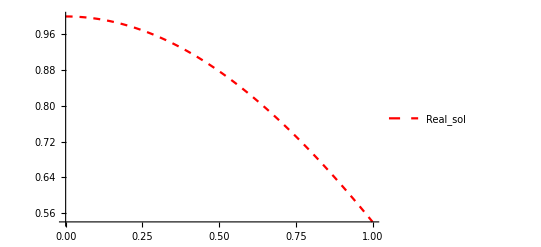

```mathematica
p3=Plot[Cos[x],{x,0,1},PlotStyle->{Red,Dashed},PlotLegends->{"Real_sol"}]
```

```mathematica
Show[p1,p2,p3,p4]
```

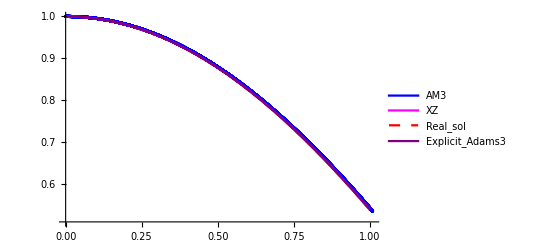

```mathematica
Show[%13,ImageSize->Large,LabelStyle->{18,GrayLevel[0]}]
```

Show::gtype: Out 不是一个图形类别.

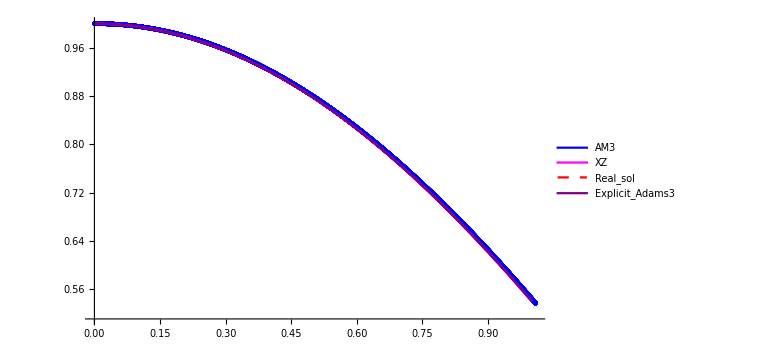

```mathematica
Show[%2,ImageSize->Large,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
-Graphics-
Show[%1,Axes->True,AxesLabel->{"X","Y"},TicksStyle->Directive[Black,18],AxesStyle->Arrowheads[0.03],PlotRange->{{0,1.05},{0.5,1.05}}]
```

-Graphics-

-Graphics-